# JunoCam Processing 24u - Lens/Camera Modeling

## Description

### What it does

Extract control points from multiple cruise stage star field data takes, model lens parameters, produce plots to evaluate modeling, create annotated raw files.

### How it works

A flattening process is applied to each data take to reduce CCD hot pixel artifacts.

Many point sources (potential control points locations) are identified. Point sources from each frame are matched with point sources nearest the expected location in the subsequent three frames. Most matches which are not part of a Red, Green, Blue group are culled.

Control points (which are not uniformly distributed across CCD) are weighted to balance 3 cross-spin regions and also balance contributions from color filter pairings.

Modeling optimizes lens parameter to minimize mean of distances between paired control points forward-transformed to equirectangular coordinates.

Various plots of residuals are produced to help evaluate the model and attempt to identify systematic modeling deficiencies.  

Annotated raw files are produced with circles marking point sources used in modeling. They also show the neighboring flattened and raw image values.

### How to use it

Download 360° data takes from PDS https://pds-imaging.jpl.nasa.gov/data/juno/JNOJNC_0001/DATA/EDR/CRUISE/ 

The selection criteria for the data takes identified in imgFiles below was:

3-color

360° revolution

low-loss compression (larger compressed file size)

Gzip compress the downloaded .IMG files.

Update imgFiles in below ControllingParameters section with the directories and file names on your system.

Open the Juno28g pipeline notebook and evaluate the “Setup” sub-chapter to define various utility functions.
Evaluate the “Setup and Run Everything” chapter in this notebook. Go have a long lunch. Scroll through notebook to verify it completed successfully.

### Caveats

The input data take image (.IMG) dimensions are hard coded.
The code includes various hard-coded parameters (eg expected pixel shift between frames).
The fullFrame_ control points are rotated 90° counterclockwise, so a JunoCam data take is modeled as a left-to-right horizontal panorama. Therefore, control point coordinates and lens parameters are in these rotated coordinates (x is along-spin direction, y is cross-spin direction).
In Mathematica, the center of a pixel is at 1/2,1/2.

### Additional Notes

After a complete run, the slow “Flatten Images” sub-chapter can be skipped by manually selecting and evaluating all the other sub-chapters.

### References/Links

MissionJuno IMAGE PROCESSING GALLERY

Junocam: Juno’s Outreach Camera

Junocam Calibration Report

Software Interface Specification JunoCam Standard Data Products  (contains de-companding table and file name formatting)

Unmanned Spaceflight Juno forum

Junocam PDS archive

CCD Readout Line Locations

Juno JUNOCAM Instrument Kernel

Juno Frames Kernel

CCD filter dimensions CAD diagram

CCD Datasheet KAI-2020

Web interface to SPICE WebGeocalc

Wikipedia Optical Distortion

PanoTools/Hugin Lens Correction Model

PanoTools/Hugin Field of View

Decentering Distortion of Lenses Brown66

Close-Range Camera Calibration Brown71

A Precision Analysis of Camera Distortion Models

A basic CA model - Exposing Digital Forgeries Through Chromatic Aberration

Camera Calibration Toolbox for Matlab - Description of the calibration parameters  and  References  and  Links

Gnomonic Projection

MSS Earth Flyby Images

Mathematica info and help at Stack Exchange

Home of this notebook and other JunoCam tools on Github

### Future Work

Calculate intensity centroids from raw data rather than flattened data

See if higher order models can reduce residuals

Process with more (necessarily higher compressed) images

Use newer model to automate wrap-around shift calculation

Replace hFov (horizontal field of view from Hugin legacy) with focalLength. Collapse focalLength and degPerPixel into single modeled parameter

Determine absolute positions of point sources, and use them to produce camera model with full absolute calibration and relation to spacecraft frame

## Setup and Run Everything

Setup

## Startup

```mathematica
(*Clear["Global`*"]*)
```

```mathematica
startTime=Now
```

Mon 9 Apr 2018 23:05:15GMT-7.

## Controlling Parameters

```mathematica
exportDocsDirectory=$InitialDirectory 
 (* Where "Juno24Matchpoints.csv" and "Juno24InspectionImageList.txt" are exported.
 Flattened image data and annotated raw PDFs are written to the directory containing the input raw image file. *)
```

/Users/bswift

```mathematica
(* NOTE: Changes to imgFiles or fileList below require corresponding updates in spin rate clustering below *)
```

```mathematica
imgFiles={

{"/Users/bswift/Downloads/ORBIT_00/",
{"JNCE_2016129_00C00164_V01.IMG.gz","JNCE_2016129_00C00165_V01.IMG.gz","JNCE_2016130_00C00171_V01.IMG.gz","JNCE_2016131_00C00180_V01.IMG.gz","JNCE_2016164_00C00195_V01.IMG.gz"
(* these are more compressed, but guess they were taking slightly less compressed datatakes every hundred, but are only day apart. *)
(* Only add a few CPs, some of which don't look too good, so not including. *)
(*
,"JNCE_2016165_00C00277_V01.IMG.gz" 
,"JNCE_2016166_00C00377_V01.IMG.gz"
,"JNCE_2016167_00C00477_V01.IMG.gz"
,"JNCE_2016168_00C00577_V01.IMG.gz"
*)
}
}
,{"/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/",
{ 
(* full spin TDI 4 low compression *)
"JNCE_2016026_00C00058_V01.IMG.gz",
"JNCE_2016026_00C00059_V01.IMG.gz","JNCE_2016026_00C00060_V01.IMG.gz","JNCE_2016026_00C00061_V01.IMG.gz","JNCE_2016026_00C00062_V01.IMG.gz","JNCE_2016026_00C00063_V01.IMG.gz","JNCE_2016026_00C00070_V01.IMG.gz","JNCE_2016026_00C00071_V01.IMG.gz","JNCE_2016026_00C00072_V01.IMG.gz","JNCE_2016026_00C00073_V01.IMG.gz","JNCE_2016026_00C00074_V01.IMG.gz","JNCE_2016026_00C00080_V01.IMG.gz","JNCE_2016026_00C00081_V01.IMG.gz","JNCE_2016026_00C00082_V01.IMG.gz","JNCE_2016026_00C00083_V01.IMG.gz",

"JNCE_2016040_00C00094_V01.IMG.gz","JNCE_2016040_00C00095_V01.IMG.gz","JNCE_2016040_00C00096_V01.IMG.gz","JNCE_2016040_00C00097_V01.IMG.gz","JNCE_2016040_00C00098_V01.IMG.gz","JNCE_2016040_00C00099_V01.IMG.gz","JNCE_2016040_00C00105_V01.IMG.gz","JNCE_2016040_00C00106_V01.IMG.gz","JNCE_2016040_00C00107_V01.IMG.gz"}}
(* half spin. Causes stuff to break when mixed with full spin. *)
(*"JNCE_2015268_00C00016_V01.IMG.gz","JNCE_2015268_00C00018_V01.IMG.gz","JNCE_2015268_00C00020_V01.IMG.gz","JNCE_2015268_00C00022_V01.IMG.gz","JNCE_2015268_00C00024_V01.IMG.gz","JNCE_2015268_00C00026_V01.IMG.gz","JNCE_2015268_00C00028_V01.IMG.gz","JNCE_2015268_00C00030_V01.IMG.gz,"
*)
(*,"JNCE_2015268_00C00032_V01.IMG.gz","JNCE_2015268_00C00034_V01.IMG.gz"*) (* these 2 not producing tri-color CPs *)

(* Only able to pull a few CPs from RadiationTrending images. Not worth hassle of dealing with non-full circle data takes *)
(*{"/Users/bswift/Pictures/Jupiter/Junocam/RadiationTrending/"
,{(*"573-ImageSet/JNCE_2016240_00C06180_V02-raw.png",*)"620-ImageSet/JNCE_2016346_03C00135_V02-raw.png","638-ImageSet/JNCE_2017033_04C00119_V01-raw.png","905-ImageSet/JNCE_2017086_05C00121_V01-raw.png","1277-ImageSet/JNCE_2017139_06C00142_V01-raw.png","2049-ImageSet/JNCE_2017192_07C00074_V01-raw.png","2768-ImageSet/JNCE_2017245_08C00134_V01-raw.png","3108-ImageSet/JNCE_2017297_09C00105_V01-raw.png"}
}
*)
};
```

```mathematica
fileList=Flatten[Map[
Function[dirBasenames
,Map[FileNameJoin[{dirBasenames[[1]],#}]&,dirBasenames[[2]]]
],imgFiles(*[[{2}]]*)
]]
```

{/Users/bswift/Downloads/ORBIT_00/JNCE_2016129_00C00164_V01.IMG.gz,/Users/bswift/Downloads/ORBIT_00/JNCE_2016129_00C00165_V01.IMG.gz,/Users/bswift/Downloads/ORBIT_00/JNCE_2016130_00C00171_V01.IMG.gz,/Users/bswift/Downloads/ORBIT_00/JNCE_2016131_00C00180_V01.IMG.gz,/Users/bswift/Downloads/ORBIT_00/JNCE_2016164_00C00195_V01.IMG.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00058_V01.IMG.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00059_V01.IMG.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00060_V01.IMG.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00061_V01.IMG.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00062_V01.IMG.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00063_V01.IMG.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00070_V01.IMG.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00071_V01.IMG.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00072_V01.IMG.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00073_V01.IMG.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00074_V01.IMG.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00080_V01.IMG.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00081_V01.IMG.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00082_V01.IMG.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00083_V01.IMG.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016040_00C00094_V01.IMG.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016040_00C00095_V01.IMG.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016040_00C00096_V01.IMG.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016040_00C00097_V01.IMG.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016040_00C00098_V01.IMG.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016040_00C00099_V01.IMG.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016040_00C00105_V01.IMG.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016040_00C00106_V01.IMG.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016040_00C00107_V01.IMG.gz}

```mathematica
Length[fileList]
```

29

```mathematica
flatClipLevel=2.5; (* Flattened DN values less than this are clipped to 0 *)
```

```mathematica
flatScaleFactor=2; (* Flats multiplied by this before subtracting from image segment *)
```

#### Cluster by Spin Rate

```mathematica
(* Extract START_TIME and INTERFRAME_DELAY parameters from LBL files *)startTimesIFD=Map[FindList[StringReplace[#,"IMG.gz"-> "LBL"],{"START_TIME","INTERFRAME_DELAY"}]&, fileList];
```

```mathematica
startTimesIFD[[{1,-1}]]
```

{{START_TIME                    = 2016-05-08T11:30:02.400,INTERFRAME_DELAY              = 0.372 <s>},{START_TIME                    = 2016-02-09T19:58:02.337,INTERFRAME_DELAY              = 0.372 <s>}}

```mathematica
interframeDelays=ToExpression[StringReplace[startTimesIFD[[All,2]],{__ ~~ "= " -> ""," <s>"->""}]]
```

{0.372,0.372,0.372,0.372,0.372,0.371,0.371,0.371,0.371,0.371,0.371,0.371,0.371,0.371,0.371,0.371,0.371,0.371,0.371,0.371,0.372,0.372,0.372,0.372,0.372,0.372,0.372,0.372,0.372}

```mathematica
(* Export startTimes to text file, which is cut/paste into 
http://wgc.jpl.nasa.gov:8080/webgeocalc/#FrameTransformation
to produce results that include spin rate (AV Magnitude)

Kernel:Juno
Frame1:JUNO_SPACECRAFT
Frame2:J2000
Input: List of Times
Output form:Euler Angles
Rotation Order:ZXZ
Angular Velocity Representation
Output form: Vector in Frame 1
Degrees/second
Download results as CSV
*)
```

```mathematica
(*Export["/tmp/startTimes.txt",StringReplace[startTimesIFD[[All,1]],__ ~~ "= " -> ""]]*)
```

```mathematica
(*frameTransform=Import["/Users/bswift/Downloads/FrameTransformationResults.csv"];*)
```

```mathematica
(* Table produced by importing WebGeocalc results *)
frameTransform={{"Frame Transformation Calculation"},{"Calculation Inputs"},{"Calculation type","Frame Transformation (from Frame 1 to Frame 2)"},{"Frame 1","JUNO_SPACECRAFT"},{"Frame 2","J2000"},{"Time system","UTC"},{"Time format","Calendar date and time"},{"Light propagation","No correction"},{"Orientation form","Euler angles"},{"Rotation order","R = [Angle3]z * [Angle2]x * [Angle1]z"},{"Angular units","Degrees"},{"Angular velocity form","Vector in Frame 1"},{"Angular velocity units","Degrees/second"},{"Frame Transformation Results"},{"UTC  calendar date","Angle 3 (deg)","Angle 2 (deg)","Angle 1 (deg)","AV X (deg/s)","AV Y (deg/s)","AV Z (deg/s)","AV Magnitude (deg/s)"},{"2016-05-08 11:30:02.400000 UTC",102.34001896,97.19732131,77.56802163,0.00425785,-0.0091958,-11.92333653,11.92334084},{"2016-05-08 12:00:02.515000 UTC",102.384951,97.27517693,-145.8373568,0.00471897,-0.0089777,-11.92332798,11.92333229},{"2016-05-09 16:00:02.437000 UTC",102.38303521,97.17872351,22.42611529,0.0047589,-0.00909955,-11.92332023,11.92332465},{"2016-05-10 22:00:02.464000 UTC",102.38533372,97.18019102,21.43906726,0.00502149,-0.0088573,-11.92330704,11.92331139},{"2016-06-12 00:10:02.433000 UTC",102.61699578,96.93670709,18.38002058,0.00538554,-0.00909142,-11.92253811,11.9225428},{"2016-01-26 08:31:02.150000 UTC",89.38241904,92.04893241,32.42949227,0.00498936,-0.00895584,-11.93917906,11.93918347},{"2016-01-26 08:36:02.009000 UTC",89.36735392,92.0533445,52.35088277,0.00508512,-0.00862144,-11.93917938,11.93918358},{"2016-01-26 08:41:02.024000 UTC",89.35491581,92.06125405,70.4108617,0.00506876,-0.00853265,-11.93918406,11.93918819},{"2016-01-26 08:46:01.989000 UTC",89.34321337,92.07373816,89.05726825,0.00484092,-0.00886493,-11.93918415,11.93918843},{"2016-01-26 08:51:02.071000 UTC",89.33796799,92.08669707,106.32671999,0.00495254,-0.00892226,-11.93918812,11.93919248},{"2016-01-26 08:56:02.168000 UTC",89.33753473,92.10067292,123.40611663,0.00503764,-0.00869226,-11.93918918,11.93919341},{"2016-01-26 09:31:02.122000 UTC",89.41700163,92.13441921,-108.37226183,0.00519484,-0.00858371,-11.93919346,11.93919768},{"2016-01-26 09:36:02.130000 UTC",89.42753736,92.12181073,-90.23368982,0.00496721,-0.00872341,-11.93919542,11.93919964},{"2016-01-26 09:41:02.040000 UTC",89.4336677,92.10588515,-70.91728084,0.00482237,-0.00896501,-11.93914372,11.93914806},{"2016-01-26 09:46:02.008000 UTC",89.43347938,92.09100919,-52.2943263,0.00491573,-0.00880386,-11.93918927,11.93919352},{"2016-01-26 09:51:02.023000 UTC",89.42886073,92.07761545,-34.23504731,0.00505331,-0.008597,-11.93918587,11.93919003},{"2016-01-26 10:21:02.006000 UTC",89.35010291,92.06480545,75.40178127,0.00478292,-0.00882257,-11.93917869,11.93918291},{"2016-01-26 10:26:02.021000 UTC",89.34215505,92.07613407,93.46668942,0.00502875,-0.00874065,-11.93917579,11.93918005},{"2016-01-26 10:31:02.083000 UTC",89.33800143,92.08894427,110.96766372,0.00523532,-0.00863601,-11.93918152,11.93918579},{"2016-01-26 10:36:02.048000 UTC",89.3379337,92.10649291,129.61919252,0.00493967,-0.00879361,-11.93920315,11.93920741},{"2016-02-09 19:10:02.305000 UTC",90.83645398,92.81399267,-140.12060032,0.0049751,-0.00860949,-11.93060848,11.93061263},{"2016-02-09 19:13:02.465000 UTC",90.84597273,92.81176124,-129.54796323,0.00485293,-0.0087758,-11.93063667,11.93064089},{"2016-02-09 19:16:02.356000 UTC",90.8572959,92.80558861,-115.76248924,0.00457668,-0.00893278,-11.93062159,11.93062581},{"2016-02-09 19:19:02.383000 UTC",90.86529591,92.79823506,-103.59841423,0.00447112,-0.00903994,-11.93061994,11.9306242},{"2016-02-09 19:22:02.238000 UTC",90.87251354,92.78764242,-89.38312451,0.00434182,-0.00915443,-11.93063164,11.93063594},{"2016-02-09 19:26:02.257000 UTC",90.87667751,92.77287939,-72.96479194,0.00407174,-0.00929384,-11.93063655,11.93064087},{"2016-02-09 19:50:02.471000 UTC",90.83151533,92.72016642,24.3666508,0.00475181,-0.00855575,-11.93060844,11.93061246},{"2016-02-09 19:54:02.381000 UTC",90.81767212,92.72129018,42.0866944,0.00482371,-0.00850179,-11.93064704,11.93065105},{"2016-02-09 19:58:02.337000 UTC",90.80219533,92.72654386,59.24955042,0.00445427,-0.00889284,-11.93062481,11.93062896},{"Kernels Used"},{"pds/data/jno-j_e_ss-spice-6-v1.0/jnosp_1000/extras/mk/juno_2016_v02.tm"}};
```

```mathematica
Plus @@@ frameTransform[[16;;-3,{7,8}]]  (* Difference between AV Z and AV Magnitude, minimal*)
```

{4.31×10^-6,4.31×10^-6,4.42×10^-6,4.35×10^-6,4.69×10^-6,4.41×10^-6,4.2×10^-6,4.13×10^-6,4.28×10^-6,4.36×10^-6,4.23×10^-6,4.22×10^-6,4.22×10^-6,4.34×10^-6,4.25×10^-6,4.16×10^-6,4.22×10^-6,4.26×10^-6,4.27×10^-6,4.26×10^-6,4.15×10^-6,4.22×10^-6,4.22×10^-6,4.26×10^-6,4.3×10^-6,4.32×10^-6,4.02×10^-6,4.01×10^-6,4.15×10^-6}

```mathematica
yawRates=frameTransform[[16;;-3,8]] (* extract Angular Velocity Magnitude from SPICE results *)
```

{11.9233,11.9233,11.9233,11.9233,11.9225,11.9392,11.9392,11.9392,11.9392,11.9392,11.9392,11.9392,11.9392,11.9391,11.9392,11.9392,11.9392,11.9392,11.9392,11.9392,11.9306,11.9306,11.9306,11.9306,11.9306,11.9306,11.9306,11.9307,11.9306}

```mathematica
Length[yawRates]  (* should have same numuber of values as in file list *)
```

29

```mathematica
Length[fileList]
```

29

```mathematica
labeledYawRates=MapIndexed[#1-> #2[[1]]&,yawRates]
```

{11.9233→1,11.9233→2,11.9233→3,11.9233→4,11.9225→5,11.9392→6,11.9392→7,11.9392→8,11.9392→9,11.9392→10,11.9392→11,11.9392→12,11.9392→13,11.9391→14,11.9392→15,11.9392→16,11.9392→17,11.9392→18,11.9392→19,11.9392→20,11.9306→21,11.9306→22,11.9306→23,11.9306→24,11.9306→25,11.9306→26,11.9306→27,11.9307→28,11.9306→29}

```mathematica
yawRateClusterIndicies=FindClusters[labeledYawRates]
```

{{1,2,3,4,5},{6,7,8,9,10,11,12,13,14,15,16,17,18,19,20},{21,22,23,24,25,26,27,28,29}}

```mathematica
yawRateClusters=Map[yawRates[[#]]&,yawRateClusterIndicies]
```

{{11.9233,11.9233,11.9233,11.9233,11.9225},{11.9392,11.9392,11.9392,11.9392,11.9392,11.9392,11.9392,11.9392,11.9391,11.9392,11.9392,11.9392,11.9392,11.9392,11.9392},{11.9306,11.9306,11.9306,11.9306,11.9306,11.9306,11.9306,11.9307,11.9306}}

```mathematica
yawRateVariation=Map[#-Median[#]&,yawRateClusters]
```

{{0.00001619,7.64×10^-6,0.,-0.00001326,-0.00078185},{-4.96×10^-6,-4.85×10^-6,-2.4×10^-7,0.,4.05×10^-6,4.98×10^-6,9.25×10^-6,0.00001121,-0.00004037,5.09×10^-6,1.6×10^-6,-5.52×10^-6,-8.38×10^-6,-2.64×10^-6,0.00001898},{-0.00001633,0.00001193,-3.15×10^-6,-4.76×10^-6,6.98×10^-6,0.00001191,-0.0000165,0.00002209,0.}}

```mathematica
yawRateTolerance=1/27 (* degree / pixel roughly conservitavely *)  1/4 (* pixel tolerance over a rotation *) / (82 (* frames per rotation *) .372 (* sec per frame *))   (* yaw per second variation that will result in less than 1/4 pixel variation in a wrap around match *)
```

0.000303542

```mathematica
yawRateOK=Map[Abs[#]< yawRateTolerance&,yawRateVariation,{-1}]
```

{{True,True,True,True,False},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True}}

```mathematica
tightYawRateClusters=MapThread[Pick[#1,#2]&,{yawRateClusterIndicies,yawRateOK}]
```

{{1,2,3,4},{6,7,8,9,10,11,12,13,14,15,16,17,18,19,20},{21,22,23,24,25,26,27,28,29}}

```mathematica
Map[interframeDelays[[#]]&,tightYawRateClusters] (* verify IFDs same in each cluster *)
```

{{0.372,0.372,0.372,0.372},{0.371,0.371,0.371,0.371,0.371,0.371,0.371,0.371,0.371,0.371,0.371,0.371,0.371,0.371,0.371},{0.372,0.372,0.372,0.372,0.372,0.372,0.372,0.372,0.372}}

```mathematica
yawPerFrameIFDSpice=(interframeDelays+.0010) yawRates
```

{4.44741,4.4474,4.4474,4.4474,4.44711,4.44138,4.44138,4.44138,4.44138,4.44138,4.44138,4.44138,4.44138,4.44136,4.44138,4.44138,4.44138,4.44137,4.44138,4.44139,4.45012,4.45013,4.45012,4.45012,4.45013,4.45013,4.45012,4.45013,4.45012}

```mathematica
meanClusterYawRate=Map[Mean[yawRates[[#]] ]&,tightYawRateClusters]
```

{11.9233,11.9392,11.9306}

```mathematica
meanClusterYawPerFrame=Map[Mean[yawPerFrameIFDSpice[[#]] ]&,tightYawRateClusters]
```

{4.4474,4.44138,4.45013}

```mathematica
yawRateClusterIndicies
```

{{1,2,3,4,5},{6,7,8,9,10,11,12,13,14,15,16,17,18,19,20},{21,22,23,24,25,26,27,28,29}}

```mathematica
(* added 5 as its own cluster and split other two larger clusters *)
modelClusterRanges={Range[1,4],{5},Range[6,12],Range[13,20],Range[21,24],Range[25,29]}
```

{{1,2,3,4},{5},{6,7,8,9,10,11,12},{13,14,15,16,17,18,19,20},{21,22,23,24},{25,26,27,28,29}}

```mathematica
modelClusterRanges=Table[{fn},{fn,29}] (* Every file its own cluster. Tilt and pitch modeled by cluster. *)
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27},{28},{29}}

```mathematica
(* Four clusters, with 5 as its own cluster. Problem with params generated for 5 when modeled w/o constraints. *)
modelClusterRanges={Range[1,4],{5},Range[6,20],Range[21,29]}
```

{{1,2,3,4},{5},{6,7,8,9,10,11,12,13,14,15,16,17,18,19,20},{21,22,23,24,25,26,27,28,29}}

```mathematica
(* Four clusters, with 5 as its own cluster. Problem with params generated for 5 when modeled w/o constraints. *)
modelClusterRanges={Range[1,4],Range[6,20],Range[21,29]}
```

{{1,2,3,4},{6,7,8,9,10,11,12,13,14,15,16,17,18,19,20},{21,22,23,24,25,26,27,28,29}}

```mathematica
(* Everything as one cluster, since spin pointing analysis shows very litle variation in spin point direction *)
modelClusterRanges={Range[1,29]}
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29}}

```mathematica
tightYawRateClusters=modelClusterRanges
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29}}

```mathematica
fnToCn=Association[Flatten[MapIndexed[#1-> #2[[1]]&,modelClusterRanges,{2}]]] (* fileNumber to clusterNumber map *)
```

<|1→1,2→1,3→1,4→1,5→1,6→1,7→1,8→1,9→1,10→1,11→1,12→1,13→1,14→1,15→1,16→1,17→1,18→1,19→1,20→1,21→1,22→1,23→1,24→1,25→1,26→1,27→1,28→1,29→1|>

## Definitions and Functions

### Filename Transformations

```mathematica
(* StringReplace[] transforms of input raw image to various output filenames.
This is brittle because a filename that doesn't have an expected extension will not be modified by StringReplace[], possibly causing input image to be overwritten. *)
```

```mathematica
imgSuffix=(".IMG.gz"~~EndOfString)|(".IMG"~~EndOfString)| ("-raw.png"~~EndOfString)
```

(.IMG.gz~~EndOfString)|(.IMG~~EndOfString)|(-raw.png~~EndOfString)

```mathematica
imgToFlattenedSegsFilenameGZ={imgSuffix-> "_"<>ToString[flatScaleFactor]<>"_flattenedSegs.mx.gz"}
```

{(.IMG.gz~~EndOfString)|(.IMG~~EndOfString)|(-raw.png~~EndOfString)→_2_flattenedSegs.mx.gz}

```mathematica
imgToFlattenedSegsFilename={imgSuffix-> "_"<>ToString[flatScaleFactor]<>"_flattenedSegs.mx"}
```

{(.IMG.gz~~EndOfString)|(.IMG~~EndOfString)|(-raw.png~~EndOfString)→_2_flattenedSegs.mx}

```mathematica
imgToFlatFilename={imgSuffix-> "_flat_data.mx.gz"}
```

{(.IMG.gz~~EndOfString)|(.IMG~~EndOfString)|(-raw.png~~EndOfString)→_flat_data.mx.gz}

```mathematica
imgToInspectionImageFilename={imgSuffix-> "_inspectionImage.png"}
```

{(.IMG.gz~~EndOfString)|(.IMG~~EndOfString)|(-raw.png~~EndOfString)→_inspectionImage.png}

```mathematica
imgToAnnotatedRawPDFFilename={(".IMG.gz"~~EndOfString)|(".IMG"~~EndOfString)|("-raw.png"~~EndOfString)->"_annRaw.pdf" }
```

{(.IMG.gz~~EndOfString)|(.IMG~~EndOfString)|(-raw.png~~EndOfString)→_annRaw.pdf}

```mathematica
(* Quick way to view annotated raw file by specifying fileList index.
 Run["open "<>StringReplace[fileList⟦14⟧,imgToAnnotatedRawPDFFilename]]
*)
```

### Tooltip value formatting

```mathematica
ClearAll[fmtNum]
```

```mathematica
(* Order of definitions is important *)
```

```mathematica
fmtNum[intNum_?IntegerQ]:=intNum
```

```mathematica
fmtNum[num_?NumericQ/;Abs[num]>.05]:=N[Round[num,1/100]]
```

```mathematica
fmtNum[num_?NumericQ/;Abs[num]≤ .05]:=num
```

```mathematica
fmtNum[nonNum_]:=ToString[nonNum]
```

```mathematica
?fmtNum
```

Global`fmtNum

fmtNum[intNum_?IntegerQ]:=intNum
 
fmtNum[num_?NumericQ/;Abs[num]>0.05]:=N[Round[num,1/100]]
 
fmtNum[num_?NumericQ/;Abs[num]≤0.05]:=num
 
fmtNum[nonNum_]:=ToString[nonNum]

```mathematica
fmtNum[3]
```

3

```mathematica
fmtNum[-1/3]//InputForm
```

-0.33

```mathematica
fmtNum[-.025]//InputForm
```

-0.025

```mathematica
fmtNum[{"some string",123}]
```

{some string, 123}

### Misc/Plotting

```mathematica
myColorList={Hue[0.7537764387886847, 0.7889133312376433, 0.8340392114442323],Hue[0.7138535511262305, 0.41492502788445695, 0.8068190170587421],Hue[0.6199933206365296, 0.7470660055206566, 0.7409503548023814],Hue[0.4625254574785933, 0.506037471513137, 0.7964982556578655],Hue[0.9082638991617842, 0.8426997616142345, 0.8480178099900859],Hue[0.9689248693976225, 0.7888139049313905, 0.9404050414659318],Hue[0.1398146399624529, 0.5056593178969222, 0.7106170426567952],Hue[0.07576005092093419, 0.4368476550582213, 0.881437734636851],Hue[0.2901954641974973, 0.5960608284924898, 0.7666029655305671],Hue[0.2104844069903553, 0.5581567642684924, 0.9068342813040111],Hue[0.5266688223574596, 0.7895576093480536, 0.8213124443634353],Hue[0.03866605810675705, 0.464623847831265, 0.7781760571055475],Hue[0.06851238833835138, 0.8213777847954221, 0.7418133975845673],Hue[0.5643500139107251, 0.8695510374660319, 0.8063996403870803],Hue[0.5833061994196727, 0.5382112577114793, 0.9424254778833618]}
```

{Hue[0.7537764387886847, 0.7889133312376433, 0.8340392114442323],Hue[0.7138535511262305, 0.41492502788445695, 0.8068190170587421],Hue[0.6199933206365296, 0.7470660055206566, 0.7409503548023814],Hue[0.4625254574785933, 0.506037471513137, 0.7964982556578655],Hue[0.9082638991617842, 0.8426997616142345, 0.8480178099900859],Hue[0.9689248693976225, 0.7888139049313905, 0.9404050414659318],Hue[0.1398146399624529, 0.5056593178969222, 0.7106170426567952],Hue[0.07576005092093419, 0.4368476550582213, 0.881437734636851],Hue[0.2901954641974973, 0.5960608284924898, 0.7666029655305671],Hue[0.2104844069903553, 0.5581567642684924, 0.9068342813040111],Hue[0.5266688223574596, 0.7895576093480536, 0.8213124443634353],Hue[0.03866605810675705, 0.464623847831265, 0.7781760571055475],Hue[0.06851238833835138, 0.8213777847954221, 0.7418133975845673],Hue[0.5643500139107251, 0.8695510374660319, 0.8063996403870803],Hue[0.5833061994196727, 0.5382112577114793, 0.9424254778833618]}

```mathematica
filterPlotLines=MapThread[
Style[#1,#2,AbsoluteThickness[0.6]]&,{Flatten[Map[{{#,0},{#,1648}}&,filterRanges,{-1}],1]
,{Red,Red,Green,Green,Blue,Blue}}
]
```

{{{766,0},{766,1648}},{{894,0},{894,1648}},{{611,0},{611,1648}},{{739,0},{739,1648}},{{456,0},{456,1648}},{{584,0},{584,1648}}}

```mathematica
(* Residuals are weighted to balance contribution by top, middle and bottom regions (thrids), since CPs are not uniformly distributed across CCD.
*)
topBottomBalanceSizeN=Abs[normalizeXY[{0,ccdSize[[2]]/3.}][[2]]]; (* 1/3 of filter long axis *)
balancePlotLines=MapThread[Style[#1,#2,AbsoluteThickness[0.6]]&,
{
{{deNormalizeXnYn[{-1,topBottomBalanceSizeN}],deNormalizeXnYn[{1,topBottomBalanceSizeN}]},
{deNormalizeXnYn[{-1,-topBottomBalanceSizeN}],deNormalizeXnYn[{1,-topBottomBalanceSizeN}]}
}
,{Cyan,Cyan}
}
]
```

{{{0,1098.67},{1214,1098.67}},{{0,549.333},{1214,549.333}}}

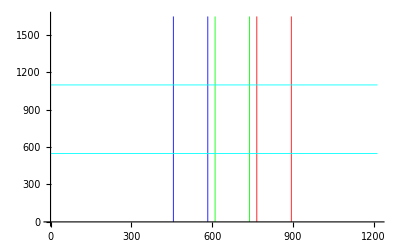

```mathematica
ListLinePlot[Join[filterPlotLines,balancePlotLines]]
```

### Filter Pair Coloring

Support for coloring points in plots based on the filter colors of the control points.

```mathematica
filterRanges
```

{{766,894},{611,739},{456,584}}

```mathematica
ptColorId[{x_,y_}]:=Which[x≥ 765,1,x≤ 585,3,True,2]
```

```mathematica
ptColor[pt_]:={Red,Green,Blue}[[ptColorId[pt] ]]
```

```mathematica
colorCP[{pt1_,pt2_}]:=RGBColor@@(Map[Clip[#,{0,.99}]&,Plus[List@@ptColor[pt1],List@@ptColor[pt2]]]) (* Saturated add of two colors *)
```

```mathematica
{Cyan,Magenta,Yellow}
```

{RGBColor[0, 1, 1],RGBColor[1, 0, 1],RGBColor[1, 1, 0]}

```mathematica
Map[ptColor,filterRanges]
```

{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]}

```mathematica
Map[colorCP,Subsets[filterRanges,{2}]]
```

{RGBColor[0.99, 0.99, 0],RGBColor[0.99, 0, 0.99],RGBColor[0, 0.99, 0.99]}

```mathematica
Table[colorCP[{i,j}],{i,filterRanges},{j,filterRanges}]
```

{{RGBColor[0.99, 0, 0],RGBColor[0.99, 0.99, 0],RGBColor[0.99, 0, 0.99]},{RGBColor[0.99, 0.99, 0],RGBColor[0, 0.99, 0],RGBColor[0, 0.99, 0.99]},{RGBColor[0.99, 0, 0.99],RGBColor[0, 0.99, 0.99],RGBColor[0, 0, 0.99]}}

```mathematica
filterCenters=Mean /@ filterRanges
```

{830,675,520}

```mathematica
colorPairs=Map[Transpose[{#,{0,0}}]&,DeleteDuplicates[Map[Sort,Subsets[Join[filterCenters,filterCenters],{2}]]]]
```

{{{675,0},{830,0}},{{520,0},{830,0}},{{830,0},{830,0}},{{520,0},{675,0}},{{675,0},{675,0}},{{520,0},{520,0}}}

```mathematica
legendPairs=Transpose[Map[
{colorCP[#]
,Row[{"← ",ptColor[#⟦1⟧],"+",ptColor[#⟦2⟧]}]
}&,colorPairs]]
```

{{RGBColor[0.99, 0.99, 0],RGBColor[0.99, 0, 0.99],RGBColor[0.99, 0, 0],RGBColor[0, 0.99, 0.99],RGBColor[0, 0.99, 0],RGBColor[0, 0, 0.99]},{← RGBColor[0, 1, 0]+RGBColor[1, 0, 0],← RGBColor[0, 0, 1]+RGBColor[1, 0, 0],← RGBColor[1, 0, 0]+RGBColor[1, 0, 0],← RGBColor[0, 0, 1]+RGBColor[0, 1, 0],← RGBColor[0, 1, 0]+RGBColor[0, 1, 0],← RGBColor[0, 0, 1]+RGBColor[0, 0, 1]}}

```mathematica
filterPairingsLegend=PointLegend[legendPairs⟦1⟧,legendPairs⟦2⟧
,LegendMarkers->Graphics[Disk[]]
,LegendLabel-> "Filter Pairings"
]
```

### Flats

#### Identify Dark Segments

```mathematica
(* Investigation of range of total energy in space facing segments to determine threshold for rejectBrightSegs[] filter. *)
(*AbsoluteTiming[
segTotals=Map[MinMax[Sort[Flatten[Map[Total[Flatten[ImageData[#1]]]&
,segs=rgb[imgObj=loadChannelsFn[#]],{-1}] ]]]&
,fileList[[1;;-1]]]
] *)(* 102.1 sec *)
```

```mathematica
(*SortBy[segTotals,Last]*)
```

```mathematica
rejectBrightSegs[darkestSegmentIndicies_,segs_]:= MapThread[
Function[{indicies,segList},
Map[If[Total[Flatten[ImageData[
segList[[#,1]]
]]] < 500.  (* 500. is over twice as much as largest cruise stage / orbit 0 segments *)
,#
,Nothing
,Print["Unexpected case B9"];Nothing
]&,indicies]
]
,{darkestSegmentIndicies,segs}]
```

```mathematica
identifyDarkSegmentsSlow[imageObj_]:=Block[
{segs,trimmedMeans,darkMetric,orderedDarkMetrics,orderedDarkMetricsOrig,fractionOfDarkestSegs,darkSegsCount,darkSegsCountOrig,darkestSegmentIndicies},
segs=rgb[imageObj];
(* TrimmedMeans - average after discarding lower 99% , so brightness of upper 1% as metric of how bright a segment is. *)
AbsoluteTiming[Parallelize[
trimmedMeans=Map[
Table[TrimmedMean[Flatten[ImageData[#]],{trim,0}],{trim,{.99}}]&
,segs,{-1}];
]]   (* 97.3 no parallelize *);
Print[ListLogPlot[Table[trimmedMeans[[#,All,1,cl]],{cl,1,1}],PlotLegends->{99},PlotLabel-> rgbFilterNames[imageObj][[#]],ImageSize->Large,PlotRange->Full] & /@ Range[Length[trimmedMeans]] // Column
];
darkMetric=trimmedMeans[[All,All,1,1]];
(* Look at fraction of pixels that are non-zero as darkness metric *)
orderedDarkMetricsOrig=Map[Ordering,darkMetric];
orderedDarkMetrics=rejectBrightSegs[orderedDarkMetricsOrig,segs];
Print[{"orderedDarkMetrics",orderedDarkMetrics}];
fractionOfDarkestSegs=.6  (* fraction of segs used to create flats. Brightest segs not not used for flat generation *);
darkSegsCountOrig=Round[fractionOfDarkestSegs Length[orderedDarkMetricsOrig[[1]]]];
darkSegsCount=Round[fractionOfDarkestSegs Min[Length /@ orderedDarkMetrics]];
Print[{"darkSegsCountOrig",darkSegsCountOrig,"darkSegsCount",darkSegsCount}];
darkestSegmentIndicies=Map[Sort[Take[#,darkSegsCount]]&,orderedDarkMetrics];
darkestSegmentIndicies
]
```

```mathematica
identifyDarkSegmentsLessSlow[imageObj_]:=Block[
{segs,trimmedMeans,darkMetric,orderedDarkMetrics,fractionOfDarkestSegs,darkSegsCount,darkestSegmentIndicies},
segs=rgb[imageObj];
(* TrimmedMeans - here is just total of DNs in segment *)
AbsoluteTiming[Parallelize[
trimmedMeans=Map[
{Total[Flatten[ImageData[#]]]}&
,segs,{-1}];
]]   (* 97.3 no parallelize *);
Print[ListLogPlot[Table[trimmedMeans[[#,All,1,cl]],{cl,1,1}],PlotLegends->{"Totals"},PlotLabel-> rgbFilterNames[imageObj][[#]],ImageSize->Large,PlotRange->All] & /@ Range[Length[trimmedMeans]] // Column
];
darkMetric=trimmedMeans[[All,All,1,1]];
(* Look at fraction of pixels that are non-zero as darkness metric *)
orderedDarkMetrics=Map[Ordering,darkMetric];
fractionOfDarkestSegs=.6  (* fraction of segs used to create flats. Brightest segs not not used for flat generation *);
darkSegsCount=Round[fractionOfDarkestSegs Length[orderedDarkMetrics[[1]]]];
darkestSegmentIndicies=Map[Sort[Take[#,darkSegsCount]]&,orderedDarkMetrics];
darkestSegmentIndicies
]
```

```mathematica
identifyDarkSegments=identifyDarkSegmentsSlow (* identifyDarkSegmentsLessSlow *)
```

identifyDarkSegmentsSlow

#### Create Flat

Flat will be per pixel trimmed mean of segments.  Trimming set to exclude a few of the brightest pixels/segments to exclude stars or other outliers.

```mathematica
createFlat[imageObj_,darkestSegmentIndicies_]:=Block[
{segs,darkSegs,darkSegsData,segCountForMean,flatData,flatTotals,flatImages,flatImagesAdj,flatObj},
segs=rgb[imageObj];
(*Dimensions[segs]*)
(*Dimensions[darkestSegmentIndicies]*)

darkSegs=MapThread[#1[[#2,1]]&,{segs,darkestSegmentIndicies}];
(*Dimensions[darkSegs]*)
darkSegsData=Map[ImageData,darkSegs,{-1}];
(*Dimensions[darkSegsData]*)
segCountForMean=Dimensions[darkSegsData][[2]];  (* should be same as darkSegsCount *)
(*Dimensions[Transpose[darkSegsData,{1,4,2,3}]]*)
AbsoluteTiming[Parallelize[flatData=Map[TrimmedMean[#,{0,2/segCountForMean}]&
,Transpose[darkSegsData,{1,4,2,3}],{-2}]];
];  (* 17.2
62.4 serial 29.0 parallel*)
(*Dimensions[flatData]*)
flatTotals=Map[Total[Flatten[#]]&,flatData];
flatImages=Map[Image[#,"Real32"]&,flatData];
(*imageInfo /@ flatImage*)
(flatImagesAdj=ImageAdjust[#,{0,0,1},{0,8/2879.}]& /@ flatImages)(* // Column*);
flatObj=<|"flatData"->flatData,"flatTotals"->flatTotals,"flatImages"->flatImages,"flatImagesAdj"-> flatImagesAdj|>;
flatObj
]
```

```mathematica
(*If[!AssociationQ[allFlats],allFlats=<||>]*)
```

```mathematica
(*key=imageObj[["fnBaseName"]]*)
```

```mathematica
(*AssociateTo[allFlats,key-><|totals->flatTotals,image->flatImage,adjImage-> flatImageAdj|>]*)
```

Totals from Radiation Trending images
“JNCE_2016346_03C00135_V02-raw.png”→<|totals→{23.8548,22.5877,21.3286}
”JNCE_2017033_04C00119_V01-raw.png”→<|totals→{20.4339,19.0603,18.0262}
“JNCE_2017086_05C00121_V01-raw.png”→<|totals→{21.934,20.3304,18.9347}
“JNCE_2017139_06C00142_V01-raw.png”→<|totals→{21.0001,20.1315,17.801}
“JNCE_2017192_07C00074_V01-raw.png”→<|totals→{21.2407,20.0926,18.3445}
“JNCE_2017245_08C00134_V01-raw.png”→<|totals→{23.3757,21.8327,20.2283}  TDI 3

Cruise
“JNCE_2016026_00C00083_V01.IMG.bz2”→<|totals→{66.6138,66.1302,65.544}  smallest low-compressibility image  75% dark seg selection
“JNCE_2016026_00C00083_V01.IMG.bz2”→<|totals→{65.5505,65.1885,64.859}  60% dark seg selection  (to exclude systematic brightening (zodiacal light?))

“JNCE_2016040_00C00107_V01.IMG.bz2”→<|totals→{86.6506,85.2731,83.7331}

```mathematica
(*allFlats[key][totals]/(128 1648) 2879 *) (* Flat magnitude in decompanded/Linear units *)
```

#### Apply flat to segments

```mathematica
applyFlatToSegments[imageObj_,flatObj_]:=Block[
{segs,scaledFlatImages,flattenedSegs,fic},
segs=rgb[imageObj];

(*Dimensions[segs]*)
(*Dimensions[flatImage]*)
scaledFlatImages=Map[ImageMultiply[#,flatScaleFactor]&,flatObj[["flatImages"]]];
(*Dimensions[scaledFlatImage]*)
flattenedSegs=MapThread[(fic=#1;
Map[ImageSubtract[#,fic]&,#2,{-1}])&, {scaledFlatImages,segs}];  (* Nested Map *)
(*Dimensions[flattenedSegs]*)
(*flattenedImage=ImageAdjust[ImageAssemble[flattenedSegs],{0,0,1},{0,8/2879.}]*)
(*imageInfo[flattenedSegs[[1,1,1]]]*)
flattenedSegs
]
```

#### Export flatData

```mathematica
(*Export[StringReplace[imageObj[["fnPathName"]],{"/JNCE_"->"/Flat_data_",".IMG.bz2"->".wdx"}]
,flatData]*)
```

```mathematica
segsToInspectionImage[flattenedSegs_]:=Block[
{adjSegs,colorSegs,inspectionImage},
adjSegs=Map[ImageAdjust[#,{0,0,1},{flatClipLevel/2879,{1,1,.05}8/2879.}]&,flattenedSegs,{-1}];
(*“JNCE_2016026_00C00083_V01.IMG.bz2”->flat scale 3,crush 3.5*)
colorSegs=Transpose[Map[ColorCombine,Transpose[adjSegs,{3,2,1}],{-2}]];
inspectionImage=MaxFilter[ImageAssemble[colorSegs],3];
inspectionImage
]
```

```mathematica
exportFlatData[imageObj_,flatObj_,flattenedSegs_]:=Block[
{flatData,adjSegs,colorSegs,inspectionImage,uncompressedFlattenedSegsFilename},
flatData=flatObj[["flatData"]];
(*AbsoluteTiming[DumpSave[StringReplace[imageObj[["fnPathName"]],{"/JNCE_"->"/Flat_data_",".IMG.bz2"->".mx"}]
,flatData];];*)  (* export to .wdx super slow *)
AbsoluteTiming[Export[StringReplace[imageObj[["fnPathName"]],imgToFlatFilename ]
,flatData];];  (* export to .wdx super slow *)(*AbsoluteTiming[Export[StringReplace[imageObj[["fnPathName"]],{"/JNCE_"->"/flattenedSegs_",".IMG.bz2"->".mx.bz2"}]
,flattenedSegs];]  ;*)
uncompressedFlattenedSegsFilename=StringReplace[imageObj[["fnPathName"]],imgToFlattenedSegsFilename];
AbsoluteTiming[Export[uncompressedFlattenedSegsFilename,flattenedSegs];] ;
Run["gzip -f",uncompressedFlattenedSegsFilename];

(* star inspection image *)
adjSegs=Map[ImageAdjust[#,{0,0,1},{flatClipLevel/2879,{1,1,.05}8/2879.}]&,flattenedSegs,{-1}];
(*“JNCE_2016026_00C00083_V01.IMG.bz2”->flat scale 3,crush 3.5*)
colorSegs=Transpose[Map[ColorCombine,Transpose[adjSegs,{3,2,1}],{-2}]];
inspectionImage=MaxFilter[ImageAssemble[colorSegs],3];
AbsoluteTiming[Export[StringReplace[imageObj[["fnPathName"]],imgToInspectionImageFilename ]
,inspectionImage];]  ;
]
```

```mathematica
imgToFlattenedSegsFilename
```

{(.IMG.gz~~EndOfString)|(.IMG~~EndOfString)|(-raw.png~~EndOfString)→_2_flattenedSegs.mx}

Export visible flat

Color image to read actual values off Blue channel.

coloredFlats = MapThread[Image[ColorCombine[{#1, #1, #2}], "Bit16"] &, {flatImageAdj, flatImage}]

MapThread[{#1, #2} &, {coloredFlats, rgbFilters[imageObj]}]

Map[imageInfo, coloredFlats]

(* Export derived flats back to source directory *)

MapThread[
 Export[StringReplace[imageObj[["fnPathName"]], "/JNCE_" -> "/Flat_" <> #2 <> "_"], #1]
  &, {coloredFlats, rgbFilters[imageObj]}]

#### Pipeline - process a “.IMG” fileName producing flat related files

```mathematica
imgToFlat[fileName_]:= Block[
{imageObj,darkestSegmentIndicies,flatObj,flattenedSegs},
imageObj=loadChannelsFn[fileName];
Print["fnBaseName = ",imageObj[["fnBaseName"]]];
darkestSegmentIndicies=identifyDarkSegments[imageObj];
Print["darkestSegmentIndicies = ",darkestSegmentIndicies];
flatObj=createFlat[imageObj,darkestSegmentIndicies];
Print["flatTotals = ",flatObj[["flatTotals"]]];
flattenedSegs=applyFlatToSegments[imageObj,flatObj];
exportFlatData[imageObj,flatObj,flattenedSegs];
]
```

#### Merge Segments from flattenedSegFilename

```mathematica
mergeSegsFromFile1[segs_,flattenedSegsFilename_]:=Block[
{mergedSegs,segsToMerge,mergeLevel},
segsToMerge=Import[flattenedSegsFilename];
mergeLevel=ArrayDepth[segs];
mergedSegs=MapThread[ImageAdd,{segs,segsToMerge},mergeLevel]; (* MapThread fails to Parallelize[] *)
Print[FileNameTake[flattenedSegsFilename]<>" Merged "<>DateString["Time"]<>" MaxMemoryUsed "<>ToString[MaxMemoryUsed[]]];
mergedSegs
]
```

```mathematica
clipFlattenedSeg[img_]:=Block[
{},
ImageClip[img,{flatClipLevel/2879,1},{0,1}]
]
```

```mathematica
mergeSegsFromFile[segs_,flattenedSegsFilename_]:=Block[
{mergedSegs,segsToMerge,mergeLevel},
segsToMerge=Import[flattenedSegsFilename];
mergeLevel=ArrayDepth[segs];
mergedSegs=MapThread[
ImageAdd[#1,clipFlattenedSeg[#2]]&,
{segs,segsToMerge},mergeLevel]; (* MapThread fails to Parallelize[] *)
Print[FileNameTake[flattenedSegsFilename]<>" Merged "<>DateString["Time"]<>" MaxMemoryUsed ",MaxMemoryUsed[]];
mergedSegs
]
```

### Startup

```mathematica
$Context
```

Global`

```mathematica
(*Names[$Context<>"*"]*)
```

```mathematica
MaxMemoryUsed[]
```

179683384

Flatten Images

Read list of PDS format (JNCE_*.IMG) path names to be processed into flattened segments and flat data Mathematica data files and inspection image files.

```mathematica
fileList[[{1,-1}]] (* first and last files *)
```

{/Users/bswift/Downloads/ORBIT_00/JNCE_2016129_00C00164_V01.IMG.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016040_00C00107_V01.IMG.gz}

```mathematica
MemoryInUse[] (* 159954752 *)
```

169652000

```mathematica
fileList[[{1}]]
```

{/Users/bswift/Downloads/ORBIT_00/JNCE_2016129_00C00164_V01.IMG.gz}

```mathematica
Length[fileList]
```

29

fnBaseName = JNCE_2016129_00C00164_V01.IMG.gz

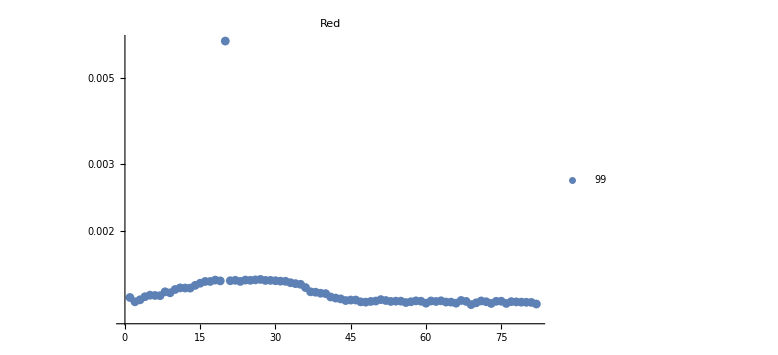
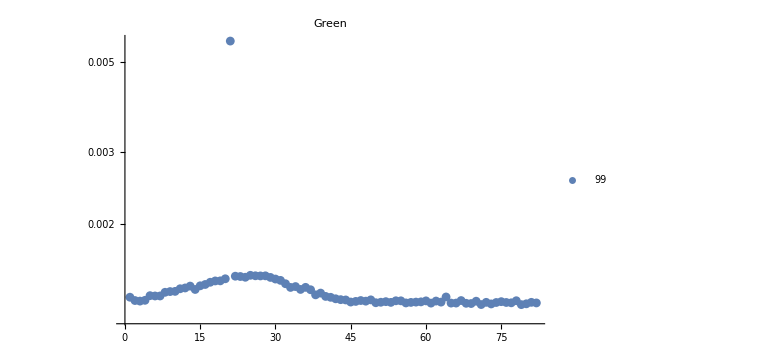
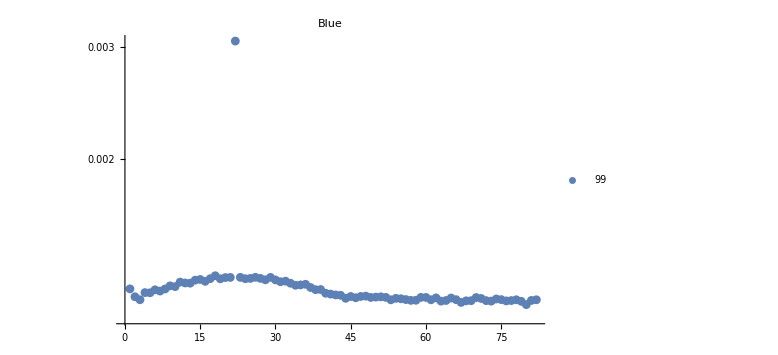

{orderedDarkMetrics,{{69,82,73,76,66,60,70,56,81,80,79,48,65,64,78,47,2,57,72,77,62,53,49,68,74,59,75,54,55,50,61,71,58,63,44,52,67,45,46,3,51,43,42,1,41,4,7,6,5,40,39,9,38,37,8,10,13,12,11,36,14,35,34,15,33,17,16,23,32,31,19,21,30,28,29,25,22,18,24,26,27,20},{79,71,73,80,69,68,61,65,66,56,82,77,50,74,76,57,53,81,72,51,58,63,45,59,75,52,46,70,48,3,62,60,55,54,78,67,2,47,4,44,49,43,42,41,1,64,40,6,7,5,38,39,8,9,10,37,14,35,11,12,33,36,34,13,15,16,32,17,18,19,31,30,20,29,24,23,22,27,28,26,25,21},{80,67,79,63,73,76,68,69,72,77,64,81,57,58,53,61,78,82,3,66,75,56,74,55,71,54,44,65,62,46,70,60,49,59,52,50,51,2,45,47,48,43,42,41,40,5,4,7,6,38,39,8,1,37,10,9,34,35,36,33,13,12,11,31,16,32,14,30,28,15,19,24,17,25,27,20,21,29,23,26,18,22}}}

{darkSegsCountOrig,49,darkSegsCount,49}

darkestSegmentIndicies = {{1,2,3,4,5,6,7,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82},{1,2,3,4,6,7,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82},{2,3,4,5,6,7,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82}}

flatTotals = {51.3728,50.1372,48.7147}

fnBaseName = JNCE_2016129_00C00165_V01.IMG.gz

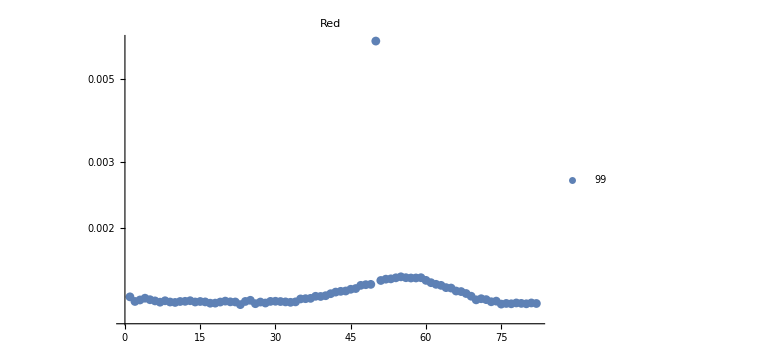
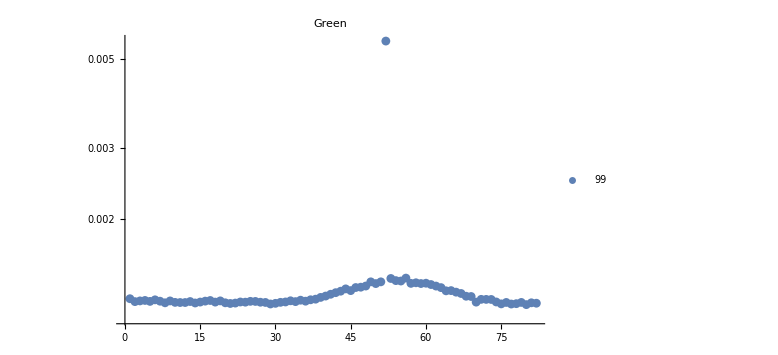
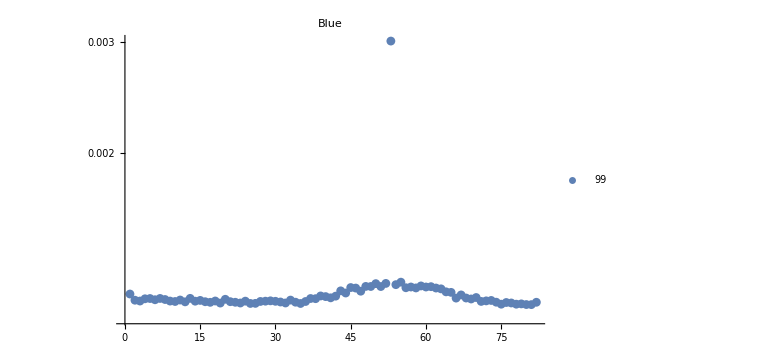

{orderedDarkMetrics,{{23,75,77,80,26,82,76,79,17,18,28,78,81,10,33,7,19,27,9,14,22,16,32,34,21,73,31,11,15,2,24,29,12,30,74,20,6,8,13,25,3,70,5,72,35,71,36,37,4,1,39,38,69,40,41,68,42,67,43,66,44,45,46,65,64,63,47,48,49,62,61,51,60,52,53,57,58,54,56,59,55,50},{80,77,29,75,78,21,30,82,22,14,8,20,81,12,11,76,28,79,10,31,27,24,70,18,15,23,32,74,2,34,13,26,5,25,7,36,16,9,3,19,33,17,4,35,6,37,73,72,71,38,1,39,69,68,40,41,67,42,66,43,64,65,45,44,63,46,47,62,48,61,50,59,57,60,58,51,49,55,54,53,56,52},{81,80,75,78,79,35,25,26,19,23,77,32,76,17,22,82,74,34,31,12,16,21,10,36,27,71,30,14,28,24,9,3,18,72,29,73,15,2,33,11,6,8,20,69,4,38,37,5,7,13,66,68,41,70,40,42,39,67,1,44,65,64,47,43,63,46,62,58,56,45,57,60,61,51,49,48,59,54,50,52,55,53}}}

{darkSegsCountOrig,49,darkSegsCount,49}

darkestSegmentIndicies = {{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,70,71,72,73,74,75,76,77,78,79,80,81,82},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,70,71,72,73,74,75,76,77,78,79,80,81,82},{2,3,4,5,6,7,8,9,10,11,12,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,69,71,72,73,74,75,76,77,78,79,80,81,82}}

flatTotals = {47.9772,46.8506,45.3957}

fnBaseName = JNCE_2016130_00C00171_V01.IMG.gz

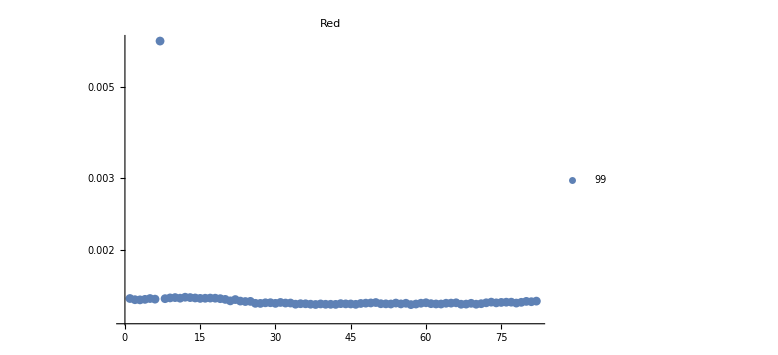
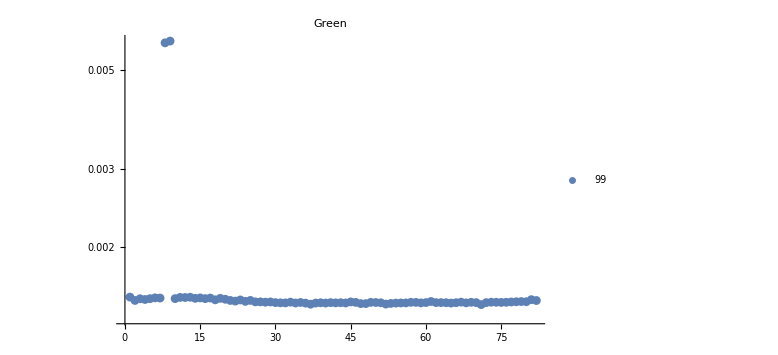
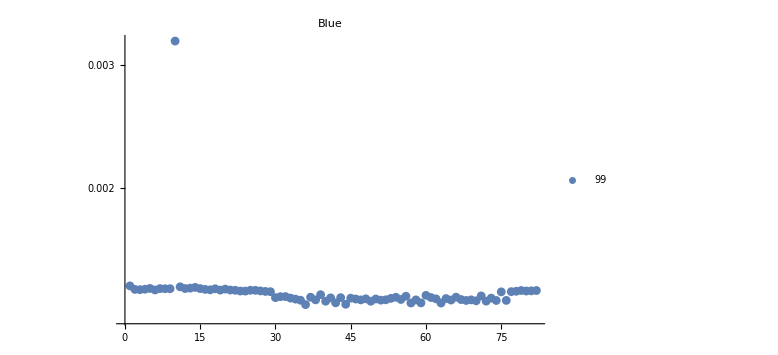

{orderedDarkMetrics,{{57,38,42,46,41,40,67,70,34,37,68,58,63,53,45,62,39,55,44,52,36,51,35,71,61,43,47,27,30,26,69,56,64,59,48,65,78,54,32,33,49,74,28,66,72,60,29,50,31,75,79,76,77,73,81,24,25,80,82,23,21,3,2,22,20,4,6,19,8,5,1,15,16,18,11,17,14,9,13,10,12,7},{71,37,52,47,48,53,36,54,40,38,65,34,44,55,56,32,68,59,42,31,51,39,64,43,66,72,30,70,62,41,63,60,50,35,75,58,46,49,57,69,76,74,73,28,33,67,77,29,45,26,27,78,80,79,61,24,22,82,21,2,25,23,18,81,4,20,3,5,16,10,19,14,17,7,15,6,12,11,13,1,8,9},{36,44,63,57,59,42,40,49,72,70,68,74,76,35,51,65,47,58,69,38,52,67,55,34,46,50,62,48,64,53,45,73,33,41,43,30,61,54,37,66,31,32,56,71,60,39,75,29,77,28,78,24,23,80,27,81,82,79,26,22,25,19,21,6,17,3,16,2,4,20,18,8,9,7,15,12,5,13,14,11,1,10}}}

{darkSegsCountOrig,49,darkSegsCount,49}

darkestSegmentIndicies = {{26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,74,78},{28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77},{29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77}}

flatTotals = {64.8268,63.2498,61.4898}

fnBaseName = JNCE_2016131_00C00180_V01.IMG.gz

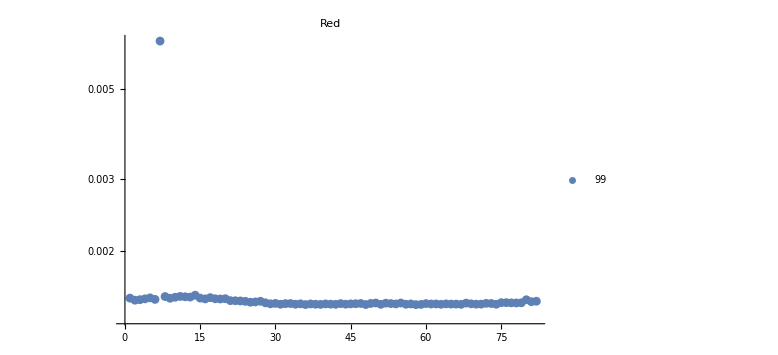
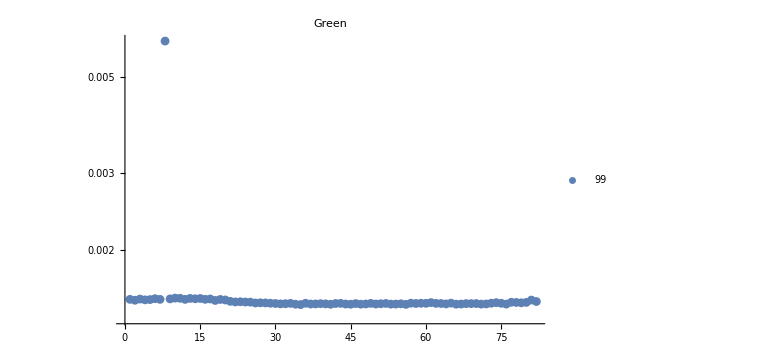
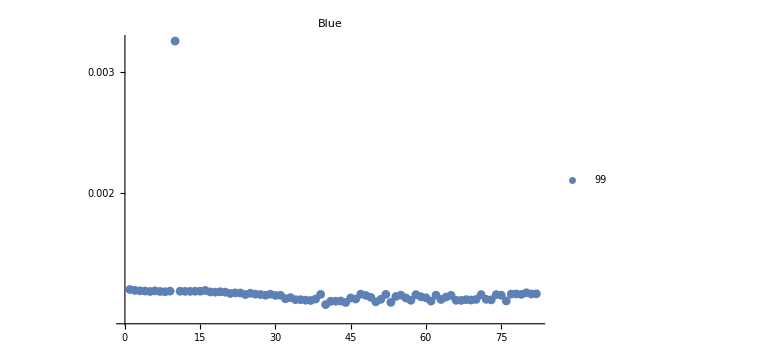

{orderedDarkMetrics,{{58,36,48,59,39,67,51,42,63,56,31,74,38,34,44,70,41,71,66,65,61,62,57,54,40,37,64,45,35,29,69,46,32,43,53,60,33,73,47,49,30,72,52,68,55,50,78,77,28,79,75,76,25,26,81,24,27,82,23,22,21,2,80,3,6,19,16,4,18,20,9,15,1,5,17,10,13,12,8,11,14,7},{35,56,41,45,34,66,47,53,71,76,54,44,67,37,50,48,72,38,64,31,40,55,51,32,39,69,68,46,70,58,30,42,63,52,49,62,43,33,60,75,36,59,29,73,57,65,26,28,27,79,74,61,78,80,77,25,24,22,23,82,21,18,2,81,20,4,5,19,12,1,7,16,3,17,9,14,6,15,13,11,10,8},{40,44,53,50,41,42,61,43,76,37,67,57,66,36,69,73,35,68,34,63,70,72,51,38,46,32,45,56,60,33,49,64,59,54,30,65,48,28,31,62,75,55,74,71,58,24,27,52,79,39,29,26,47,77,78,81,82,21,25,23,22,80,18,20,17,19,8,5,7,13,12,11,15,14,9,4,6,3,16,2,1,10}}}

{darkSegsCountOrig,49,darkSegsCount,49}

darkestSegmentIndicies = {{28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,77,78},{26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,62,63,64,65,66,67,68,69,70,71,72,73,75,76},{24,27,28,30,31,32,33,34,35,36,37,38,40,41,42,43,44,45,46,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,79}}

flatTotals = {65.8796,64.5555,62.7896}

fnBaseName = JNCE_2016164_00C00195_V01.IMG.gz

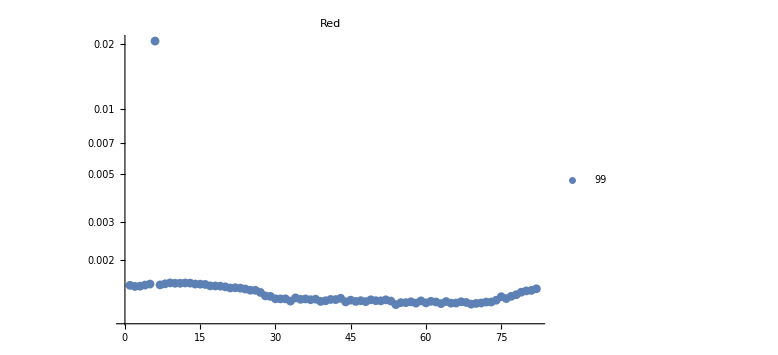
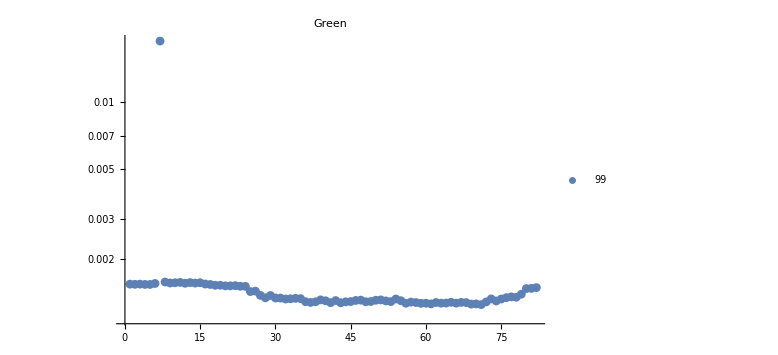
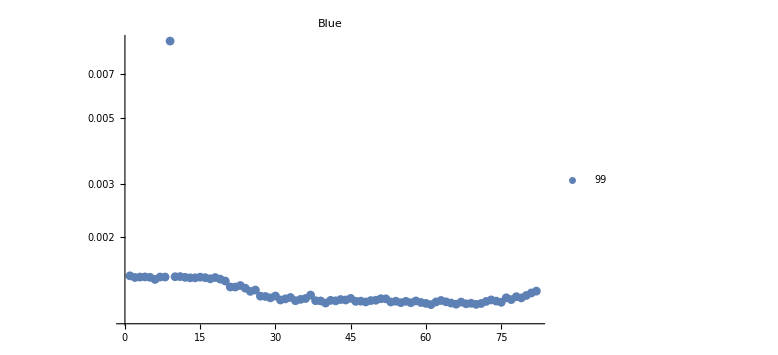

{orderedDarkMetrics,{{54,69,63,70,65,58,66,71,60,55,56,68,72,73,62,44,57,67,48,64,46,39,61,33,53,59,51,40,50,47,74,45,52,49,37,42,41,35,38,36,31,32,30,76,43,34,75,29,77,28,78,27,79,80,81,26,25,24,82,23,21,22,20,2,3,19,18,17,1,4,7,16,15,5,14,8,11,10,13,12,9,6},{71,69,70,61,59,56,60,63,66,64,43,41,68,62,58,37,67,65,57,72,44,48,38,36,53,45,49,74,52,40,55,42,46,50,47,51,39,75,54,32,73,33,35,34,31,30,28,76,78,77,29,27,79,25,26,80,81,82,24,23,21,20,22,19,18,17,5,4,2,1,3,16,6,12,14,9,10,15,13,11,8,7},{61,70,66,68,71,60,69,65,40,57,55,59,75,67,53,48,62,64,72,46,56,54,47,74,58,39,42,34,38,49,63,41,50,44,31,73,77,43,35,32,52,51,36,45,79,29,76,33,78,28,27,30,80,37,81,25,82,26,24,22,21,23,20,6,19,17,14,13,16,18,2,12,5,15,3,8,7,4,10,11,1,9}}}

{darkSegsCountOrig,49,darkSegsCount,49}

darkestSegmentIndicies = {{29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77},{28,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,78},{29,31,32,33,34,35,36,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79}}

flatTotals = {90.7344,89.1846,87.7898}

fnBaseName = JNCE_2016026_00C00058_V01.IMG.gz

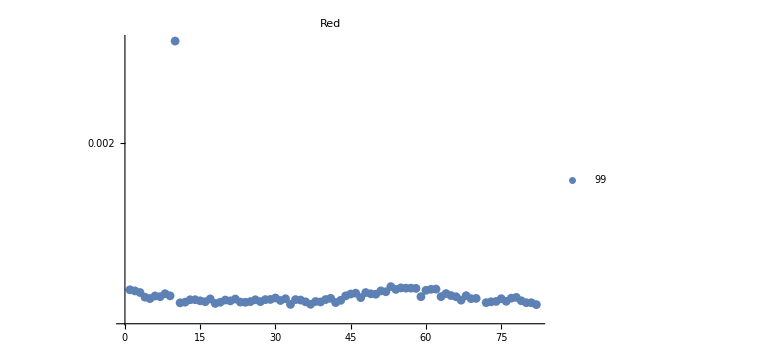
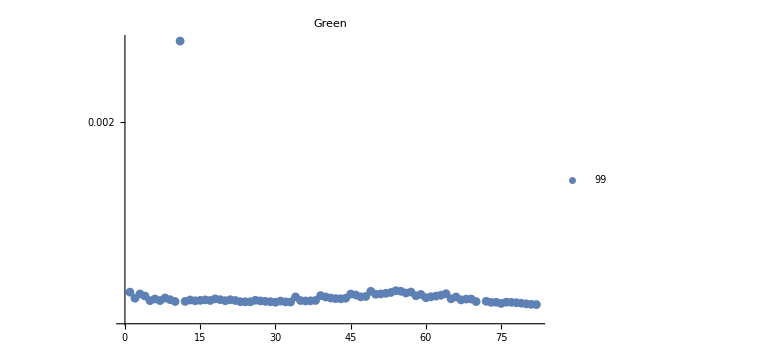
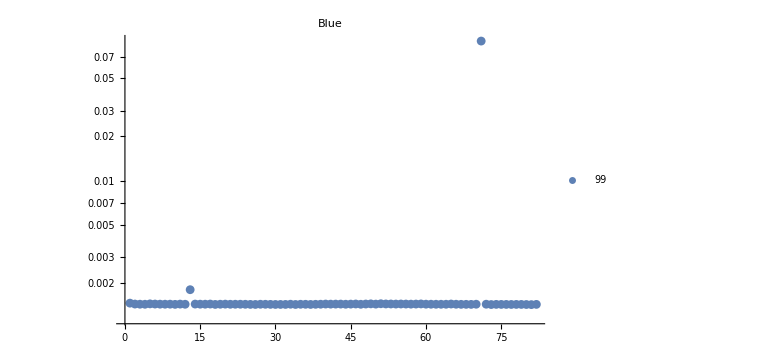

{orderedDarkMetrics,{{71,82,33,37,18,11,81,80,72,42,24,19,12,23,39,36,73,16,25,27,38,74,76,21,15,79,31,43,67,20,35,26,13,14,34,28,40,29,22,17,32,75,69,5,70,41,77,30,47,78,4,66,7,59,63,6,44,9,68,65,50,45,49,8,64,46,48,3,52,51,2,60,1,54,61,62,58,57,56,55,53,10},{71,82,81,80,75,79,78,73,77,74,30,76,33,32,25,24,29,23,70,10,12,28,72,31,36,27,37,14,20,5,7,22,35,17,38,15,26,13,67,16,21,19,9,68,69,6,18,43,65,42,2,44,8,41,60,40,66,34,47,61,48,62,4,58,39,63,46,59,50,45,3,51,64,52,56,53,1,57,49,55,54,11},{81,73,80,34,77,30,26,31,37,32,79,76,18,78,75,25,69,82,74,29,10,68,67,38,36,28,24,47,21,35,63,12,4,62,64,27,22,66,23,44,19,39,33,70,61,72,3,8,16,15,60,9,7,57,41,20,45,50,11,42,43,14,58,54,2,17,6,56,40,48,65,55,46,53,52,59,5,49,51,1,13,71}}}

{darkSegsCountOrig,49,darkSegsCount,49}

darkestSegmentIndicies = {{5,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,47,67,69,70,71,72,73,74,75,76,77,79,80,81,82},{5,6,7,9,10,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,35,36,37,38,43,65,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82},{3,4,8,10,12,16,18,19,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,44,47,61,62,63,64,66,67,68,69,70,72,73,74,75,76,77,78,79,80,81,82}}

flatTotals = {91.5305,90.1486,90.9319}

fnBaseName = JNCE_2016026_00C00059_V01.IMG.gz

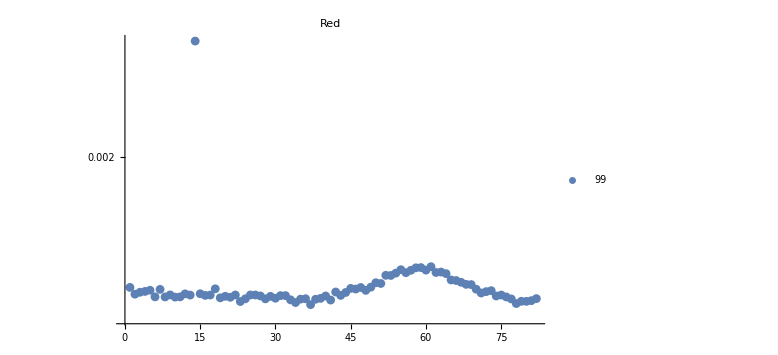
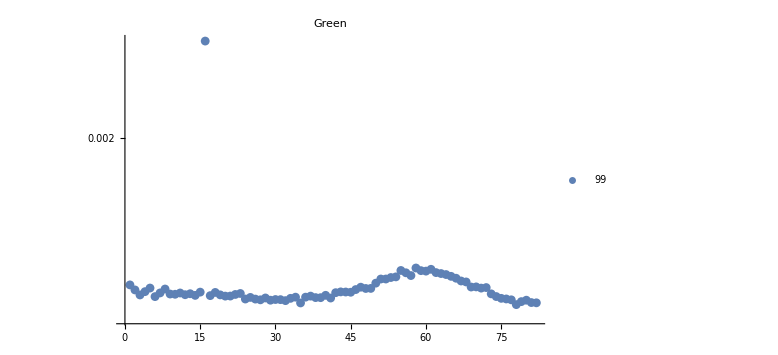
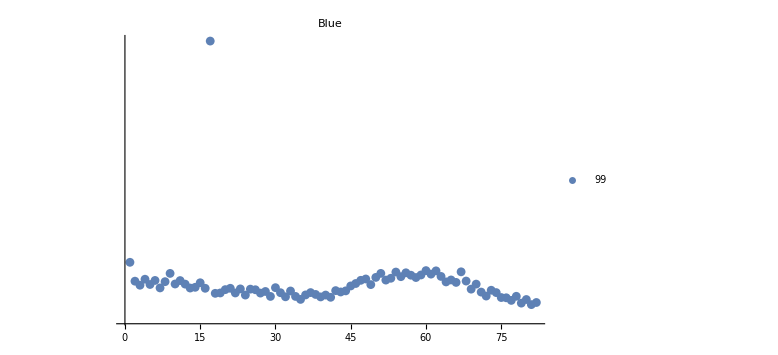

{orderedDarkMetrics,{{37,78,34,23,80,79,81,41,33,38,35,77,28,24,36,82,39,30,19,21,10,8,76,6,11,29,20,74,40,27,31,32,43,16,13,17,75,26,25,22,9,2,12,15,71,44,3,42,72,4,73,48,5,7,70,46,18,45,47,1,49,69,68,51,50,67,66,65,53,52,64,54,56,62,63,57,60,55,58,59,61,14},{78,35,82,81,79,32,29,80,27,77,31,30,26,24,76,33,75,41,28,39,38,25,36,34,6,74,20,37,21,17,14,40,3,19,12,22,10,9,73,13,23,11,7,42,18,45,15,44,43,4,2,46,8,48,49,71,5,72,47,69,70,1,50,68,67,52,51,66,53,54,65,57,64,63,56,62,60,59,55,61,58,16},{81,79,82,77,80,35,76,75,41,39,32,34,29,78,72,40,24,36,38,18,27,22,19,31,37,74,71,43,28,33,44,42,73,26,20,25,69,23,16,21,13,7,30,14,45,3,49,5,70,12,10,46,15,66,64,8,2,68,11,6,47,52,65,4,48,53,58,50,55,63,57,59,61,51,9,56,54,67,62,60,1,17}}}

{darkSegsCountOrig,49,darkSegsCount,49}

darkestSegmentIndicies = {{2,3,6,8,9,10,11,12,13,15,16,17,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,71,72,74,75,76,77,78,79,80,81,82},{3,6,7,9,10,11,12,13,14,15,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,73,74,75,76,77,78,79,80,81,82},{3,5,7,13,14,16,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,49,69,70,71,72,73,74,75,76,77,78,79,80,81,82}}

flatTotals = {90.6747,89.1686,87.7865}

fnBaseName = JNCE_2016026_00C00060_V01.IMG.gz

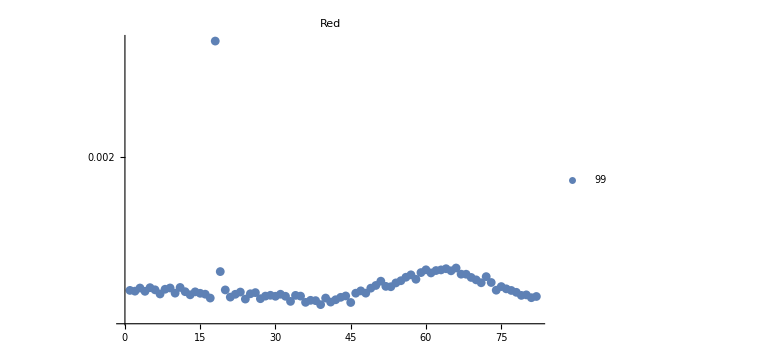
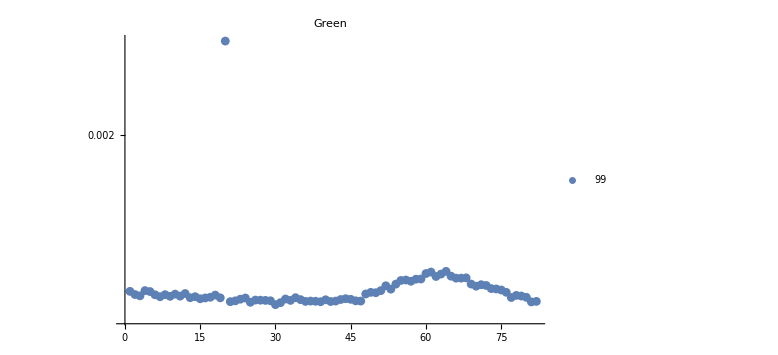
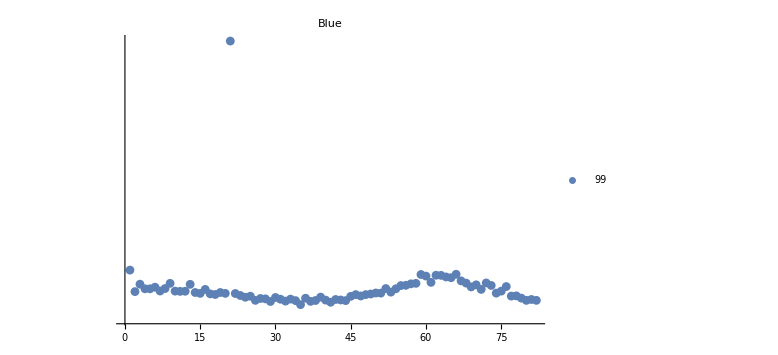

{orderedDarkMetrics,{{39,45,36,41,33,38,37,42,24,27,40,17,81,43,21,82,30,32,28,35,44,34,79,29,80,13,22,31,16,7,25,15,46,10,48,26,78,23,14,12,4,2,47,77,1,74,20,6,8,76,49,3,9,5,11,53,75,52,50,54,71,73,51,55,70,58,69,56,72,57,68,67,61,59,19,65,62,63,60,64,66,18},{30,31,25,81,39,21,41,36,82,38,42,37,47,22,46,29,28,33,27,26,40,35,43,45,23,32,15,44,24,16,19,13,34,77,80,17,7,14,9,11,79,3,78,18,6,8,2,10,48,12,50,49,76,5,1,4,51,75,53,74,73,70,52,72,71,54,69,57,55,56,58,59,67,66,68,62,65,63,60,61,64,20},{35,41,29,37,32,34,44,38,26,80,82,40,43,42,81,31,33,28,27,36,79,30,24,39,45,25,77,47,78,23,46,48,18,49,17,22,15,20,51,74,50,19,14,53,2,11,12,75,10,7,71,16,4,54,5,8,52,6,69,76,55,73,56,70,13,3,57,58,9,68,72,61,67,65,64,60,63,62,59,66,1,21}}}

{darkSegsCountOrig,49,darkSegsCount,49}

darkestSegmentIndicies = {{1,2,4,6,7,8,10,12,13,14,15,16,17,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,74,77,78,79,80,81,82},{2,3,6,7,8,9,10,11,13,14,15,16,17,18,19,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,77,78,79,80,81,82},{2,10,11,12,14,15,17,18,19,20,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,53,74,75,77,78,79,80,81,82}}

flatTotals = {87.372,85.8732,84.3669}

fnBaseName = JNCE_2016026_00C00061_V01.IMG.gz

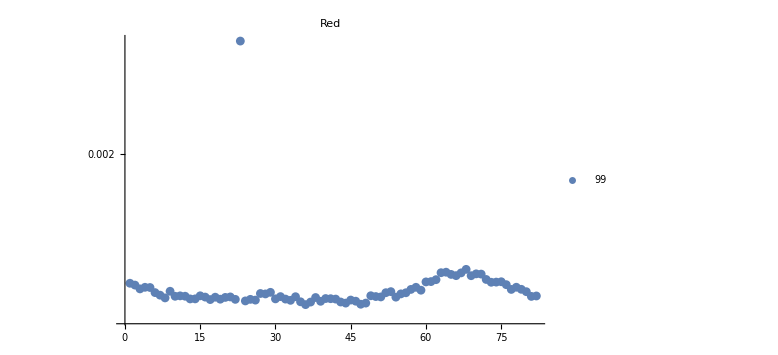
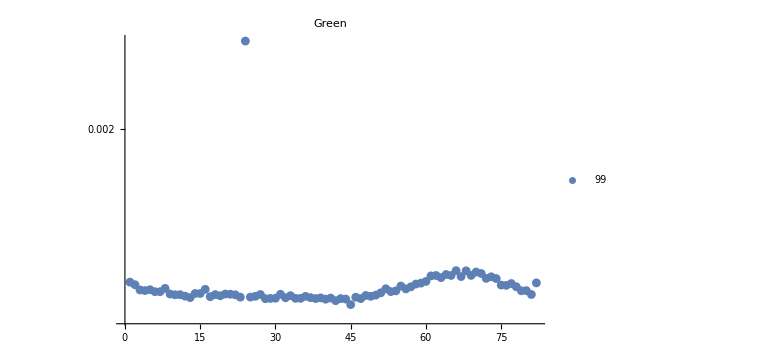
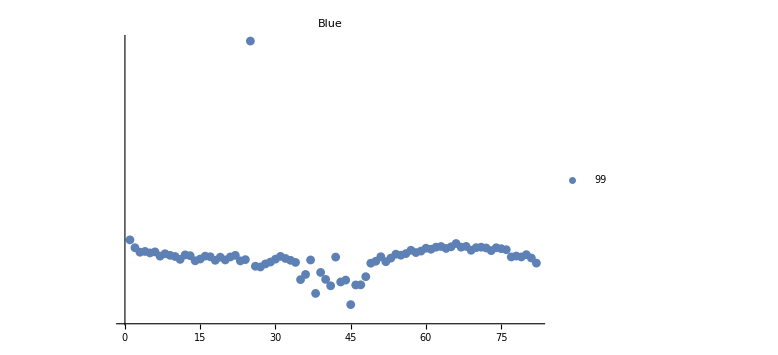

{orderedDarkMetrics,{{36,47,48,44,37,43,35,39,46,24,33,26,45,17,25,22,19,42,32,13,30,14,41,40,8,38,20,18,54,16,51,21,34,31,50,81,10,12,82,11,15,49,7,28,55,27,56,52,6,29,80,53,9,59,57,77,79,3,5,4,58,78,2,76,1,73,74,60,75,61,62,72,69,66,65,71,70,67,63,64,68,23},{45,42,40,44,28,47,43,38,29,35,34,30,41,39,32,37,13,46,23,25,17,36,49,26,12,19,33,48,50,22,10,11,18,81,27,31,21,9,20,14,15,51,7,6,53,54,79,80,4,3,5,16,56,52,8,57,78,55,76,75,2,58,77,59,82,1,60,74,72,63,73,67,61,62,65,69,64,71,70,68,66,24},{45,38,41,46,47,43,44,35,40,48,36,39,27,26,28,49,82,34,29,52,50,23,14,33,18,20,37,24,11,30,15,32,53,81,19,42,77,21,79,17,51,10,31,7,16,78,13,22,9,55,12,80,54,8,56,5,58,3,6,4,59,73,57,69,76,61,75,64,60,72,2,74,70,62,71,67,65,63,68,66,1,25}}}

{darkSegsCountOrig,49,darkSegsCount,49}

darkestSegmentIndicies = {{6,7,8,10,11,12,13,14,15,16,17,18,19,20,21,22,24,25,26,27,28,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,54,55,56,81,82},{4,6,7,9,10,11,12,13,14,15,17,18,19,20,21,22,23,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,53,54,79,80,81},{7,9,10,11,13,14,15,16,17,18,19,20,21,22,23,24,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,77,78,79,81,82}}

flatTotals = {84.3633,82.9906,81.5292}

fnBaseName = JNCE_2016026_00C00062_V01.IMG.gz

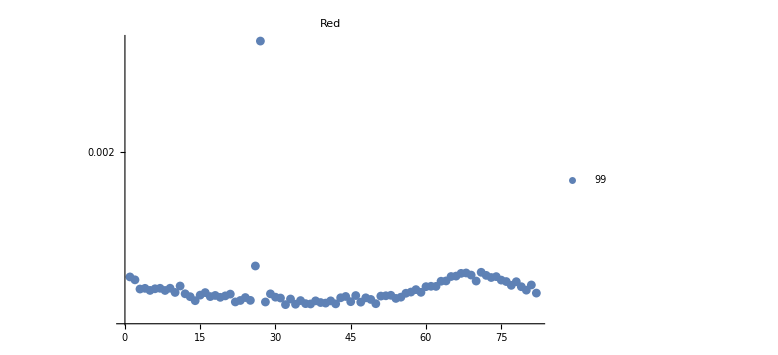
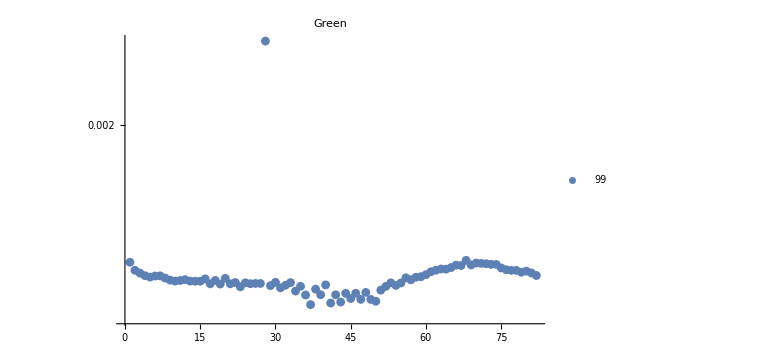
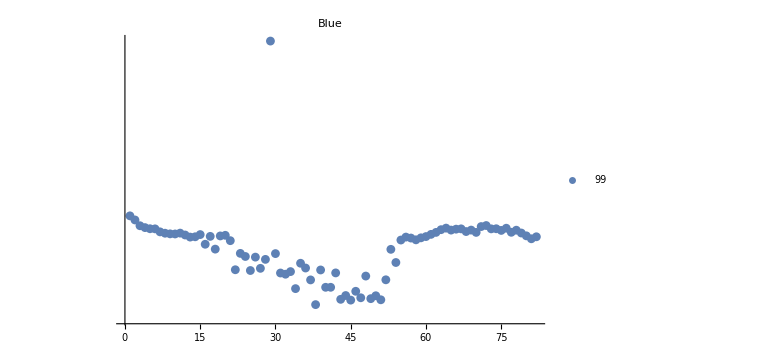

{orderedDarkMetrics,{{32,34,37,42,50,36,40,39,47,28,22,45,38,41,14,35,23,25,49,33,54,31,48,43,24,19,30,55,13,17,44,51,20,52,46,18,53,15,21,29,12,56,82,16,10,59,57,8,5,80,58,3,6,4,7,9,79,60,62,61,11,77,81,78,76,63,70,64,75,2,73,1,74,65,66,72,69,67,68,71,26,27},{37,41,43,50,49,47,45,36,42,39,44,46,48,34,51,38,31,23,52,35,29,54,32,40,19,17,21,25,27,26,55,24,53,33,22,30,14,15,13,10,11,18,9,57,12,16,20,8,56,58,5,59,6,7,4,82,60,3,81,79,61,80,78,77,2,62,76,64,63,75,65,67,66,69,74,73,72,71,70,1,68,28},{38,45,51,43,49,47,50,44,46,34,40,41,37,52,48,32,31,42,33,25,39,22,27,36,35,54,28,26,24,30,23,53,18,16,21,55,58,81,57,59,13,56,14,82,60,17,19,80,20,12,15,61,10,9,8,11,79,70,62,77,7,68,75,78,65,69,63,66,73,67,6,74,5,76,64,4,71,3,72,2,1,29}}}

{darkSegsCountOrig,49,darkSegsCount,49}

darkestSegmentIndicies = {{5,8,10,12,13,14,15,16,17,18,19,20,21,22,23,24,25,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,59,82},{8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57},{13,14,16,17,18,19,20,21,22,23,24,25,26,27,28,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,80,81,82}}

flatTotals = {82.256,80.6697,79.352}

fnBaseName = JNCE_2016026_00C00063_V01.IMG.gz

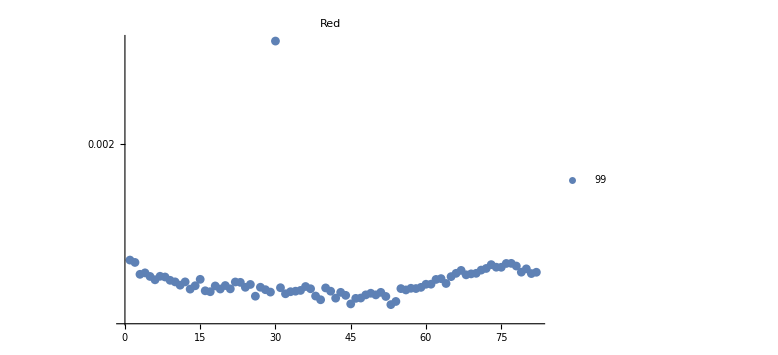
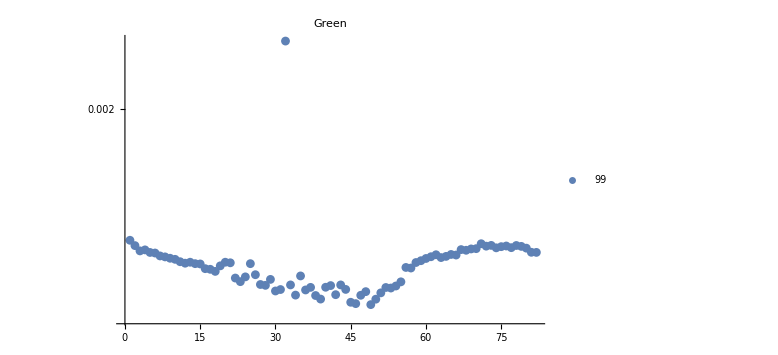
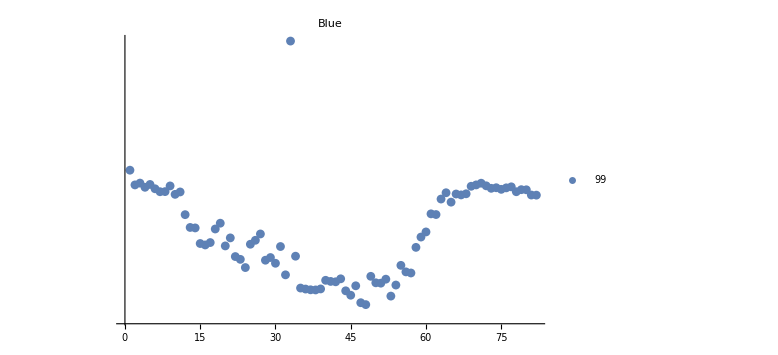

{orderedDarkMetrics,{{53,45,54,39,46,42,47,52,26,38,44,48,50,32,49,51,43,29,17,33,41,34,16,35,56,28,13,19,21,37,55,58,57,40,31,59,24,27,36,18,14,20,11,25,60,61,64,23,22,12,10,9,6,62,15,63,8,65,5,7,68,3,69,81,66,70,4,82,79,67,71,80,72,75,74,78,73,76,77,2,1,30},{49,46,45,50,39,38,47,34,42,51,48,30,36,31,44,53,52,37,40,54,41,28,33,43,27,55,23,29,22,24,35,26,18,17,16,57,56,19,15,25,14,12,21,58,20,13,11,59,10,60,9,63,8,61,64,7,66,62,65,6,5,82,81,3,68,4,67,69,70,80,74,77,75,79,72,76,2,78,73,71,1,32},{48,47,53,45,44,38,37,36,39,35,46,54,51,50,42,41,40,52,43,49,32,57,56,24,55,30,28,23,29,22,34,58,31,20,16,25,15,17,26,21,59,27,60,18,14,13,19,12,62,61,65,63,82,81,67,10,66,68,64,11,7,78,8,80,79,75,6,73,76,74,4,77,69,9,72,2,70,5,71,3,1,33}}}

{darkSegsCountOrig,49,darkSegsCount,49}

darkestSegmentIndicies = {{11,13,14,16,17,18,19,20,21,22,23,24,25,26,27,28,29,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,64},{10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59},{12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,62}}

flatTotals = {79.7118,78.3059,77.0075}

fnBaseName = JNCE_2016026_00C00070_V01.IMG.gz

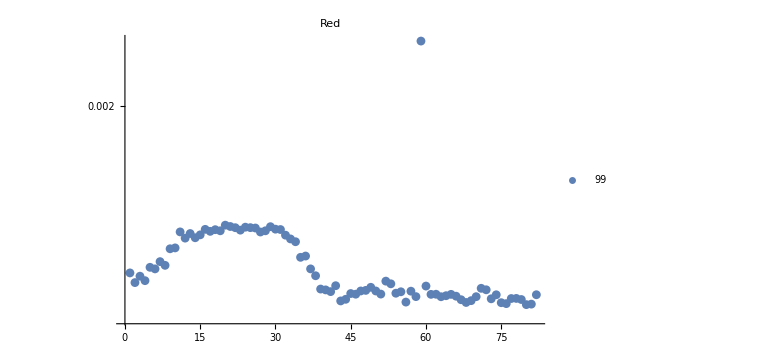
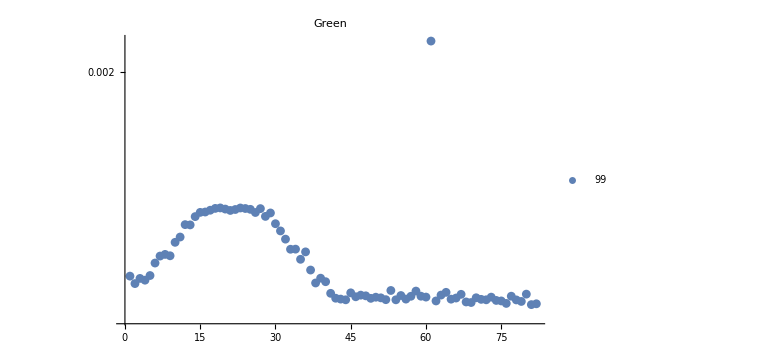
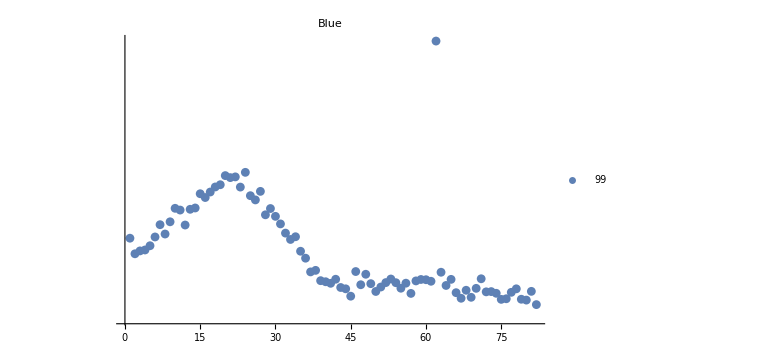

{orderedDarkMetrics,{{80,81,76,75,68,56,43,69,67,79,44,73,77,78,63,70,58,66,64,74,82,65,61,62,46,51,45,54,55,41,57,47,50,48,40,72,39,71,49,60,42,53,2,52,4,3,38,1,6,37,5,8,7,35,36,9,10,34,33,12,14,32,15,13,27,11,17,28,19,23,18,31,16,30,26,22,25,24,29,21,20,59},{81,82,76,69,68,79,75,62,74,78,72,54,44,52,71,65,56,43,49,42,66,51,70,50,73,60,46,57,59,77,48,55,47,63,67,80,41,45,64,58,53,2,38,40,4,3,39,1,5,37,6,35,7,9,8,36,33,34,10,32,11,31,13,12,30,14,28,29,26,15,16,21,17,22,25,20,27,24,18,23,19,61},{82,80,75,79,76,67,69,45,57,74,66,77,72,73,50,81,68,44,78,70,55,43,51,64,47,49,41,56,54,52,40,61,58,39,60,59,65,42,53,71,48,63,37,46,38,36,2,35,3,4,5,33,1,6,34,8,32,12,7,31,9,30,28,11,13,29,10,14,26,16,25,15,17,27,23,18,19,21,22,20,24,62}}}

{darkSegsCountOrig,49,darkSegsCount,49}

darkestSegmentIndicies = {{1,2,3,4,6,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82},{1,2,3,4,5,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82},{2,3,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82}}

flatTotals = {71.3593,70.2217,69.1854}

fnBaseName = JNCE_2016026_00C00071_V01.IMG.gz

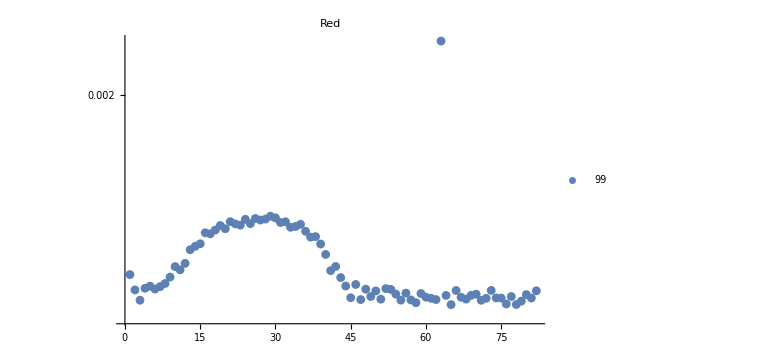
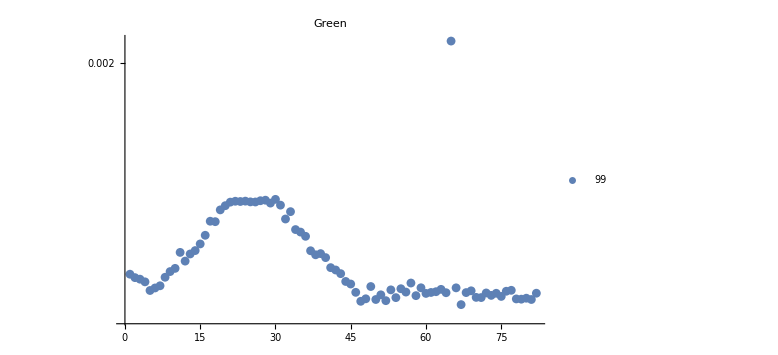
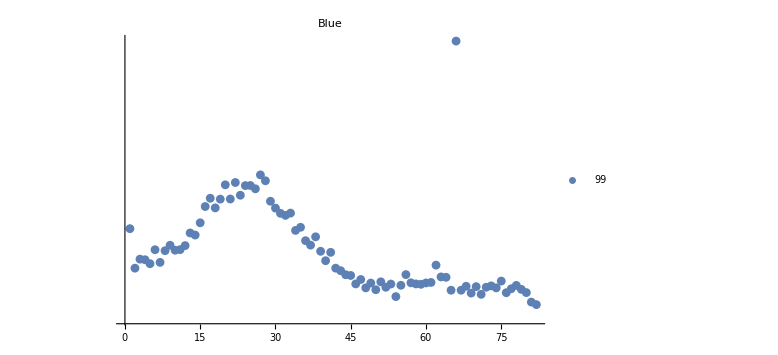

{orderedDarkMetrics,{{65,78,76,58,79,71,3,55,57,47,62,51,68,72,61,75,81,74,45,67,60,77,49,64,69,80,70,54,59,56,50,82,66,73,2,53,48,6,52,4,7,5,44,46,8,43,9,1,41,11,10,42,12,40,13,14,39,15,37,38,17,16,36,18,20,33,34,19,23,35,22,25,31,32,21,27,24,28,26,30,29,63},{67,47,52,50,81,79,78,48,80,54,71,70,75,58,73,51,60,74,82,72,64,68,61,46,56,62,76,69,5,77,53,63,55,6,66,59,49,7,45,57,4,44,3,2,8,1,43,9,42,10,41,12,40,38,13,39,11,37,14,15,36,16,35,34,18,17,32,33,19,20,31,29,21,26,25,23,22,24,27,28,30,65},{82,81,54,71,69,76,80,65,67,50,79,77,48,74,72,52,70,68,73,78,55,59,53,46,58,49,60,57,61,51,75,47,64,63,45,44,56,43,2,42,62,5,7,40,4,3,41,39,8,10,6,11,12,9,37,36,38,14,13,34,1,35,15,32,31,33,30,18,16,29,19,21,17,23,26,24,25,20,22,28,27,66}}}

{darkSegsCountOrig,49,darkSegsCount,49}

darkestSegmentIndicies = {{1,2,3,4,5,6,7,8,9,41,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82},{1,2,3,4,5,6,7,8,9,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82},{2,3,4,5,7,8,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82}}

flatTotals = {70.666,69.6538,68.6794}

fnBaseName = JNCE_2016026_00C00072_V01.IMG.gz

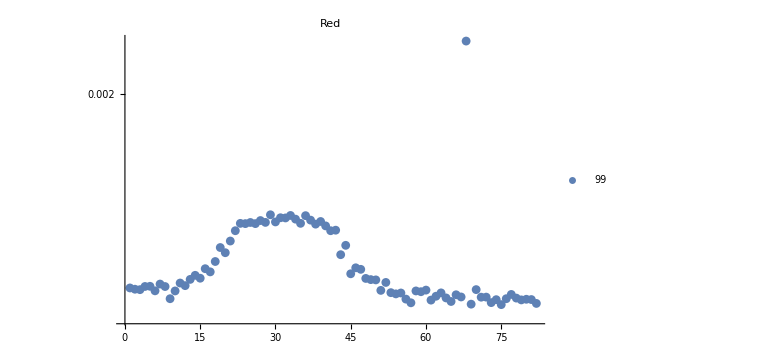
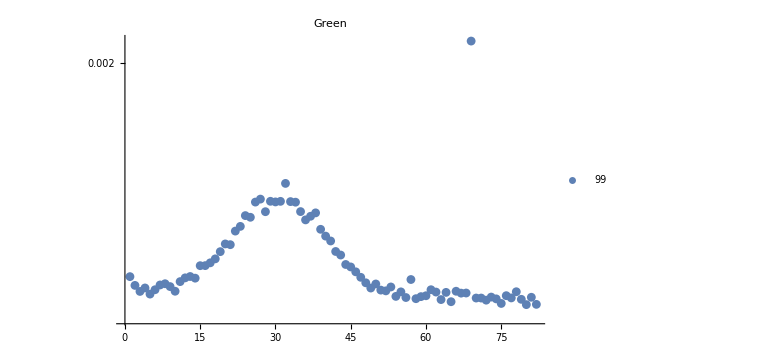
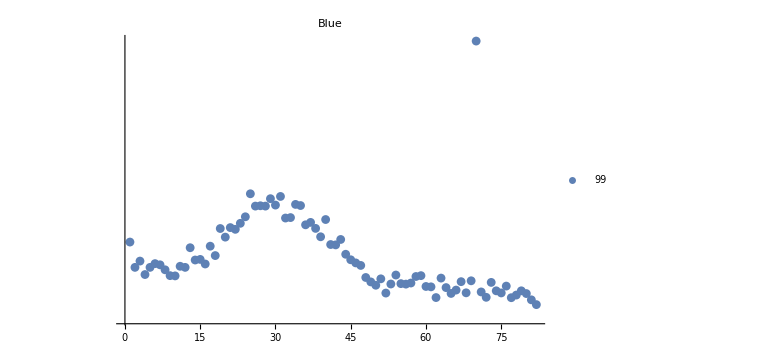

{orderedDarkMetrics,{{75,69,82,57,73,65,61,79,74,81,80,56,9,76,78,64,71,72,67,62,66,77,54,55,63,53,59,10,58,6,51,60,3,70,2,1,8,4,5,12,7,11,52,50,49,13,48,15,14,45,17,47,16,46,18,43,20,19,44,21,22,41,42,40,38,26,24,23,35,25,28,30,39,27,37,34,32,31,36,33,29,68},{80,82,75,65,72,63,79,74,58,71,70,77,56,81,73,59,54,60,76,5,67,68,64,62,55,78,3,10,66,52,51,6,61,49,4,53,9,2,7,50,8,48,11,57,14,12,47,1,13,46,45,15,16,44,17,18,43,19,42,21,20,41,40,22,39,23,36,25,37,24,38,28,35,34,26,30,33,31,29,27,32,69},{82,81,77,62,72,78,80,65,52,75,68,71,79,74,66,64,61,60,76,50,56,53,55,57,73,49,67,69,51,63,48,58,10,59,9,54,4,8,12,2,5,11,47,7,16,6,46,3,14,45,15,18,44,13,17,42,41,1,43,20,39,22,19,38,21,36,23,37,40,32,33,24,28,26,27,35,30,34,29,31,25,70}}}

{darkSegsCountOrig,49,darkSegsCount,49}

darkestSegmentIndicies = {{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,69,70,71,72,73,74,75,76,77,78,79,80,81,82},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,70,71,72,73,74,75,76,77,78,79,80,81,82},{2,3,4,5,6,7,8,9,10,11,12,14,16,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,71,72,73,74,75,76,77,78,79,80,81,82}}

flatTotals = {70.2262,69.2754,68.3076}

fnBaseName = JNCE_2016026_00C00073_V01.IMG.gz

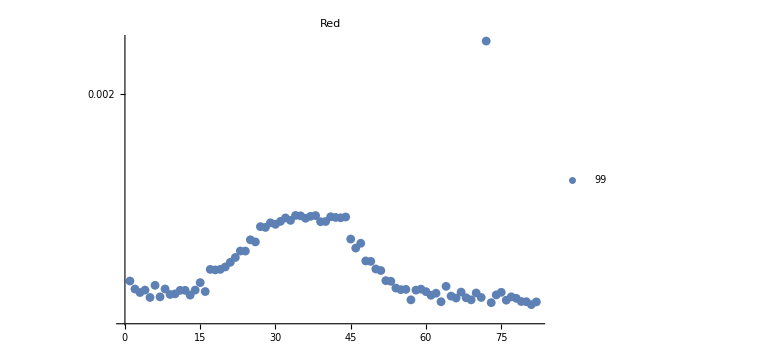
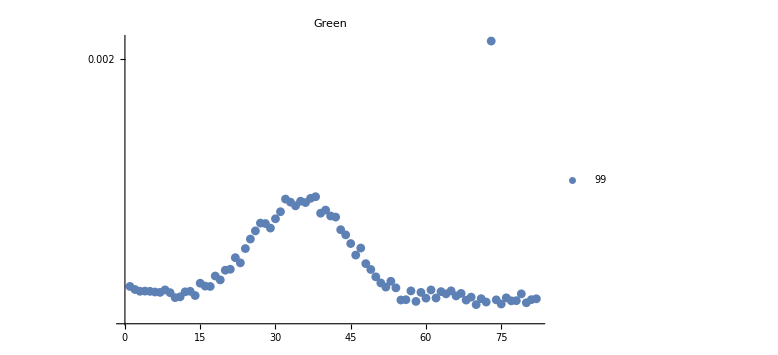
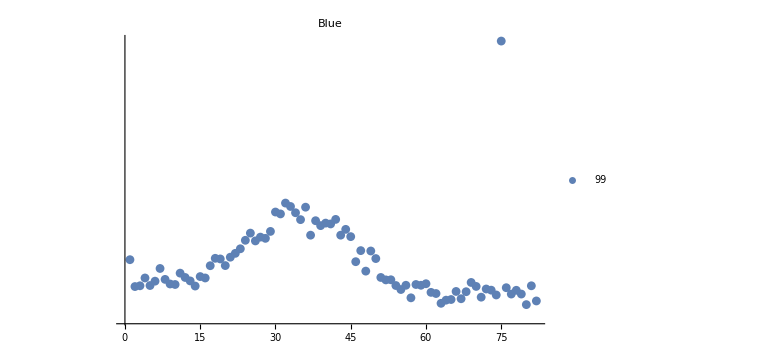

{orderedDarkMetrics,{{81,73,82,63,80,79,76,69,57,78,66,68,5,71,7,77,65,61,13,74,9,10,62,70,3,75,67,60,16,11,12,58,14,4,55,56,59,2,8,54,64,6,15,53,1,52,51,18,19,17,50,20,21,49,48,22,24,23,46,47,26,25,45,28,27,30,29,39,40,31,33,36,32,43,42,44,41,37,35,38,34,72},{70,75,80,72,58,77,78,68,55,74,56,81,82,71,60,62,76,10,69,11,66,14,79,64,67,9,59,7,6,12,63,5,3,13,4,57,65,61,8,2,54,52,17,1,16,15,51,53,19,50,18,20,49,21,48,23,22,46,24,47,45,25,44,26,43,29,28,27,30,42,41,39,31,40,34,36,33,35,32,37,38,73},{80,63,82,64,65,67,57,71,74,77,79,62,61,68,66,78,73,55,72,76,2,70,14,81,3,54,5,56,59,58,10,9,60,69,6,13,52,53,8,4,16,51,12,15,11,48,7,17,20,46,1,19,50,18,21,22,49,47,23,26,24,28,27,45,37,43,25,29,44,39,41,40,38,35,42,31,34,30,36,33,32,75}}}

{darkSegsCountOrig,49,darkSegsCount,49}

darkestSegmentIndicies = {{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,18,19,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,73,74,75,76,77,78,79,80,81,82},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,19,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,74,75,76,77,78,79,80,81,82},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,20,48,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,76,77,78,79,80,81,82}}

flatTotals = {69.5391,68.6994,67.8956}

fnBaseName = JNCE_2016026_00C00074_V01.IMG.gz

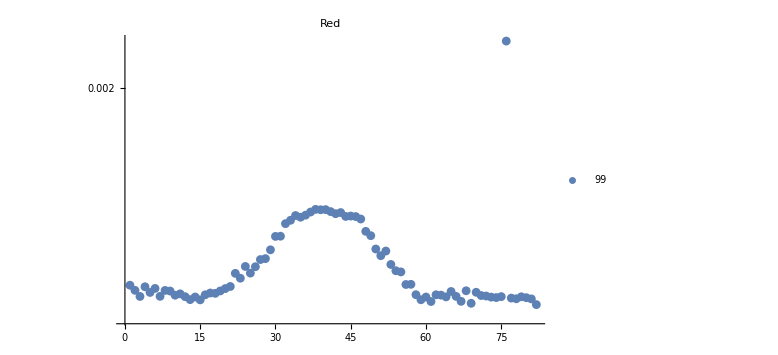
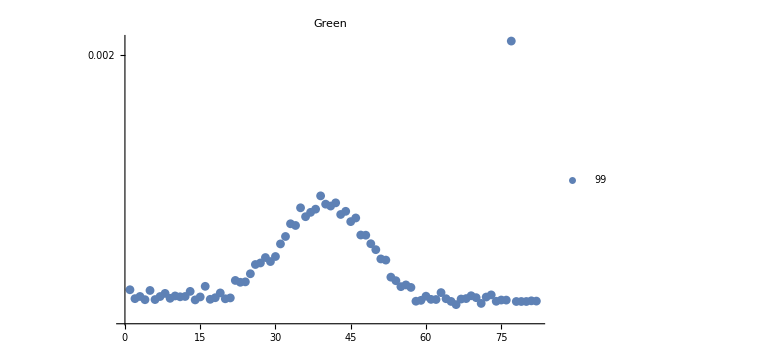
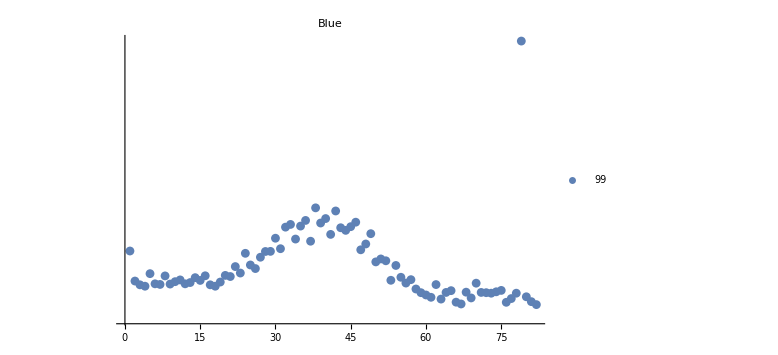

{orderedDarkMetrics,{{82,69,61,67,15,59,13,81,78,77,80,74,73,14,60,64,79,12,75,3,66,7,72,71,10,63,62,16,58,11,18,17,5,70,65,9,19,68,8,2,20,6,4,21,1,56,57,23,22,25,55,54,26,24,53,27,28,51,52,29,50,30,31,49,48,32,33,47,35,46,44,45,34,36,42,43,37,41,39,40,38,76},{66,71,79,80,78,65,74,58,82,81,59,76,75,14,4,6,62,61,17,67,20,64,2,68,9,21,18,70,72,15,11,7,3,12,60,10,69,73,8,19,63,13,5,1,57,55,16,56,23,24,54,22,53,25,26,27,29,52,51,28,30,50,31,49,32,48,47,34,33,45,46,36,43,37,44,38,35,41,40,42,39,77},{82,67,76,66,81,63,77,69,61,80,60,73,78,59,72,64,71,68,74,65,75,58,18,4,17,3,62,7,9,6,12,70,56,13,19,10,2,15,53,11,57,14,55,21,8,16,20,5,23,26,22,54,25,50,52,51,27,24,28,29,1,47,31,48,37,34,30,41,49,44,43,32,45,35,33,39,46,36,40,42,38,79}}}

{darkSegsCountOrig,49,darkSegsCount,49}

darkestSegmentIndicies = {{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,77,78,79,80,81,82},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,23,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,78,79,80,81,82},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,23,53,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,80,81,82}}

flatTotals = {68.9092,68.181,67.3758}

fnBaseName = JNCE_2016026_00C00080_V01.IMG.gz

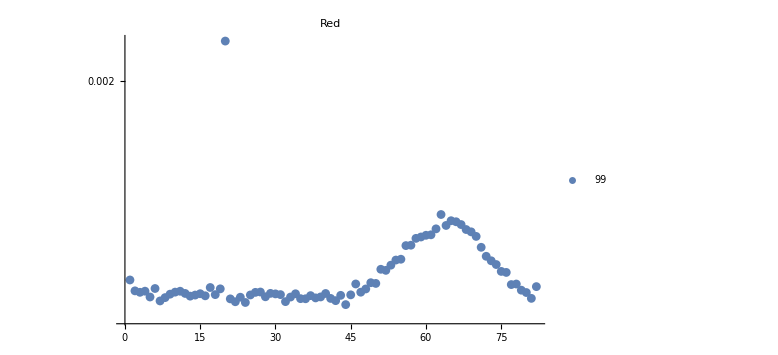
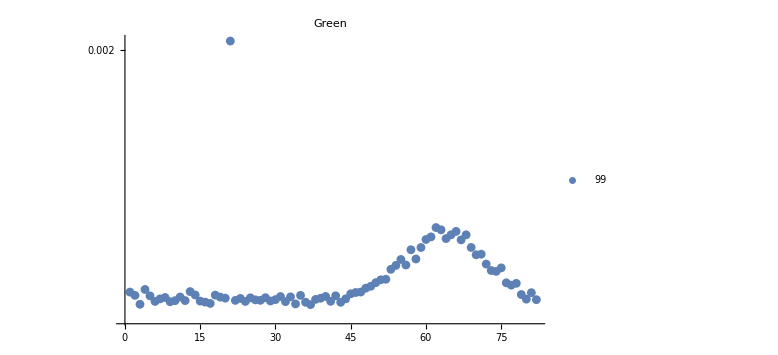
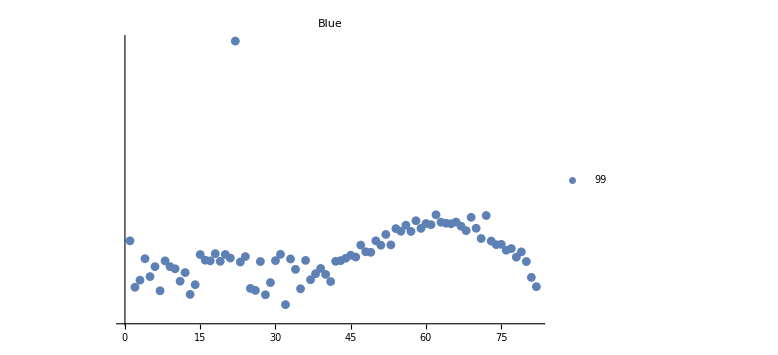

{orderedDarkMetrics,{{44,24,22,32,7,42,21,36,35,41,81,38,8,23,33,5,39,28,13,16,37,43,14,25,45,18,31,9,30,34,15,40,12,29,80,26,3,47,10,27,11,4,2,79,48,19,6,17,82,77,78,46,50,49,1,76,75,52,51,53,74,73,54,55,72,71,56,57,58,59,70,60,61,69,68,62,64,67,66,65,63,20},{37,3,34,17,43,36,16,9,32,6,24,41,15,29,10,12,22,27,26,82,30,38,80,7,44,23,39,20,25,28,8,19,11,33,31,40,5,42,35,2,18,14,79,45,81,46,1,47,13,4,48,49,77,78,76,50,51,52,74,73,53,75,54,56,72,55,58,70,71,57,59,69,67,60,64,61,68,65,66,63,62,21},{32,28,13,7,26,35,25,2,82,14,29,41,11,3,37,81,5,40,38,12,34,10,39,6,9,23,27,80,19,42,8,17,30,43,36,16,33,4,44,21,78,46,24,45,15,20,31,18,49,79,48,76,77,51,47,53,74,75,73,1,50,71,52,57,55,68,54,59,70,67,56,61,65,60,64,63,66,58,69,72,62,22}}}

{darkSegsCountOrig,49,darkSegsCount,49}

darkestSegmentIndicies = {{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,47,48,79,80,81,82},{1,2,3,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,79,80,81,82},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,49,78,80,81,82}}

flatTotals = {66.4413,65.9671,65.572}

fnBaseName = JNCE_2016026_00C00081_V01.IMG.gz

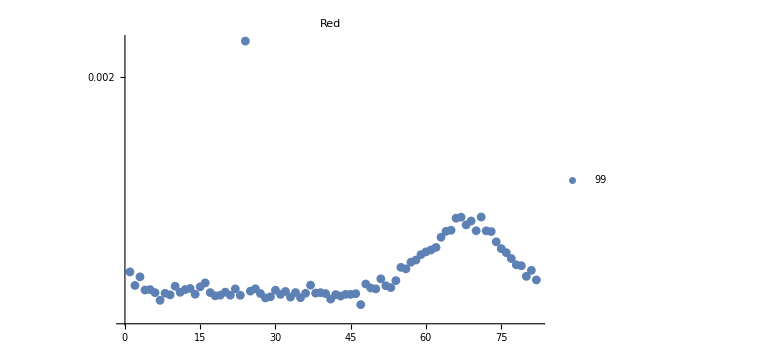
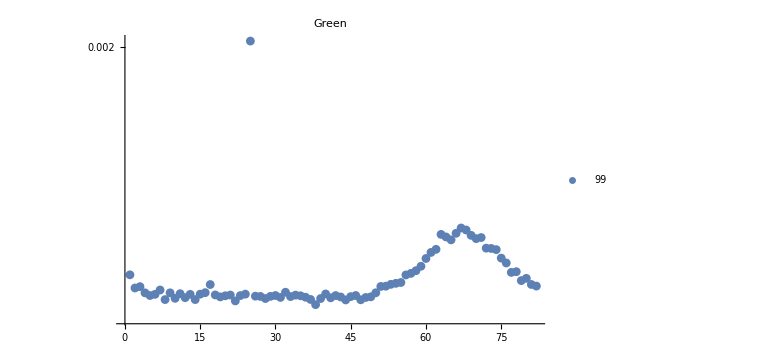
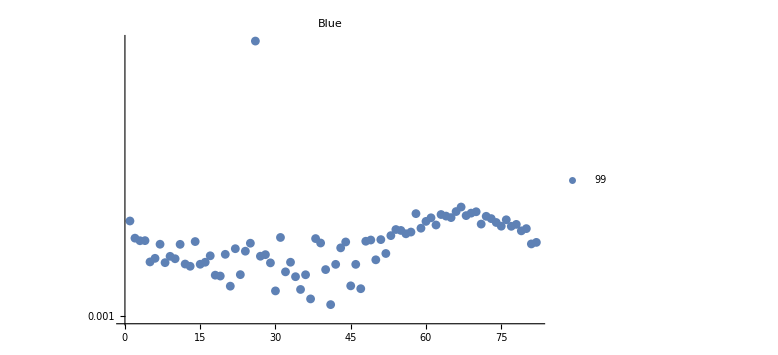

{orderedDarkMetrics,{{47,7,41,28,35,33,29,43,18,23,21,19,9,42,31,45,44,14,46,40,27,8,36,38,6,39,17,34,11,20,32,25,30,4,5,12,50,22,26,13,49,53,15,10,52,2,37,48,16,54,82,51,3,80,1,81,56,55,79,78,57,58,77,59,76,60,61,75,62,74,63,73,64,72,70,65,68,69,66,67,71,24},{38,22,44,47,14,8,37,39,28,10,41,12,48,31,36,43,19,49,45,33,27,29,26,35,20,42,23,46,30,5,34,21,18,6,13,24,15,40,11,4,9,50,16,32,7,2,3,51,52,82,17,81,53,54,55,79,80,56,1,57,77,78,58,59,76,60,75,61,74,62,73,72,65,70,71,64,69,63,66,68,67,25},{41,37,30,35,47,21,45,34,19,18,36,23,32,40,13,42,46,15,12,29,8,33,16,5,50,10,6,9,27,17,28,20,52,24,22,43,11,7,81,25,39,82,44,14,48,3,4,49,51,38,2,31,53,56,57,79,55,54,80,59,77,75,62,78,71,74,60,1,76,73,61,65,72,64,68,63,58,69,70,66,67,26}}}

{darkSegsCountOrig,49,darkSegsCount,49}

darkestSegmentIndicies = {{2,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,52,53},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,18,19,20,21,22,23,24,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52},{3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,27,28,29,30,32,33,34,35,36,37,39,40,41,42,43,44,45,46,47,48,49,50,51,52,81,82}}

flatTotals = {66.2932,65.8211,65.3706}

fnBaseName = JNCE_2016026_00C00082_V01.IMG.gz

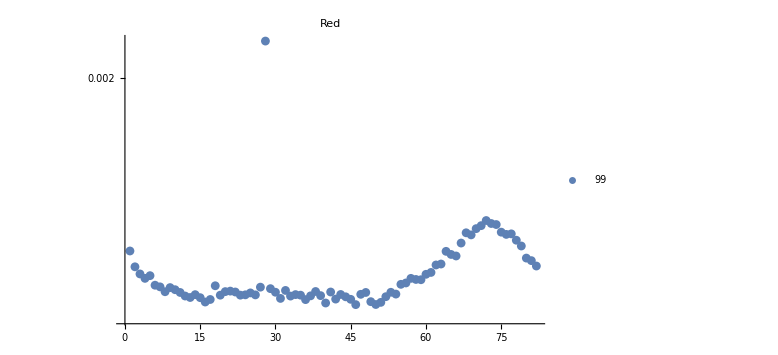
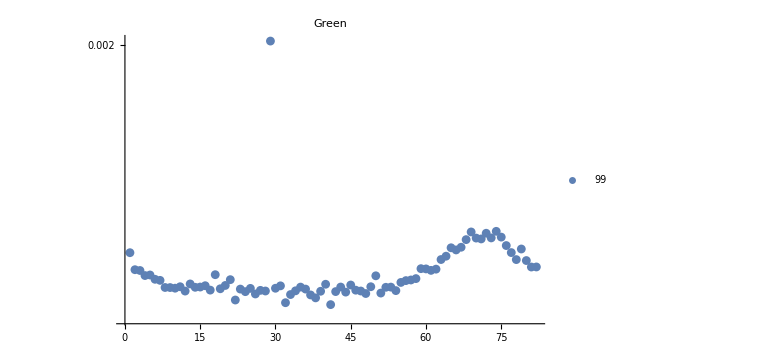
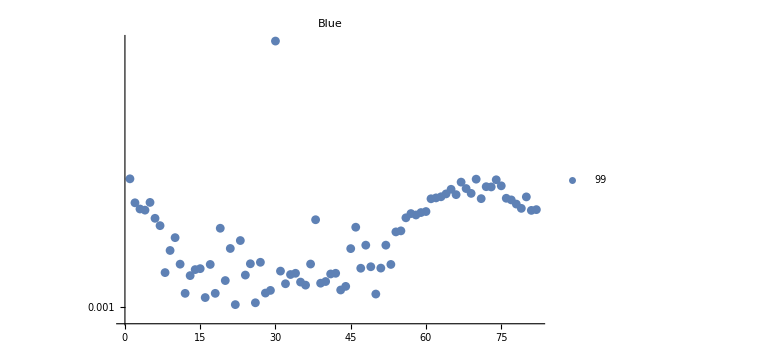

{orderedDarkMetrics,{{46,50,40,51,16,49,36,17,45,42,31,15,13,44,52,33,12,37,39,35,19,23,26,24,14,34,43,47,54,25,11,48,53,30,41,22,8,20,38,21,32,10,29,9,27,7,18,6,55,56,59,58,4,57,5,60,3,61,2,82,62,63,81,80,66,65,64,1,79,67,78,69,76,77,68,75,70,71,74,73,72,28},{41,32,22,38,37,33,26,48,51,44,24,42,39,12,28,47,34,54,27,46,17,23,36,19,25,30,10,9,8,52,14,35,53,15,43,11,49,31,16,20,45,40,13,55,56,7,57,21,6,58,50,4,5,18,3,61,2,62,60,59,81,82,80,78,63,64,1,77,66,79,65,67,76,68,71,70,73,75,72,69,74,29},{22,26,16,50,12,18,28,29,43,44,36,32,39,35,40,20,13,24,33,41,34,42,8,31,14,15,47,51,49,17,53,11,37,25,27,9,45,21,52,48,23,10,54,55,19,46,7,38,6,56,58,57,59,60,81,4,82,3,79,78,2,5,77,61,71,76,62,80,63,66,64,69,65,68,73,72,75,67,74,70,1,30}}}

{darkSegsCountOrig,49,darkSegsCount,49}

darkestSegmentIndicies = {{6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55},{6,7,8,9,10,11,12,13,14,15,16,17,19,20,21,22,23,24,25,26,27,28,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,51,52,53,54,55,56,57},{6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55}}

flatTotals = {65.8887,65.4667,65.123}

fnBaseName = JNCE_2016026_00C00083_V01.IMG.gz

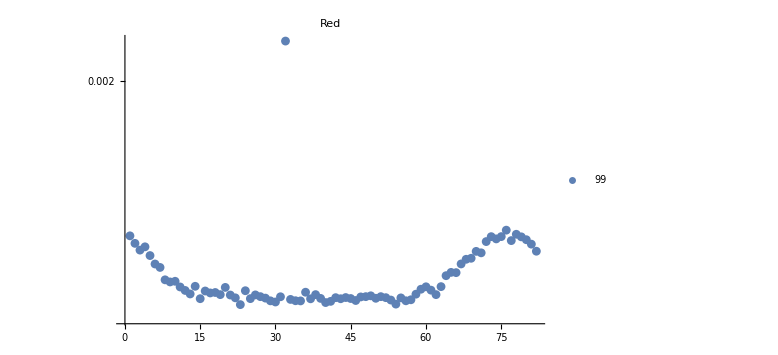
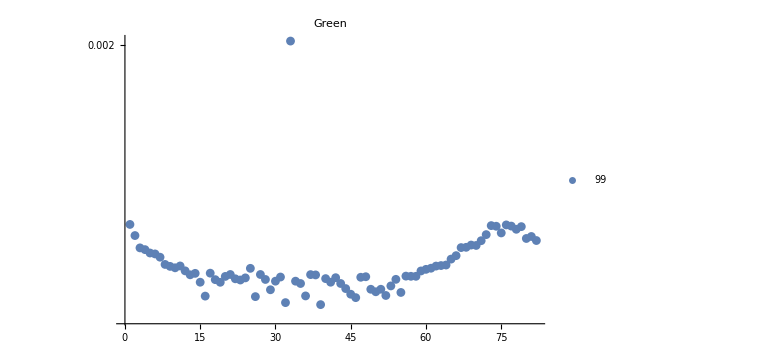
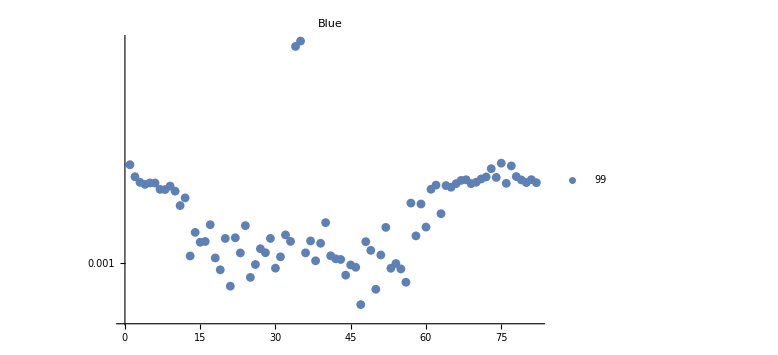

{orderedDarkMetrics,{{23,54,40,30,41,35,29,56,34,46,53,57,33,37,43,15,25,45,39,50,28,55,22,42,52,44,47,31,48,51,27,49,21,26,62,38,19,58,13,17,18,36,16,24,12,61,59,20,11,60,63,14,9,10,8,64,66,65,7,6,67,68,69,5,71,70,82,3,4,81,2,72,77,80,74,79,73,75,1,78,76,32},{39,32,46,26,16,36,52,45,55,50,29,51,49,44,53,43,35,19,41,15,30,34,23,18,28,54,22,40,24,42,47,31,48,20,58,57,56,38,13,37,21,27,14,17,59,12,60,25,61,10,9,62,11,63,64,8,65,7,66,6,5,4,3,67,68,70,69,71,82,80,81,2,72,75,78,79,74,77,73,76,1,33},{47,50,21,56,25,44,19,55,53,30,46,45,26,54,38,43,42,18,31,13,41,51,23,36,28,49,27,39,15,48,16,33,37,29,20,22,58,32,14,52,60,24,17,40,63,11,59,57,12,10,8,7,61,65,9,64,62,4,69,66,76,6,5,82,80,3,70,67,79,68,81,71,74,72,2,78,73,77,1,75,34,35}}}

{darkSegsCountOrig,49,darkSegsCount,49}

darkestSegmentIndicies = {{11,12,13,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,61,62},{12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61},{11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,63}}

flatTotals = {65.5505,65.1885,64.859}

fnBaseName = JNCE_2016040_00C00094_V01.IMG.gz

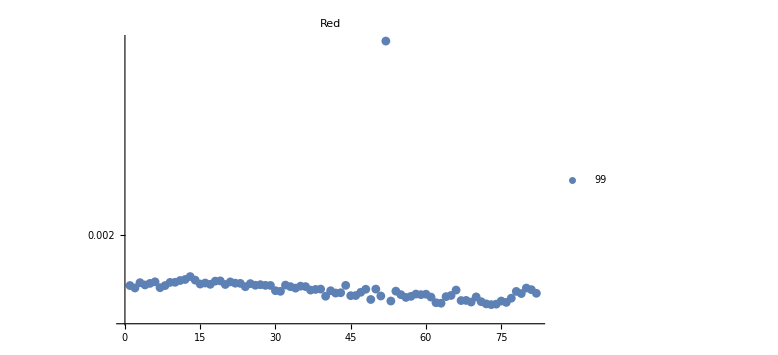
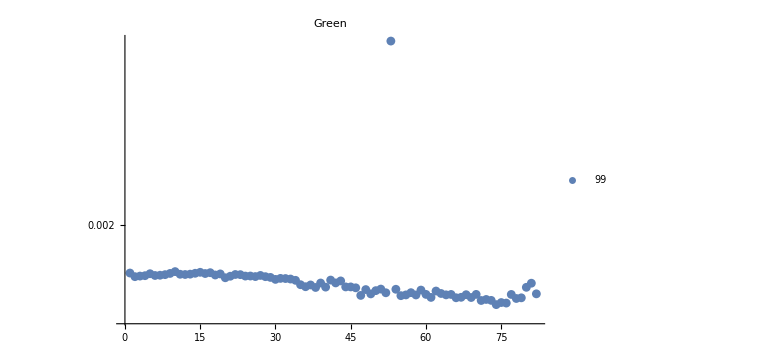
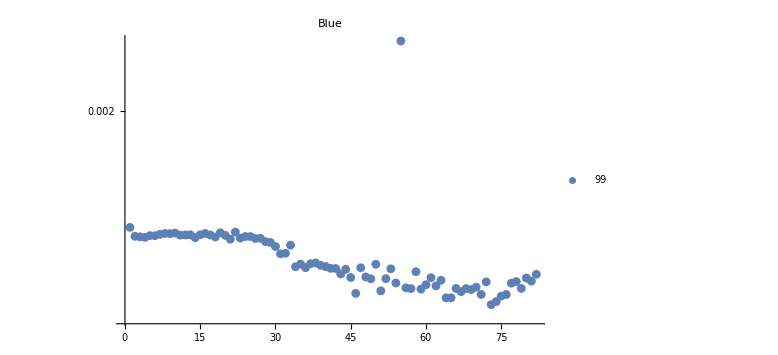

{orderedDarkMetrics,{{73,74,72,63,62,76,69,71,53,75,67,68,49,77,56,61,70,64,57,40,51,45,46,65,59,55,60,58,79,82,42,43,47,78,31,54,41,30,37,66,81,38,48,50,39,34,80,2,7,24,33,36,35,8,1,29,44,28,26,32,4,27,20,17,15,25,5,23,22,16,3,9,10,21,6,18,19,11,14,12,13,52},{74,76,75,71,73,72,78,79,66,69,61,67,55,47,58,56,64,68,65,77,70,60,49,82,63,52,57,62,50,59,48,54,51,46,38,80,40,44,45,36,37,35,81,39,42,43,34,41,30,33,32,31,20,29,28,2,26,21,24,3,25,4,6,27,7,18,23,8,22,12,11,13,19,5,16,9,14,1,17,15,10,53},{73,74,64,65,75,71,76,46,67,51,69,59,57,68,66,79,56,70,62,60,77,54,72,78,81,63,49,52,80,61,45,48,82,43,58,44,53,42,41,47,36,34,40,39,50,35,37,38,31,32,30,33,29,28,21,26,27,23,14,4,18,3,25,24,2,6,5,20,11,17,12,13,15,7,9,8,16,10,19,22,1,55}}}

{darkSegsCountOrig,49,darkSegsCount,49}

darkestSegmentIndicies = {{2,7,30,31,34,37,38,39,40,41,42,43,45,46,47,48,49,50,51,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82},{30,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82},{31,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82}}

flatTotals = {128.084,126.689,125.858}

fnBaseName = JNCE_2016040_00C00095_V01.IMG.gz

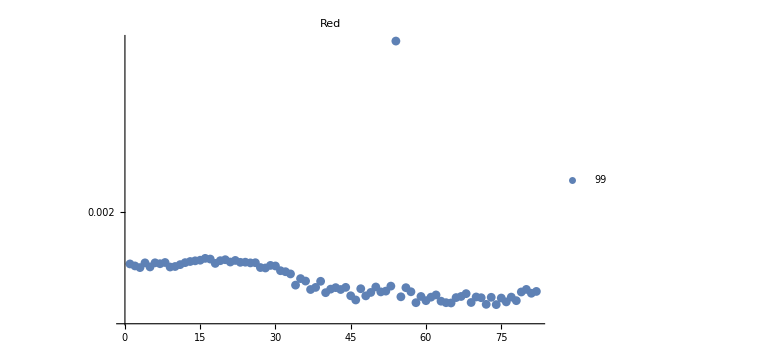
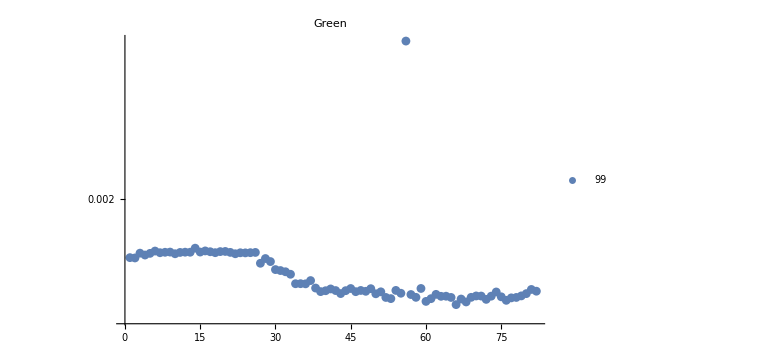
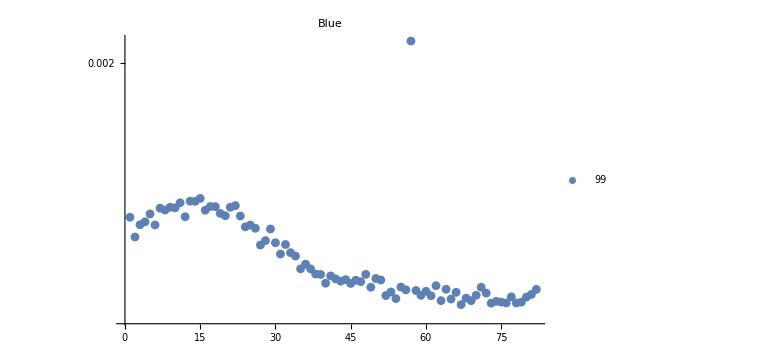

{orderedDarkMetrics,{{74,72,65,58,64,69,76,63,60,78,46,75,71,66,73,61,77,70,55,59,67,48,45,62,68,81,40,49,79,51,57,82,52,37,43,80,41,47,56,42,38,44,50,53,34,39,36,35,33,32,31,28,3,27,9,5,10,30,2,29,11,1,7,18,25,4,6,26,12,8,23,24,21,13,14,19,22,15,20,17,16,54},{66,68,60,76,72,67,61,53,77,78,65,52,69,58,75,63,64,73,71,70,79,57,62,50,80,43,55,74,51,46,39,48,82,40,44,42,47,54,81,41,49,45,59,38,36,34,35,37,33,32,31,30,27,29,28,2,1,4,10,22,5,3,24,23,7,25,18,26,11,21,8,13,12,9,15,17,19,20,6,16,14,56},{67,73,78,76,75,79,74,69,63,65,54,68,80,77,61,52,59,70,81,72,66,53,60,58,56,82,64,71,49,55,62,45,40,47,43,46,51,44,42,50,41,39,48,38,35,37,36,34,31,33,27,32,30,28,2,29,26,24,25,6,3,4,1,12,23,20,5,19,16,8,7,10,9,21,18,17,22,11,14,13,15,57}}}

{darkSegsCountOrig,49,darkSegsCount,49}

darkestSegmentIndicies = {{33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82},{33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82},{31,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82}}

flatTotals = {119.666,118.768,118.007}

fnBaseName = JNCE_2016040_00C00096_V01.IMG.gz

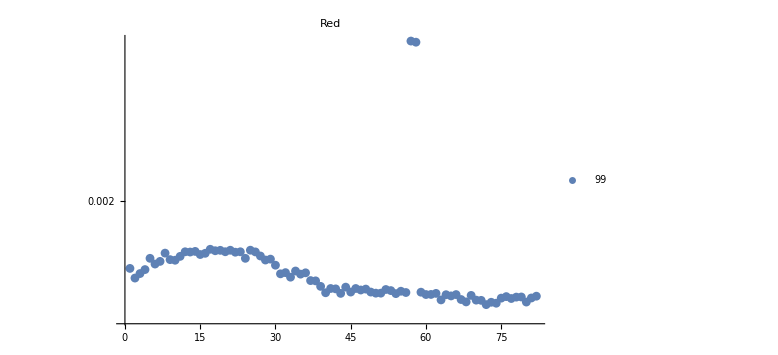
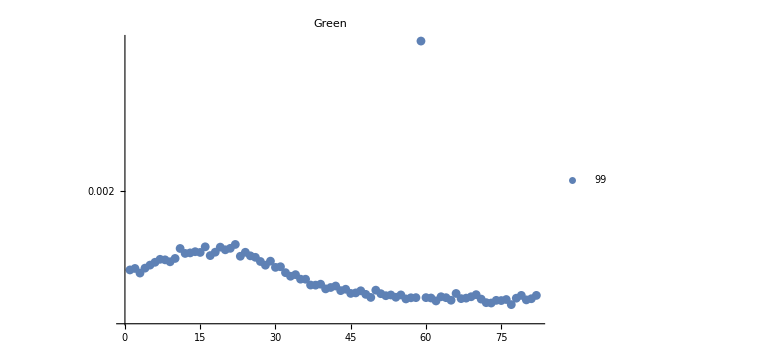
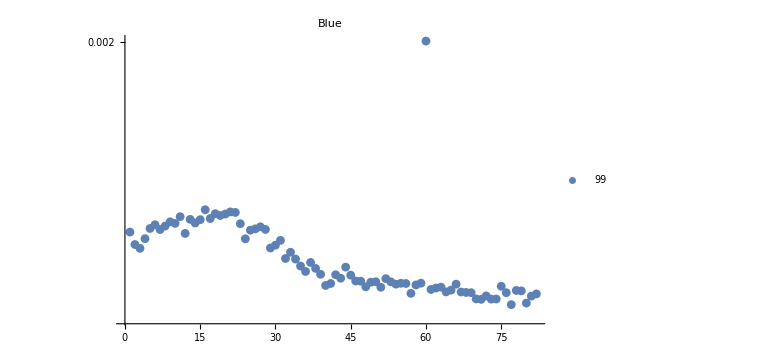

{orderedDarkMetrics,{{72,74,73,80,68,71,70,63,67,77,75,81,78,79,76,82,65,69,64,66,60,61,54,43,62,51,50,40,56,59,45,49,55,53,47,52,48,42,41,46,44,39,38,37,2,33,35,31,3,36,32,34,4,1,30,6,7,10,28,9,29,24,5,11,27,15,16,8,22,13,26,23,12,20,14,18,19,21,25,17,58,57},{77,73,72,62,75,74,65,80,76,71,56,81,67,78,68,61,57,64,58,60,49,54,63,69,52,82,79,53,55,70,48,51,66,45,46,47,43,50,44,40,41,42,38,37,39,36,35,33,34,3,32,1,2,4,30,31,28,5,6,9,27,29,8,7,10,26,23,25,17,12,13,15,24,18,14,20,11,21,19,16,22,59},{77,80,71,73,74,70,81,72,82,57,76,69,68,67,64,79,78,65,61,62,51,63,48,75,40,58,54,66,56,41,55,59,49,53,50,47,46,52,43,45,42,39,36,38,44,35,37,34,32,33,3,29,30,2,31,24,4,12,1,25,7,28,26,5,27,8,6,23,10,14,9,15,13,17,11,19,20,18,22,21,16,60}}}

{darkSegsCountOrig,49,darkSegsCount,49}

darkestSegmentIndicies = {{2,3,31,33,35,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82},{33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82},{32,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82}}

flatTotals = {115.2,113.779,113.028}

fnBaseName = JNCE_2016040_00C00097_V01.IMG.gz

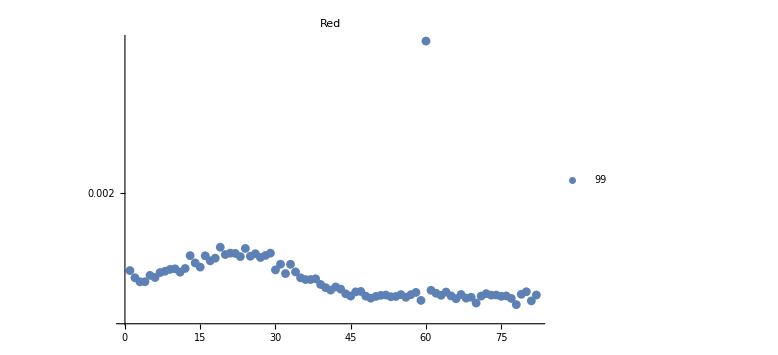
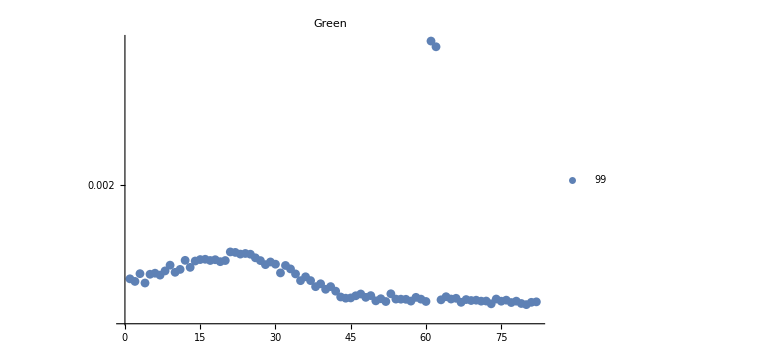
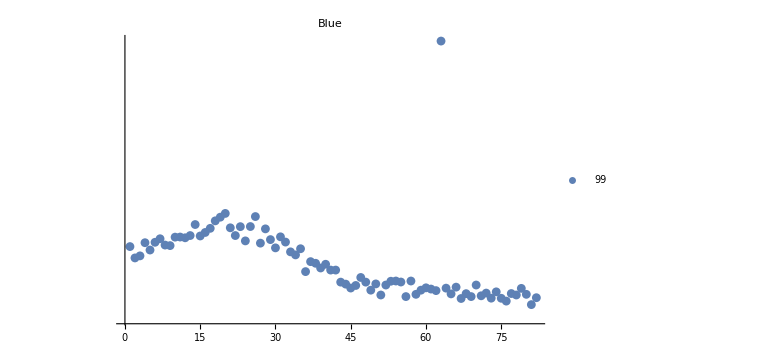

{orderedDarkMetrics,{{78,70,81,59,66,77,49,68,56,69,53,54,50,75,48,71,45,76,65,51,63,73,82,74,52,55,57,67,79,44,72,62,58,64,46,80,47,61,41,43,40,42,39,3,4,37,36,38,2,35,6,5,32,7,11,34,8,1,30,9,10,12,15,33,31,14,17,18,27,23,25,16,13,28,20,26,22,21,29,24,19,60},{80,73,79,77,81,67,82,52,60,75,71,78,57,72,50,69,70,76,63,68,56,55,59,54,74,65,51,66,44,45,58,48,43,64,46,49,47,53,42,40,38,41,39,4,2,35,37,1,36,7,5,34,3,6,31,10,8,11,33,13,32,9,28,30,29,19,14,27,20,17,12,18,15,16,26,25,23,24,22,21,62,61},{81,76,67,75,73,82,56,69,71,51,78,58,80,65,68,77,72,74,62,59,49,61,79,64,45,60,66,46,70,52,44,50,48,43,55,53,54,57,47,36,41,42,39,40,38,37,2,3,34,33,5,35,30,1,9,8,27,4,6,32,24,29,7,12,10,11,31,15,22,13,16,28,17,21,23,25,14,18,19,26,20,63}}}

{darkSegsCountOrig,49,darkSegsCount,49}

darkestSegmentIndicies = {{2,3,4,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82},{1,2,4,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82},{2,3,34,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82}}

flatTotals = {111.057,110.147,108.974}

fnBaseName = JNCE_2016040_00C00098_V01.IMG.gz

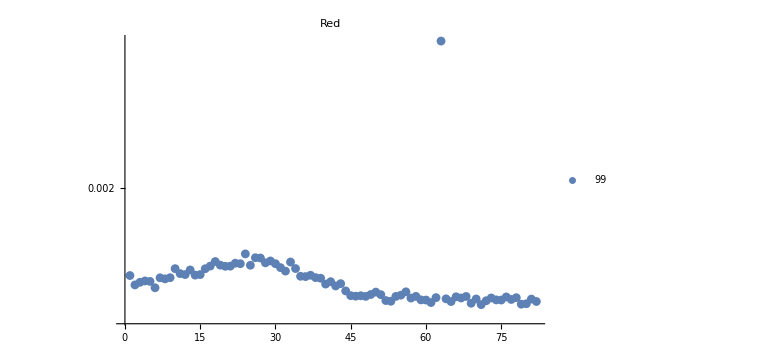
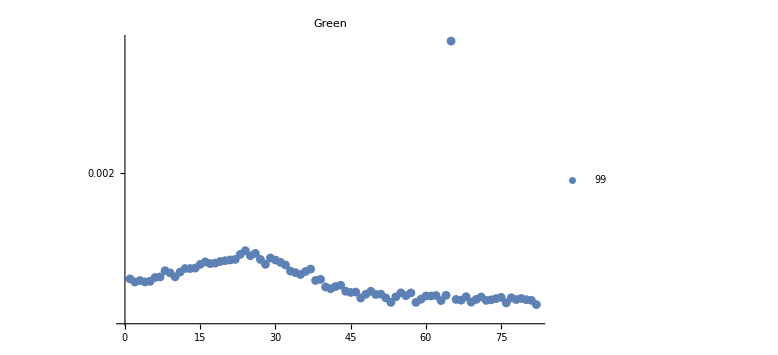
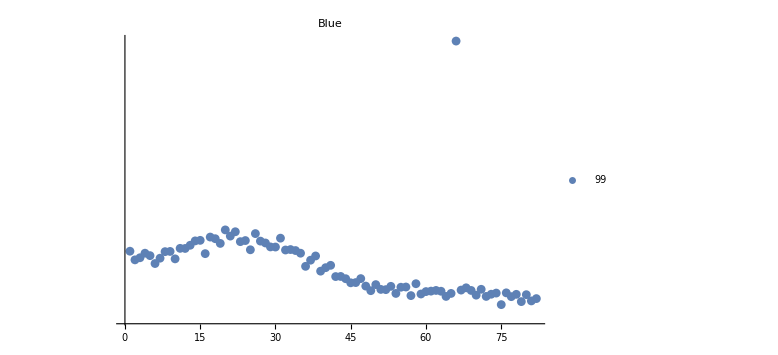

{orderedDarkMetrics,{{71,79,80,69,61,65,82,53,72,52,75,60,59,74,77,81,70,64,57,67,73,78,62,76,66,68,54,48,58,46,47,45,55,51,49,50,56,44,6,42,2,40,43,3,41,5,4,8,39,7,9,38,36,35,1,37,14,15,12,11,32,13,16,10,34,31,20,21,17,25,19,30,23,22,28,33,18,29,27,26,24,63},{82,76,53,58,69,63,72,81,67,73,80,78,66,70,59,79,74,47,52,77,75,71,54,68,60,61,56,62,64,50,48,51,57,55,45,46,49,44,41,40,42,43,2,4,5,3,38,39,1,6,7,10,35,9,34,11,36,33,8,37,13,12,14,32,15,28,17,18,31,16,19,20,30,21,27,22,29,25,23,26,24,65},{75,79,81,82,77,64,72,57,70,80,78,73,59,65,54,74,76,60,63,61,49,69,62,67,52,51,71,68,55,56,53,48,50,58,45,46,44,47,42,43,39,40,36,41,6,37,2,10,7,3,38,5,16,4,35,8,9,1,34,32,25,33,12,11,30,29,13,19,28,23,27,14,24,15,18,31,17,21,26,22,20,66}}}

{darkSegsCountOrig,49,darkSegsCount,49}

darkestSegmentIndicies = {{2,3,4,5,6,8,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82},{1,2,3,4,5,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82},{2,6,7,10,36,37,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82}}

flatTotals = {108.056,106.864,105.758}

fnBaseName = JNCE_2016040_00C00099_V01.IMG.gz

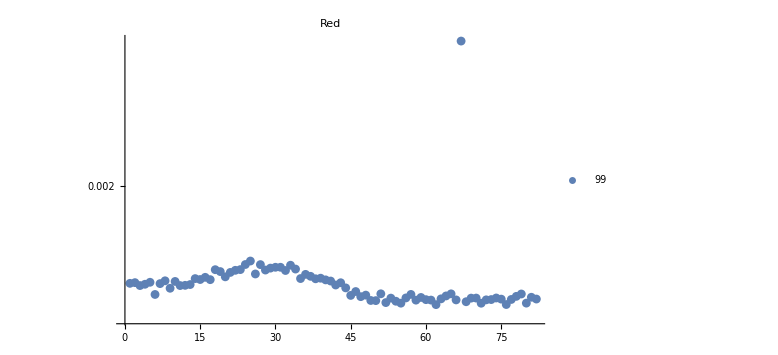
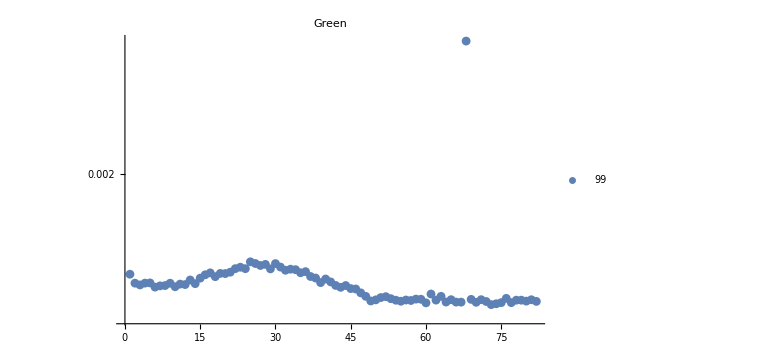
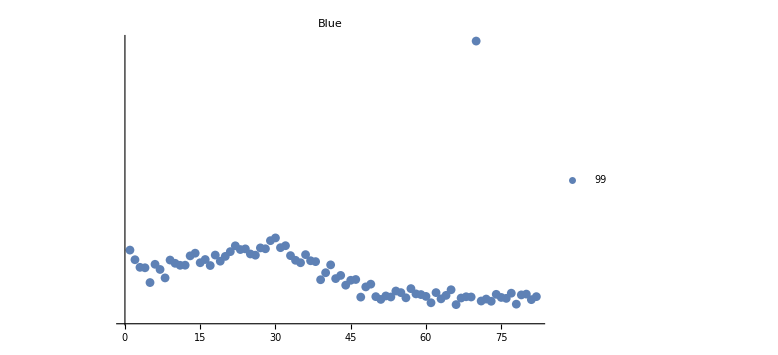

{orderedDarkMetrics,{{62,76,71,55,80,52,68,54,50,49,58,61,66,72,60,73,77,75,82,63,53,69,70,74,56,59,81,47,78,64,45,48,6,57,79,65,51,46,9,44,3,11,12,42,13,4,7,1,43,2,5,10,41,8,40,17,15,38,14,35,39,16,20,37,36,26,21,19,32,22,28,18,23,34,29,31,30,33,27,24,25,67},{73,74,60,77,75,70,67,66,64,72,82,55,80,49,57,54,79,78,62,56,50,81,71,65,69,59,58,53,76,51,52,48,63,61,47,46,45,43,6,10,7,44,8,42,3,12,11,14,9,2,4,5,39,41,13,40,15,38,18,37,16,1,20,19,17,35,21,36,32,34,33,29,24,22,23,31,27,28,30,26,25,68},{66,78,61,73,71,81,51,72,63,76,67,56,75,47,53,69,68,82,50,60,52,64,79,59,74,80,58,77,55,62,54,65,57,48,44,49,5,45,39,46,42,8,43,40,7,4,3,17,11,12,41,6,10,35,15,38,19,37,34,9,2,16,20,13,33,26,18,36,25,14,21,1,23,24,28,27,31,22,32,29,30,70}}}

{darkSegsCountOrig,49,darkSegsCount,49}

darkestSegmentIndicies = {{1,3,4,6,7,9,11,12,13,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82},{3,6,7,8,9,10,11,12,14,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,69,70,71,72,73,74,75,76,77,78,79,80,81,82},{3,4,5,7,8,11,17,39,40,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,71,72,73,74,75,76,77,78,79,80,81,82}}

flatTotals = {105.246,103.969,102.827}

fnBaseName = JNCE_2016040_00C00105_V01.IMG.gz

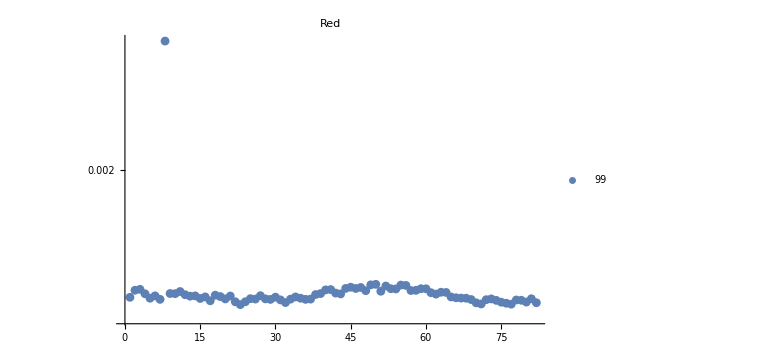
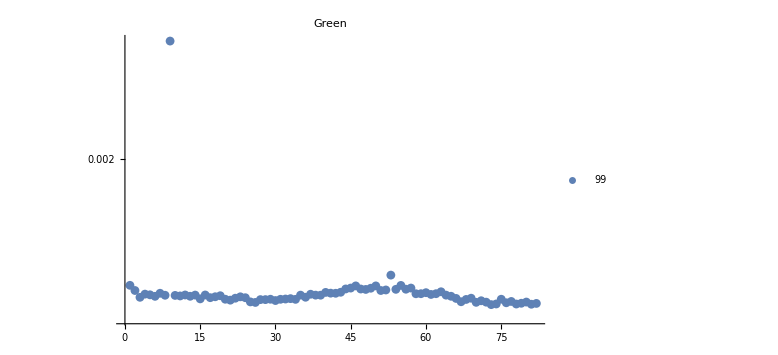
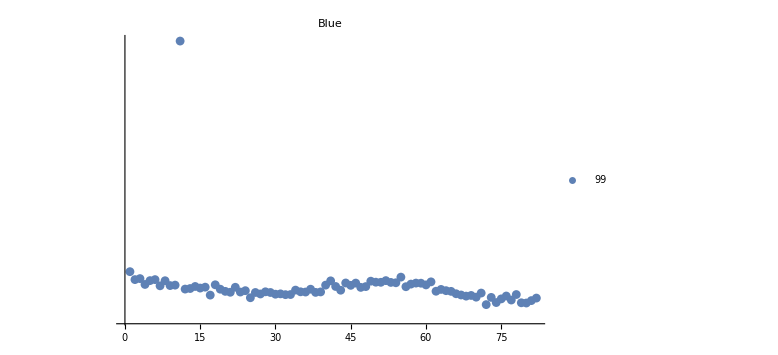

{orderedDarkMetrics,{{23,77,71,76,70,82,32,75,80,22,24,17,74,79,78,31,72,69,29,7,36,33,37,26,20,73,28,81,25,15,5,68,35,67,66,1,30,34,65,16,19,13,21,14,6,27,18,12,38,62,43,4,10,39,9,42,61,64,63,11,51,48,57,58,2,40,41,3,54,60,59,53,46,44,47,45,52,56,55,49,50,8},{73,81,78,74,82,79,76,26,70,72,80,25,67,77,71,30,21,27,28,68,34,31,20,75,29,32,15,33,66,69,22,24,17,3,36,23,18,6,13,65,11,19,10,8,39,38,35,64,14,16,12,5,61,37,4,58,59,62,42,7,41,60,40,43,63,51,2,52,48,54,56,47,44,49,57,45,50,46,55,1,53,9},{72,80,79,74,81,77,75,82,25,73,70,68,76,69,17,67,32,78,33,30,27,31,66,71,29,26,38,21,36,23,39,35,28,20,65,62,24,64,43,34,63,19,37,12,13,15,47,22,16,56,48,42,14,7,9,45,10,40,60,18,4,57,59,58,46,44,54,53,51,50,61,49,41,8,52,5,2,6,3,55,1,11}}}

{darkSegsCountOrig,49,darkSegsCount,49}

darkestSegmentIndicies = {{1,5,6,7,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82},{3,6,8,10,11,13,14,15,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,38,39,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82},{12,13,15,16,17,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,43,47,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82}}

flatTotals = {90.2027,88.8652,87.2563}

fnBaseName = JNCE_2016040_00C00106_V01.IMG.gz

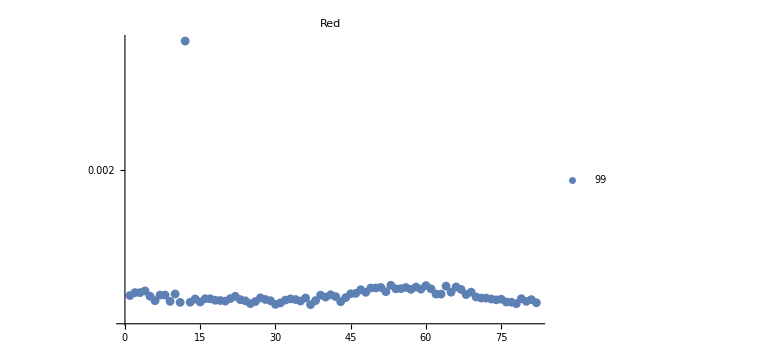
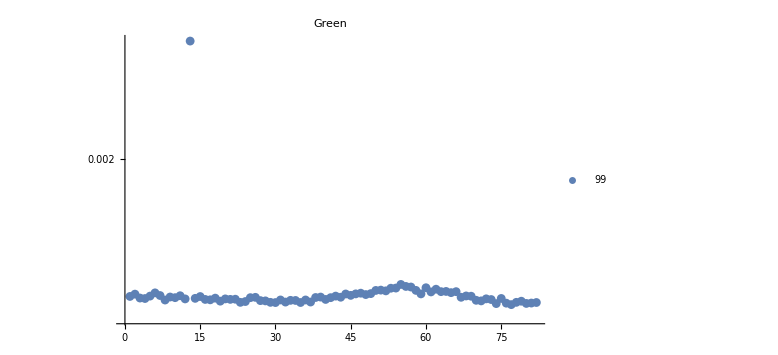
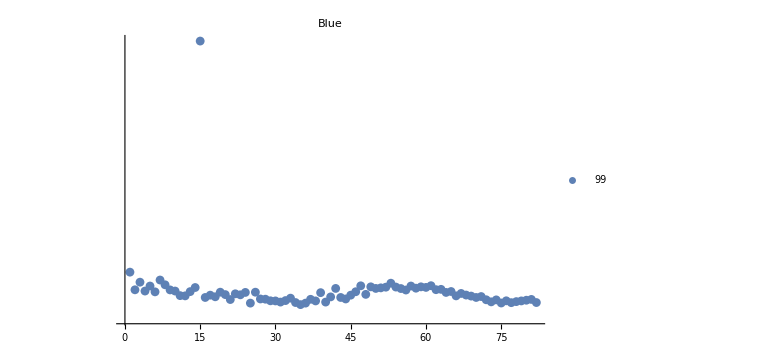

{orderedDarkMetrics,{{37,30,78,25,31,82,11,13,77,76,15,43,26,9,80,20,35,24,6,29,38,19,18,32,74,23,81,34,28,75,14,73,33,17,79,16,21,72,71,36,27,44,40,70,42,22,5,1,39,7,8,41,68,62,63,10,45,46,2,3,48,65,69,52,4,47,67,57,59,54,61,55,49,50,56,51,58,66,64,60,53,12},{77,74,80,76,81,30,35,82,23,29,78,32,37,24,79,19,71,28,27,34,33,70,8,31,36,17,73,16,40,21,22,12,20,72,4,75,14,18,3,25,10,41,38,26,67,43,39,9,15,1,69,5,42,68,11,7,45,48,2,44,46,59,49,47,6,65,61,66,63,64,52,50,58,51,62,53,54,60,57,56,55,13},{35,25,36,75,77,82,34,40,31,73,78,79,38,30,76,29,32,80,74,72,21,81,37,28,44,27,33,70,16,43,41,18,71,69,12,66,11,45,17,68,23,20,48,22,67,39,24,64,19,26,6,46,13,65,4,10,56,9,2,62,63,55,42,50,58,51,14,60,52,54,59,49,57,5,47,61,8,53,3,7,1,15}}}

{darkSegsCountOrig,49,darkSegsCount,49}

darkestSegmentIndicies = {{1,5,6,9,11,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,42,43,44,70,71,72,73,74,75,76,77,78,79,80,81,82},{3,4,8,9,10,12,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,43,67,70,71,72,73,74,75,76,77,78,79,80,81,82},{11,12,16,17,18,19,20,21,22,23,24,25,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,43,44,45,48,64,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82}}

flatTotals = {88.4045,87.1785,85.4555}

fnBaseName = JNCE_2016040_00C00107_V01.IMG.gz

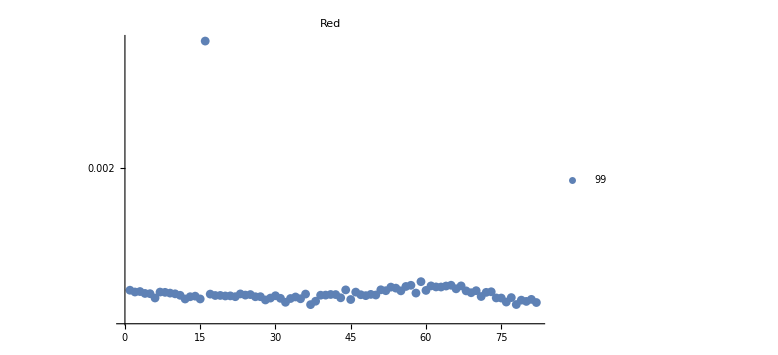
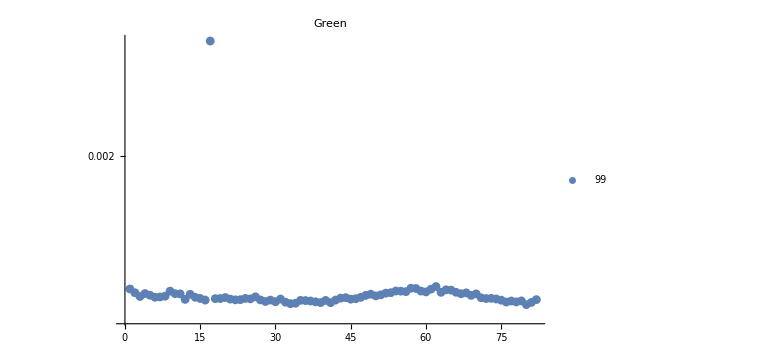
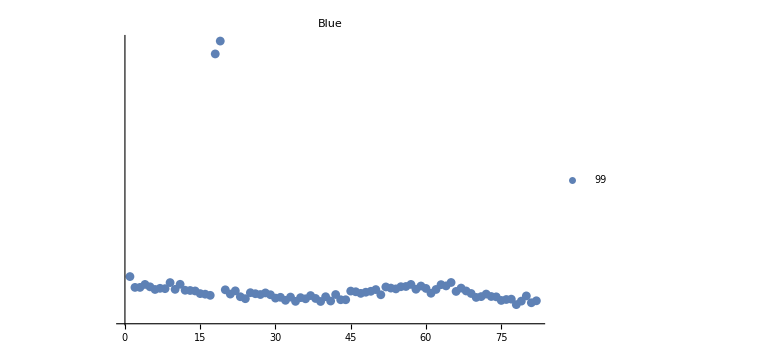

{orderedDarkMetrics,{{37,78,82,32,76,80,38,79,28,45,81,12,15,35,33,31,29,75,6,74,43,77,34,13,26,27,22,71,14,20,21,30,48,18,19,11,39,40,24,50,47,42,25,41,49,17,36,23,10,5,4,9,58,69,72,8,46,7,2,73,3,68,55,52,70,60,1,44,51,66,54,53,63,62,56,64,61,67,57,65,59,16},{80,33,34,41,39,81,32,76,78,38,30,28,37,77,79,36,40,35,75,16,29,42,27,22,23,82,12,45,21,31,74,25,46,18,72,19,15,24,73,43,71,44,20,47,6,14,7,26,3,8,50,48,69,5,51,13,49,11,70,67,10,4,52,68,2,53,63,66,60,56,55,9,59,54,65,64,61,1,58,57,62,17},{78,81,39,34,79,41,82,75,32,44,43,76,77,36,24,38,30,35,70,31,33,74,23,40,71,73,80,37,17,29,51,27,42,16,72,21,26,15,69,47,61,28,25,48,46,66,49,45,14,68,22,13,12,20,50,6,62,10,58,54,8,60,7,67,53,3,2,52,5,55,56,59,64,63,4,57,11,9,65,1,18,19}}}

{darkSegsCountOrig,49,darkSegsCount,49}

darkestSegmentIndicies = {{6,10,11,12,13,14,15,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,45,47,48,49,50,71,74,75,76,77,78,79,80,81,82},{3,6,7,12,14,15,16,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,71,72,73,74,75,76,77,78,79,80,81,82},{14,15,16,17,21,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,51,61,66,69,70,71,72,73,74,75,76,77,78,79,80,81,82}}

flatTotals = {86.6506,85.2731,83.7331}

{3820.07,{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}}

```mathematica
(* only need to do this if it hasn't been done before (for a given flatScaleFactor) *)
AbsoluteTiming[Map[imgToFlat, fileList[[1;;-1]]]] (* 3;;-2 -> 2763 sec
36 3458.1 sec  *)
```

```mathematica
MemoryInUse[](*3843104344*)
```

386478904

Extract and Match Control Points

### Segments to Full-Frames

Convert a RGB group of 3 framelets back to a full CCD sized frame based on readout lines

The actual start lines for each 128-line band framelet relative to line 0 at the “top” of the sensor are 291, 456, 611, and 766 with the nominal optic axis at line 600. And the focal length is 10.997mm.

From post http://www.unmannedspaceflight.com/index.php?showtopic=2548&st=465&p=203948&#entry203948

291M, 456B, 611G, and 766R

1600x1200 sensor with 7.4μ sensor  from
http://www.onsemi.com/PowerSolutions/product.do?id=KAI-2020

1640 × 1214 7.4-micron pixels (1600 × 1200 pho- toactive)  from 

FOV 58 per cal report

Using sensor size of 11.84 x 8.88 (from CCD manual) and 10.997 FOV from post and spice into FOV calculator at https://www.scantips.com/lights/fieldofview.html#top
gives FOV 56.59 wide 43.97 high 67.87 diag

Per hugin 10.997 FL * 2.8899 FL multiplier gives 43.97 FOV

```mathematica
31.78/10.997
```

2.88988

```mathematica
t=;  
(* Photo of color filters on CCD from
Junocam:Juno’s Outreach Camera
C.J.Hansen·M.A.Caplinger·A.Ingersoll·M.A.Ravine·E.Jensen·S.Bolton·G.Orton
Space Sci Rev
DOI 10.1007/s11214-014-0079-x
 *)
```

```mathematica
filterOffsets={766,611,456,291} (* R,G,B,M.  Rows from top (M/B end) of CCD to readout line for filter. *)
```

{766,611,456,291}

```mathematica
Differences[filterOffsets]
```

{-155,-155,-165}

```mathematica
rgbToFullFrame[rgbList_]:=ColorCombine[{
(*ImagePad[segs[[1,2,1]],{{0,0},{1214-(291-1)-128,291-1}}] (* Methane *)*)
ImagePad[rgbList[[1]],{{0,0},{1214-(766-1)-128,766-1}}] (* Red *)
,ImagePad[rgbList[[2]],{{0,0},{1214-(611-1)-128,611-1}}] (* Green *)
,ImagePad[rgbList[[3]],{{0,0},{1214-(456-1)-128,456-1}}] (* Blue *)
}]
```

```mathematica
(*filtersFullFrame=rgbToFullFrame[testSegs=ConstantArray[
ReplacePixelValue[ConstantImage[1,{1648,128}],{{1;;4,3;;4},{3;;4,1;;4}}->0],3]]*)
```

```mathematica
(*ImageReflect[ImageRotate[filtersFullFrame]]*)
```

```mathematica
MemoryInUse[] (* 948594528 *)
```

386753656

### Extract Point Sources (Potential Control Points) (New Method)

```mathematica
flattenedSegsFiles=Map[StringReplace[#,imgToFlattenedSegsFilenameGZ ]&,fileList](*[[1;;2]]*)
```

{/Users/bswift/Downloads/ORBIT_00/JNCE_2016129_00C00164_V01_2_flattenedSegs.mx.gz,/Users/bswift/Downloads/ORBIT_00/JNCE_2016129_00C00165_V01_2_flattenedSegs.mx.gz,/Users/bswift/Downloads/ORBIT_00/JNCE_2016130_00C00171_V01_2_flattenedSegs.mx.gz,/Users/bswift/Downloads/ORBIT_00/JNCE_2016131_00C00180_V01_2_flattenedSegs.mx.gz,/Users/bswift/Downloads/ORBIT_00/JNCE_2016164_00C00195_V01_2_flattenedSegs.mx.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00058_V01_2_flattenedSegs.mx.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00059_V01_2_flattenedSegs.mx.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00060_V01_2_flattenedSegs.mx.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00061_V01_2_flattenedSegs.mx.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00062_V01_2_flattenedSegs.mx.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00063_V01_2_flattenedSegs.mx.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00070_V01_2_flattenedSegs.mx.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00071_V01_2_flattenedSegs.mx.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00072_V01_2_flattenedSegs.mx.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00073_V01_2_flattenedSegs.mx.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00074_V01_2_flattenedSegs.mx.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00080_V01_2_flattenedSegs.mx.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00081_V01_2_flattenedSegs.mx.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00082_V01_2_flattenedSegs.mx.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00083_V01_2_flattenedSegs.mx.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016040_00C00094_V01_2_flattenedSegs.mx.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016040_00C00095_V01_2_flattenedSegs.mx.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016040_00C00096_V01_2_flattenedSegs.mx.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016040_00C00097_V01_2_flattenedSegs.mx.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016040_00C00098_V01_2_flattenedSegs.mx.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016040_00C00099_V01_2_flattenedSegs.mx.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016040_00C00105_V01_2_flattenedSegs.mx.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016040_00C00106_V01_2_flattenedSegs.mx.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016040_00C00107_V01_2_flattenedSegs.mx.gz}

```mathematica
Length[flattenedSegsFiles]
```

29

```mathematica
flattenedSegsFiles[[{1,-1}]]
```

{/Users/bswift/Downloads/ORBIT_00/JNCE_2016129_00C00164_V01_2_flattenedSegs.mx.gz,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016040_00C00107_V01_2_flattenedSegs.mx.gz}

```mathematica
rejectBright[img_]:=If[Total[Flatten[ImageData[img]]]> -15.0
,ImageClip[img,{100000,100001},{0,1}]
,img]
```

```mathematica
(*AbsoluteTiming[
(* component measurments ComponentPropertyAssociation for each framelet *)
cmpa=Map[
Map[
ComponentMeasurements[
ImageClip[rejectBright[#],{flatClipLevel  dnStep,1},{0,1}]
,{"Count","IntensityCentroid","TotalIntensity"}
,#Count≤ 9 & 
, "ComponentPropertyAssociation" (* "Dataset" *)
]&
,
Import[#],{-1}
]&
,flattenedSegsFiles[[1;;-1]]
];
] *)
(* 90.7 for 24 serial
115.6 for 29 serial
120.9 for 29 with reject *)
```

```mathematica
AbsoluteTiming[
(* component measurments ComponentPropertyAssociation for each framelet *)
(* Dynamic (per segment) image clip level that clips everything darker than 6th brightest,
with Jupiter masked out.
 Part of work to pull in stars at top of graph (near range/left).
  *)
cmpa=Parallelize[Map[
Map[
ComponentMeasurements[
ImageClip[rejectBright[#],{RankedMax[Flatten[ImageData[
ImageMultiply[#,ColorNegate[MaxFilter[Binarize[#,.2],8]]] (* Mask out image near (8 pix) bright (.2) areas (aka jupiter) *)
]]
,6]
,1},{0,1}]
,{"Count","IntensityCentroid","TotalIntensity"}
,#Count≤ 9 & 
, "ComponentPropertyAssociation" (* "Dataset" *)
]&
,
Import[#],{-1}
]&
,flattenedSegsFiles[[1;;-1]]
]
];
] (* 90.7 for 24 serial
115.6 for 29 serial
120.9 for 29 with reject
146 dynamic clip serial
63.8 dynamic clip parallel *)
```

{143.898,Null}

```mathematica
(* development of dynamic threshold *)
```

```mathematica
(*segs=Import [flattenedSegsFiles[[1]]];*)
```

```mathematica
(*adjSegs=Map[ImageAdjust[
ImageClip[#
,{RankedMax[Flatten[ImageData[ImageMultiply[#,ColorNegate[MaxFilter[Binarize[#,.2],8]]]]]
,3]
,1},{0,1}]
,{0,0,1},{0{1,1,1},3 8/2879.{1,1,1}}]&,segs,{-1}];
(*“JNCE_2016026_00C00083_V01.IMG.bz2”->flat scale 3,crush 3.5*)
colorSegs=Transpose[Map[ColorCombine,Transpose[adjSegs,{3,2,1}],{-2}]];
inspectionImage=MaxFilter[ImageAssemble[colorSegs[[1;;-1]]],3];*)
```

```mathematica
Dimensions[cmpa] (* {29,3,82,1} *)
```

{29,3,82,1}

```mathematica
cmpa[[1,1,1,1]]
```

<|1→<|Count→1,IntensityCentroid→{1275.5,112.5},TotalIntensity→0.00157413|>,2→<|Count→1,IntensityCentroid→{192.5,100.5},TotalIntensity→0.00165542|>,3→<|Count→1,IntensityCentroid→{766.5,78.5},TotalIntensity→0.00156674|>,4→<|Count→1,IntensityCentroid→{433.5,43.5},TotalIntensity→0.00169237|>,5→<|Count→1,IntensityCentroid→{1355.5,35.5},TotalIntensity→0.00212101|>,6→<|Count→1,IntensityCentroid→{351.5,27.5},TotalIntensity→0.00161108|>|>

```mathematica
(*Export["/Users/bswift/Pictures/Jupiter/Junocam/cmpaAll.mx",cmpa];*)
```

```mathematica
(* TotalIntensity value of 50th brightest component in each color plane in each file of segments.
These intensityThresholds are used to select the 50 brightest components.  (Can be more than 50 if multiple components have identical intensity.) *)
intensityThresholds=Map[
Sort[Flatten[Values[#[[All,1,All,"TotalIntensity"]]]]][[-50]]&
,cmpa,{2}
]
```

{{0.00169976,0.0016702,0.0016702},{0.00169976,0.00171454,0.0015963},{0.00165542,0.00165542,0.00162586},{0.00164064,0.00164064,0.00162586},{0.00157413,0.00158891,0.00138937},{0.00131547,0.00134503,0.00125635},{0.00161847,0.00157413,0.00151501},{0.00157413,0.00161847,0.00147805},{0.00161847,0.00155935,0.00150023},{0.00166281,0.00156674,0.00147805},{0.00162586,0.00157413,0.00150762},{0.00158152,0.0015224,0.00150762},{0.0015224,0.00153718,0.00149284},{0.00169237,0.00153718,0.00147805},{0.00156674,0.0015224,0.00149284},{0.00153718,0.0015224,0.00150762},{0.00160369,0.00149284,0.00146327},{0.00161108,0.00149284,0.00144849},{0.00179584,0.00149284,0.00141893},{0.00150762,0.00149284,0.00144849},{0.00147066,0.0014411,0.0014411},{0.00147066,0.00147066,0.0014411},{0.00150023,0.00148544,0.00147066},{0.00151501,0.00155935,0.00148544},{0.00151501,0.00152979,0.00148544},{0.00154457,0.00152979,0.00150023},{0.00158891,0.00152979,0.00147066},{0.00151501,0.00157413,0.00147066},{0.00154457,0.00150762,0.00150762}}

```mathematica
(* Select out components with TotalIntensity ≥ intensityThresholds.
Should select about 50 components per color plane per file. *)
brightest=MapThread[
Function[{cmpaSegs,thresh},
Map[
Select[#,(#["TotalIntensity"]≥ thresh)&] &
,cmpaSegs,{2}
]
]
,{cmpa,intensityThresholds},2
];
```

```mathematica
(* Select out components with TotalIntensity ≥ intensityThresholds.
Should select about 50 components per color plane per file. *)
brightest=MapThread[
Function[{cmpaSegs,thresh},
Map[
Select[#,(#["TotalIntensity"]≥ thresh&&(1.51<#⟦"IntensityCentroid",2⟧<(128-1.51)))&] &
,cmpaSegs,{2}
]
]
,{cmpa,intensityThresholds},2
];
```

```mathematica
Dimensions[cmpa]
```

{29,3,82,1}

```mathematica
(* Select 3 brightest from each segment *)
(*brightest=MapThread[
Function[{cmpaSegs,thresh},
Map[
If[#≠ <||> 
,SortBy[#,#["TotalIntensity"]&][[-3;;-1]]
,#
]&

,cmpaSegs,{2}
]
]
,{cmpa,intensityThresholds},2
];*)
```

```mathematica
(* check number of components selected from each color plane.
Note: brightest contains many empty associoations <||> for framlets which don't have any components brighter than threshold. These need to be discarded. *)
newBrightestLengths=Map[
Total[Length /@ Select[Flatten[#],#≠ <||>&]]&
,brightest,{2}
]
```

{{48,53,47},{59,46,50},{49,50,50},{50,49,51},{48,53,53},{49,50,48},{50,48,50},{53,48,50},{49,50,50},{47,49,50},{48,47,48},{47,47,49},{53,50,48},{48,51,56},{52,51,49},{53,50,48},{48,60,53},{51,67,56},{48,50,48},{50,58,54},{47,49,52},{48,55,52},{52,53,47},{49,51,50},{50,51,47},{52,55,50},{48,51,48},{48,47,46},{47,48,51}}

```mathematica
oldBrightestLengths={{54,57,50},{61,50,51},{51,55,51},{52,50,52},{50,54,53},{50,51,51},{51,50,51},{55,51,51},{51,50,51},{50,50,53},{50,50,50},{50,50,50},{54,50,52},{50,51,57},{52,55,51},{57,53,50},{50,64,55},{51,67,57},{50,51,51},{53,60,55},{50,51,53},{50,55,52},{53,57,50},{51,51,51},{52,52,50},{54,56,51},{50,53,50},{50,50,50},{50,50,51}} (* Before restriction that points be > 1.51 away from filter top/bottom *)
```

{{54,57,50},{61,50,51},{51,55,51},{52,50,52},{50,54,53},{50,51,51},{51,50,51},{55,51,51},{51,50,51},{50,50,53},{50,50,50},{50,50,50},{54,50,52},{50,51,57},{52,55,51},{57,53,50},{50,64,55},{51,67,57},{50,51,51},{53,60,55},{50,51,53},{50,55,52},{53,57,50},{51,51,51},{52,52,50},{54,56,51},{50,53,50},{50,50,50},{50,50,51}}

```mathematica
oldBrightestLengths-newBrightestLengths
```

{{6,4,3},{2,4,1},{2,5,1},{2,1,1},{2,1,0},{1,1,3},{1,2,1},{2,3,1},{2,0,1},{3,1,3},{2,3,2},{3,3,1},{1,0,4},{2,0,1},{0,4,2},{4,3,2},{2,4,2},{0,0,1},{2,1,3},{3,2,1},{3,2,1},{2,0,0},{1,4,3},{2,0,1},{2,1,3},{2,1,1},{2,2,2},{2,3,4},{3,2,0}}

```mathematica
Dimensions[brightest]  (* {24,3,82,1} file, color, frame, exrtra level, assoc of components in framelet, assoc of one component *)
```

{29,3,82,1}

```mathematica
(*reflectTransform=ReflectionTransform[{0,1},{0,ccdSize[[2]]/2}]*)
```

```mathematica
rotateTransform=Composition[TranslationTransform[{0,ccdSize[[2]]}],RotationTransform[-90 Degree]]
```

TransformationFunction[(0 | 1 | 0
-1 | 0 | 1648
0 | 0 | 1)]

```mathematica
(* Transform Mathematica image coordinates to Hugin control point coordinaes.
Hugin coordinates assume left to right assembly of framelets into panorama (rotation) and origin is at top left instead of bottom left (reflect).  Earlier version did ImageRotate[ImageReflect[full frame]] prior to identifying control points with ComponentMeasurements.
*)
(*toHuginCoords=Composition[reflectTransform,rotateTransform]*)
```

```mathematica
toHuginCoords=rotateTransform
```

TransformationFunction[(0 | 1 | 0
-1 | 0 | 1648
0 | 0 | 1)]

```mathematica
Clear[x,y];toHuginCoords[{x,y}] (* {y,1648-x} *)
```

{y,1648-x}

```mathematica
Clear[toHuginCoords];
toHuginCoords[{x_,y_}]:={y,x}
```

```mathematica
Clear[x,y];toHuginCoords[{x,y}] (* {y,1648-x} *)
```

{y,x}

```mathematica
Clear[x,y];toHuginCoords[{x,y}] (* {y,1648-x} *)
```

{y,x}

```mathematica
(* Transform component measurements ImageCentroid coordinate to Hugin horizontal panorama coordinates *)
```

```mathematica
toFullFrame[color_,icLoc_]:=toHuginCoords[{0,filterOffsets⟦color⟧}+{0,128}+{1,-1}icLoc]
```

```mathematica
(* Shift a hugin coordinate by frame amount *)
toHPlot[frame_,icLoc_]:= {(116 +200 (* to spread out *) ) frame ,0}+icLoc
```

```mathematica
toFullFramePlot[frame_,color_,icLoc_]:=toHPlot[frame,toFullFrame[color,icLoc]]
```

```mathematica
(* Convert intensityCentroid location coordinate to that produced by ComponentMeasurments of ImageAsembeled framelets. *)
toPlot[frame_,icLoc_]:= {0,128(82-frame)}+icLoc
```

```mathematica
(* Convert intensityCentroid location coordinate to that produced by ComponentMeasurments of ImageAsembeled framelets.
colorIndex 1,2,3 -> RGB, raw file is ordered BGR   *)
toRawColumnRow[{fileIndex_,colorIndex_,segmentIndex_,cpIndex_,assocKey_},icLoc_]:= {0,128(3(segmentIndex-1)+{2,1,0}⟦colorIndex⟧ )}+{0,128}+{1,-1}icLoc
```

```mathematica
(* Append additional properties to each component and drop empty Association.
  brightest⟦file,color,segment,component in segment⟧ *)
brightestAnnotated=MapIndexed[
If[#==<||>
,Nothing
,Append[#,{"index"-> #2,"color"-> #2[[2]],"frame"-> #2[[3]]
,"icFullFrame"-> toFullFrame[#2[[2]],#["IntensityCentroid"]]
,"icFFPlot"-> toFullFramePlot[#2[[3]],#2[[2]],#["IntensityCentroid"]]
,"icPlot"-> toPlot[#2[[3]],#["IntensityCentroid"]]
,"rawLoc"-> toRawColumnRow[#2,#["IntensityCentroid"]]
,"fname"-> FileNameTake[fileList⟦#2⟦1⟧⟧]
}]
]&
,brightest,{-2}];
```

```mathematica
FileNameTake[fileList[[1]]]
```

JNCE_2016129_00C00164_V01.IMG.gz

```mathematica
Dimensions[brightest]
```

{29,3,82,1}

```mathematica
brightest⟦ 1,1,1,1⟧
```

<|5→<|Count→1,IntensityCentroid→{1355.5,35.5},TotalIntensity→0.00212101|>|>

```mathematica
Dimensions[brightestAnnotated]
```

{29,3,82}

```mathematica
Dimensions[Values[brightestAnnotated[[All,All,All,All,All,"icFullFrame"]]]]
```

{29,3,82}

```mathematica
Dimensions[Transpose[Values[brightestAnnotated[[All,All,All,All,All,"icFullFrame"]]],{1,2,3}]]
```

{29,3,82}

```mathematica
brightestAnnotated[[1,1,1]]
```

{<|5→<|Count→1,IntensityCentroid→{1355.5,35.5},TotalIntensity→0.00212101,index→{1,1,1,1,Key[5]},color→1,frame→1,icFullFrame→{858.5,1355.5},icFFPlot→{1174.5,1355.5},icPlot→{1355.5,10403.5},rawLoc→{1355.5,348.5},fname→JNCE_2016129_00C00164_V01.IMG.gz|>|>}

```mathematica
(* crush all the files and colors together to produce set of cps similar to what was produced with old method of processing merged images.  Just used for plotting distribution. *)
globedCPs=Map[Flatten[#,2]&,Transpose[Flatten[Values[brightestAnnotated[[All,All,All,All,All,"icFullFrame"]]],1]]];
```

```mathematica
Dimensions[globedCPs]
```

{82}

```mathematica
Dimensions[Flatten[globedCPs,2]]
```

{8758}

```mathematica
{9092} (* 3/5/2018 *)
```

{9092}

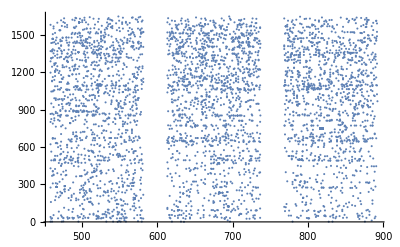

```mathematica
(* distribution of all potential CPs *)
ListPlot[Flatten[globedCPs,1]]
```

```mathematica
(* groupedCPs are used for matching *)
Dimensions[groupedCPs=Map[Flatten[#,2]&,Transpose[Values[brightestAnnotated[[All,All,All,All,All,"icFullFrame"]]],{1,3,2}],{2}]
] (* {29,82} *)
```

{29,82}

```mathematica
(* groupedCPsAnnotated are used to re-associoate metadata with CPs after matching *)
Dimensions[groupedCPsAnnotated=Map[Flatten[#,2]&,Transpose[Values[brightestAnnotated[[All,All,All,All,All]]],{1,3,2}],{2}]
] (* {29,82} *)
```

{29,82}

```mathematica
groupedCPs[[1,1,1]]
```

{858.5,1355.5}

```mathematica
groupedCPsAnnotated[[1,1,1]]
```

<|Count→1,IntensityCentroid→{1355.5,35.5},TotalIntensity→0.00212101,index→{1,1,1,1,Key[5]},color→1,frame→1,icFullFrame→{858.5,1355.5},icFFPlot→{1174.5,1355.5},icPlot→{1355.5,10403.5},rawLoc→{1355.5,348.5},fname→JNCE_2016129_00C00164_V01.IMG.gz|>

```mathematica
(* used to re-associate annotations with CP values *) 
findComponentAnnotation[fileNumber_,segmentNumber_,icFullFramePoint_List]:=Select[groupedCPsAnnotated[[fileNumber,segmentNumber]],#["icFullFrame"]==icFullFramePoint&][[1]] (* Select should only find one Associoation.  [[1]] to return the Associoation, not the list. *)
```

```mathematica
(* All potential CPs from each file *)
Table[
ListPlot[
spots=Table[Flatten[Values[brightestAnnotated[[f,c,All,All,All,"icFFPlot"]]],2],{c,1,3}]
,AspectRatio->1/2,(*PlotRange->{{0,1214},{0,1648}},*)ImageSize->Full,PlotStyle->{Red,Green,Blue}
,PlotMarkers->{"O","o","+",▸,"×",▾,▴}
,PlotLabel-> "File " <>  ToString[f] <> "  " <>fileList[[f]]
]
,{f,1,0+1Length[brightestAnnotated]}
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Looking for more CPs near bottom of above chart which corresponds to left side of raw data.
Looking at inspection images:
File 1  JNCE_ 2016129_ 00C00164 appears to have red/green match near middle, but green CP isn’t being detected because it is dimmer than all the green noise earlier in the image.
JNCE_2016026_00C00058 red/g/g near middle
JNCE_ 2016040_ 00C00095 near top has red/green pari
JNCE_ 2016040_ 00C00096 near top
 JNCE_ 2016040_ 00C00097 near top
 JNCE_ 2016040_ 00C00106 near middle

```mathematica
imgToInspectionImageFilename
```

{(.IMG.gz~~EndOfString)|(.IMG~~EndOfString)|(-raw.png~~EndOfString)→_inspectionImage.png}

```mathematica
exportDocsDirectory
```

/Users/bswift

```mathematica
Export[FileNameJoin[{exportDocsDirectory,"Juno24InspectionImageList.txt"}],Map[StringReplace[#,imgToInspectionImageFilename]&,fileList]]
```

/Users/bswift/Juno24InspectionImageList.txt

```mathematica
inspectionFileList=MapIndexed[{#2[[1]],StringReplace[#,imgToInspectionImageFilename]}&,fileList]
```

{{1,/Users/bswift/Downloads/ORBIT_00/JNCE_2016129_00C00164_V01_inspectionImage.png},{2,/Users/bswift/Downloads/ORBIT_00/JNCE_2016129_00C00165_V01_inspectionImage.png},{3,/Users/bswift/Downloads/ORBIT_00/JNCE_2016130_00C00171_V01_inspectionImage.png},{4,/Users/bswift/Downloads/ORBIT_00/JNCE_2016131_00C00180_V01_inspectionImage.png},{5,/Users/bswift/Downloads/ORBIT_00/JNCE_2016164_00C00195_V01_inspectionImage.png},{6,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00058_V01_inspectionImage.png},{7,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00059_V01_inspectionImage.png},{8,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00060_V01_inspectionImage.png},{9,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00061_V01_inspectionImage.png},{10,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00062_V01_inspectionImage.png},{11,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00063_V01_inspectionImage.png},{12,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00070_V01_inspectionImage.png},{13,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00071_V01_inspectionImage.png},{14,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00072_V01_inspectionImage.png},{15,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00073_V01_inspectionImage.png},{16,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00074_V01_inspectionImage.png},{17,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00080_V01_inspectionImage.png},{18,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00081_V01_inspectionImage.png},{19,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00082_V01_inspectionImage.png},{20,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00083_V01_inspectionImage.png},{21,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016040_00C00094_V01_inspectionImage.png},{22,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016040_00C00095_V01_inspectionImage.png},{23,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016040_00C00096_V01_inspectionImage.png},{24,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016040_00C00097_V01_inspectionImage.png},{25,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016040_00C00098_V01_inspectionImage.png},{26,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016040_00C00099_V01_inspectionImage.png},{27,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016040_00C00105_V01_inspectionImage.png},{28,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016040_00C00106_V01_inspectionImage.png},{29,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016040_00C00107_V01_inspectionImage.png}}

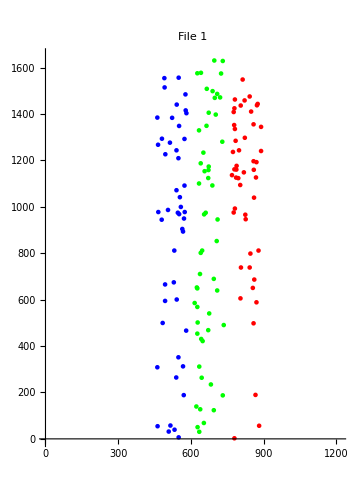

```mathematica
(* Distribution of point sources on CCD *)
Table[
ListPlot[
spots=Table[Flatten[Values[brightestAnnotated[[f,c,All,All,All,"icFullFrame"]]],2],{c,1,3}]
,AspectRatio->Automatic,PlotRange->{{0,1214},{0,1648}},ImageSize->Medium,PlotStyle->{Red,Green,Blue}
,PlotLabel-> "File " <>  ToString[f]
]
,{f,1,1+0Length[brightestAnnotated]}
]
```

```mathematica
(* all the brightest points from each file in framelet assembeled locations *)
(*Table[
ListPlot[
spots=Table[Flatten[Values[brightestAnnotated[[f,c,All,All,All,"icPlot"]]],2],{c,1,3}]
,AspectRatio->2,PlotRange->{{0,1648},{0,83 128}},ImageSize->Medium,PlotStyle->{Red,Green,Blue}
,PlotLabel-> "File " <>  ToString[f]
]
,{f,1,Length[brightestAnnotated]}
]*)
```

### Control Point Match Prep

```mathematica
?forwardTransform
```

Global`forwardTransform

forwardTransform[{xN_,yN_}]:=Module[{λ,ϕ,solution,s=0,e=0},solution=FindRoot[lensTransformNormalizedBakedCNumeric[{λ,ϕ}]=={xN,yN},{{λ,xN-0.1,xN+0.1},{ϕ,yN-0.1,yN+0.1}}];{λ,ϕ}/.solution]

```mathematica
(*Export["/Users/bswift/Pictures/Jupiter/Junocam/groupedCPs.mx",groupedCPs]*)
```

```mathematica
(*groupedCPs=Import["/Users/bswift/Pictures/Jupiter/Junocam/groupedCPs.mx"];*)
```

```mathematica
(* forwardTransformMem with memoization. Uses forwardTransform from Juno28 *)
ClearAll[forwardTransformMem];
mem:forwardTransformMem[{xPix_,yPix_}]:=mem=forwardTransform[normalizeXY[{xPix,yPix}]]
```

```mathematica
deNormalizeXnYn[{0,ccdAR}]
```

{607,1648}

```mathematica
filterRanges
```

{{766,894},{611,739},{456,584}}

```mathematica
p1=deNormalizeXnYn[forwardTransform[normalizeXY[{894,0 1648}]]]
```

{911.074,28.8216}

```mathematica
p2=deNormalizeXnYn[forwardTransform[normalizeXY[{895,0 1648}]]]
```

{912.118,28.9076}

```mathematica
p2-p1 (* forward transformed dx,dy pixel shift for one dx pixel shift at extreme filter corner *)
```

{1.04404,0.0860311}

```mathematica
Dimensions[Flatten[groupedCPs,2]]
```

{4379,2}

```mathematica
(* Memoize forward transformed CPs *)
AbsoluteTiming[forwardTransformedControlPoints=Map[forwardTransformMem,Flatten[groupedCPs,2]];] (* 52.7 , .0015 second run
59.7 with rotation
181.7 with rotation and orbit0 CPs 
183 29 files 2647 CPs.  .0033 sec second run
1.0 sec 29 files 264 CPs with FindRoot based forwardTransform. 0.0034 second run*)
```

{1.3498,Null}

```mathematica
forwardTransformedControlPoints[[{1,-1}]]
```

{{0.441328,0.891054},{0.205629,0.0688676}}

```mathematica
(* Coarse estimate used in early iteration based on observed shift in raw data of 115 pix *) expectedXShift =First[forwardTransform[normalizeXY[ccdSize/2+{115,0}]]-forwardTransform[normalizeXY[ccdSize/2]]]
```

0.199681

```mathematica
expectedXShift 607
```

121.207

```mathematica
expectedXShift=0.1998710493421405 (* 3/2/2018 *)
```

0.199871

```mathematica
expectedXShift 607
```

121.322

```mathematica
expectedXShift
```

0.199871

```mathematica
deNormalizeXnYn[{expectedXShift,0}]-deNormalizeXnYn[{0,0}]
```

{121.322,0}

```mathematica
ClearAll[λϕDistToPix];
(* approximate conversion of a distance in λϕ to pixels. Assumes distance is segment through center of CCD *)
λϕDistToPix[{λ_,ϕ_}]:=deNormalizeXnYn[2λϕToXY00[{λ,ϕ}/2]]-deNormalizeXnYn[{0,0}]
```

```mathematica
λϕDistToPix[{expectedXShift,0}]
```

{121.386,1.13687×10^-13}

```mathematica
(* Using different Wraps for different clusters not automated *)
(* 6 derrived from cluster 2 *)
```

```mathematica
expectedWrapXShift2=First[forwardTransform[normalizeXY[ccdSize/2+{6,0}]]-forwardTransform[normalizeXY[ccdSize/2]]]
```

0.0104396

```mathematica
(* For JNCE_2016040* data takes based on JNCE_2016040_00C00107 *)
(* -13 (derrived from cluster 3) works for cluster 3 and 1 *)
expectedWrapXShift13=First[forwardTransform[normalizeXY[ccdSize/2+{-13,0}]]-forwardTransform[normalizeXY[ccdSize/2]]]
```

-0.0226215

```mathematica
yawRateClusterIndicies
```

{{1,2,3,4,5},{6,7,8,9,10,11,12,13,14,15,16,17,18,19,20},{21,22,23,24,25,26,27,28,29}}

```mathematica
expectedWrapXShift=Flatten[MapIndexed[{expectedWrapXShift13,expectedWrapXShift2,expectedWrapXShift13}[[#2[[1]]]]&,yawRateClusterIndicies,{2}]]  (* hackyness to get wrap shifts for each cluster *)
```

{-0.0226215,-0.0226215,-0.0226215,-0.0226215,-0.0226215,0.0104396,0.0104396,0.0104396,0.0104396,0.0104396,0.0104396,0.0104396,0.0104396,0.0104396,0.0104396,0.0104396,0.0104396,0.0104396,0.0104396,0.0104396,-0.0226215,-0.0226215,-0.0226215,-0.0226215,-0.0226215,-0.0226215,-0.0226215,-0.0226215,-0.0226215}

```mathematica
Length[expectedWrapXShift]
```

29

```mathematica
Map[λϕDistToPix[{#,0}]&,expectedWrapXShift]
```

{{-13.7314,1.13687×10^-13},{-13.7314,1.13687×10^-13},{-13.7314,1.13687×10^-13},{-13.7314,1.13687×10^-13},{-13.7314,1.13687×10^-13},{6.33687,1.13687×10^-13},{6.33687,1.13687×10^-13},{6.33687,1.13687×10^-13},{6.33687,1.13687×10^-13},{6.33687,1.13687×10^-13},{6.33687,1.13687×10^-13},{6.33687,1.13687×10^-13},{6.33687,1.13687×10^-13},{6.33687,1.13687×10^-13},{6.33687,1.13687×10^-13},{6.33687,1.13687×10^-13},{6.33687,1.13687×10^-13},{6.33687,1.13687×10^-13},{6.33687,1.13687×10^-13},{6.33687,1.13687×10^-13},{-13.7314,1.13687×10^-13},{-13.7314,1.13687×10^-13},{-13.7314,1.13687×10^-13},{-13.7314,1.13687×10^-13},{-13.7314,1.13687×10^-13},{-13.7314,1.13687×10^-13},{-13.7314,1.13687×10^-13},{-13.7314,1.13687×10^-13},{-13.7314,1.13687×10^-13}}

```mathematica
expectedWrapXShift 607
```

{-13.7313,-13.7313,-13.7313,-13.7313,-13.7313,6.33686,6.33686,6.33686,6.33686,6.33686,6.33686,6.33686,6.33686,6.33686,6.33686,6.33686,6.33686,6.33686,6.33686,6.33686,-13.7313,-13.7313,-13.7313,-13.7313,-13.7313,-13.7313,-13.7313,-13.7313,-13.7313}

```mathematica
searchRadiusλ= First[forwardTransform[normalizeXY[ccdSize/2+{2.0,0}]]-forwardTransform[normalizeXY[ccdSize/2]]] 
(* With RGB group filter - doubling radius picked up one control point in file 5 that is bad match outlier in offsets. 
Reduced from 2.3 to 2.0 to kill outlier from file4 fa 3 linking a red to blue w/o intermediate green. This showed up after implementing dynamic flat clip.
This apparently came back, so further tighten searchRadiusExpansionFactor from 0.5 to 0.25
*)
```

0.00347999

```mathematica
searchRadiusExpansionFactor=0.25
```

0.25

```mathematica
searchRadiusExpansionFactor=0.0  (* reduced to 0 to avoid bad CP picked up withe new parameters in File 4 frame 26,29 {4,3,26,1} *)
```

0.

```mathematica
λϕDistToPix[{searchRadiusλ,0}]
```

{2.11236,1.13687×10^-13}

### Match Control Points between frames

```mathematica
(* Should update this to use per-file forward transform *)
```

```mathematica
matchCPs[imagesPaired_,aFrame_,bFrame_,framesApart_]:=Block[
{expectedShift={expectedXShift framesApart,0},searchRadius=searchRadiusλ+ searchRadiusExpansionFactor searchRadiusλ(framesApart-1),
shifted,matched,uncleanPairs,matchedShiftedCPPairs,matchedUNshiftedCPPairs,distances,deltas},

(* Special Case for wrap around CPs.  Value determine by using FindGeometricTransform between last and first bwfullFrames ([[82]] and [[1]] *)
If[Apply[EuclideanDistance,imagesPaired]>4,
expectedShift={expectedWrapXShift[[fileNumber]],0}+{expectedXShift (framesApart-1),0};
(*searchRadius=2.8;*)
(*Print[imagesPaired," Expected Shift = ",expectedShift," searchRadius = ",searchRadius];*)
];
(*shifted=Map[#+expectedShift&,bFrame];*)
If[aFrame=={} || bFrame=={}
,uncleanPairs={{{},{}}};
,
matched=Nearest[bFrame,aFrame,{1,searchRadius}
,DistanceFunction->(EuclideanDistance[forwardTransformMem[#1],forwardTransformMem[#2]+expectedShift]&)
];
uncleanPairs=MapThread[{#1,#2}&,{aFrame,matched}];
];

matchedUNshiftedCPPairs =Map[{#[[1]],#[[2,1]]}&,Select[uncleanPairs,#[[2]]≠{}&]];
matchedShiftedCPPairs=Map[{#[[1]],#[[2]]+λϕDistToPix[expectedShift]}&,matchedUNshiftedCPPairs,{1}];
distances=Map[EuclideanDistance[#[[1]],#[[2]]]&,matchedShiftedCPPairs];
deltas=Map[Subtract[#[[1]],#[[2]]]&,matchedUNshiftedCPPairs];
<|"matchedUNshiftedCPPairs"->matchedUNshiftedCPPairs,
"matchedShiftedCPPairs"->matchedShiftedCPPairs,
"deltas"->deltas,"distances"->distances
,"matched"-> matched
,"uncleanPairs" -> uncleanPairs|>
] (* cmr from rotated images, need to shift in x direction *)
```

```mathematica
(* new, looping over files of un-merged CPs *)
Clear[cpObj,distances,deltas,matchedShiftedCPPairs,matchedUnFilteredUnShiftedCPPairs,matchedUNshiftedCPPairs,matchedUnFilteredUnShiftedCPPairsimagesPaired]
(*framesAhead=4*)
Do[
controlPoints=groupedCPs[[fileNumber]];
Do[
imagesPaired[framesAhead]=MapThread[{#1,#2}&,{Range[Length[controlPoints]],RotateLeft[Range[Length[controlPoints]],framesAhead]}];
cpObj[framesAhead]=Merge[MapThread[
matchCPs[#1,#2,#3,framesAhead]&
,{imagesPaired[framesAhead],controlPoints,RotateLeft[controlPoints,framesAhead]}]
,Identity];
distances[fileNumber,framesAhead]=cpObj[framesAhead]["distances"];
deltas[fileNumber,framesAhead]=cpObj[framesAhead]["deltas"];
matchedShiftedCPPairs[fileNumber,framesAhead]=cpObj[framesAhead]["matchedShiftedCPPairs"];
matchedUnFilteredUnShiftedCPPairs[fileNumber,framesAhead]=cpObj[framesAhead]["matchedUNshiftedCPPairs"];
,{framesAhead,1,4}
];
,{fileNumber,1,Length[groupedCPs]}
];
```

#### Filter to keep CPs that have at least one Blue, Green and Red components

```mathematica
Dimensions[matchedUnFilteredUnShiftedCPPairs[1,1]]
```

{82}

```mathematica
(* R,G,B Color Ranges *)
Table[{toFullFrame[c,{0,0}][[1]],toFullFrame[c,{0,128}][[1]]},{c,1,3}] // Column
```

{894,766}
{739,611}
{584,456}

```mathematica
ClearAll["ptIs*"];ptIs[c_,pt_]:= IntervalMemberQ[Interval[{toFullFrame[c,{0,0}][[1]],toFullFrame[c,{0,128}][[1]]}],pt[[1]]](*|| pt[[2]]>1200*)  ;  (* >1200 hack to disable filtering for CPs with y>1200, otherwise there are no matches above 1200 *)
ptIsRed[pt_]:=ptIs[1,pt];
ptIsGreen[pt_]:=ptIs[2,pt];
ptIsBlue[pt_]:=ptIs[3,pt]
```

```mathematica
(*ClearAll["ptIs*"];*)ptIsH[c_,pt_]:= IntervalMemberQ[Interval[{toFullFrame[c,{0,0}][[1]],toFullFrame[c,{0,128}][[1]]}],pt[[1]]]|| pt[[2]]<450  ;  (* <450 hack to disable filtering for CPs with y<450, otherwise there are no matches above 1200 *)
ptIsRedH[pt_]:=ptIsH[1,pt];
ptIsGreenH[pt_]:=ptIsH[2,pt];
ptIsBlueH[pt_]:=ptIsH[3,pt]
```

```mathematica
Clear[matchedUNshiftedCPPairsByFile];
Do[
fileCPPairs=
Table[
matchedUnFilteredUnShiftedCPPairs[fileNumber,framesAhead]
,{framesAhead,1,4}
];

blueCPPairs=Map[Select[#, ptIsBlueH[#[[2]] ]|| ptIsBlueH[#[[1]] ]
&]&
,fileCPPairs,{-4}
];

redGreenCPs=DeleteDuplicates[Flatten[
Map[Select[#, ptIsGreenH[#[[2]] ] && ptIsRedH[#[[1]] ]
&]&
,fileCPPairs,{-4}
]
,3]];

(* Blue and paired CP where a member of the pair is is also a member of a Red Green pair. These should be Blue control points that are matched with both Red and Green control points. *)blueLinkedRedGreenCPs=DeleteDuplicates[Flatten[
Map[Select[#, MemberQ[redGreenCPs,#[[2]] ]|| MemberQ[redGreenCPs,#[[1]] ]
&]&
,blueCPPairs,{-4}
]
,3] ];

(* Expand to any CPs that link to one of the above. ( for RR, GG, BB pairs ) *) linkedLinkedCPs=DeleteDuplicates[Flatten[Map[Select[#, MemberQ[blueLinkedRedGreenCPs,#[[2]] ]|| MemberQ[blueLinkedRedGreenCPs,#[[1]] ]
&]&
,fileCPPairs,{-4}
],3] ];

fileFilteredPairs=Map[Select[#, MemberQ[linkedLinkedCPs,#[[2]] ]|| MemberQ[linkedLinkedCPs,#[[1]] ]
&]&
,fileCPPairs,{-4}
];

(* update with filters pairs *)
Do[
matchedUNshiftedCPPairsByFile[fileNumber,framesAhead]=fileFilteredPairs[[framesAhead]]
,{framesAhead,1,4}
];

,{fileNumber,1,Length[groupedCPs]}
];
```

#### Annotated by-file deltas with wraps

```mathematica
(* Trimmed down gen9Deltas structure, include wrap-around CPs *)
genXDeltasWrap:=Module[
{
},
(* Structure of returned elements:
 {{},{}} -> {{}, {icFullFrame,icFullFrame2}, {}, {fileNumber,fa,segment,cp_in_segment}, <|point 1 component annotations|>, <|point 2 comoponent annotations|> } 
  *)
Table[
Flatten[
MapIndexed[
{{},{}}-> (* Annotations *)
{ {} (* {dx,dy} unshifted *)
,{#1[[1]],#1[[2]]} (* full frame locations *)
,Join[{fileNumber,fa},#2] (* extended index: fileNumber,frames Ahead, "left" segment #, CP in segment *)
,{} (* {dx,dy} Shifted *)
,findComponentAnnotation[fileNumber,#2[[1]],#1[[1]] ]
,findComponentAnnotation[fileNumber,Mod[#2[[1]]+fa,82,1],#1[[2]] ]
}
&,matchedUNshiftedCPPairsByFile[fileNumber,fa][[1;;(*-fa*)-1]]
,{2}]
,1]
,{fileNumber,Flatten[modelClusterRanges]}
,{fa,1,4}
]
]
```

#### ReCluster CPs based on yawRate instead of file

```mathematica
tightYawRateClusters
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29}}

```mathematica
Dimensions[matchedUNshiftedCPPairsByFile[1,1]]
```

{82}

```mathematica
clusterIndicies=Range[1,Length[tightYawRateClusters]]
```

{1}

```mathematica
ClearAll[matchedUNshiftedCPPairsByCluster];
Do[
Do[
matchedUNshiftedCPPairsByCluster[clusterNumber,framesAhead]=
Map[Flatten[#,1]&,
Transpose[
Table[matchedUNshiftedCPPairsByFile[fileNumber,framesAhead]
,{fileNumber,tightYawRateClusters[[clusterNumber]]}
]
]
]
,{clusterNumber,clusterIndicies}
]
,{framesAhead,1,4}
];
```

```mathematica
(* uncommnet for each file to be it's own cluster *)
(*clusterIndicies=Flatten[tightYawRateClusters] 
Do[
matchedUNshiftedCPPairsByCluster[fileNumber,framesAhead]=matchedUNshiftedCPPairsByFile[fileNumber,framesAhead]
,{framesAhead,1,4},{fileNumber,clusterIndicies}
]*)
```

```mathematica
Dimensions[matchedUNshiftedCPPairsByCluster[1,1]]
```

{82}

```mathematica
matchedUNshiftedCPPairs=matchedUNshiftedCPPairsByCluster
```

matchedUNshiftedCPPairsByCluster

#### CPs Distribution and Edge CPs

```mathematica
clusterIndicies
```

{1}

```mathematica
Clear[allMatchedCPs];
allMatchedCPs=Table[matchedUNshiftedCPPairsByCluster[fileNumber,framesAhead]
,{fileNumber,clusterIndicies},{framesAhead,1,4}];
```

```mathematica
Dimensions[allMatchedCPs]
```

{1,4,82}

```mathematica
Dimensions[Transpose[allMatchedCPs,{3,2,1}]]
```

{82,4,1}

```mathematica
Dimensions[
allCPsbyFA=Transpose[Map[Flatten[#,1]&,Transpose[allMatchedCPs,{3,2,1}],{2}]] (* merge clusters *)
]
```

{4,82}

```mathematica
Table[Dimensions[DeleteDuplicates[Flatten[allCPsbyFA[[fa]],1]]],{fa,1,4}]
```

{{242,2,2},{171,2,2},{102,2,2},{4,2,2}}

```mathematica
Table[Dimensions[Flatten[allCPsbyFA[[fa]],1]],{fa,1,4}]
```

{{242,2,2},{171,2,2},{102,2,2},{4,2,2}}

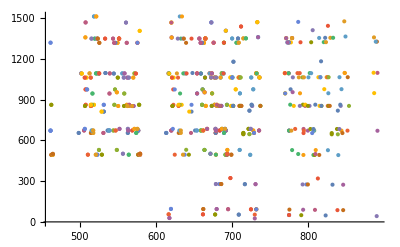
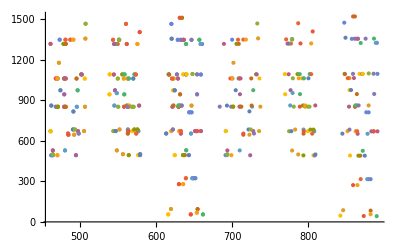
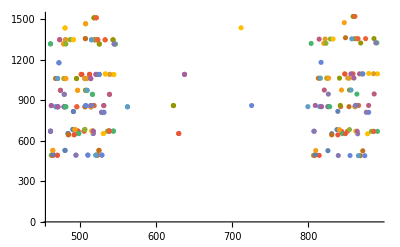
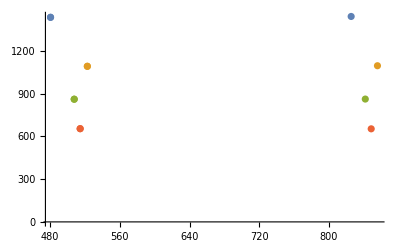

```mathematica
Table[ListPlot[Flatten[allCPsbyFA[[fa]],1]],{fa,1,4}]
```

```mathematica
Table[Dimensions[Flatten[allCPsbyFA[[fa]],1]],{fa,1,4}]
```

{{242,2,2},{171,2,2},{102,2,2},{4,2,2}}

```mathematica
Table[Dimensions[Flatten[allCPsbyFA[[fa]],2]],{fa,1,4}]
```

{{484,2},{342,2},{204,2},{8,2}}

```mathematica
Table[Dimensions[Flatten[allCPsbyFA[[fa]],2][[All,2]]],{fa,1,4}]
```

{{484},{342},{204},{8}}

```mathematica
filterRanges=Table[{toFullFrame[c,{0,128}]⟦1⟧,toFullFrame[c,{0,0}]⟦1⟧},{c,1,3}]
```

{{766,894},{611,739},{456,584}}

```mathematica
interiorRanges=Map[Plus[{13,-13},#]&,filterRanges]
```

{{779,881},{624,726},{469,571}}

```mathematica
filterEdgesInterval=Interval@@Map[Sort,Transpose[{Flatten[filterRanges],Flatten[interiorRanges]}]]
```

Interval[{456,469},{571,584},{611,624},{726,739},{766,779},{881,894}]

```mathematica
filterEdgeCPs=Select[DeleteDuplicates[Flatten[allMatchedCPs,4]]
,IntervalMemberQ[filterEdgesInterval,#[[1]]]&];
```

```mathematica
Dimensions[filterEdgeCPs]
```

{85,2}

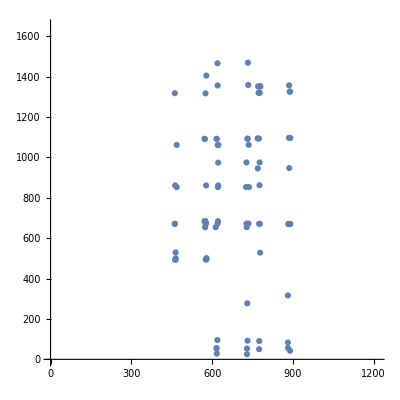

```mathematica
ListPlot[filterEdgeCPs
,AspectRatio->1,PlotRange->Transpose[{{0,0},ccdSize}]
]
```

#### Point source matched to create CP pairs from each file

```mathematica
(* Overlay matchedUNshiftedCPPairs on icFFPlot to visualize which control points are matched
*)
 Table[
Table[
Show[
ListPlot[
spots=Table[Flatten[Values[brightestAnnotated[[f,c,All,All,All,"icFFPlot"]]],2],{c,1,3}];
Map[
Tooltip[#,ToString[Map[fmtNum[#]& , #,{-1}]]]&  (* should be tagging with ifFF frame location, not plot location *)
,spots,{2}]
,AspectRatio->1/2,(*PlotRange->{{0,1214},{0,1648}},*)ImageSize->Full,PlotStyle->{Red,Green,Blue}
,PlotMarkers->{"O","o","+",▸,"×",▾,▴}
,PlotLabel-> "File " <>  ToString[f]<> " fa " <> ToString[fa] <> "  "  <> fileList[[f]]
]
,ListPlot[
Transpose[  (* Transpose list of CP pairs into two lists, a right and left CP list *)
Flatten[
 MapThread[Function[{cpPairList,framePair},
If[cpPairList≠{}
,Map[{toHPlot[framePair[[1]],#[[1]]],toHPlot[framePair[[2]],#[[2]]]}&,cpPairList]
,{}
]
],{matchedUNshiftedCPPairsByFile[f,fa],imagesPaired[fa]}]
,1
]
]
,PlotMarkers->{"_","|","⊔","⊓","∆","|","▯","□","⬚","∇"}
]
]
,{fa,1,3}
] // Column
,{f,1,0+Length[brightestAnnotated]}
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-}

#### Matching Metrics

```mathematica
matchedFileAheadFileNumber=Table[Total[Map[Length,matchedUNshiftedCPPairsByCluster[fileNumber,fa]]],{fa,1,4},{fileNumber,clusterIndicies}]  (*
235,122,59,1 old all and #TotalIntensity > 3 dnStep
201,100,47,0 old #TotalIntensity > 4 dnStep
{185,94,41,0} #TotalIntensity > 5 dnStep
{173,85,33,0} TotalIntensity > 6 dnStep
{522,387,254,13} new #TotalIntensity > 3 dnStep
{231,143,61,0} new #TotalIntensity > 5 dnStep
{231,145,64,0} new #TotalIntensity > 5 dnStep after multiple refinement iterations on expectedXShift
{264,165,73,0} new #TotalIntensity > 4 dnStep
{238,151,72,0} new #TotalIntensity > 5 dnStep colorScale={0,0,1.25}
{275,176,83,0} new #TotalIntensity > 4 dnStep colorScale={0,0,1.25}
{275,177,83,0} new #TotalIntensity > 4 dnStep , colorScale={0,0,1.25} , cpShiftTDI 2.5
{275,177,82,0} new #TotalIntensity > 4 dnStep , colorScale={0,0,1.25} , cpShiftTDI 2.5, new Lens Params
{267,171,74,1} new per-file CP selection method using 20 brightest per file
{62,37,16,0} Orbit0 20 brightest
{68,41,17,0} Orbit0 30 brightest (picked up one or two outliers)
{354,226,104,1} With cruise and Oribt0 and 30 brightest
{237,169,100,1} Filtered to only keep pairs that are part of RGB group
{237,170,101,1} With doubled search radius
{6,5,4,0} from radiation trending images
{5,4,3,0} after changes to flat generation
{7,7,8,0} from additional 4 x77 ORBIT_00 files
{27,20,13,0} from Cruise Phase 2015 1/2 spin files
{234,167,99,1}
{100,72,43,1} closeSpinFileList
{82,56,34,3}  -9;;-1
{240,167,101,6} 29 files , -13 wrap
{230,160,97,5} tightYawRateClusters (drops one file)
{95,65,42,5} uniformSpatialDebiasCPs 150 samples
{32,20,15,5} radial 20
{37,24,17,6} radial 20 all wrap
{119,85,50,4} spatial 250 2.0 searchRadius
{65,45,26,4} radial 30 with central 1/3 removed
{95,67,41,4} balanced debias
{123,84,49,6} balanced debias plus central
{163,109,59,6} balanced debias plus "central" - bottom decimation
{157,107,57,3} 2/20/2018 pre-tightening to remove outlier in cluster 1 file 4
{170,115,61,4} 3/2/2018 before removeal of spatial debias
{268,187,107,4} 3/2/2018 after removal of spatial debias
{233,165,98,4} 3/13/2018 after excluding points within 1.51 of filter edge
{242,171,102,4} 3/22/2018 after adding file5
{233,165,98,4} 3/25/2018 after removing file5
{233,165,99,4} 3/29/2018 after flipped Y and picked up file 4 outlier CP
 *)
```

{{242},{171},{102},{4}}

```mathematica
{{31,117,85},{23,82,60},{13,52,33},{0,1,3}} (* 3/25/2018 *)
```

{{31,117,85},{23,82,60},{13,52,33},{0,1,3}}

```mathematica
Map[Total,matchedFileAheadFileNumber]
```

{242,171,102,4}

```mathematica
(* After matching done, can Merge CPs from different datatakes, for compatability with old way. *)
Do[
matchedUNshiftedCPPairs[fa]=
Map[Flatten[#,1]&,Transpose[
Table[matchedUNshiftedCPPairs[fileNumber,fa],{fileNumber,clusterIndicies}]
]];
matchedShiftedCPPairs[fa]=
Map[Flatten[#,1]&,Transpose[
Table[matchedShiftedCPPairs[fileNumber,fa],{fileNumber,clusterIndicies}]
]]
,{fa,1,4}
];
```

```mathematica
matchedUNshiftedCPPairs[1] // Dimensions
```

{82}

```mathematica
Table[
Map[Length,matchedUNshiftedCPPairs[fa]]
,{fa,1,4}
] // Column
```

{1,3,2,4,1,4,7,6,4,3,5,8,3,4,5,5,1,1,3,3,1,1,4,5,4,2,2,2,0,1,3,2,1,1,5,3,1,2,3,3,1,1,3,7,5,2,1,4,6,2,2,5,4,2,1,4,5,2,3,7,6,4,2,4,2,5,1,2,0,4,0,4,3,3,2,0,2,1,2,4,4,1}
{0,2,3,3,3,0,5,6,3,5,2,5,4,3,5,1,2,0,3,1,2,1,3,2,2,2,2,0,0,1,0,2,1,0,3,4,0,1,4,0,0,3,2,5,1,1,2,3,0,2,2,3,3,2,2,3,2,2,4,4,3,2,1,4,2,1,2,3,0,1,2,4,2,1,2,2,1,0,1,3,1,1}
{1,2,1,5,1,1,4,2,1,3,1,2,2,5,1,2,0,1,1,1,1,0,1,1,1,2,0,0,0,0,1,1,0,0,3,1,0,1,1,0,0,3,1,1,0,0,1,0,1,0,1,3,0,1,2,1,1,2,3,3,1,0,0,4,0,2,1,2,0,3,0,2,1,0,2,1,1,0,1,1,3,2}
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,2,1}

Generate Model

## Modeling Prep

### Select and weight Control Points

Intent of weighting statistics for control points is an attempt to mitigate bias from the non-uniform distribution of control points in the across-track direction. Spatial weighting balances contributions by control points in left, center and right thirds of CCD. Additionally, weighting balances contributions by each filter pairing combination.

```mathematica
(* Determine weighting for CPs. Top level is files, 2nd level is Frames Ahead, segments have been flattened out and wrap-around CPs are included.
*)
normalizedCPsByFA=Map[Map[normalizeXY,#⟦2,2⟧]&,genXDeltasWrap,{3}] ;
(* THIS ONE is currnet.
Pulls CPs from genXDeltasWrap.  Note that while name is "ByFA" indicating grouping by "frames ahead", these are grouped by file.
Extracting and only using CP locations is historic. Should just keep and use fully annotated genXDeltasWrap entries. Could then use color annotation rather than identifiying color by location.
*)
```

```mathematica
normalizedCPsByFA//Dimensions
```

{29,4}

```mathematica
genXDeltasWrap⟦1,1,1⟧
```

{{},{}}→{{},{{826.04,946.5},{710.046,945.5}},{1,1,4,1},{},<|Count→2,IntensityCentroid→{946.5,67.9605},TotalIntensity→0.0141228,index→{1,1,4,1,Key[5]},color→1,frame→4,icFullFrame→{826.04,946.5},icFFPlot→{2090.04,946.5},icPlot→{946.5,10052.},rawLoc→{946.5,1468.04},fname→JNCE_2016129_00C00164_V01.IMG.gz|>,<|Count→2,IntensityCentroid→{945.5,28.9535},TotalIntensity→0.0151057,index→{1,2,5,1,Key[5]},color→2,frame→5,icFullFrame→{710.046,945.5},icFFPlot→{2290.05,945.5},icPlot→{945.5,9884.95},rawLoc→{945.5,1763.05},fname→JNCE_2016129_00C00164_V01.IMG.gz|>}

```mathematica
Map[Length[Flatten[#,1]]&,normalizedCPsByFA]
```

{16,15,18,18,19,28,25,10,12,12,19,19,20,16,25,19,9,12,10,16,16,21,26,22,15,22,17,17,25}

```mathematica
sameFilter[{p1_,p2_}]:=(ptIsRed[p1]&&ptIsRed[p2])||
(ptIsGreen[p1]&&ptIsGreen[p2])||(ptIsBlue[p1]&&ptIsBlue[p2])
```

```mathematica
?ptIsGreen
```

Global`ptIsGreen

ptIsGreen[pt_]:=ptIs[2,pt]

```mathematica
sameFilterNormalized[{p1_,p2_}]:=(ptIsRed[deNormalizeXnYn[p1]]&&ptIsRed[deNormalizeXnYn[p2]])||
(ptIsGreen[deNormalizeXnYn[p1]]&&ptIsGreen[deNormalizeXnYn[p2]])||(ptIsBlue[deNormalizeXnYn[p1]]&&ptIsBlue[deNormalizeXnYn[p2]])
```

```mathematica
filterRanges
```

{{766,894},{611,739},{456,584}}

```mathematica
Dimensions[Flatten[normalizedCPsByFA,3]]
```

{1038,2}

```mathematica
{1000,2}(* 3/28/2018 includes wraps, but not file 5 *)
```

{1000,2}

```mathematica
{1038,2} (* 3/23/2018 includes wraps *)
```

{1038,2}

```mathematica
Dimensions[Flatten[normalizedCPsByFA,2]]
```

{519,2,2}

```mathematica
{500,2,2}(* 3/28/2018 includes wraps, but not file 5 *)
```

{500,2,2}

```mathematica
{519,2,2} (* 3/23/2018 includes wraps *)
```

{519,2,2}

```mathematica
Dimensions[DeleteDuplicates[Flatten[normalizedCPsByFA,3]]]
```

{495,2}

```mathematica
{477,2}(* 3/28/2018 includes wraps, but not file 5 *)
```

{477,2}

```mathematica
{495,2}(* 3/23/2018 includes wraps *)
```

{495,2}

```mathematica
Show[
ListPlot[Map[deNormalizeXnYn,DeleteDuplicates[Flatten[normalizedCPsByFA,3]]]
,ImageSize->Large
,AspectRatio->1
,PlotRange->{MinMax[Flatten[filterRanges]]+20{-1,1},{0,ccdSize[[2]]}}
,PlotLabel->"Distribution of Control Points over Filters"]
,
ListLinePlot[Join[filterPlotLines,balancePlotLines]]
]
```

-Graphics-

```mathematica
filterRanges
```

{{766,894},{611,739},{456,584}}

```mathematica
nearFilterEdgeF=Nearest[Map[First,Map[normalizeXY[{#,0}]&,Flatten[filterRanges]]]]
```

NearestFunction[{1, <>}]

```mathematica
edgePoints=Select[DeleteDuplicates[Flatten[normalizedCPsByFA,3]]
,EuclideanDistance[#[[1]],nearFilterEdgeF[#[[1]]]]<15.5/607&
];
```

```mathematica
Show[
ListPlot[Map[ deNormalizeXnYn,edgePoints ],ImageSize->Large
,AspectRatio->1
,PlotRange->{MinMax[Flatten[filterRanges]]+20{-1,1},{0,ccdSize[[2]]}}
,PlotLabel->"Control Points Near filter Edges\nCandidates for two images of point in same filter."
]
,
ListLinePlot[Join[filterPlotLines,balancePlotLines]]
]
```

-Graphics-

```mathematica
(* vertical 1/2 regions *)
Clear[v];
cpWeight[{pt1_,pt2_}]:=
Which[pt1[[2]]>0,v1, (* top *)
True,v2 (* bottom *)
]
```

```mathematica
topBottomBalanceSizeN
```

0.452499

```mathematica
filterPlotLines=MapThread[
Style[#1,#2,AbsoluteThickness[0.6]]&,{Flatten[Map[{{#,0},{#,1648}}&,filterRanges,{-1}],1]
,{Red,Red,Green,Green,Blue,Blue}}
]
```

{{{766,0},{766,1648}},{{894,0},{894,1648}},{{611,0},{611,1648}},{{739,0},{739,1648}},{{456,0},{456,1648}},{{584,0},{584,1648}}}

```mathematica
(* vertical 1/3 regions *)
Clear[v];
cpWeight[{pt1_,pt2_}]:=
Which[pt1[[2]]>topBottomBalanceSizeN,v1,
pt1[[2]]<-topBottomBalanceSizeN,v3,
True,v2
]
```

```mathematica
Clear[v];
cpWeightId[{pt1_,pt2_},{fa_,ptIndex_}]:=
Which[pt1[[2]]>topBottomBalanceSizeN,v[fa,1],
pt1[[2]]<-topBottomBalanceSizeN,v[fa,3],
True,v[fa,2]
]
```

```mathematica
(* overweight same-filter CPs *)
Clear[v];
cpWeightId[{pt1_,pt2_},{fa_,ptIndex_}]:=
Times[If[sameFilterNormalized[{pt1,pt2}],8,1] ,
Which[pt1[[2]]>topBottomBalanceSizeN,v[fa,1],
pt1[[2]]<-topBottomBalanceSizeN,v[fa,3],
True,v[fa,2]
]
]
```

```mathematica
normalizedFilterEdges
```

{{-0.248764,0.},{-0.0378913,0.},{0.00658979,0.},{0.217463,0.},{0.261944,0.},{0.472817,0.}}

```mathematica
{middleGreenRedGapNormalized,middleBlueGreenGapNormalized}
```

{0.239703,-0.0156507}

```mathematica
ptColorN[{xN_,yN_}]:=Which[xN>middleGreenRedGapNormalized,"r"
,xN<middleBlueGreenGapNormalized,"b"
,True,"g" ] (* Green *)
```

```mathematica
(* classify by color pairing, and three regions *)
Clear[v];
cpWeightId[{pt1_,pt2_},{fa_,ptIndex_}]:= v[ptColorN[pt1]<>ptColorN[pt2],
Which[pt1[[2]]>topBottomBalanceSizeN,1, (* high *)
pt1[[2]]<-topBottomBalanceSizeN,3, (* low *)
True,2 (* middle *)
](**0+1*)
]
(*Times[If[sameFilterNormalized[{pt1,pt2}],8,1] ,
Which[pt1[[2]]>.452,v[fa,1],
pt1[[2]]<-.452,v[fa,3],
True,v[fa,2]
]
*)
```

```mathematica
(* classify by color pairing, and two regions *)
Clear[v];
cpWeightColors[{pt1_,pt2_}]:= 
v[ptColorN[pt1]<>ptColorN[pt2]
]
```

```mathematica
(* classify by color pairing, and two regions *)
Clear[v];
cpWeightId[{pt1_,pt2_},sameFilterScale_]:= 
Times[Which[sameFilterNormalized[{pt1,pt2}],sameFilterScale
,True,1]
,
v[ptColorN[pt1]<>ptColorN[pt2],
Which[pt1[[2]]>0,1, (* top *)
True,2 (* bottom *)
](**0+1*)
]
]
```

```mathematica
(* classify by color pairing, and three regions *)
Clear[v];
cpWeightId[{pt1_,pt2_},sameFilterScale_]:= 
Times[Which[sameFilterNormalized[{pt1,pt2}],sameFilterScale
,True,1]
,
v[ptColorN[pt1]<>ptColorN[pt2],
Which[pt1[[2]]>topBottomBalanceSizeN,1, (* high *)
pt1[[2]]<-topBottomBalanceSizeN,3, (* low *)
True,2 (* middle *)
](**0+1*)
]
]
```

```mathematica
sameSameScale=1/0.07350977611888429 (* derived from c2 *)
```

13.6036

```mathematica
sameSameScale=3. (* heavy weight *)
```

3.

```mathematica
sameSameScale=1/0.054276379933545726 (* determined by setting sameSameScale=1 , evaluating through where sameSameScale is calculated below, and then bringing that value back up here.
1/.0537 is no overweighting from same-filter CPs. So the total weight of all same filter pairs (rr,gg,bb) is equivelent to the weight of each of the non-same filter pair (rg,gb,rb).
A smaller value for sameSameScale will increase the weighting.
Setting it to 1 makes the total weight of each of the same filter pairs weight equivelent to the non-same filter pairs (eg few rr CPs would have same weight as the many rg CPs)
*) (* no file 5 *)
```

18.4242

```mathematica
sameSameScale=1/0.06118874798386701 (* determined by setting sameSameScale=1 , evaluating through where sameSameScale is calculated below, and then bringing that value back up here.
1/.0537 is no overweighting from same-filter CPs. So the total weight of all same filter pairs (rr,gg,bb) is equivelent to the weight of each of the non-same filter pair (rg,gb,rb).
A smaller value for sameSameScale will increase the weighting.
Setting it to 1 makes the total weight of each of the same filter pairs weight equivelent to the non-same filter pairs (eg few rr CPs would have same weight as the many rg CPs)
*) (* includes file 5 *)
```

16.3429

```mathematica
(*sameSameScale=1*)
```

```mathematica
rmsWeightsFaColors=Flatten[Map[cpWeightColors[#]&,normalizedCPsByFA,{3}],0]
```

{{{v[rg],v[rg],v[gb],v[gb],v[rg],v[gb],v[rg],v[gb]},{v[gb],v[rb],v[rg],v[rb],v[rg],v[rb]},{v[rb],v[rb]},{}},{{v[rr],v[rg],v[gb],v[rg],v[gb],v[gb],v[gb]},{v[rg],v[rb],v[rb],v[rg],v[rg]},{v[rb],v[rb],v[rb]},{}},{{v[rg],v[rg],v[gb],v[bb],v[gb],v[rr],v[rg],v[gb]},{v[gb],v[rb],v[gb],v[rg],v[rg],v[rb]},{v[rb],v[rb],v[rb],v[rb]},{}},{{v[rg],v[rg],v[rg],v[gb],v[rg],v[gg],v[gb],v[gb]},{v[gb],v[gb],v[rb],v[rg],v[gb],v[rg]},{v[rb],v[rb],v[rb],v[rb]},{}},{{v[rg],v[gb],v[gg],v[gb],v[rg],v[gb],v[rg],v[gg],v[gb]},{v[gb],v[rg],v[rg],v[rb],v[rg],v[gb]},{v[rb],v[rb],v[rb],v[rb]},{}},{{v[gb],v[gb],v[rg],v[gg],v[gb],v[rg],v[gb],v[bb],v[rg],v[gg],v[rg],v[gb],v[gb]},{v[rg],v[rg],v[rg],v[gb],v[rg],v[rb],v[gb],v[rg],v[rb],v[rg]},{v[rb],v[rb],v[rb],v[rb],v[rb]},{}},{{v[rg],v[gb],v[rg],v[gb],v[bb],v[rg],v[gb],v[rg],v[gb],v[rg],v[rg],v[gb],v[bb]},{v[rb],v[rb],v[gb],v[rb],v[rg],v[gb],v[rb],v[gb]},{v[rb],v[rb],v[rb],v[rb]},{}},{{v[rg],v[gb],v[rg],v[gb],v[rg],v[rg]},{v[rb],v[rb],v[gb]},{v[rb]},{}},{{v[rg],v[rg],v[rg],v[gb],v[gb]},{v[gb],v[gb],v[rb],v[rg]},{v[rb],v[rb],v[rb]},{}},{{v[rg],v[rg],v[gb],v[rg]},{v[gb],v[gb],v[rg]},{v[rb],v[rb],v[rb],v[gb]},{v[rb]}},{{v[rg],v[rg],v[gb],v[rg],v[gb],v[rg],v[gb],v[bb],v[rg],v[gb]},{v[gb],v[rb],v[rb],v[rb],v[gb],v[rg]},{v[rb],v[rb],v[rb]},{}},{{v[rg],v[rg],v[rg],v[gb],v[rg],v[gb],v[rg],v[gb],v[rg]},{v[gb],v[rg],v[gb],v[rb],v[rb],v[rb],v[gb]},{v[rb],v[rb],v[rb]},{}},{{v[rg],v[gg],v[gb],v[rg],v[rg],v[rg],v[gb],v[rg],v[gb],v[rg],v[rg]},{v[rg],v[gb],v[gb],v[rb],v[rb],v[gb]},{v[rb],v[rb],v[rb]},{}},{{v[rr],v[rg],v[gb],v[gb],v[rg],v[rg],v[rg]},{v[rg],v[rb],v[rg],v[gb],v[gb]},{v[rb],v[rb],v[rb],v[rb]},{}},{{v[rg],v[gb],v[rg],v[rr],v[rg],v[gb],v[rg],v[gg],v[gb],v[rg],v[gg],v[gb],v[gb]},{v[rb],v[rg],v[rb],v[rg],v[gb],v[rg],v[gb],v[rg]},{v[rb],v[rb],v[rb],v[rb]},{}},{{v[rg],v[gb],v[bb],v[rg],v[gb],v[gb],v[gb],v[gb]},{v[rb],v[gb],v[rb],v[rg],v[rg],v[rg],v[rg]},{v[rb],v[rb],v[rb],v[rb]},{}},{{v[rg],v[rg],v[gb]},{v[gb],v[gb],v[rg]},{v[rb],v[rb],v[rb]},{}},{{v[rg],v[rg],v[rg],v[gb]},{v[gb],v[gb],v[gb],v[rg]},{v[rb],v[rb],v[rb],v[rb]},{}},{{v[rg],v[rg],v[gb],v[rg]},{v[gb],v[gb],v[rg]},{v[rb],v[rb],v[rb]},{}},{{v[gb],v[rg],v[rg],v[gb],v[rg],v[rg],v[gb]},{v[rg],v[gb],v[gb],v[rg],v[rb]},{v[rb],v[rb],v[rb],v[rb]},{}},{{v[rg],v[gb],v[gb],v[gb],v[rg],v[gb],v[rg],v[gb]},{v[rb],v[rg],v[rg],v[rg],v[rb],v[rb]},{v[rb],v[rb]},{}},{{v[gb],v[rr],v[rg],v[rg],v[rg],v[gb],v[rg],v[gb],v[rg],v[rg]},{v[rg],v[gb],v[rb],v[rb],v[gb],v[gb]},{v[rb],v[rb],v[rb],v[rg]},{v[rb]}},{{v[gb],v[rg],v[rg],v[gb],v[rg],v[gb],v[bb],v[rg],v[gb],v[rg],v[gb],v[rg],v[gb]},{v[rg],v[rb],v[rb],v[gb],v[rb],v[gb],v[rg],v[rg]},{v[rb],v[rb],v[rb],v[rb],v[rb]},{}},{{v[rg],v[gg],v[gb],v[rg],v[gb],v[bb],v[rg],v[gb],v[rr],v[rg],v[gb]},{v[rg],v[gb],v[rg],v[rb],v[gb],v[rb],v[rg],v[rb]},{v[rb],v[rb],v[rb]},{}},{{v[gb],v[rg],v[rg],v[gb],v[rg],v[gb],v[rg]},{v[rg],v[gb],v[rb],v[rb],v[gb]},{v[rb],v[rb],v[rb]},{}},{{v[rg],v[rg],v[gb],v[gb],v[gb],v[rg],v[gb],v[gb],v[rg],v[gb]},{v[gb],v[rb],v[rg],v[rg],v[rb],v[rg],v[rg],v[rb]},{v[rb],v[rb],v[rb],v[rb]},{}},{{v[gb],v[gb],v[gg],v[rr],v[rg],v[gb],v[gb]},{v[rg],v[rg],v[rg],v[rb],v[rg]},{v[rb],v[rb],v[rb],v[rg]},{v[rb]}},{{v[gb],v[rg],v[gb],v[rr],v[rg],v[gb],v[gb]},{v[rg],v[rg],v[rb],v[rg],v[rg],v[rb],v[rg]},{v[rb],v[rb],v[rb]},{}},{{v[gb],v[rg],v[gg],v[gb],v[gb],v[rg],v[gb],v[rg],v[gb],v[rg],v[gb],v[rg]},{v[rg],v[gb],v[rg],v[rb],v[rb],v[rg],v[gg]},{v[rb],v[rb],v[rb],v[rg],v[gb]},{v[rb]}}}

```mathematica
rmsWeightsFaV=Flatten[Map[cpWeight[#]&,normalizedCPsByFA,{3}],0]
```

{{{v2,v1,v1,v2,v2,v2,v2,v2},{v2,v1,v2,v2,v3,v2},{v2,v2},{}},{{v2,v2,v2,v2,v2,v1,v2},{v2,v2,v2,v1,v2},{v2,v1,v2},{}},{{v2,v3,v3,v3,v2,v2,v2,v2},{v2,v3,v3,v2,v2,v2},{v2,v3,v2,v2},{}},{{v1,v2,v3,v3,v2,v2,v2,v2},{v1,v2,v3,v2,v2,v2},{v1,v2,v2,v2},{}},{{v2,v2,v3,v2,v2,v2,v1,v1,v1},{v2,v2,v1,v2,v1,v1},{v2,v2,v1,v1},{}},{{v2,v3,v1,v1,v1,v2,v2,v2,v3,v3,v1,v1,v2},{v2,v3,v1,v1,v3,v2,v2,v3,v1,v2},{v2,v3,v1,v2,v2},{}},{{v2,v2,v3,v3,v3,v1,v1,v3,v2,v1,v2,v2,v2},{v2,v3,v3,v1,v2,v1,v2,v2},{v3,v2,v1,v2},{}},{{v2,v2,v2,v2,v3,v3},{v2,v2,v3},{v3},{}},{{v2,v2,v2,v2,v1},{v2,v2,v2,v1},{v2,v2,v1},{}},{{v2,v2,v2,v1},{v2,v2,v2},{v2,v2,v2,v1},{v1}},{{v1,v2,v2,v2,v2,v3,v3,v3,v3,v2},{v1,v2,v2,v3,v3,v2},{v1,v3,v2},{}},{{v2,v1,v2,v2,v2,v2,v3,v3,v2},{v2,v3,v1,v2,v2,v3,v2},{v2,v1,v2},{}},{{v2,v2,v2,v3,v1,v2,v2,v2,v2,v3,v2},{v2,v2,v1,v2,v2,v2},{v2,v1,v2},{}},{{v2,v2,v2,v1,v2,v2,v3},{v2,v2,v1,v2,v2},{v2,v1,v2,v2},{}},{{v2,v2,v3,v1,v1,v1,v2,v2,v2,v2,v2,v2,v3},{v2,v1,v1,v2,v2,v2,v2,v3},{v1,v2,v2,v3},{}},{{v2,v2,v2,v1,v1,v2,v2,v3},{v2,v2,v1,v2,v2,v3,v3},{v2,v2,v2,v3},{}},{{v2,v2,v2},{v2,v2,v2},{v2,v2,v2},{}},{{v2,v2,v3,v1},{v2,v2,v3,v1},{v2,v2,v3,v1},{}},{{v2,v2,v2,v3},{v2,v2,v2},{v2,v2,v2},{}},{{v1,v2,v2,v3,v3,v2,v2},{v1,v2,v2,v3,v2},{v1,v2,v2,v3},{}},{{v1,v1,v2,v2,v2,v2,v2,v2},{v1,v2,v2,v3,v2,v2},{v2,v2},{}},{{v2,v3,v3,v1,v2,v2,v2,v2,v3,v2},{v3,v1,v2,v2,v3,v2},{v1,v3,v2,v2},{v2}},{{v2,v3,v1,v1,v2,v2,v2,v2,v2,v3,v2,v3,v2},{v2,v1,v2,v2,v2,v3,v2,v2},{v2,v2,v3,v2,v2},{}},{{v2,v2,v2,v1,v1,v1,v2,v2,v2,v2,v2},{v2,v2,v3,v1,v1,v2,v2,v2},{v2,v1,v2},{}},{{v2,v1,v2,v2,v2,v2,v2},{v2,v1,v2,v2,v2},{v2,v1,v2},{}},{{v2,v1,v1,v2,v2,v3,v3,v1,v2,v2},{v2,v1,v2,v2,v3,v1,v3,v2},{v2,v2,v2,v1},{}},{{v2,v1,v3,v1,v1,v1,v2},{v1,v3,v1,v1,v2},{v1,v1,v2,v2},{v2}},{{v2,v2,v2,v1,v1,v1,v2},{v2,v3,v2,v3,v1,v1,v2},{v2,v1,v2},{}},{{v2,v2,v2,v2,v3,v2,v2,v2,v2,v3,v1,v2},{v2,v2,v3,v2,v2,v1,v2},{v2,v3,v1,v2,v2},{v2}}}

```mathematica
rmsWeightsSym=Flatten[MapIndexed[cpWeightId[#,#2]&,normalizedCPsByFA,{3}],0];
```

```mathematica
rmsWeightsSameOneSym=Map[cpWeightId[#,1]&,normalizedCPsByFA,{3}]
```

{{{v[rg,2],v[rg,1],v[gb,1],v[gb,2],v[rg,2],v[gb,2],v[rg,2],v[gb,2]},{v[gb,2],v[rb,1],v[rg,2],v[rb,2],v[rg,3],v[rb,2]},{v[rb,2],v[rb,2]},{}},{{v[rr,2],v[rg,2],v[gb,2],v[rg,2],v[gb,2],v[gb,1],v[gb,2]},{v[rg,2],v[rb,2],v[rb,2],v[rg,1],v[rg,2]},{v[rb,2],v[rb,1],v[rb,2]},{}},{{v[rg,2],v[rg,3],v[gb,3],v[bb,3],v[gb,2],v[rr,2],v[rg,2],v[gb,2]},{v[gb,2],v[rb,3],v[gb,3],v[rg,2],v[rg,2],v[rb,2]},{v[rb,2],v[rb,3],v[rb,2],v[rb,2]},{}},{{v[rg,1],v[rg,2],v[rg,3],v[gb,3],v[rg,2],v[gg,2],v[gb,2],v[gb,2]},{v[gb,1],v[gb,2],v[rb,3],v[rg,2],v[gb,2],v[rg,2]},{v[rb,1],v[rb,2],v[rb,2],v[rb,2]},{}},{{v[rg,2],v[gb,2],v[gg,3],v[gb,2],v[rg,2],v[gb,2],v[rg,1],v[gg,1],v[gb,1]},{v[gb,2],v[rg,2],v[rg,1],v[rb,2],v[rg,1],v[gb,1]},{v[rb,2],v[rb,2],v[rb,1],v[rb,1]},{}},{{v[gb,2],v[gb,3],v[rg,1],v[gg,1],v[gb,1],v[rg,2],v[gb,2],v[bb,2],v[rg,3],v[gg,3],v[rg,1],v[gb,1],v[gb,2]},{v[rg,2],v[rg,3],v[rg,1],v[gb,1],v[rg,3],v[rb,2],v[gb,2],v[rg,3],v[rb,1],v[rg,2]},{v[rb,2],v[rb,3],v[rb,1],v[rb,2],v[rb,2]},{}},{{v[rg,2],v[gb,2],v[rg,3],v[gb,3],v[bb,3],v[rg,1],v[gb,1],v[rg,3],v[gb,2],v[rg,1],v[rg,2],v[gb,2],v[bb,2]},{v[rb,2],v[rb,3],v[gb,3],v[rb,1],v[rg,2],v[gb,1],v[rb,2],v[gb,2]},{v[rb,3],v[rb,2],v[rb,1],v[rb,2]},{}},{{v[rg,2],v[gb,2],v[rg,2],v[gb,2],v[rg,3],v[rg,3]},{v[rb,2],v[rb,2],v[gb,3]},{v[rb,3]},{}},{{v[rg,2],v[rg,2],v[rg,2],v[gb,2],v[gb,1]},{v[gb,2],v[gb,2],v[rb,2],v[rg,1]},{v[rb,2],v[rb,2],v[rb,1]},{}},{{v[rg,2],v[rg,2],v[gb,2],v[rg,1]},{v[gb,2],v[gb,2],v[rg,2]},{v[rb,2],v[rb,2],v[rb,2],v[gb,1]},{v[rb,1]}},{{v[rg,1],v[rg,2],v[gb,2],v[rg,2],v[gb,2],v[rg,3],v[gb,3],v[bb,3],v[rg,3],v[gb,2]},{v[gb,1],v[rb,2],v[rb,2],v[rb,3],v[gb,3],v[rg,2]},{v[rb,1],v[rb,3],v[rb,2]},{}},{{v[rg,2],v[rg,1],v[rg,2],v[gb,2],v[rg,2],v[gb,2],v[rg,3],v[gb,3],v[rg,2]},{v[gb,2],v[rg,3],v[gb,1],v[rb,2],v[rb,2],v[rb,3],v[gb,2]},{v[rb,2],v[rb,1],v[rb,2]},{}},{{v[rg,2],v[gg,2],v[gb,2],v[rg,3],v[rg,1],v[rg,2],v[gb,2],v[rg,2],v[gb,2],v[rg,3],v[rg,2]},{v[rg,2],v[gb,2],v[gb,1],v[rb,2],v[rb,2],v[gb,2]},{v[rb,2],v[rb,1],v[rb,2]},{}},{{v[rr,2],v[rg,2],v[gb,2],v[gb,1],v[rg,2],v[rg,2],v[rg,3]},{v[rg,2],v[rb,2],v[rg,1],v[gb,2],v[gb,2]},{v[rb,2],v[rb,1],v[rb,2],v[rb,2]},{}},{{v[rg,2],v[gb,2],v[rg,3],v[rr,1],v[rg,1],v[gb,1],v[rg,2],v[gg,2],v[gb,2],v[rg,2],v[gg,2],v[gb,2],v[gb,3]},{v[rb,2],v[rg,1],v[rb,1],v[rg,2],v[gb,2],v[rg,2],v[gb,2],v[rg,3]},{v[rb,1],v[rb,2],v[rb,2],v[rb,3]},{}},{{v[rg,2],v[gb,2],v[bb,2],v[rg,1],v[gb,1],v[gb,2],v[gb,2],v[gb,3]},{v[rb,2],v[gb,2],v[rb,1],v[rg,2],v[rg,2],v[rg,3],v[rg,3]},{v[rb,2],v[rb,2],v[rb,2],v[rb,3]},{}},{{v[rg,2],v[rg,2],v[gb,2]},{v[gb,2],v[gb,2],v[rg,2]},{v[rb,2],v[rb,2],v[rb,2]},{}},{{v[rg,2],v[rg,2],v[rg,3],v[gb,1]},{v[gb,2],v[gb,2],v[gb,3],v[rg,1]},{v[rb,2],v[rb,2],v[rb,3],v[rb,1]},{}},{{v[rg,2],v[rg,2],v[gb,2],v[rg,3]},{v[gb,2],v[gb,2],v[rg,2]},{v[rb,2],v[rb,2],v[rb,2]},{}},{{v[gb,1],v[rg,2],v[rg,2],v[gb,3],v[rg,3],v[rg,2],v[gb,2]},{v[rg,1],v[gb,2],v[gb,2],v[rg,3],v[rb,2]},{v[rb,1],v[rb,2],v[rb,2],v[rb,3]},{}},{{v[rg,1],v[gb,1],v[gb,2],v[gb,2],v[rg,2],v[gb,2],v[rg,2],v[gb,2]},{v[rb,1],v[rg,2],v[rg,2],v[rg,3],v[rb,2],v[rb,2]},{v[rb,2],v[rb,2]},{}},{{v[gb,2],v[rr,3],v[rg,3],v[rg,1],v[rg,2],v[gb,2],v[rg,2],v[gb,2],v[rg,3],v[rg,2]},{v[rg,3],v[gb,1],v[rb,2],v[rb,2],v[gb,3],v[gb,2]},{v[rb,1],v[rb,3],v[rb,2],v[rg,2]},{v[rb,2]}},{{v[gb,2],v[rg,3],v[rg,1],v[gb,1],v[rg,2],v[gb,2],v[bb,2],v[rg,2],v[gb,2],v[rg,3],v[gb,2],v[rg,3],v[gb,2]},{v[rg,2],v[rb,1],v[rb,2],v[gb,2],v[rb,2],v[gb,3],v[rg,2],v[rg,2]},{v[rb,2],v[rb,2],v[rb,3],v[rb,2],v[rb,2]},{}},{{v[rg,2],v[gg,2],v[gb,2],v[rg,1],v[gb,1],v[bb,1],v[rg,2],v[gb,2],v[rr,2],v[rg,2],v[gb,2]},{v[rg,2],v[gb,2],v[rg,3],v[rb,1],v[gb,1],v[rb,2],v[rg,2],v[rb,2]},{v[rb,2],v[rb,1],v[rb,2]},{}},{{v[gb,2],v[rg,1],v[rg,2],v[gb,2],v[rg,2],v[gb,2],v[rg,2]},{v[rg,2],v[gb,1],v[rb,2],v[rb,2],v[gb,2]},{v[rb,2],v[rb,1],v[rb,2]},{}},{{v[rg,2],v[rg,1],v[gb,1],v[gb,2],v[gb,2],v[rg,3],v[gb,3],v[gb,1],v[rg,2],v[gb,2]},{v[gb,2],v[rb,1],v[rg,2],v[rg,2],v[rb,3],v[rg,1],v[rg,3],v[rb,2]},{v[rb,2],v[rb,2],v[rb,2],v[rb,1]},{}},{{v[gb,2],v[gb,1],v[gg,3],v[rr,1],v[rg,1],v[gb,1],v[gb,2]},{v[rg,1],v[rg,3],v[rg,1],v[rb,1],v[rg,2]},{v[rb,1],v[rb,1],v[rb,2],v[rg,2]},{v[rb,2]}},{{v[gb,2],v[rg,2],v[gb,2],v[rr,1],v[rg,1],v[gb,1],v[gb,2]},{v[rg,2],v[rg,3],v[rb,2],v[rg,3],v[rg,1],v[rb,1],v[rg,2]},{v[rb,2],v[rb,1],v[rb,2]},{}},{{v[gb,2],v[rg,2],v[gg,2],v[gb,2],v[gb,3],v[rg,2],v[gb,2],v[rg,2],v[gb,2],v[rg,3],v[gb,1],v[rg,2]},{v[rg,2],v[gb,2],v[rg,3],v[rb,2],v[rb,2],v[rg,1],v[gg,2]},{v[rb,2],v[rb,3],v[rb,1],v[rg,2],v[gb,2]},{v[rb,2]}}}

```mathematica
sameSameScale
```

16.3429

```mathematica
rmsWeightsSym=Map[cpWeightId[#,sameSameScale]&,normalizedCPsByFA,{3}]
```

{{{v[rg,2],v[rg,1],v[gb,1],v[gb,2],v[rg,2],v[gb,2],v[rg,2],v[gb,2]},{v[gb,2],v[rb,1],v[rg,2],v[rb,2],v[rg,3],v[rb,2]},{v[rb,2],v[rb,2]},{}},{{16.3429 v[rr,2],v[rg,2],v[gb,2],v[rg,2],v[gb,2],v[gb,1],v[gb,2]},{v[rg,2],v[rb,2],v[rb,2],v[rg,1],v[rg,2]},{v[rb,2],v[rb,1],v[rb,2]},{}},{{v[rg,2],v[rg,3],v[gb,3],16.3429 v[bb,3],v[gb,2],16.3429 v[rr,2],v[rg,2],v[gb,2]},{v[gb,2],v[rb,3],v[gb,3],v[rg,2],v[rg,2],v[rb,2]},{v[rb,2],v[rb,3],v[rb,2],v[rb,2]},{}},{{v[rg,1],v[rg,2],v[rg,3],v[gb,3],v[rg,2],16.3429 v[gg,2],v[gb,2],v[gb,2]},{v[gb,1],v[gb,2],v[rb,3],v[rg,2],v[gb,2],v[rg,2]},{v[rb,1],v[rb,2],v[rb,2],v[rb,2]},{}},{{v[rg,2],v[gb,2],16.3429 v[gg,3],v[gb,2],v[rg,2],v[gb,2],v[rg,1],16.3429 v[gg,1],v[gb,1]},{v[gb,2],v[rg,2],v[rg,1],v[rb,2],v[rg,1],v[gb,1]},{v[rb,2],v[rb,2],v[rb,1],v[rb,1]},{}},{{v[gb,2],v[gb,3],v[rg,1],16.3429 v[gg,1],v[gb,1],v[rg,2],v[gb,2],16.3429 v[bb,2],v[rg,3],16.3429 v[gg,3],v[rg,1],v[gb,1],v[gb,2]},{v[rg,2],v[rg,3],v[rg,1],v[gb,1],v[rg,3],v[rb,2],v[gb,2],v[rg,3],v[rb,1],v[rg,2]},{v[rb,2],v[rb,3],v[rb,1],v[rb,2],v[rb,2]},{}},{{v[rg,2],v[gb,2],v[rg,3],v[gb,3],16.3429 v[bb,3],v[rg,1],v[gb,1],v[rg,3],v[gb,2],v[rg,1],v[rg,2],v[gb,2],16.3429 v[bb,2]},{v[rb,2],v[rb,3],v[gb,3],v[rb,1],v[rg,2],v[gb,1],v[rb,2],v[gb,2]},{v[rb,3],v[rb,2],v[rb,1],v[rb,2]},{}},{{v[rg,2],v[gb,2],v[rg,2],v[gb,2],v[rg,3],v[rg,3]},{v[rb,2],v[rb,2],v[gb,3]},{v[rb,3]},{}},{{v[rg,2],v[rg,2],v[rg,2],v[gb,2],v[gb,1]},{v[gb,2],v[gb,2],v[rb,2],v[rg,1]},{v[rb,2],v[rb,2],v[rb,1]},{}},{{v[rg,2],v[rg,2],v[gb,2],v[rg,1]},{v[gb,2],v[gb,2],v[rg,2]},{v[rb,2],v[rb,2],v[rb,2],v[gb,1]},{v[rb,1]}},{{v[rg,1],v[rg,2],v[gb,2],v[rg,2],v[gb,2],v[rg,3],v[gb,3],16.3429 v[bb,3],v[rg,3],v[gb,2]},{v[gb,1],v[rb,2],v[rb,2],v[rb,3],v[gb,3],v[rg,2]},{v[rb,1],v[rb,3],v[rb,2]},{}},{{v[rg,2],v[rg,1],v[rg,2],v[gb,2],v[rg,2],v[gb,2],v[rg,3],v[gb,3],v[rg,2]},{v[gb,2],v[rg,3],v[gb,1],v[rb,2],v[rb,2],v[rb,3],v[gb,2]},{v[rb,2],v[rb,1],v[rb,2]},{}},{{v[rg,2],16.3429 v[gg,2],v[gb,2],v[rg,3],v[rg,1],v[rg,2],v[gb,2],v[rg,2],v[gb,2],v[rg,3],v[rg,2]},{v[rg,2],v[gb,2],v[gb,1],v[rb,2],v[rb,2],v[gb,2]},{v[rb,2],v[rb,1],v[rb,2]},{}},{{16.3429 v[rr,2],v[rg,2],v[gb,2],v[gb,1],v[rg,2],v[rg,2],v[rg,3]},{v[rg,2],v[rb,2],v[rg,1],v[gb,2],v[gb,2]},{v[rb,2],v[rb,1],v[rb,2],v[rb,2]},{}},{{v[rg,2],v[gb,2],v[rg,3],16.3429 v[rr,1],v[rg,1],v[gb,1],v[rg,2],16.3429 v[gg,2],v[gb,2],v[rg,2],16.3429 v[gg,2],v[gb,2],v[gb,3]},{v[rb,2],v[rg,1],v[rb,1],v[rg,2],v[gb,2],v[rg,2],v[gb,2],v[rg,3]},{v[rb,1],v[rb,2],v[rb,2],v[rb,3]},{}},{{v[rg,2],v[gb,2],16.3429 v[bb,2],v[rg,1],v[gb,1],v[gb,2],v[gb,2],v[gb,3]},{v[rb,2],v[gb,2],v[rb,1],v[rg,2],v[rg,2],v[rg,3],v[rg,3]},{v[rb,2],v[rb,2],v[rb,2],v[rb,3]},{}},{{v[rg,2],v[rg,2],v[gb,2]},{v[gb,2],v[gb,2],v[rg,2]},{v[rb,2],v[rb,2],v[rb,2]},{}},{{v[rg,2],v[rg,2],v[rg,3],v[gb,1]},{v[gb,2],v[gb,2],v[gb,3],v[rg,1]},{v[rb,2],v[rb,2],v[rb,3],v[rb,1]},{}},{{v[rg,2],v[rg,2],v[gb,2],v[rg,3]},{v[gb,2],v[gb,2],v[rg,2]},{v[rb,2],v[rb,2],v[rb,2]},{}},{{v[gb,1],v[rg,2],v[rg,2],v[gb,3],v[rg,3],v[rg,2],v[gb,2]},{v[rg,1],v[gb,2],v[gb,2],v[rg,3],v[rb,2]},{v[rb,1],v[rb,2],v[rb,2],v[rb,3]},{}},{{v[rg,1],v[gb,1],v[gb,2],v[gb,2],v[rg,2],v[gb,2],v[rg,2],v[gb,2]},{v[rb,1],v[rg,2],v[rg,2],v[rg,3],v[rb,2],v[rb,2]},{v[rb,2],v[rb,2]},{}},{{v[gb,2],16.3429 v[rr,3],v[rg,3],v[rg,1],v[rg,2],v[gb,2],v[rg,2],v[gb,2],v[rg,3],v[rg,2]},{v[rg,3],v[gb,1],v[rb,2],v[rb,2],v[gb,3],v[gb,2]},{v[rb,1],v[rb,3],v[rb,2],v[rg,2]},{v[rb,2]}},{{v[gb,2],v[rg,3],v[rg,1],v[gb,1],v[rg,2],v[gb,2],16.3429 v[bb,2],v[rg,2],v[gb,2],v[rg,3],v[gb,2],v[rg,3],v[gb,2]},{v[rg,2],v[rb,1],v[rb,2],v[gb,2],v[rb,2],v[gb,3],v[rg,2],v[rg,2]},{v[rb,2],v[rb,2],v[rb,3],v[rb,2],v[rb,2]},{}},{{v[rg,2],16.3429 v[gg,2],v[gb,2],v[rg,1],v[gb,1],16.3429 v[bb,1],v[rg,2],v[gb,2],16.3429 v[rr,2],v[rg,2],v[gb,2]},{v[rg,2],v[gb,2],v[rg,3],v[rb,1],v[gb,1],v[rb,2],v[rg,2],v[rb,2]},{v[rb,2],v[rb,1],v[rb,2]},{}},{{v[gb,2],v[rg,1],v[rg,2],v[gb,2],v[rg,2],v[gb,2],v[rg,2]},{v[rg,2],v[gb,1],v[rb,2],v[rb,2],v[gb,2]},{v[rb,2],v[rb,1],v[rb,2]},{}},{{v[rg,2],v[rg,1],v[gb,1],v[gb,2],v[gb,2],v[rg,3],v[gb,3],v[gb,1],v[rg,2],v[gb,2]},{v[gb,2],v[rb,1],v[rg,2],v[rg,2],v[rb,3],v[rg,1],v[rg,3],v[rb,2]},{v[rb,2],v[rb,2],v[rb,2],v[rb,1]},{}},{{v[gb,2],v[gb,1],16.3429 v[gg,3],16.3429 v[rr,1],v[rg,1],v[gb,1],v[gb,2]},{v[rg,1],v[rg,3],v[rg,1],v[rb,1],v[rg,2]},{v[rb,1],v[rb,1],v[rb,2],v[rg,2]},{v[rb,2]}},{{v[gb,2],v[rg,2],v[gb,2],16.3429 v[rr,1],v[rg,1],v[gb,1],v[gb,2]},{v[rg,2],v[rg,3],v[rb,2],v[rg,3],v[rg,1],v[rb,1],v[rg,2]},{v[rb,2],v[rb,1],v[rb,2]},{}},{{v[gb,2],v[rg,2],16.3429 v[gg,2],v[gb,2],v[gb,3],v[rg,2],v[gb,2],v[rg,2],v[gb,2],v[rg,3],v[gb,1],v[rg,2]},{v[rg,2],v[gb,2],v[rg,3],v[rb,2],v[rb,2],v[rg,1],16.3429 v[gg,2]},{v[rb,2],v[rb,3],v[rb,1],v[rg,2],v[gb,2]},{v[rb,2]}}}

```mathematica
totalRMSFaWeightsSym=Total[Flatten[rmsWeightsSym]]+100.(* c1*)(*+27v["gg",1]+27v["bb",1]+27v["bb",2]*)(* c3*)(* +50v["bb",1]*) (* c3  no natural v[bb,1] *)
```

100.+16.3429 v[bb,1]+65.3715 v[bb,2]+49.0286 v[bb,3]+32 v[gb,1]+106 v[gb,2]+18 v[gb,3]+32.6857 v[gg,1]+114.4 v[gg,2]+49.0286 v[gg,3]+34 v[rb,1]+102 v[rb,2]+18 v[rb,3]+35 v[rg,1]+105 v[rg,2]+41 v[rg,3]+49.0286 v[rr,1]+65.3715 v[rr,2]+16.3429 v[rr,3]

```mathematica
sameColors={"bb","gg","rr"}
```

{bb,gg,rr}

```mathematica
differentColors={"gb","rb","rg"}
```

{gb,rb,rg}

```mathematica
colorCombos=Join[differentColors,sameColors]
```

{gb,rb,rg,bb,gg,rr}

```mathematica
eqn=totalRMSFaWeightsSym/.{Plus-> Equal}
```

100.==16.3429 v[bb,1]==65.3715 v[bb,2]==49.0286 v[bb,3]==32 v[gb,1]==106 v[gb,2]==18 v[gb,3]==32.6857 v[gg,1]==114.4 v[gg,2]==49.0286 v[gg,3]==34 v[rb,1]==102 v[rb,2]==18 v[rb,3]==35 v[rg,1]==105 v[rg,2]==41 v[rg,3]==49.0286 v[rr,1]==65.3715 v[rr,2]==16.3429 v[rr,3]

```mathematica
soln=Solve[eqn,Flatten[Table[v[i,j],{i,colorCombos},{j,3}]]][[1]] (* 3 regions *)
```

{v[gb,1]→3.125,v[gb,2]→0.943396,v[gb,3]→5.55556,v[rb,1]→2.94118,v[rb,2]→0.980392,v[rb,3]→5.55556,v[rg,1]→2.85714,v[rg,2]→0.952381,v[rg,3]→2.43902,v[bb,1]→6.11887,v[bb,2]→1.52972,v[bb,3]→2.03962,v[gg,1]→3.05944,v[gg,2]→0.874125,v[gg,3]→2.03962,v[rr,1]→2.03962,v[rr,2]→1.52972,v[rr,3]→6.11887}

```mathematica
sameSameScale=Divide @@Map[Total,{Flatten[Table[v[i,j],{i,differentColors},{j,3}]],Flatten[Table[v[i,j],{i,sameColors},{j,3}]]} /. soln
] (* ratio of different to sameSame color pairs  *)  (* should be 1 for non-overweighted same-same *)
```

1.

```mathematica
Map[Total,{Flatten[Table[v[i,j],{i,differentColors},{j,3}]],Flatten[Table[v[i,j],{i,sameColors},{j,3}]]} /. soln
] (* ratio of different to sameSame color pairs  *)
(* 3 region *)
```

{25.3496,25.3496}

```mathematica
rmsWeightsFa=rmsWeightsSameOneSym/.soln
```

{{{0.952381,2.85714,3.125,0.943396,0.952381,0.943396,0.952381,0.943396},{0.943396,2.94118,0.952381,0.980392,2.43902,0.980392},{0.980392,0.980392},{}},{{1.52972,0.952381,0.943396,0.952381,0.943396,3.125,0.943396},{0.952381,0.980392,0.980392,2.85714,0.952381},{0.980392,2.94118,0.980392},{}},{{0.952381,2.43902,5.55556,2.03962,0.943396,1.52972,0.952381,0.943396},{0.943396,5.55556,5.55556,0.952381,0.952381,0.980392},{0.980392,5.55556,0.980392,0.980392},{}},{{2.85714,0.952381,2.43902,5.55556,0.952381,0.874125,0.943396,0.943396},{3.125,0.943396,5.55556,0.952381,0.943396,0.952381},{2.94118,0.980392,0.980392,0.980392},{}},{{0.952381,0.943396,2.03962,0.943396,0.952381,0.943396,2.85714,3.05944,3.125},{0.943396,0.952381,2.85714,0.980392,2.85714,3.125},{0.980392,0.980392,2.94118,2.94118},{}},{{0.943396,5.55556,2.85714,3.05944,3.125,0.952381,0.943396,1.52972,2.43902,2.03962,2.85714,3.125,0.943396},{0.952381,2.43902,2.85714,3.125,2.43902,0.980392,0.943396,2.43902,2.94118,0.952381},{0.980392,5.55556,2.94118,0.980392,0.980392},{}},{{0.952381,0.943396,2.43902,5.55556,2.03962,2.85714,3.125,2.43902,0.943396,2.85714,0.952381,0.943396,1.52972},{0.980392,5.55556,5.55556,2.94118,0.952381,3.125,0.980392,0.943396},{5.55556,0.980392,2.94118,0.980392},{}},{{0.952381,0.943396,0.952381,0.943396,2.43902,2.43902},{0.980392,0.980392,5.55556},{5.55556},{}},{{0.952381,0.952381,0.952381,0.943396,3.125},{0.943396,0.943396,0.980392,2.85714},{0.980392,0.980392,2.94118},{}},{{0.952381,0.952381,0.943396,2.85714},{0.943396,0.943396,0.952381},{0.980392,0.980392,0.980392,3.125},{2.94118}},{{2.85714,0.952381,0.943396,0.952381,0.943396,2.43902,5.55556,2.03962,2.43902,0.943396},{3.125,0.980392,0.980392,5.55556,5.55556,0.952381},{2.94118,5.55556,0.980392},{}},{{0.952381,2.85714,0.952381,0.943396,0.952381,0.943396,2.43902,5.55556,0.952381},{0.943396,2.43902,3.125,0.980392,0.980392,5.55556,0.943396},{0.980392,2.94118,0.980392},{}},{{0.952381,0.874125,0.943396,2.43902,2.85714,0.952381,0.943396,0.952381,0.943396,2.43902,0.952381},{0.952381,0.943396,3.125,0.980392,0.980392,0.943396},{0.980392,2.94118,0.980392},{}},{{1.52972,0.952381,0.943396,3.125,0.952381,0.952381,2.43902},{0.952381,0.980392,2.85714,0.943396,0.943396},{0.980392,2.94118,0.980392,0.980392},{}},{{0.952381,0.943396,2.43902,2.03962,2.85714,3.125,0.952381,0.874125,0.943396,0.952381,0.874125,0.943396,5.55556},{0.980392,2.85714,2.94118,0.952381,0.943396,0.952381,0.943396,2.43902},{2.94118,0.980392,0.980392,5.55556},{}},{{0.952381,0.943396,1.52972,2.85714,3.125,0.943396,0.943396,5.55556},{0.980392,0.943396,2.94118,0.952381,0.952381,2.43902,2.43902},{0.980392,0.980392,0.980392,5.55556},{}},{{0.952381,0.952381,0.943396},{0.943396,0.943396,0.952381},{0.980392,0.980392,0.980392},{}},{{0.952381,0.952381,2.43902,3.125},{0.943396,0.943396,5.55556,2.85714},{0.980392,0.980392,5.55556,2.94118},{}},{{0.952381,0.952381,0.943396,2.43902},{0.943396,0.943396,0.952381},{0.980392,0.980392,0.980392},{}},{{3.125,0.952381,0.952381,5.55556,2.43902,0.952381,0.943396},{2.85714,0.943396,0.943396,2.43902,0.980392},{2.94118,0.980392,0.980392,5.55556},{}},{{2.85714,3.125,0.943396,0.943396,0.952381,0.943396,0.952381,0.943396},{2.94118,0.952381,0.952381,2.43902,0.980392,0.980392},{0.980392,0.980392},{}},{{0.943396,6.11887,2.43902,2.85714,0.952381,0.943396,0.952381,0.943396,2.43902,0.952381},{2.43902,3.125,0.980392,0.980392,5.55556,0.943396},{2.94118,5.55556,0.980392,0.952381},{0.980392}},{{0.943396,2.43902,2.85714,3.125,0.952381,0.943396,1.52972,0.952381,0.943396,2.43902,0.943396,2.43902,0.943396},{0.952381,2.94118,0.980392,0.943396,0.980392,5.55556,0.952381,0.952381},{0.980392,0.980392,5.55556,0.980392,0.980392},{}},{{0.952381,0.874125,0.943396,2.85714,3.125,6.11887,0.952381,0.943396,1.52972,0.952381,0.943396},{0.952381,0.943396,2.43902,2.94118,3.125,0.980392,0.952381,0.980392},{0.980392,2.94118,0.980392},{}},{{0.943396,2.85714,0.952381,0.943396,0.952381,0.943396,0.952381},{0.952381,3.125,0.980392,0.980392,0.943396},{0.980392,2.94118,0.980392},{}},{{0.952381,2.85714,3.125,0.943396,0.943396,2.43902,5.55556,3.125,0.952381,0.943396},{0.943396,2.94118,0.952381,0.952381,5.55556,2.85714,2.43902,0.980392},{0.980392,0.980392,0.980392,2.94118},{}},{{0.943396,3.125,2.03962,2.03962,2.85714,3.125,0.943396},{2.85714,2.43902,2.85714,2.94118,0.952381},{2.94118,2.94118,0.980392,0.952381},{0.980392}},{{0.943396,0.952381,0.943396,2.03962,2.85714,3.125,0.943396},{0.952381,2.43902,0.980392,2.43902,2.85714,2.94118,0.952381},{0.980392,2.94118,0.980392},{}},{{0.943396,0.952381,0.874125,0.943396,5.55556,0.952381,0.943396,0.952381,0.943396,2.43902,3.125,0.952381},{0.952381,0.943396,2.43902,0.980392,0.980392,2.85714,0.874125},{0.980392,5.55556,2.94118,0.952381,0.943396},{0.980392}}}

```mathematica
totalRMSFaWeights=Map[Total,rmsWeightsFa,{2}] (* not balanced by FA anymore *)
```

{{11.6695,9.23676,1.96078,0},{9.38967,6.72269,4.90196,0},{15.3555,14.9397,8.49673,0},{15.5174,12.4721,5.88235,0},{15.8162,11.7155,7.84314,0},{30.3702,20.0689,11.4379,0},{27.5772,21.0338,10.4575,0},{8.6696,7.51634,5.55556,0},{6.92554,5.72433,4.90196,0},{5.7053,2.83917,6.06618,2.94118},{20.0653,17.1493,9.47712,0},{16.548,14.9672,4.90196,0},{15.249,7.92496,4.90196,0},{10.8943,6.67671,5.88235,0},{23.4519,13.0093,10.4575,0},{16.85,11.6478,8.49673,0},{2.84816,2.83917,2.94118,0},{7.46879,10.2995,10.4575,0},{5.28718,2.83917,2.94118,0},{14.9201,8.16335,10.4575,0},{11.6605,9.24575,1.96078,0},{19.5414,14.0238,10.4295,0.980392},{21.4507,14.2581,9.47712,0},{20.1922,13.3141,4.90196,0},{8.54447,6.98156,4.90196,0},{21.8367,17.6214,5.88235,0},{15.0732,12.0469,7.81513,0.980392},{11.8043,13.5615,4.90196,0},{19.5768,10.0269,11.3729,0.980392}}

```mathematica
Total[Flatten[rmsWeightsFa rmsWeightsFaV]] (* are balanced by region *)
```

318.357 v1+318.357 v2+318.357 v3

```mathematica
Total[Flatten[rmsWeightsFa rmsWeightsFaColors]]  (* Balanced by color. All "same" filter CPs (bb,gg,rr) given weight equal to a non-same filter combination, which over-weights them relative to their count.  *)
```

18.3566 v[bb]+300. v[gb]+18.3566 v[gg]+300. v[rb]+300. v[rg]+18.3566 v[rr]

```mathematica
rmsWeights=Flatten[rmsWeightsFa];
```

```mathematica
Total[rmsWeights]
```

955.07

```mathematica
Dimensions[rmsWeights]
```

{519}

```mathematica
Dimensions[Flatten[normalizedCPsByFA,2]]
```

{519,2,2}

```mathematica
ListPlot[Sort[rmsWeights],PlotRange->All]
```

-Graphics-

```mathematica
Flatten[normalizedCPsByFA,2] // Dimensions
```

{519,2,2}

```mathematica
Flatten[genXDeltasWrap,2] // Dimensions
```

{519}

```mathematica
Flatten[genXDeltasWrap,2]⟦1⟧
```

{{},{}}→{{},{{826.04,946.5},{710.046,945.5}},{1,1,4,1},{},<|Count→2,IntensityCentroid→{946.5,67.9605},TotalIntensity→0.0141228,index→{1,1,4,1,Key[5]},color→1,frame→4,icFullFrame→{826.04,946.5},icFFPlot→{2090.04,946.5},icPlot→{946.5,10052.},rawLoc→{946.5,1468.04},fname→JNCE_2016129_00C00164_V01.IMG.gz|>,<|Count→2,IntensityCentroid→{945.5,28.9535},TotalIntensity→0.0151057,index→{1,2,5,1,Key[5]},color→2,frame→5,icFullFrame→{710.046,945.5},icFFPlot→{2290.05,945.5},icPlot→{945.5,9884.95},rawLoc→{945.5,1763.05},fname→JNCE_2016129_00C00164_V01.IMG.gz|>}

```mathematica
Table[
Show[
ListPlot[
MapThread[Tooltip[
(*deNormalizeXnYn[#1⟦leftRight⟧]*)
Style[deNormalizeXnYn[#1⟦leftRight⟧],
If[(EuclideanDistance@@#3⟦2,{5,6},"frame"⟧)≤ 3,colorCP[#3⟦2,2⟧]
,True,Darker[colorCP[#3⟦2,2⟧]]
]
]
,ToString[Map[fmtNum[#]& , {"Weight ",#2," at ",{deNormalizeXnYn/@#1}," details ",#3},{-1}],InputForm]
]&,{Flatten[normalizedCPsByFA,2],rmsWeights,Flatten[genXDeltasWrap,2]}]
,ImageSize->Large
,AspectRatio->1
,PlotRange->{MinMax[Flatten[filterRanges]]+20{-1,1},{0,ccdSize[[2]]}}
,PlotLabel->"CP pair weighting. "<> {"Right","Left"}[[leftRight]]<>" member plotted."]
,
ListLinePlot[Join[filterPlotLines,balancePlotLines]]
]
,{leftRight,{2,1}}
]
```

{-Graphics-,-Graphics-}

### Self-Calibration Model Optimization Metrics (* no spice, obsolete *)

```mathematica
(* StandardDeviation and RootMeanSquare of ±0.5 -> .289
or ±1. -> .578
 *)
```

```mathematica
ClearAll[spread9XY];
(* 
Returns list of {dx,dy}.
dy is difference in forward transformed y values.
dx is difference in forward transformed x minus "xs" value scaled by "frames ahead".
 xs (x shift due to spin) extrinsic optimization parameter.

Inefficency of same points being forward transformed multiple times as part of different CP-pairs is mitigated by memoization. 

hFovTune_?NumberQ duplicated from params and forced to be NumberQ to prevent minimization from evaluating symbolically.
 *) 
spread9XY[hFovTune_?NumberQ,params_List ]:=Block[
{
}
,
ClearAll[forwardTransformMem9]; (* memoization *)
mem:forwardTransformMem9[{xPix_,yPix_},zparams_]:=mem=forwardTransformOpt8[{xPix,yPix},zparams];
Flatten[
MapIndexed[{-(#2⟦2⟧params⟦#2⟦1⟧ ,"xs"⟧),0.}+Subtract[
forwardTransformMem9[#1⟦1⟧,params⟦#2⟦1⟧  ⟧  ]
,forwardTransformMem9[#1⟦2⟧,params⟦#2⟦1⟧ ⟧ ]
]&,normalizedCPsByFA,{3}]  (* #2⟦2⟧ is fa *)
,2]
]
```

```mathematica
(*RepeatedTiming[spread9XY@@optParms,3]⟦1⟧*)
```

```mathematica
spread9RMSWeightedXYSum[hFovTune_?NumberQ,params_List ]:= 607. Mean[WeightedData[Map[Norm[#]&,spread9XY[hFovTune,params]],rmsWeights]]  (* Distance (Norm) between forward transformed points is current optimizaiton metric.
This is slightly non-rigorous since forward transformed points are in Equirectangular coordinates.
So great-circle distance might be more formal. *)
```

```mathematica
spread9RMSUnweightedXYSum[hFovTune_?NumberQ,params_List ]:= 607. Mean[Map[Norm[#]&,spread9XY[hFovTune,params]]]  (* Un-weighted metric *)
```

```mathematica
spread9RMSUnweightedXY[hFovTune_?NumberQ,params_List ]:= 607. Map[RootMeanSquare,Transpose[spread9XY[hFovTune,params]]]  (* x/y Separated un-weighted RMS differences *)
```

```mathematica
spread9RMSWeightedXY[hFovTune_?NumberQ,params_List ]:= 607. Map[RootMeanSquare[WeightedData[#,rmsWeights]]&,Transpose[spread9XY[hFovTune,params]]]
```

```mathematica
spread9RMSWeightedXYSumOldMetric[hFovTune_?NumberQ,params_List ]:= Plus@@({0.8,1.}spread9RMSWeightedXY[hFovTune,params])  (* Alternate metric, (used durring much of development) that is sum of RMS of dx and dy. With dx de-weighted due to expectation that it would have more jitter/error than dy. *)
```

```mathematica
(*ListPlot[ Sort[Map[(607Norm[#])&,( spread9XY@@optParms)]],PlotRange->All]*)
```

```mathematica
(*Mean[607 Sort[Map[Norm,( spread9XY@@optParms)]]]*)
```

```mathematica
(*Mean[ Sort[Map[(607Norm[#])&,( spread9XY@@optParms)]]]*)
```

### Model Optimization Metrics (* with spice and wrap-around CPs *)

```mathematica
modelClusterRanges
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29}}

```mathematica
allCPs=Flatten[genXDeltasWrap];(* flattened single list version of deltas including wrap arounds *)
```

```mathematica
Length[allCPs]
```

519

```mathematica
(*allCPs=SortBy[allffKWrap,#⟦2,3⟧&];*)  (* sorted by file number *)
```

```mathematica
allCPs⟦{1,-1}⟧
```

{{{},{}}→{{},{{826.04,946.5},{710.046,945.5}},{1,1,4,1},{},<|Count→2,IntensityCentroid→{946.5,67.9605},TotalIntensity→0.0141228,index→{1,1,4,1,Key[5]},color→1,frame→4,icFullFrame→{826.04,946.5},icFFPlot→{2090.04,946.5},icPlot→{946.5,10052.},rawLoc→{946.5,1468.04},fname→JNCE_2016129_00C00164_V01.IMG.gz|>,<|Count→2,IntensityCentroid→{945.5,28.9535},TotalIntensity→0.0151057,index→{1,2,5,1,Key[5]},color→2,frame→5,icFullFrame→{710.046,945.5},icFFPlot→{2290.05,945.5},icPlot→{945.5,9884.95},rawLoc→{945.5,1763.05},fname→JNCE_2016129_00C00164_V01.IMG.gz|>},{{},{}}→{{},{{841.718,862.5},{507.673,861.5}},{29,4,81,1},{},<|Count→2,IntensityCentroid→{862.5,52.2823},TotalIntensity→0.0154087,index→{29,1,81,1,Key[3]},color→1,frame→81,icFullFrame→{841.718,862.5},icFFPlot→{26437.7,862.5},icPlot→{862.5,180.282},rawLoc→{862.5,31051.7},fname→JNCE_2016040_00C00107_V01.IMG.gz|>,<|Count→2,IntensityCentroid→{861.5,76.3267},TotalIntensity→0.00959257,index→{29,3,3,1,Key[3]},color→3,frame→3,icFullFrame→{507.673,861.5},icFFPlot→{1455.67,861.5},icPlot→{861.5,10188.3},rawLoc→{861.5,819.673},fname→JNCE_2016040_00C00107_V01.IMG.gz|>}}

```mathematica
DeleteDuplicates[allCPs⟦All,2,5,"fname"⟧]//Length
```

29

```mathematica
(* extract subset of parameters used in modeling *)
allICFFParams=Map[{
Map[normalizeXY,#⟦2,2⟧] (* full frame location normalized of each point *)
,#⟦2,{5,6},"frame"⟧(* frame number of each point *)
,#⟦2,3,1⟧(*fileNumber*)
(*,fnToCn[#⟦2,3,1⟧(*fileNumber*)]*) (* cluster number *)
}&,allCPs];
```

```mathematica
allICFFParams⟦{1,-1}⟧//Column
```

{{{0.360856,0.201812},{0.169764,0.200165}},{4,5},1}
{{{0.386685,0.0634266},{-0.163635,0.0617792}},{81,3},29}

```mathematica
wrapIndexes=Select[Range[Length[allICFFParams]],allICFFParams⟦#,2,1⟧>allICFFParams⟦#,2,2⟧&]
```

{127,135,139,172,173,374,375,476,477,513,517,518,519}

```mathematica
fastModelIndexes=Join[wrapIndexes
,BlockRandom[SeedRandom[987];RandomSample[Complement[Range[Length[allICFFParams]],wrapIndexes],50](* some non-wrap indexes *)
]
]
```

{127,135,139,172,173,374,375,476,477,513,517,518,519,315,274,272,185,487,433,440,455,149,319,122,24,505,7,48,65,217,382,82,482,166,412,320,343,439,355,386,407,423,492,112,91,466,41,436,146,49,377,141,187,69,359,3,225,301,427,125,50,236,443}

```mathematica
(* StandardDeviation and RootMeanSquare of ±0.5 -> .289
or ±1. -> .578
 *)
```

```mathematica
ClearAll[spread10XY];
(* 
Returns list of {dx,dy}.
dx,dy are in Degrees.
dy is difference in forward transformed y values.
dx is difference in forward transformed CPs x0 minus x1 shifted by frameDelta times xShiftPerFrame.
Mod 360 supports wrap around matching. 
dx = x0 degPerPixel - Mod[x1 degPerPixel + frameDelta xsPix[fileNumber] degPerPixel,360]

Inefficency of same points being forward transformed multiple times as part of different CP-pairs is mitigated by memoization. 

hFovTune_?NumberQ duplicated from params and forced to be NumberQ to prevent minimization from evaluating symbolically.
 *) 
spread10XYold[hFovTune_?NumberQ,params_SparseArray ]:=Block[
{
degPerPixel
,shiftedPoint
}
,
ClearAll[forwardTransformMem9]; (* memoization *)
mem:forwardTransformMem9[{xPix_,yPix_},zparams_]:=mem=deNormalizeXnYn[forwardTransformOpt8[{xPix,yPix},zparams]];

degPerPixel=params⟦1⟧⟦"degPerPixel" ⟧; (* should use per-file degPerPixel in below rahter than just taking the first one which assumes params⟦1⟧ present and that all degPerPixel are modeled by same value. *)

Map[Subtract[
forwardTransformMem9[#⟦1,1⟧,params⟦#⟦3⟧(*fileNumber*)  ⟧  ] (*x0*) degPerPixel
,(shiftedPoint=forwardTransformMem9[#⟦1,2⟧,params⟦#⟦3⟧(*fileNumber*) ⟧ ] (*x1*) degPerPixel+{1,0}( #⟦2,2⟧-#⟦2,1⟧  (* frameDelta *))params⟦#⟦3⟧(*fileNumber*)⟧⟦"xsPix" ⟧ degPerPixel;
{myMod[shiftedPoint⟦1⟧,360], shiftedPoint⟦2⟧})
]&,allICFFParams(* ⟦fastModelIndexes⟧*) ]

]
```

```mathematica
myMod[v_,m_]:=Which[v<0,v+m,v>m,v-m,True,v] (* Mod over one spin, but grows unbounded beyond one spin. Intent to drive parameters towards correct values if they are far off. *)
```

```mathematica
ClearAll[spread10XY];
(* 
Returns list of {dx,dy}.
dx,dy are in Degrees.
dy is difference in forward transformed y values.
dx is difference in forward transformed CPs x0 minus x1 shifted by frameDelta times xShiftPerFrame.
Mod 360 supports wrap around matching. 
dx = x0 degPerPixel - Mod[x1 degPerPixel + frameDelta xsPix[fileNumber] degPerPixel,360]

Inefficency of same points being forward transformed multiple times as part of different CP-pairs is mitigated by memoization. 

hFovTune_?NumberQ duplicated from params and forced to be NumberQ to prevent minimization from evaluating symbolically.
 *) 
spread10XY[hFovTune_?NumberQ,params_SparseArray ]:=Block[
{
degPerPixel
,shiftedPoint
}
,
ClearAll[forwardTransformMem9]; (* memoization *)
mem:forwardTransformMem9[{xPix_,yPix_},zparams_]:=mem=deNormalizeXnYn[forwardTransformOpt8[{xPix,yPix},zparams]];

degPerPixel=params⟦1⟧⟦"degPerPixel" ⟧; (* should use per-file degPerPixel in below rahter than just taking the first one which assumes params⟦1⟧ present and that all degPerPixel are modeled by same value. *)

Map[Subtract[
forwardTransformMem9[#⟦1,1⟧,params⟦#⟦3⟧(*fileNumber*)  ⟧  ] (*x0*) degPerPixel
,forwardTransformMem9[#⟦1,2⟧,params⟦#⟦3⟧(*fileNumber*) ⟧ ] (*x1*) degPerPixel+adjustShfit[{1,0}( #⟦2,2⟧-#⟦2,1⟧  (* frameDelta *))params⟦#⟦3⟧(*fileNumber*)⟧⟦"xsPix" ⟧ degPerPixel]

]&,allICFFParams(* ⟦fastModelIndexes⟧ *)]
]
```

```mathematica
adjustShfit[{x1_,y1_}]:={If[x1<0,360+x1,x1]
,y1}
```

```mathematica
Plot[{adjustShfit[{x,0}]⟦1⟧,myMod[x,360],Mod[x,360]},{x,-3.2 360 ,3.2 360}]
```

-Graphics-

```mathematica
allICFFParams//Dimensions
```

{519,3}

```mathematica
rmsWeights // Dimensions
```

{519}

```mathematica
spread10RMSWeightedXYSum[hFovTune_?NumberQ,params_SparseArray ]:= Mean[WeightedData[Map[Norm[#]&,spread10XY[hFovTune,params]],rmsWeights]]  / params⟦1⟧⟦"degPerPixel" ⟧(* Distance (Norm) between forward transformed points is current optimizaiton metric.
This is slightly non-rigorous since forward transformed points are in Equirectangular coordinates.
So great-circle distance might be more formal. *)
```

```mathematica
spread10RMSUnweightedXYSum[hFovTune_?NumberQ,params_SparseArray ]:=  Mean[Map[Norm[#]&,spread10XY[hFovTune,params]]]  (* Un-weighted metric *)
```

```mathematica
spread10RMSUnweightedXY[hFovTune_?NumberQ,params_SparseArray ]:=  Map[RootMeanSquare,Transpose[spread10XY[hFovTune,params]]]  (* x/y Separated un-weighted RMS differences *)
```

```mathematica
spread10RMSWeightedXY[hFovTune_?NumberQ,params_SparseArray ]:=  Map[RootMeanSquare[WeightedData[#,rmsWeights]]&,Transpose[spread10XY[hFovTune,params]]]
```

```mathematica
(*RepeatedTiming[spread10RMSWeightedXYSum@@optParms,3]*)
```

```mathematica
{0.1865783750000000185`3.,0.012507381540453309} (* serial with deNormalizeXnYn in memoization.  NMinimize doesn't like this being parallel. *)
```

{0.187,0.0125074}

```mathematica
{0.1266818333333333269`2.,0.012507381540453309} (* forward transform localizing with Block instead of Module *)
```

{0.13,0.0125074}

```mathematica
{0.1272257272727272681`3.,0.012507381540453309} (* include deNormalizeXnYn in memoization *)
```

{0.127,0.0125074}

```mathematica
{0.1889817499999999761`2.,0.012507381540453309}(* parallel w/o memoization *)
```

{0.19,0.0125074}

```mathematica
{0.1330175454545454439`2.,0.012507381540453309} (* parallel Mod instead of myMod *)
```

{0.13,0.0125074}

```mathematica
{0.1343335000000000223`2.,0.012507381540453309} (* parallel *)
```

{0.13,0.0125074}

```mathematica
{0.2100112857142857337`2.,0.012507381540453309}(* serial *)
```

{0.21,0.0125074}

## Model Parameter Optimization (Self Calibration non-SPICE models) Obsolete

```mathematica
(*
Mapping of optimization to Brown model parameters;
{k1,k2,k3,xP,yP}={a⟦1⟧, a⟦2⟧, a⟦3⟧, a⟦4⟧, a⟦5⟧};
{p1,p2,p3,p4}={b⟦1⟧, b⟦2⟧, b⟦3⟧, b⟦4⟧};
CA Parameters
{Subscript[{CA,CA^2,CA^3}, red] ,Subscript[{CA,CA^2,CA^3}, blue] ,x0,y0} = {{b[5],b2[5],b3[5]} ,{b[6],b2[6],b3[6]} ,b[7],b[8]}
*)
```

```mathematica
(* old optimization metric *)?spread9RMSWeightedXYSumOldMetric
```

Global`spread9RMSWeightedXYSumOldMetric

spread9RMSWeightedXYSumOldMetric[hFovTune_?NumberQ,params_List]:=Plus@@({0.8,1.} spread9RMSWeightedXY[hFovTune,params])

```mathematica
(* current optimization metric *)?spread9RMSWeightedXYSum
```

Global`spread9RMSWeightedXYSum

spread9RMSWeightedXYSum[hFovTune_?NumberQ,params_List]:=607. Mean[WeightedData[(Norm[#1]&)/@spread9XY[hFovTune,params],rmsWeights]]

```mathematica
optMetric=spread9RMSWeightedXYSum;
```

```mathematica
(*optMetric=spread9RMSWeightedXYSumOldMetric;*)
```

```mathematica
(*optMetric=spread9RMSUnweightedXYSum*)
```

```mathematica
Information[Evaluate[optMetric]]
```

Global`spread9RMSWeightedXYSum

spread9RMSWeightedXYSum[hFovTune_?NumberQ,params_List]:=607. Mean[WeightedData[(Norm[#1]&)/@spread9XY[hFovTune,params],rmsWeights]]

#### Values related to Optimization Parameter Ranges

```mathematica
hFovLens
```

0.794696

```mathematica
hFovLens{.9,1.15}
```

{0.715226,0.9139}

```mathematica
hFovLens{.9,1.15} / Degree
```

{40.9794,52.3626}

```mathematica
.4 Degree
```

0.00698132

```mathematica
1. Degree
```

0.0174533

```mathematica
logMessagePeriod=Quantity[60,"Seconds"]
```

60 s

```mathematica
(*logMessagePeriod=Quantity[15,"Seconds"]*)
```

```mathematica
(* A "good" solution won't hit these limits. *)
```

### K1,K2,xP,yP

```mathematica
(* k1,k2,xP,yP
 *)
optimizeK1K2xPyP:=Module[
{}
,
stepCount=0;
evalCount=0;
Clear[
hFovTune
,rotTune
,ϕ1Tune
];
ClearAll[a,b,b2,b3,xr,xϕ1,xsh];
clusterCount=Length[normalizedCPsByFA];

Print[lastTime=optStartTime=Now];
AbsoluteTiming[
solnk1k2xPyP=NMinimize[{
cs=( optMetric[hFovTune,
Table[<|"h"-> hFovTune
,"r"-> xr[xInd]  (* eXtrinsic roll *)
,"ϕ1" -> xϕ1[xInd](* eXtrinsic pitch *)

,"as"-> { a[1],a[2],0.,a[4],a[5]}
,"bs"-> {0.,0.,0.,0.}
,"ca"-> {{1.,0.,0.},{1.,0.,0.},0.,0.}
,"xs"-> xsh[xInd] (* eXtrinsic yaw/shift *)
|>
,{xInd,clusterCount}]
])

,hFovLens*.90 < hFovTune < hFovLens*1.15
,(-.4 ° <xr[1] < .4°)
,(-.4 ° <xr[2] < .4°)
,(-.4 ° <xr[3] < .4°)
,(-1° <xϕ1[1] < 1°)
,(-1° <xϕ1[2] < 1°)
,(-1° <xϕ1[3] < 1°)
(*,(.9 < b[5] < 1.1)
,(.9 < b[6] < 1.1)*)
,(119/607. < xsh[1] < 124./607.)
,(119/607. < xsh[2] < 124./607.)
,(119/607. < xsh[3] < 124./607.)
,(-.2 607< a[4] < .2 607)
,(-.2 607< a[5] < .2 607)
(*
,(-.5< b[7] < .5)
,(-.5< b[8] < .5)
*)
},{hFovTune
,xsh[1],xsh[2],xsh[3]
,xr[1],xr[2],xr[3]
,xϕ1[1],xϕ1[2],xϕ1[3]
,a[1],a[2](*,a[3]*),a[4],a[5]
(*,b[1],b[2]*)(*,b[3],b[4]*)(*,b[5]*)(*,b2[5]*)(*,b3[5],b[6]*)(*b2[6]*)(*,b3[6]*)(*,b[7],b[8]*)
}
,StepMonitor:> 
(stepCount++;If[DateDifference[lastTime,curTime=Now,"Minute"]> logMessagePeriod
,
Print[{"Steps Evals ",stepCount,evalCount," SPREAD",cs," hrϕ1 ab  ",
{hFovTune
,xsh[1],xsh[2],xsh[3]
,xr[1],xr[2],xr[3]
,xϕ1[1],xϕ1[2],xϕ1[3]
,a[1],a[2](*,a[3]*),a[4],a[5]
(*,b[1],b[2]*)(*,b[3],b[4]*)(*,b[5]*)(*,b2[5]*)(*,b3[5],b[6]*)(*b2[6]*)(*,b3[6]*)(*,b[7],b[8]*)
}
,lastTime=curTime
}]
]
)
,EvaluationMonitor :> evalCount++
,Method->{"NelderMead"}
(*,AccuracyGoal->6+1
,PrecisionGoal->4+1*)
,MaxIterations->3000]
] 
]
 (*
Expected runtime ~32 minutes on Core i7 2.5Ghz;
 Expect three messages "FindRoot: Failed to converge to the requested accuracy or precision within 100 iterations."
followed by
"General: Further output of FindRoot::cvmit will be suppressed during this calculation."
*)
```

```mathematica
optParmsNormk1k2xPyP=({hFovTune,Table[<|"h"-> hFovTune
,"r"-> xr[xInd]  (* eXtrinsic roll *)
,"ϕ1" -> xϕ1[xInd](* eXtrinsic pitch *)

,"as"-> { a[1],a[2],0.,a[4],a[5]}
,"bs"-> {0.,0.,0.,0.}
,"ca"-> {{1.,0.,0.},{1.,0.,0.},0.,0.}
,"xs"-> xsh[xInd] (* eXtrinsic yaw/shift *)
|>
,{xInd,clusterCount}]} /. solnk1k2xPyP[[2]]
)
```

Table::iterb: Iterator {xInd,clusterCount} does not have appropriate bounds.

Part::partd: Part specification solnk1k2xPyP⟦2⟧ is longer than depth of object.

ReplaceAll::reps: {solnk1k2xPyP⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{hFovTune,Table[Association[h→hFovTune,r→xr[xInd],ϕ1→xϕ1[xInd],as→{a[1],a[2],0.,a[4],a[5]},bs→{0.,0.,0.,0.},ca→{{1.,0.,0.},{1.,0.,0.},0.,0.},xs→xsh[xInd]],{xInd,clusterCount}]}/.solnk1k2xPyP⟦2⟧

```mathematica
spread9RMSWeightedXYSum @@ optParmsNormk1k2xPyP (* 0.3422 *)
```

spread9RMSWeightedXYSum[{hFovTune,Table[Association[h→hFovTune,r→xr[xInd],ϕ1→xϕ1[xInd],as→{a[1],a[2],0.,a[4],a[5]},bs→{0.,0.,0.,0.},ca→{{1.,0.,0.},{1.,0.,0.},0.,0.},xs→xsh[xInd]],{xInd,clusterCount}]},solnk1k2xPyP⟦2⟧]

```mathematica
spread9RMSUnweightedXYSum@@ optParmsNormk1k2xPyP (* 0.32160 *)
```

spread9RMSUnweightedXYSum[{hFovTune,Table[Association[h→hFovTune,r→xr[xInd],ϕ1→xϕ1[xInd],as→{a[1],a[2],0.,a[4],a[5]},bs→{0.,0.,0.,0.},ca→{{1.,0.,0.},{1.,0.,0.},0.,0.},xs→xsh[xInd]],{xInd,clusterCount}]},solnk1k2xPyP⟦2⟧]

```mathematica
spread9RMSUnweightedXY@@ optParmsNormk1k2xPyP  (* {0.2371089429698576,0.28779905962775365} *)
```

spread9RMSUnweightedXY[{hFovTune,Table[Association[h→hFovTune,r→xr[xInd],ϕ1→xϕ1[xInd],as→{a[1],a[2],0.,a[4],a[5]},bs→{0.,0.,0.,0.},ca→{{1.,0.,0.},{1.,0.,0.},0.,0.},xs→xsh[xInd]],{xInd,clusterCount}]},solnk1k2xPyP⟦2⟧]

### K1,K2,xP,yP,CA,CA^3

```mathematica
(* k1,k2,xP,yP,CA,CA^3
 *)
optimizeK1K2xPyPCACA3:=Module[
{},
stepCount=0;
evalCount=0;
Clear[
hFovTune
,rotTune
,ϕ1Tune
];
ClearAll[a,b,b2,b3,xr,xϕ1,xsh];
clusterCount=Length[normalizedCPsByFA];

Print[lastTime=optStartTime=Now];
AbsoluteTiming[
solnk1k2xPyPCACA3=NMinimize[{
cs=( optMetric[hFovTune,
Table[<|"h"-> hFovTune
,"r"-> xr[xInd]  (* eXtrinsic roll *)
,"ϕ1" -> xϕ1[xInd](* eXtrinsic pitch *)

,"as"-> { a[1],a[2],0.,a[4],a[5]}
,"bs"-> {0.,0.,0.,0.}
,"ca"-> {{b[5],0.,b3[5]},{b[6],0.,b3[6]},0.,0.}
,"xs"-> xsh[xInd] (* eXtrinsic yaw/shift *)
|>
,{xInd,clusterCount}]
])

,hFovLens*.90 < hFovTune < hFovLens*1.15
,(-.4 ° <xr[1] < .4°)
,(-.4 ° <xr[2] < .4°)
,(-.4 ° <xr[3] < .4°)
,(-1° <xϕ1[1] < 1°)
,(-1° <xϕ1[2] < 1°)
,(-1° <xϕ1[3] < 1°)
,(.9 < b[5] < 1.1)
,(.9 < b[6] < 1.1)
,(119/607. < xsh[1] < 124./607.)
,(119/607. < xsh[2] < 124./607.)
,(119/607. < xsh[3] < 124./607.)
,(-.2 607< a[4] < .2 607)
,(-.2 607< a[5] < .2 607)
(*
,(-.5< b[7] < .5)
,(-.5< b[8] < .5)
*)
},{hFovTune
,xsh[1],xsh[2],xsh[3]
,xr[1],xr[2],xr[3]
,xϕ1[1],xϕ1[2],xϕ1[3]
,a[1],a[2](*,a[3]*),a[4],a[5]
(*,b[1],b[2]*)(*,b[3],b[4]*),b[5](*,b2[5]*),b3[5],b[6](*b2[6]*),b3[6](*,b[7],b[8]*)
}
,StepMonitor:> 
(stepCount++;If[DateDifference[lastTime,curTime=Now,"Minute"]> logMessagePeriod
,
Print[{"Steps Evals ",stepCount,evalCount," SPREAD",cs," hrϕ1 ab  ",
{hFovTune
,xsh[1],xsh[2],xsh[3]
,xr[1],xr[2],xr[3]
,xϕ1[1],xϕ1[2],xϕ1[3]
,a[1],a[2](*,a[3]*),a[4],a[5]
(*,b[1],b[2]*)(*,b[3],b[4]*),b[5](*,b2[5]*),b3[5],b[6](*b2[6]*),b3[6](*,b[7],b[8]*)
}
,lastTime=curTime
}]
]
)
,EvaluationMonitor :> evalCount++
,Method->{"NelderMead"}
(*,AccuracyGoal->6+1
,PrecisionGoal->4+1*)
,MaxIterations->3000]
] 
]
 (*
Expected runtime ~45 minutes on Core i7 2.5Ghz;
 Expect three messages "FindRoot: Failed to converge to the requested accuracy or precision within 100 iterations."
followed by
"General: Further output of FindRoot::cvmit will be suppressed during this calculation."
*)
```

```mathematica
optParmsNormk1k2xPyPCACA3=({hFovTune,Table[<|"h"-> hFovTune
,"r"-> xr[xInd]  (* eXtrinsic roll *)
,"ϕ1" -> xϕ1[xInd](* eXtrinsic pitch *)

,"as"-> { a[1],a[2],0.,a[4],a[5]}
,"bs"-> {0.,0.,0.,0.}
,"ca"-> {{b[5],0.,b3[5]},{b[6],0.,b3[6]},0.,0.}
,"xs"-> xsh[xInd] (* eXtrinsic yaw/shift *)
|>
,{xInd,clusterCount}]} /. solnk1k2xPyPCACA3[[2]]
)
```

Table::iterb: Iterator {xInd,clusterCount} does not have appropriate bounds.

Part::partd: Part specification solnk1k2xPyPCACA3⟦2⟧ is longer than depth of object.

ReplaceAll::reps: {solnk1k2xPyPCACA3⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{hFovTune,Table[Association[h→hFovTune,r→xr[xInd],ϕ1→xϕ1[xInd],as→{a[1],a[2],0.,a[4],a[5]},bs→{0.,0.,0.,0.},ca→{{b[5],0.,b3[5]},{b[6],0.,b3[6]},0.,0.},xs→xsh[xInd]],{xInd,clusterCount}]}/.solnk1k2xPyPCACA3⟦2⟧

```mathematica
spread9RMSWeightedXYSum @@ optParmsNormk1k2xPyPCACA3 (* 0.33629 *)
```

spread9RMSWeightedXYSum[{hFovTune,Table[Association[h→hFovTune,r→xr[xInd],ϕ1→xϕ1[xInd],as→{a[1],a[2],0.,a[4],a[5]},bs→{0.,0.,0.,0.},ca→{{b[5],0.,b3[5]},{b[6],0.,b3[6]},0.,0.},xs→xsh[xInd]],{xInd,clusterCount}]},solnk1k2xPyPCACA3⟦2⟧]

```mathematica
spread9RMSUnweightedXYSum@@ optParmsNormk1k2xPyPCACA3 (* 0.3160 *)
```

spread9RMSUnweightedXYSum[{hFovTune,Table[Association[h→hFovTune,r→xr[xInd],ϕ1→xϕ1[xInd],as→{a[1],a[2],0.,a[4],a[5]},bs→{0.,0.,0.,0.},ca→{{b[5],0.,b3[5]},{b[6],0.,b3[6]},0.,0.},xs→xsh[xInd]],{xInd,clusterCount}]},solnk1k2xPyPCACA3⟦2⟧]

```mathematica
spread9RMSUnweightedXY@@ optParmsNormk1k2xPyPCACA3 (* {0.22777539510666173,0.28758399921850736} *)
```

spread9RMSUnweightedXY[{hFovTune,Table[Association[h→hFovTune,r→xr[xInd],ϕ1→xϕ1[xInd],as→{a[1],a[2],0.,a[4],a[5]},bs→{0.,0.,0.,0.},ca→{{b[5],0.,b3[5]},{b[6],0.,b3[6]},0.,0.},xs→xsh[xInd]],{xInd,clusterCount}]},solnk1k2xPyPCACA3⟦2⟧]

### K1,K2,P1,P2

```mathematica
(* k1,k2,p1,p2
*)
optimizedK1K2P1P2:=Module[
{},
stepCount=0;
evalCount=0;
Clear[
hFovTune
,rotTune
,ϕ1Tune
];
ClearAll[a,b,b2,b3,xr,xϕ1,xsh];
clusterCount=Length[normalizedCPsByFA];

Print[lastTime=optStartTime=Now];
AbsoluteTiming[
solnk1k2p1p2=NMinimize[{
cs=( optMetric[hFovTune,
Table[<|"h"-> hFovTune
,"r"-> xr[xInd]  (* eXtrinsic roll *)
,"ϕ1" -> xϕ1[xInd](* eXtrinsic pitch *)

,"as"-> { a[1],a[2],0.,0.,0.}
,"bs"-> {b[1],b[2],0.,0.}
,"ca"-> {{1.,0.,0.},{1.,0.,0.},0.,0.}
,"xs"-> xsh[xInd] (* eXtrinsic yaw/shift *)
|>
,{xInd,clusterCount}]
])

,hFovLens*.90 < hFovTune < hFovLens*1.15
,(-.4 ° <xr[1] < .4°)
,(-.4 ° <xr[2] < .4°)
,(-.4 ° <xr[3] < .4°)
,(-1° <xϕ1[1] < 1°)
,(-1° <xϕ1[2] < 1°)
,(-1° <xϕ1[3] < 1°)
(*,(.9 < b[5] < 1.1)
,(.9 < b[6] < 1.1)*)
,(119/607. < xsh[1] < 124./607.)
,(119/607. < xsh[2] < 124./607.)
,(119/607. < xsh[3] < 124./607.)
(*,(-.5 607< a[4] < .5 607)
,(-.5 607< a[5] < .5 607)
*)(*
,(-.5< b[7] < .5)
,(-.5< b[8] < .5)
*)
},{hFovTune
,xsh[1],xsh[2],xsh[3]
,xr[1],xr[2],xr[3]
,xϕ1[1],xϕ1[2],xϕ1[3]
,a[1],a[2](*,a[3],a[4],a[5]*)
,b[1],b[2](*,b[3],b[4]*)(*,b[5]*)(*,b2[5],b3[5]*)(*,b[6]*)(*,b2[6],b3[6]*)(*,b[7],b[8]*)
}
,StepMonitor:> 
(stepCount++;If[DateDifference[lastTime,curTime=Now,"Minute"]> logMessagePeriod
,
Print[{"Steps Evals ",stepCount,evalCount," SPREAD",cs," hrϕ1 ab  ",
{hFovTune
,xsh[1],xsh[2],xsh[3]
,xr[1],xr[2],xr[3]
,xϕ1[1],xϕ1[2],xϕ1[3]
,a[1],a[2](*,a[3],a[4],a[5]*)
,b[1],b[2](*,b[3],b[4]*)(*,b[5]*)(*,b2[5],b3[5]*)(*,b[6]*)(*,b2[6],b3[6]*)(*,b[7],b[8]*)
}
,lastTime=curTime
}]
]
)
,EvaluationMonitor :> evalCount++
,Method->{"NelderMead"}
(*,AccuracyGoal->6+1
,PrecisionGoal->4+1*)
,MaxIterations->3000]
]
] (* 36 min *)
```

```mathematica
optParmsNormk1k2p1p2=({hFovTune,Table[<|"h"-> hFovTune
,"r"-> xr[xInd]  (* eXtrinsic roll *)
,"ϕ1" -> xϕ1[xInd](* eXtrinsic pitch *)

,"as"-> { a[1],a[2],0.,0.,0.}
,"bs"-> {b[1],b[2],0.,0.}
,"ca"-> {{1.,0.,0.},{1.,0.,0.},0.,0.}
,"xs"-> xsh[xInd] (* eXtrinsic yaw/shift *)
|>
,{xInd,clusterCount}]} /. solnk1k2p1p2[[2]]
)
```

Table::iterb: Iterator {xInd,clusterCount} does not have appropriate bounds.

Part::partd: Part specification solnk1k2p1p2⟦2⟧ is longer than depth of object.

ReplaceAll::reps: {solnk1k2p1p2⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{hFovTune,Table[Association[h→hFovTune,r→xr[xInd],ϕ1→xϕ1[xInd],as→{a[1],a[2],0.,0.,0.},bs→{b[1],b[2],0.,0.},ca→{{1.,0.,0.},{1.,0.,0.},0.,0.},xs→xsh[xInd]],{xInd,clusterCount}]}/.solnk1k2p1p2⟦2⟧

```mathematica
optParmsNormk1k2p1p2UnWeightedMetric={0.7953699755727184,{<|"h"->0.7953699755727184,"r"->0.0020531309849504847,"ϕ1"->-0.0029706142631140287,"as"->{0.023201387334408182,-0.0038726216412061838,0.,0.,0.},"bs"->{-0.0015324167038996922,-0.00034849648814992056,0.,0.},"ca"->{{1.,0.,0.},{1.,0.,0.},0.,0.},"xs"->0.20023759058051768|>,<|"h"->0.7953699755727184,"r"->0.002057370678342466,"ϕ1"->0.00036273106157583805,"as"->{0.023201387334408182,-0.0038726216412061838,0.,0.,0.},"bs"->{-0.0015324167038996922,-0.00034849648814992056,0.,0.},"ca"->{{1.,0.,0.},{1.,0.,0.},0.,0.},"xs"->0.19988874076214716|>,<|"h"->0.7953699755727184,"r"->0.0016349219929299454,"ϕ1"->-0.0012815461627165095,"as"->{0.023201387334408182,-0.0038726216412061838,0.,0.,0.},"bs"->{-0.0015324167038996922,-0.00034849648814992056,0.,0.},"ca"->{{1.,0.,0.},{1.,0.,0.},0.,0.},"xs"->0.20022858724344736|>}};
```

```mathematica
optParmsNormk1k2p1p2WeightedMetric={0.7925983058313805,{<|"h"->0.7925983058313805,"r"->0.001975657732677521,"ϕ1"->-0.005148220623374227,"as"->{0.022661039337815728,-0.0034938763352604187,0.,0.,0.},"bs"->{-0.0015554783121586786,0.00020129193120092497,0.,0.},"ca"->{{1.,0.,0.},{1.,0.,0.},0.,0.},"xs"->0.20009138571718632|>,<|"h"->0.7925983058313805,"r"->0.0019786946402695973,"ϕ1"->-0.002237007674565452,"as"->{0.022661039337815728,-0.0034938763352604187,0.,0.,0.},"bs"->{-0.0015554783121586786,0.00020129193120092497,0.,0.},"ca"->{{1.,0.,0.},{1.,0.,0.},0.,0.},"xs"->0.1997759655889546|>,<|"h"->0.7925983058313805,"r"->0.0015474334849743974,"ϕ1"->-0.0048045378608133505,"as"->{0.022661039337815728,-0.0034938763352604187,0.,0.,0.},"bs"->{-0.0015554783121586786,0.00020129193120092497,0.,0.},"ca"->{{1.,0.,0.},{1.,0.,0.},0.,0.},"xs"->0.20021575834630298|>}};
```

```mathematica
spread9RMSWeightedXYSum @@ optParmsNormk1k2p1p2 (* 0.33738 *)
```

spread9RMSWeightedXYSum[{hFovTune,Table[Association[h→hFovTune,r→xr[xInd],ϕ1→xϕ1[xInd],as→{a[1],a[2],0.,0.,0.},bs→{b[1],b[2],0.,0.},ca→{{1.,0.,0.},{1.,0.,0.},0.,0.},xs→xsh[xInd]],{xInd,clusterCount}]},solnk1k2p1p2⟦2⟧]

```mathematica
spread9RMSUnweightedXYSum@@ optParmsNormk1k2p1p2  (* 0.31804 *)
```

spread9RMSUnweightedXYSum[{hFovTune,Table[Association[h→hFovTune,r→xr[xInd],ϕ1→xϕ1[xInd],as→{a[1],a[2],0.,0.,0.},bs→{b[1],b[2],0.,0.},ca→{{1.,0.,0.},{1.,0.,0.},0.,0.},xs→xsh[xInd]],{xInd,clusterCount}]},solnk1k2p1p2⟦2⟧]

```mathematica
spread9RMSUnweightedXY@@ optParmsNormk1k2p1p2 (* {0.23094190104146764,0.28790455673539334} *)
```

spread9RMSUnweightedXY[{hFovTune,Table[Association[h→hFovTune,r→xr[xInd],ϕ1→xϕ1[xInd],as→{a[1],a[2],0.,0.,0.},bs→{b[1],b[2],0.,0.},ca→{{1.,0.,0.},{1.,0.,0.},0.,0.},xs→xsh[xInd]],{xInd,clusterCount}]},solnk1k2p1p2⟦2⟧]

## Model Optimization (SPICE based)

```mathematica
modelClusterRanges
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29}}

```mathematica
tightYawRateClusters
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29}}

```mathematica
optMetric10=spread10RMSWeightedXYSum;
```

```mathematica
Information[Evaluate[optMetric10]]
```

Global`spread10RMSWeightedXYSum

spread10RMSWeightedXYSum[hFovTune_?NumberQ,params_SparseArray]:=Mean[WeightedData[(Norm[#1]&)/@spread10XY[hFovTune,params],rmsWeights]]/(params⟦1⟧⟦degPerPixel⟧)

### K1,K2,P1,P2 with Spice by file

```mathematica
(* k1,k2,p1,p2
*)

lastStepCount=0;
stepCount=0;
evalCount=0;
Clear[
hFovTune
,rotTune
,ϕ1Tune
];
ClearAll[a,b,b2,b3,xr,xϕ1,xsh,ifdAdjustment,degPerPixel];
fileSelection=Flatten[modelClusterRanges];
clusterNumbers=DeleteDuplicates[Table[fnToCn[fn],{fn,fileSelection}]];
Print[lastTime=(optStartTime=Now)];
parmsTable=SparseArray[Table[fn-> <|"h"-> hFovTune
,"r"-> xr[fnToCn[fn]]  (* eXtrinsic roll *)
,"ϕ1" -> xϕ1[fnToCn[fn]](* eXtrinsic pitch *)

,"as"-> { a[1],a[2],0.,0.,0.}
,"bs"-> {b[1],b[2],0.,0.}
,"ca"-> {{1.,0.,0.,0.(*rΔxP*),0.(*rΔyP*)},{1.,0.,0.,0.(*bΔxP*),0.(*bΔyP*)},0.,0.}
,"xsPix"-> yawRates⟦fn⟧(*deg/sec*)(interframeDelays⟦fn⟧+xifdAdjustment) (*sec/frame*)/xdegPerPixel (* eXtrinsic along-track/yaw/xShift pixels/frame *)
(*,"ifdAdjustment"-> xifdAdjustment*)
,"degPerPixel"->xdegPerPixel
,"ifdAdjustment"-> xifdAdjustment
,"fn"-> fn 
|>
,{fn,fileSelection}]
];  (* parmsTable indexed by absolute file number in spreadXY10 used by optMetric10 *)

{perClusterOptimizationParameters,perClusterConstraints}=Map[Flatten,Transpose[Table[{{xr[cn],xϕ1[cn]},{(-.8 ° <xr[cn] < .8°),(-2.° <xϕ1[cn] < 2.°)}},{cn,clusterNumbers}]]];
dim=Length[perClusterOptimizationParameters]+7 (* intrinsic parameters *);
Print["dim ",dim];
Print["parmsTable ",parmsTable];
Print["perClusterOptimizationParameters ",perClusterOptimizationParameters];
Print["perClusterConstraints ",perClusterConstraints];
AbsoluteTiming[
BlockRandom[SeedRandom[7654];
solnk1k2p1p2Spice=NMinimize[Join[{
cs=( optMetric10[hFovTune,
parmsTable
])
,hFovLens*.90 < hFovTune < hFovLens*(2-.90)
,(1/30<xdegPerPixel<1/24)
,(.001-.0007<xifdAdjustment<.001+.0007)
},{}(*perClusterConstraints*)]
,Join[{hFovTune
,xdegPerPixel
,xifdAdjustment
,a[1],a[2](*,a[3],a[4],a[5]*)
,b[1],b[2](*,b[3],b[4]*)(*,b[5]*)(*,b2[5],b3[5]*)(*,b[6]*)(*,b2[6],b3[6]*)(*,b[7],b[8]*)
(*,rΔxP,bΔxP*)
}
,perClusterOptimizationParameters
]
(*,Method->{"NelderMead"}*)
,Method->{"NelderMead"
,"ReflectRatio"->1,"ExpandRatio"-> 1+2/dim,"ContractRatio"-> 3/4-1/(2 dim),"ShrinkRatio"-> 1-1/dim
,"InitialPoints"-> {
(* 4/6/2018 Juno28g paramerers *)
 {0.7946956437197921,0.03660723331193261,0.0010301725969289336,0.023825289277437826,-0.004184770740792714,-0.0014934278331938864,0.0001449729248532535,-0.0018900667303991378,0.0014859983214280707}
(* longSearch variants *)
,{0.7951187360485912,0.03660630218283622,0.0010323498338930199,0.023641017350909295,-0.004085921331738667,-0.001518865124158252,7.924635839124974*^-6,-0.0021102955588348,0.00392481558300315}
,{0.7951187360485912,0.03660630218283622,0.0010323498338930199,0.023641017350909295,-0.004085921331738667,-0.001518865124158252,7.924635839124974*^-6,-0.002020012714565232,0.0013269036945252745}
,{0.7951187360485912,0.03660630218283622,0.0010323498338930199,0.023641017350909295,-0.004085921331738667,-0.001518865124158252,7.924635839124974*^-6,-0.0015716536804277672,0.0027406056880758356}
}
(*,"PostProcess"-> False*)
} (* These parameters are supposed to help when working with a large number of dimensions. They are mentiond at https://mathematica.stackexchange.com/questions/4700/shaving-the-last-50-ms-off-nminimize/4877#4877 *)
,StepMonitor:> 
(stepCount++;If[(msgTime=DateDifference[lastTime,curTime=Now,"Minute"])> logMessagePeriod||Mod[stepCount,500]==1
,
Print[{"StepRate=",(stepCount-lastStepCount)/msgTime,"Steps Evals" ,stepCount,evalCount," SPREAD",cs," h dpp ifda a b  ",
Join[{hFovTune
,xdegPerPixel
,xifdAdjustment
,{a[1],a[2](*,a[3],a[4],a[5]*)
,b[1],b[2]}(*,b[3],b[4]*)(*,b[5]*)(*,b2[5],b3[5]*)(*,b[6]*)(*,b2[6],b3[6]*)(*,b[7],b[8]*)
(*,{rΔxP,bΔxP}*)
}
,{perClusterOptimizationParameters}
]
,lastTime=curTime,{"Elapsed time", DateDifference[optStartTime,curTime,"Minute"]}
}
];
lastStepCount=stepCount;
]
)
,EvaluationMonitor :> evalCount++
(*,AccuracyGoal->6+1
,PrecisionGoal->4+1*)
,MaxIterations->12000
]
]
] (* xx min *)
```

Tue 10 Apr 2018 00:11:48GMT-7.

dim 9

parmsTable SparseArray[<29>, {29}]

perClusterOptimizationParameters {xr[1],xϕ1[1]}

perClusterConstraints {-0.0139626<xr[1]<0.0139626,-0.0349066<xϕ1[1]<0.0349066}

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

{StepRate=,20.6743 per minute,Steps Evals,1,10, SPREAD,0.348166, h dpp ifda a b  ,{0.794696,0.0366072,0.00103017,{0.0238253,-0.00418477,-0.00149343,0.000144973},{-0.00189007,0.001486}},Tue 10 Apr 2018 00:11:50GMT-7.,{Elapsed time,0.0483692 min}}

{StepRate=,133.41 per minute,Steps Evals,135,269, SPREAD,0.348166, h dpp ifda a b  ,{0.794696,0.0366072,0.00103017,{0.0238253,-0.00418477,-0.00149343,0.000144973},{-0.00189007,0.001486}},Tue 10 Apr 2018 00:12:51GMT-7.,{Elapsed time,1.05279 min}}

{StepRate=,147.317 per minute,Steps Evals,283,535, SPREAD,0.348166, h dpp ifda a b  ,{0.794696,0.0366072,0.00103017,{0.0238253,-0.00418477,-0.00149343,0.000144973},{-0.00189007,0.001486}},Tue 10 Apr 2018 00:13:51GMT-7.,{Elapsed time,2.05743 min}}

{StepRate=,39.7712 per minute,Steps Evals,327,609, SPREAD,0.425362, h dpp ifda a b  ,{0.794669,0.0366284,0.000936299,{0.0238245,-0.00418424,-0.00149351,0.000145247},{-0.0018901,0.00148563}},Tue 10 Apr 2018 00:14:57GMT-7.,{Elapsed time,3.16375 min}}

{StepRate=,7.77857 per minute,Steps Evals,335,609, SPREAD,0.425445, h dpp ifda a b  ,{0.794669,0.0366284,0.000936297,{0.0238245,-0.00418424,-0.00149351,0.000145247},{-0.0018901,0.00148563}},Tue 10 Apr 2018 00:15:59GMT-7.,{Elapsed time,4.19222 min}}

{StepRate=,1.45698 per minute,Steps Evals,339,611, SPREAD,21.042, h dpp ifda a b  ,{0.794532,0.0333333,0.0017,{0.023826,-0.0043121,-0.00114083,-0.000138357},{-0.00241915,0.0015208}},Tue 10 Apr 2018 00:18:44GMT-7.,{Elapsed time,6.93763 min}}

{StepRate=,0.356119 per minute,Steps Evals,340,612, SPREAD,0.348174, h dpp ifda a b  ,{0.794551,0.0366074,0.00103017,{0.0238934,-0.00422983,-0.00149545,0.000132092},{-0.00188398,0.00153623}},Tue 10 Apr 2018 00:21:32GMT-7.,{Elapsed time,9.74569 min}}

{StepRate=,0.45833 per minute,Steps Evals,341,613, SPREAD,20.4228, h dpp ifda a b  ,{0.795355,0.0333333,0.0003,{0.0219597,-0.00273923,0.00217858,-0.000315727},{-0.0058594,0.0016213}},Tue 10 Apr 2018 00:23:43GMT-7.,{Elapsed time,11.9275 min}}

{StepRate=,0.329122 per minute,Steps Evals,342,614, SPREAD,0.348171, h dpp ifda a b  ,{0.794902,0.0366062,0.00103016,{0.0238218,-0.00417617,-0.00148857,0.000173385},{-0.00190387,0.00133973}},Tue 10 Apr 2018 00:26:45GMT-7.,{Elapsed time,14.9659 min}}

{StepRate=,0.184737 per minute,Steps Evals,343,615, SPREAD,1145.97, h dpp ifda a b  ,{0.715226,0.0333333,0.0017,{0.38657,1.06614,0.0255339,-4.70422},{2.01195,16.7035}},Tue 10 Apr 2018 00:32:10GMT-7.,{Elapsed time,20.379 min}}

{StepRate=,0.481437 per minute,Steps Evals,344,616, SPREAD,1145.96, h dpp ifda a b  ,{0.715226,0.0333356,0.00169987,{0.38657,1.06614,0.0255339,-4.70422},{2.01195,16.7035}},Tue 10 Apr 2018 00:34:15GMT-7.,{Elapsed time,22.4561 min}}

{StepRate=,0.489256 per minute,Steps Evals,345,617, SPREAD,1052.12, h dpp ifda a b  ,{0.715228,0.0333386,0.00169969,{0.38657,1.06614,0.0255339,-4.70422},{2.01195,16.7035}},Tue 10 Apr 2018 00:36:18GMT-7.,{Elapsed time,24.5 min}}

{StepRate=,0.871596 per minute,Steps Evals,346,618, SPREAD,1052.12, h dpp ifda a b  ,{0.715228,0.0333386,0.00169969,{0.38657,1.06614,0.0255339,-4.70422},{2.01195,16.7035}},Tue 10 Apr 2018 00:37:26GMT-7.,{Elapsed time,25.6474 min}}

```mathematica
{1539.417887,{0.3481658112809576,{hFovTune->0.7946934603206417,xdegPerPixel->0.03660725802365214,xifdAdjustment->0.0010301644334187224,a[1]->0.02382430785579155,a[2]->-0.0041843326450772085,b[1]->-0.001493519132806442,b[2]->0.0001451181453891607,xr[1]->-0.0018900856237582776,xϕ1[1]->0.00148559689200743}}}
(* Re-validation run, got identical values to run below *)
```

```mathematica
{1546.528037,{0.3481658112809576,{hFovTune->0.7946934603206417,xdegPerPixel->0.03660725802365214,xifdAdjustment->0.0010301644334187224,a[1]->0.02382430785579155,a[2]->-0.0041843326450772085,b[1]->-0.001493519132806442,b[2]->0.0001451181453891607,xr[1]->-0.0018900856237582776,xϕ1[1]->0.00148559689200743}}}

(* Using initial points to ensure hitting global minimum.
Also saw global min with w/o InitialPoints after removing perClusterConstraints

,hFovLens*.90 < hFovTune < hFovLens*(2-.90)
,(1/30<xdegPerPixel<1/24)
,(.001-.0007<xifdAdjustment<.001+.0007)
},{}(*perClusterConstraints*)]
,Method->{"NelderMead"
,"ReflectRatio"->1,"ExpandRatio"-> 1+2/dim,"ContractRatio"-> 3/4-1/(2 dim),"ShrinkRatio"-> 1-1/dim
,"InitialPoints"-> {
(* 4/6/2018 Juno28g paramerers *)
 {0.7946956437197921,0.03660723331193261,0.0010301725969289336,0.023825289277437826,-0.004184770740792714,-0.0014934278331938864,0.0001449729248532535,-0.0018900667303991378,0.0014859983214280707}
(* longSearch variants *)
,{0.7951187360485912,0.03660630218283622,0.0010323498338930199,0.023641017350909295,-0.004085921331738667,-0.001518865124158252,7.924635839124974*^-6,-0.0021102955588348,0.00392481558300315}
,{0.7951187360485912,0.03660630218283622,0.0010323498338930199,0.023641017350909295,-0.004085921331738667,-0.001518865124158252,7.924635839124974*^-6,-0.002020012714565232,0.0013269036945252745}
,{0.7951187360485912,0.03660630218283622,0.0010323498338930199,0.023641017350909295,-0.004085921331738667,-0.001518865124158252,7.924635839124974*^-6,-0.0015716536804277672,0.0027406056880758356}
}
{"StepRate=",Quantity[152.60543281959062, 1/("Minutes")],"Steps Evals",290,549," SPREAD",0.3481658243554246," h dpp ifda a b  ",{0.7946956437197921,0.03660723331193261,0.0010301725969289336,{0.023825289277437826,-0.004184770740792714,-0.0014934278331938864,0.0001449729248532535},{-0.0018900667303991378,0.0014859983214280707}},DateObject[{2018,4,9},TimeObject[{22,10,4.681556},TimeZone->-7.],TimeZone->-7.],{"Elapsed time",Quantity[2.0546849568684897, "Minutes"]}}

{"StepRate=",Quantity[0.8490353567029424, 1/("Minutes")],"Steps Evals",346,618," SPREAD",1052.1158160920995," h dpp ifda a b  ",{0.7152284985687151,0.03333861738939645,0.0016996855237203187,{0.38656958151837223,1.066137027623286,0.025533896496823957,-4.704222916859009},{2.0119502712378416,16.70354060533136}},DateObject[{2018,4,9},TimeObject[{22,33,47.309727},TimeZone->-7.],TimeZone->-7.],{"Elapsed time",Quantity[25.765154472986858, "Minutes"]}}
*)
```

```mathematica
{1979.592328,{0.46811576178523195,{hFovTune->0.8100419332924715,xdegPerPixel->0.03655211488913116,xifdAdjustment->0.0012747569808409889,a[1]->0.023662237695122098,a[2]->-0.0037532012399138035,b[1]->-0.0011899094573126056,b[2]->0.0006417420000106768,xr[1]->-0.0019322115538054614,xϕ1[1]->-0.001206774966331311}}}

(*
Failed to find good/global solution on re-run.

,hFovLens*.90 < hFovTune < hFovLens*(2-.90)
,(1/30<xdegPerPixel<1/24)
,(.001-.0007<xifdAdjustment<.001+.0007)
},(*{}*)perClusterConstraints]

{"StepRate=",Quantity[0.5630900874544137, 1/("Minutes")],"Steps Evals",1692,2599," SPREAD",1513.1803859714532," h dpp ifda a b  ",{0.7160579196293667,0.03333333333333333,0.00030003579919186116,{14.245157945794878,-5.3193858468209925,1.2137310505766488,-0.33116600715131933},{0.013962634015954637,-0.03490658503988659}},DateObject[{2018,4,9},TimeObject[{17,32,54.385829},TimeZone->-7.],TimeZone->-7.],{"Elapsed time",Quantity[31.999067632357278, "Minutes"]}}
*)
```

```mathematica
{1845.705406,{0.3481658243554246,{hFovTune->0.7946956437197921,xdegPerPixel->0.03660723331193261,xifdAdjustment->0.0010301725969289336,a[1]->0.023825289277437826,a[2]->-0.004184770740792714,b[1]->-0.0014934278331938864,b[2]->0.0001449729248532535,xr[1]->-0.0018900667303991378,xϕ1[1]->0.0014859983214280707}}}
(* all 29 files, one cluster
Solution used for Juno28g
updated same same weight
wider constraints
NelderMead didn't find minimum

BlockRandom[SeedRandom[7654]]

,hFovLens*.90 < hFovTune < hFovLens*(2-.90)
,(1/30<xdegPerPixel<1/24)
,(.001-.0007<xifdAdjustment<.001+.0007)
},(*{}*)perClusterConstraints]

Method->{"NelderMead"
,"ReflectRatio"->1,"ExpandRatio"-> 1+2/dim,"ContractRatio"-> 3/4-1/(2 dim),"ShrinkRatio"-> 1-1/dim
}

{"StepRate=",Quantity[150.4965785994418, 1/("Minutes")],"Steps Evals",1662,2667," SPREAD",0.44112374372240215," h dpp ifda a b  ",{0.8106237619225048,0.03656062109926235,0.0011469336900754934,{0.023644609618584514,-0.003735054464056157,-0.001176839253392505,0.0006526989952179921},{-0.0019256739500521948,-0.0012664934991964915}},DateObject[{2018,4,6},TimeObject[{14,7,32.262756},TimeZone->-7.],TimeZone->-7.],{"Elapsed time",Quantity[9.663971996307373, "Minutes"]}}

{"StepRate=",Quantity[0.19547748771489268, 1/("Minutes")],"Steps Evals",1741,2671," SPREAD",0.34816582443980476," h dpp ifda a b  ",{0.7946956437186967,0.03660723322400709,0.0010301724697001657,{0.023825289279530863,-0.004184770733606729,-0.0014934278215858686,0.00014497291480586994},{-0.0018900667851706639,0.0014859983259245127}},DateObject[{2018,4,6},TimeObject[{14,28,1.077901},TimeZone->-7.],TimeZone->-7.],{"Elapsed time",Quantity[30.144224413235982, "Minutes"]}}
*)
```

{1845.71,{0.348166,{hFovTune→0.794696,xdegPerPixel→0.0366072,xifdAdjustment→0.00103017,a[1]→0.0238253,a[2]→-0.00418477,b[1]→-0.00149343,b[2]→0.000144973,xr[1]→-0.00189007,xϕ1[1]→0.001486}}}

```mathematica
Values[{hFovTune->0.7946956437197921,xdegPerPixel->0.03660723331193261,xifdAdjustment->0.0010301725969289336,a[1]->0.023825289277437826,a[2]->-0.004184770740792714,b[1]->-0.0014934278331938864,b[2]->0.0001449729248532535,xr[1]->-0.0018900667303991378,xϕ1[1]->0.0014859983214280707}]  (* values for InitialPoints above *)
```

{0.794696,0.0366072,0.00103017,0.0238253,-0.00418477,-0.00149343,0.000144973,-0.00189007,0.001486}

```mathematica
tmpParms=({hFovTune,ArrayRules[parmsTable]} /. solnk1k2p1p2Spice⟦2⟧);
```

```mathematica
optParms10c3={tmpParms⟦1⟧,SparseArray[tmpParms⟦2⟧]}
```

{0.794693,SparseArray[<29>, {29}]}

```mathematica
spread10RMSWeightedXYSum@@optParms10c3
```

0.348166

```mathematica
spread10RMSWeightedXY@@optParms10c3/optParms10c3⟦2,1⟧⟦"degPerPixel"⟧
```

{0.25126,0.306164}

```mathematica
spread10RMSUnweightedXY@@optParms10c3/optParms10c3⟦2,1⟧⟦"degPerPixel"⟧
```

{0.235207,0.293686}

```mathematica
spread10RMSUnweightedXYSum@@optParms10c3/optParms10c3⟦2,1⟧⟦"degPerPixel"⟧
```

0.326534

```mathematica
optCameraParamsk1k2p1p2Spice=optParms10c3⟦2,-1⟧ (* for Juno28 image production pipeline *)
```

<|h→0.794693,r→-0.00189009,ϕ1→0.0014856,as→{0.0238243,-0.00418433,0.,0.,0.},bs→{-0.00149352,0.000145118,0.,0.},ca→{{1.,0.,0.,0.,0.},{1.,0.,0.,0.,0.},0.,0.},xsPix→(11.9306 (0.372+0.00103016))/0.0366073,degPerPixel→0.0366073,ifdAdjustment→0.00103016,fn→29|>

Evaluate Model

```mathematica
Now
```

Tue 10 Apr 2018 00:37:28GMT-7.

## Setup Params

```mathematica
optParms=optParms10c3;
```

```mathematica
(*optParms=optParmsNormk1k2xPyPCACA3*)
```

```mathematica
(*clusterSelect=1;;-1*)
```

```mathematica
clusterSelect=Range[Length[tightYawRateClusters]] (* Clearer for plot labels *)
```

{1}

```mathematica
tightYawRateClusters
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29}}

```mathematica
clusterSelect=1;;-1
```

1;;-1

```mathematica
dxDyLabels={"Along-spin" (* DX *),"Cross-spin" (* DY *)}
```

{Along-spin,Cross-spin}

## Pre-Stats

#### Forward Transformed Deltas (and annotations)

```mathematica
ClearAll[ftDeltas]; (* forward Transform deltas *)Table[ftDeltas[i]=Map[Subtract[forwardTransformMem[#[[1]]],forwardTransformMem[#[[2]]]]&,Flatten[matchedUNshiftedCPPairs[i][[1;;-i-1]],1]],{i,1,4}];
```

```mathematica
ClearAll[ffDeltas]; (* full frame w/o forward transform deltas *)
Do[
Table[ffDeltas[fileNumber,i]=Map[Subtract[Identity[#[[1]]],Identity[#[[2]]]]&,Flatten[matchedUNshiftedCPPairs[fileNumber,i][[1;;-i-1]],1]],{i,1,4}];
,{fileNumber,clusterIndicies}
]
```

```mathematica
ClearAll[ffKftDeltas]; (* full frame keyed forward transform deltas keyed to CPs pair. Normalized out ft.  (Excludes wrap around CPs).
ffKftDeltas {forwardTransform point 1 and 2} -> {{dx,dy}, {orig point 1 and 2}   *)
Do[
Table[ffKftDeltas[fileNumber,i]=Map[
{deNormalizeXnYn[forwardTransformMem[#[[1]]]],deNormalizeXnYn[forwardTransformMem[#[[2]]]]}-> { Subtract[deNormalizeXnYn[forwardTransformMem[#[[1]]]],deNormalizeXnYn[forwardTransformMem[#[[2]]]]],{#[[1]],#[[2]]}}&,Flatten[matchedUNshiftedCPPairs[fileNumber,i][[1;;-i-1]],1]],{i,1,4}];
,{fileNumber,clusterIndicies}
]
```

```mathematica
?deNormalizeXnYn
```

Global`deNormalizeXnYn

deNormalizeXnYn[foo_,bar_]:=Print[Usage: deNormalizeXnYn[{x,y}] not deNormalizeXnYn[x,y]]
 
deNormalizeXnYn[{xn_,yn_}]:=1/2 ({1,ccdAR}+{xn,yn}) ccdSize⟦1⟧

```mathematica
tightYawRateClusters
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29}}

```mathematica
yawRateClusterIndicies
```

{{1,2,3,4,5},{6,7,8,9,10,11,12,13,14,15,16,17,18,19,20},{21,22,23,24,25,26,27,28,29}}

```mathematica
?forwardTransformOpt8
```

Global`forwardTransformOpt8

forwardTransformOpt8[{xN_?NumberQ,yN_?NumberQ},params_Association]:=Module[{λ,ϕ,solution,brownPreCA,α,α2,α3,x0,y0,ΔxP,ΔyP},{α,α2,α3,ΔxP,ΔyP}=Which[xN>middleGreenRedGapNormalized,params[ca]⟦1⟧,xN<middleBlueGreenGapNormalized,params[ca]⟦2⟧,True,{1.,0.,0.,0.,0.}];{x0,y0}=(params[ca]⟦3;;4⟧)/607.;brownPreCA=brownCorrectionNumeric[{xN,yN}+{ΔxP,ΔyP}/607.,params]-{x0,y0};solution=FindRoot[lensTransformNormalizedOptNumeric8g[{λ,ϕ},params]==α brownPreCA+α2 brownPreCA^2+α3 brownPreCA^3+{x0,y0},{{λ,xN-0.1,xN+0.1},{ϕ,yN-0.1,yN+0.1}}];{λ,ϕ}/.solution]

```mathematica
?spread9XY
```

Global`spread9XY

spread9XY[hFovTune_?NumberQ,params_List]:=Block[{},ClearAll[forwardTransformMem9];mem:forwardTransformMem9[{xPix_,yPix_},zparams_]:=mem=forwardTransformOpt8[{xPix,yPix},zparams];Flatten[MapIndexed[{-(#2⟦2⟧ params⟦#2⟦1⟧,xs⟧),0.}+(forwardTransformMem9[#1⟦1⟧,params⟦#2⟦1⟧⟧]-forwardTransformMem9[#1⟦2⟧,params⟦#2⟦1⟧⟧])&,normalizedCPsByFA,{3}],2]]

```mathematica
gen9DeltasOldXS[optParms_List]:=Module[
{lensParams
,fileNumberToTightClusterIndexMap},
ClearAll[ffKft6DeltasByFile]; (* full frame keyed forward transform deltas keyed to CPs pair. Normalized out ft.  (Excludes wrap around CPs).
ffKftDeltas {forwardTransform point 1 and 2} -> {{dx,dy}:unshifted, {orig point 1 and 2}, {dx,dy}:shifted, {fileNumber,fa,segment,cp_in_segment}, point 1 component annotations, point 2 comoponent annotations } 
  *)
ClearAll[forwardTransformMem7];
mem:forwardTransformMem7[{xPix_,yPix_},zparams_]:=mem=forwardTransformOpt8[{xPix,yPix},zparams];
fileNumberToTightClusterIndexMap=Association[Flatten[MapIndexed[#1-> #2[[1]]&,tightYawRateClusters,{2}]]];
Do[
lensParams=optParms[[2,fileNumberToTightClusterIndexMap[fileNumber] ]];
Table[ffKft6DeltasByFile[fileNumber,fa]=
Flatten[
MapIndexed[
{deNormalizeXnYn[forwardTransformMem7[normalizeXY[#1[[1]]],lensParams]],deNormalizeXnYn[forwardTransformMem7[normalizeXY[#1[[2]]],lensParams]]}-> (* Annotations *)
{ Subtract[deNormalizeXnYn[forwardTransformMem7[normalizeXY[#1[[1]]],lensParams]]
,deNormalizeXnYn[forwardTransformMem7[normalizeXY[#1[[2]]],lensParams]]] (* {dx,dy} unshifted *)
,{#1[[1]],#1[[2]]} (* full frame locations *)
,Join[{fileNumber,fa},#2] (* extended index: fileNumber,frames Ahead, "left" segment #, CP in segment *)
,607.({-lensParams[["xs"]],0.}+{1./fa,1}Subtract[forwardTransformMem7[normalizeXY[#1[[1]]],lensParams]
,forwardTransformMem7[normalizeXY[#1[[2]]],lensParams]]
) (* {dx,dy} Shifted *)
,findComponentAnnotation[fileNumber,#2[[1]],#1[[1]] ]
,findComponentAnnotation[fileNumber,#2[[1]]+fa,#1[[2]] ]
}
&,matchedUNshiftedCPPairsByFile[fileNumber,fa][[1;;-fa-1]]
,{2}]
,1]
,{fa,1,4}];
,{fileNumber,Flatten[tightYawRateClusters]}
]
]
```

```mathematica
gen9Deltas[optParms_List]:=Module[
{lensParams
,fileNumberToTightClusterIndexMap},
ClearAll[ffKft6DeltasByFile]; (* full frame keyed forward transform deltas keyed to CPs pair. Normalized out ft.  (Excludes wrap around CPs).
ffKftDeltas {forwardTransform point 1 and 2} -> {{dx,dy}:unshifted, {orig point 1 and 2}, {dx,dy}:shifted, {fileNumber,fa,segment,cp_in_segment}, point 1 component annotations, point 2 comoponent annotations } 
  *)
ClearAll[forwardTransformMem7];
mem:forwardTransformMem7[{xPix_,yPix_},zparams_]:=mem=forwardTransformOpt8[{xPix,yPix},zparams];
fileNumberToTightClusterIndexMap=Association[Flatten[MapIndexed[#1-> #2[[1]]&,tightYawRateClusters,{2}]]];
Do[
lensParams=optParms[[2,fileNumberToTightClusterIndexMap[fileNumber] ]];
Table[ffKft6DeltasByFile[fileNumber,fa]=
Flatten[
MapIndexed[
{deNormalizeXnYn[forwardTransformMem7[normalizeXY[#1[[1]]],lensParams]],deNormalizeXnYn[forwardTransformMem7[normalizeXY[#1[[2]]],lensParams]]}-> (* Annotations *)
{ Subtract[deNormalizeXnYn[forwardTransformMem7[normalizeXY[#1[[1]]],lensParams]]
,deNormalizeXnYn[forwardTransformMem7[normalizeXY[#1[[2]]],lensParams]]] (* {dx,dy} unshifted *)
,{#1[[1]],#1[[2]]} (* full frame locations *)
,Join[{fileNumber,fa},#2] (* extended index: fileNumber,frames Ahead, "left" segment #, CP in segment *)
,607.({-(fa lensParams⟦"xs"⟧),0.}+Subtract[forwardTransformMem7[normalizeXY[#1[[1]]],lensParams]
,forwardTransformMem7[normalizeXY[#1[[2]]],lensParams]]
) (* {dx,dy} Shifted *)
,findComponentAnnotation[fileNumber,#2[[1]],#1[[1]] ]
,findComponentAnnotation[fileNumber,#2[[1]]+fa,#1[[2]] ]
}
&,matchedUNshiftedCPPairsByFile[fileNumber,fa][[1;;-fa-1]]
,{2}]
,1]
,{fa,1,4}];
,{fileNumber,Flatten[tightYawRateClusters]}
]
]
```

```mathematica
(*gen9Deltas[optParms]*)
```

```mathematica
fileNumberToTightClusterIndexMap=Association[Flatten[MapIndexed[#1-> #2[[1]]&,tightYawRateClusters,{2}]]] (* used to select which optimization parameters to use for each file *)
```

<|1→1,2→1,3→1,4→1,5→1,6→1,7→1,8→1,9→1,10→1,11→1,12→1,13→1,14→1,15→1,16→1,17→1,18→1,19→1,20→1,21→1,22→1,23→1,24→1,25→1,26→1,27→1,28→1,29→1|>

```mathematica
Mod[Range[82+4],82,1]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,1,2,3,4}

```mathematica
(* Same as gen9Deltas, just include wrap-around CPs *)
gen9DeltasWrap[optParms_List]:=Module[
{lensParams
,fileNumberToTightClusterIndexMap},
ClearAll[ffKft6DeltasByFileWrap]; (* full frame keyed forward transform deltas keyed to CPs pair. Normalized out ft.  (Excludes wrap around CPs).
ffKftDeltas {forwardTransform point 1 and 2} -> {{dx,dy}:unshifted, {orig point 1 and 2}, {dx,dy}:shifted, {fileNumber,fa,segment,cp_in_segment}, point 1 component annotations, point 2 comoponent annotations } 
  *)
ClearAll[forwardTransformMem7];
mem:forwardTransformMem7[{xPix_,yPix_},zparams_]:=mem=forwardTransformOpt8[{xPix,yPix},zparams];
fileNumberToTightClusterIndexMap=Association[Flatten[MapIndexed[#1-> #2[[1]]&,modelClusterRanges,{2}]]];
Do[
lensParams=optParms[[2,fileNumberToTightClusterIndexMap[fileNumber] ]];
Table[ffKft6DeltasByFileWrap[fileNumber,fa]=
Flatten[
MapIndexed[
{deNormalizeXnYn[forwardTransformMem7[normalizeXY[#1[[1]]],lensParams]],deNormalizeXnYn[forwardTransformMem7[normalizeXY[#1[[2]]],lensParams]]}-> (* Annotations *)
{ Subtract[deNormalizeXnYn[forwardTransformMem7[normalizeXY[#1[[1]]],lensParams]]
,deNormalizeXnYn[forwardTransformMem7[normalizeXY[#1[[2]]],lensParams]]] (* {dx,dy} unshifted *)
,{#1[[1]],#1[[2]]} (* full frame locations *)
,Join[{fileNumber,fa},#2] (* extended index: fileNumber,frames Ahead, "left" segment #, CP in segment *)
,607.({-(fa lensParams⟦"xs"⟧),0.}+Subtract[forwardTransformMem7[normalizeXY[#1[[1]]],lensParams]
,forwardTransformMem7[normalizeXY[#1[[2]]],lensParams]]
) (* {dx,dy} Shifted *)
,findComponentAnnotation[fileNumber,#2[[1]],#1[[1]] ]
,findComponentAnnotation[fileNumber,Mod[#2[[1]]+fa,82,1],#1[[2]] ]
}
&,matchedUNshiftedCPPairsByFile[fileNumber,fa][[1;;(*-fa*)-1]]
,{2}]
,1]
,{fa,1,4}];
,{fileNumber,Flatten[modelClusterRanges]}
]
];
(*gen9DeltasWrap[optParms]*)
```

```mathematica
(* Produce ffKft6DeltasByFile from which statistics are plots are produced.
This version uses by-file instead of by-cluster optimization parameters.
 Includes wrap-around CPs *)
gen10DeltasWrap[optParms_List]:=Module[
{lensParams
,fileNumberToTightClusterIndexMap
,degPerPixel,shiftedPoint},
ClearAll[ffKft6DeltasByFile]; (* full frame keyed forward transform deltas keyed to CPs pair. Normalized out ft.  (Excludes wrap around CPs).
ffKftDeltas {forwardTransform point 1 and 2} -> {{dx,dy}:unshifted, {orig point 1 and 2}, {dx,dy}:shifted, {fileNumber,fa,segment,cp_in_segment}, point 1 component annotations, point 2 comoponent annotations } 
  *)
ClearAll[forwardTransformMem9];
mem:forwardTransformMem9[{xPix_,yPix_},zparams_]:=mem=forwardTransformOpt8[{xPix,yPix},zparams];
(*fileNumberToTightClusterIndexMap=Association[Flatten[MapIndexed[#1-> #2[[1]]&,modelClusterRanges,{2}]]];*)
Do[
lensParams=optParms⟦2,fileNumber⟧;
degPerPixel=lensParams⟦"degPerPixel"⟧;
Table[(*ffKft6DeltasByFileWrap*)ffKft6DeltasByFile[fileNumber,fa]=
Flatten[
MapIndexed[
{deNormalizeXnYn[forwardTransformMem9[normalizeXY[#1⟦1⟧],lensParams]],deNormalizeXnYn[forwardTransformMem9[normalizeXY[#1⟦2⟧],lensParams]]}-> (* Annotations *)
{ Subtract[deNormalizeXnYn[forwardTransformMem9[normalizeXY[#1⟦1⟧],lensParams]]
,deNormalizeXnYn[forwardTransformMem9[normalizeXY[#1⟦2⟧],lensParams]]] (* {dx,dy} unshifted *)
,{#1⟦1⟧,#1⟦2⟧} (* full frame locations *)
,Join[{fileNumber,fa},#2] (* extended index: fileNumber,frames Ahead, "left" segment #, CP in segment *)
,1./degPerPixel Subtract[
deNormalizeXnYn[forwardTransformMem9[normalizeXY[#1⟦1⟧],lensParams] ](*x0*) degPerPixel
,(shiftedPoint=deNormalizeXnYn[forwardTransformMem9[normalizeXY[#1⟦2⟧],lensParams] ](*x1*) degPerPixel+{1,0}( Mod[#2⟦1⟧+fa,82,1]-#2⟦1⟧  (* frameDelta *))lensParams⟦"xsPix" ⟧ degPerPixel;
{myMod[shiftedPoint⟦1⟧,360], shiftedPoint⟦2⟧})
](* {dx:Shifted,dy} Should be same as in spread10XY. Would be better if common routine computed this. *)
(*,607.({-(fa lensParams⟦"xs"⟧),0.}+Subtract[forwardTransformMem7[normalizeXY[#1[[1]]],lensParams]
,forwardTransformMem7[normalizeXY[#1[[2]]],lensParams]]
) (* {dx,dy} Shifted *)
*)
,findComponentAnnotation[fileNumber,#2⟦1⟧,#1⟦1⟧ ]
,findComponentAnnotation[fileNumber,Mod[#2⟦1⟧+fa,82,1],#1⟦2⟧ ]
}
&,matchedUNshiftedCPPairsByFile[fileNumber,fa]⟦1;;(*-fa*)-1⟧
,{2}]
,1]
,{fa,1,4}];
,{fileNumber,Flatten[modelClusterRanges]}
]
]
```

```mathematica
gen10DeltasWrap[optParms]
```

## Lens Parameter evaluation by Review of Forward Transform Results

```mathematica
(*gen9Deltas[optParms]*)(* generate deltas for each file based on each cluster's optimized parameters *)
```

```mathematica
gen10DeltasWrap[optParms](* generate deltas for each cluster based on each cluster's optimized parameters *)
```

```mathematica
optParms⟦2⟧//Length
```

29

```mathematica
clusterSelect
```

1;;-1

```mathematica
Flatten[tightYawRateClusters[[clusterSelect]]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29}

```mathematica
allffK=Flatten[Table[ffKft6DeltasByFile[fileNumber,fa],{fa,1,4},{fileNumber,Flatten[tightYawRateClusters⟦clusterSelect⟧]}]];  (* flattened single list version of deltas *)
```

```mathematica
maxAllPoints=Length[allffK]
```

519

```mathematica
allffK⟦1⟧  (* example of an element *)
```

{{837.376,953.817},{715.973,953.916}}→{{121.403,-0.0987552},{{826.04,946.5},{710.046,945.5}},{1,1,4,1},{-0.0966378,-0.0987552},<|Count→2,IntensityCentroid→{946.5,67.9605},TotalIntensity→0.0141228,index→{1,1,4,1,Key[5]},color→1,frame→4,icFullFrame→{826.04,946.5},icFFPlot→{2090.04,946.5},icPlot→{946.5,10052.},rawLoc→{946.5,1468.04},fname→JNCE_2016129_00C00164_V01.IMG.gz|>,<|Count→2,IntensityCentroid→{945.5,28.9535},TotalIntensity→0.0151057,index→{1,2,5,1,Key[5]},color→2,frame→5,icFullFrame→{710.046,945.5},icFFPlot→{2290.05,945.5},icPlot→{945.5,9884.95},rawLoc→{945.5,1763.05},fname→JNCE_2016129_00C00164_V01.IMG.gz|>}

#### Export CSV Table of Matched Control Points

```mathematica
(*gen9DeltasWrap[optParms]*)
```

```mathematica
(*allffKWrap=Flatten[Table[ffKft6DeltasByFileWrap[fileNumber,fa],{fa,1,4},{fileNumber,Flatten[tightYawRateClusters[[clusterSelect]]]}]];  *)(* flattened single list version of deltas including wrap arounds *)
```

```mathematica
allffKWrap=allffK;
```

```mathematica
pointsForExport=MapIndexed[Flatten[{#⟦2,{5,6},{"fname","frame","rawLoc","icFullFrame","Count","color"}⟧}]&
,allffKWrap];
```

```mathematica
pointsForExportRows=MapIndexed[Flatten[Join[{#2⟦1⟧},#]]&,Sort[Values[pointsForExport]]];
```

```mathematica
pointsForExportRows⟦{1,-1}⟧
```

{{1,JNCE_2016026_00C00058_V01.IMG.gz,2,1064.81,727.782,853.782,1064.81,4,1,JNCE_2016026_00C00058_V01.IMG.gz,4,1061.55,1292.12,623.124,1061.55,3,2},{519,JNCE_2016164_00C00195_V01.IMG.gz,81,1356.64,30857.4,620.41,1356.64,3,2,JNCE_2016164_00C00195_V01.IMG.gz,82,1357.5,31155.2,507.222,1357.5,2,3}}

```mathematica
pointsForExportTableHeadings=Join[{"pair"},Flatten[Map[Flatten,Keys[pointsForExport]]⟦1⟧/.{"rawLoc"->{"rawLocX","rawLocY"},"icFullFrame"->{"icFullFrameX","icFullFrameY"}}
]
]
```

{pair,fname,frame,rawLocX,rawLocY,icFullFrameX,icFullFrameY,Count,color,fname,frame,rawLocX,rawLocY,icFullFrameX,icFullFrameY,Count,color}

```mathematica
Export[FileNameJoin[{exportDocsDirectory,"Juno24Matchpoints.csv"}],pointsForExportRows,TableHeadings-> pointsForExportTableHeadings]
```

/Users/bswift/Juno24Matchpoints.csv

#### Stats

```mathematica
spread10RMSUnweightedXY@@optParms/optParms⟦2,1⟧⟦"degPerPixel"⟧
```

{0.235207,0.293686}

```mathematica
spread10RMSWeightedXY@@optParms/optParms⟦2,1⟧⟦"degPerPixel"⟧
```

{0.25126,0.306164}

```mathematica
spread10RMSUnweightedXYSum @@optParms/optParms⟦2,1⟧⟦"degPerPixel"⟧
```

0.326534

```mathematica
spread10RMSWeightedXYSum @@optParms
```

0.348166

```mathematica
meanOfNorms=Mean[Map[Norm,allffK⟦All,2,4⟧]]
```

0.326534

```mathematica
Median[Map[Norm,allffK⟦All,2,4⟧]] (* Median of distances *)
```

0.302994

```mathematica
RootMeanSquare[allffK⟦All,2,4⟧] (* RMS of along-track and cross-track differences *)
```

{0.235207,0.293686}

```mathematica
totalPairings=Length[allffK]
```

519

```mathematica
uniquePointSources=Length[DeleteDuplicates[Flatten[allffK⟦All,2,{5,6},{"IntensityCentroid","index"}⟧]]]
```

495

```mathematica
(* Counts of point source component sizes in pixels *)Reverse[Sort[Counts[DeleteDuplicates[Flatten[allffK⟦All,2,{5,6},{"IntensityCentroid","index","Count"}⟧]]⟦All,"Count"⟧]]]  (* <|2->238,1->185,3->37,4->17|> *)
```

<|2→244,1→194,3→38,4→19|>

#### Pixels Per Degree Estimate (first method)

First method calculating Pixels Per Degree based per-file mean observed pixel x-shift per frame and SPICE-IFD spin-per-frame estimate.
Obsolete now, was relevant before degPerPixel was being determined in modeling.

```mathematica
meanXShiftByFile=Table[Mean[Map[#⟦2,1,1⟧(* xshift *) /#⟦2,3,2⟧(* fa *)&,Select[allffK,#⟦2,3,1⟧==fn&&OrderedQ[#⟦2,{5,6},"frame"⟧]&]]],{fn,29}]
```

{121.54,121.448,121.512,121.583,121.451,121.346,121.383,121.379,121.373,121.291,121.345,121.309,121.323,121.335,121.34,121.413,121.324,121.332,121.446,121.331,121.514,121.598,121.544,121.538,121.561,121.581,121.617,121.538,121.599}

```mathematica
pixelsPerDegreeByFile=(meanXShiftByFile/Abs[yawPerFrameIFDSpice])⟦Flatten[tightYawRateClusters]⟧
```

{27.3283,27.3076,27.3219,27.3379,27.3102,27.3218,27.33,27.3291,27.3278,27.3093,27.3215,27.3132,27.3165,27.3193,27.3204,27.3367,27.3168,27.3187,27.3443,27.3182,27.3058,27.3246,27.3126,27.3112,27.3162,27.3208,27.3289,27.311,27.3248}

```mathematica
pixelsPerDegreeByFile=(meanXShiftByFile/Abs[yawPerFrameIFDSpice])⟦Flatten[tightYawRateClusters]⟧
```

{27.3283,27.3076,27.3219,27.3379,27.3102,27.3218,27.33,27.3291,27.3278,27.3093,27.3215,27.3132,27.3165,27.3193,27.3204,27.3367,27.3168,27.3187,27.3443,27.3182,27.3058,27.3246,27.3126,27.3112,27.3162,27.3208,27.3289,27.311,27.3248}

```mathematica
ListPlot[pixelsPerDegreeByFile,ImageSize->Small,PlotRange->All]
```

-Graphics-

```mathematica
{meanPixelsPerDegree,stddevPixelsPerDegree,medianPixelsPerDegree}=Map[#[pixelsPerDegreeByFile]&,{Mean,StandardDeviation,Median}]
```

{27.3209,0.00941428,27.3204}

```mathematica
1/optParms⟦2,1⟧⟦"degPerPixel"⟧
```

27.317

#### Pixels Per Degree Estimate (second method)

Second method calculating Pixels Per Degree and IFD adjustment based on all CPs including wrap-arounds by using SPICE and IFD.
Also obsolete since Pixels Per Degree determined in modeling. But the work here laid ground work for modeling.

```mathematica
allffKWrap⟦1⟧
```

{{837.376,953.817},{715.973,953.916}}→{{121.403,-0.0987552},{{826.04,946.5},{710.046,945.5}},{1,1,4,1},{-0.0966378,-0.0987552},<|Count→2,IntensityCentroid→{946.5,67.9605},TotalIntensity→0.0141228,index→{1,1,4,1,Key[5]},color→1,frame→4,icFullFrame→{826.04,946.5},icFFPlot→{2090.04,946.5},icPlot→{946.5,10052.},rawLoc→{946.5,1468.04},fname→JNCE_2016129_00C00164_V01.IMG.gz|>,<|Count→2,IntensityCentroid→{945.5,28.9535},TotalIntensity→0.0151057,index→{1,2,5,1,Key[5]},color→2,frame→5,icFullFrame→{710.046,945.5},icFFPlot→{2290.05,945.5},icPlot→{945.5,9884.95},rawLoc→{945.5,1763.05},fname→JNCE_2016129_00C00164_V01.IMG.gz|>}

```mathematica
(*allCPs=SortBy[allffKWrap,#⟦2,3⟧&]; *) (* sorted by file number *)
```

```mathematica
(allParams=Map[{#⟦1,{1,2},1⟧,#⟦2,{5,6},"frame"⟧,#⟦2,3,1⟧}&
,SortBy[allffKWrap,#⟦2,3⟧&]  (* sorted by file number *)]);
```

```mathematica
tightYawRateClusters
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29}}

```mathematica
allFileNumbers=DeleteDuplicates[Flatten[tightYawRateClusters]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29}

```mathematica
findDegPerPixel8[{{x0_,x1_},{frame0_,frame1_},fileNumber_}]:=Module[
{
frameDelta
}
,
(*clusterNumber=fileNumberToTightClusterIndexMap[fileNumber];*)
(*xShiftPerFrame=607 optParms⟦2,clusterNumber,"xs"⟧;*)
(*xShiftPerFrame= meanXShiftByFile⟦fileNumber⟧;*)
frameDelta=frame1-frame0;
(*Print[{fileNumber,frame0,frame1,clusterNumber,xShiftPerFrame,x0,frameDelta,x1}];*)
x0 degPerPixel -Mod[x1 degPerPixel+frameDelta xShiftPerFrame[fileNumber] degPerPixel,360]
]
```

```mathematica
ClearAll[degPerPixel,xShiftPerFrame,spiceShiftPerFrame];
allEquations=Map[findDegPerPixel8,allParams];
```

```mathematica
allEquations⟦{1,-1}⟧
```

{837.376 degPerPixel-Mod[715.973 degPerPixel+degPerPixel xShiftPerFrame[1],360],853.292 degPerPixel-Mod[502.175 degPerPixel-78 degPerPixel xShiftPerFrame[29],360]}

```mathematica
ClearAll[xShiftPerFrame,ifdAdjustment];(xsPixPerFrame=Table[xShiftPerFrame[fn]=yawRates⟦fn⟧(*deg/sec*)(interframeDelays⟦fn⟧+ifdAdjustment) (*sec*)/degPerPixel
,{fn,Max[allFileNumbers]}])
(* deg/frame *)
```

{(11.9233 (0.372+ifdAdjustment))/degPerPixel,(11.9233 (0.372+ifdAdjustment))/degPerPixel,(11.9233 (0.372+ifdAdjustment))/degPerPixel,(11.9233 (0.372+ifdAdjustment))/degPerPixel,(11.9225 (0.372+ifdAdjustment))/degPerPixel,(11.9392 (0.371+ifdAdjustment))/degPerPixel,(11.9392 (0.371+ifdAdjustment))/degPerPixel,(11.9392 (0.371+ifdAdjustment))/degPerPixel,(11.9392 (0.371+ifdAdjustment))/degPerPixel,(11.9392 (0.371+ifdAdjustment))/degPerPixel,(11.9392 (0.371+ifdAdjustment))/degPerPixel,(11.9392 (0.371+ifdAdjustment))/degPerPixel,(11.9392 (0.371+ifdAdjustment))/degPerPixel,(11.9391 (0.371+ifdAdjustment))/degPerPixel,(11.9392 (0.371+ifdAdjustment))/degPerPixel,(11.9392 (0.371+ifdAdjustment))/degPerPixel,(11.9392 (0.371+ifdAdjustment))/degPerPixel,(11.9392 (0.371+ifdAdjustment))/degPerPixel,(11.9392 (0.371+ifdAdjustment))/degPerPixel,(11.9392 (0.371+ifdAdjustment))/degPerPixel,(11.9306 (0.372+ifdAdjustment))/degPerPixel,(11.9306 (0.372+ifdAdjustment))/degPerPixel,(11.9306 (0.372+ifdAdjustment))/degPerPixel,(11.9306 (0.372+ifdAdjustment))/degPerPixel,(11.9306 (0.372+ifdAdjustment))/degPerPixel,(11.9306 (0.372+ifdAdjustment))/degPerPixel,(11.9306 (0.372+ifdAdjustment))/degPerPixel,(11.9307 (0.372+ifdAdjustment))/degPerPixel,(11.9306 (0.372+ifdAdjustment))/degPerPixel}

```mathematica
allEquations⟦{1,-1}⟧
```

{837.376 degPerPixel-Mod[715.973 degPerPixel+11.9233 (0.372+ifdAdjustment),360],853.292 degPerPixel-Mod[502.175 degPerPixel-930.589 (0.372+ifdAdjustment),360]}

```mathematica
ClearAll[degPerPixel,ifdAdjustment];
AbsoluteTiming[
allSolns=NMinimize[
{RootMeanSquare[allEquations]
,1/30<degPerPixel<1/24
,-.04<ifdAdjustment<.04}
,{degPerPixel,ifdAdjustment}]
]
```

{1.35023,{0.00860978,{degPerPixel→0.0366075,ifdAdjustment→0.00102971}}}

```mathematica
allSolns⟦1⟧/(degPerPixel/.allSolns⟦2⟧)  (* rms pixels *)
```

0.235191

```mathematica
(1/degPerPixel/.allSolns⟦2⟧)  (* pixels per degree *)
```

27.3168

```mathematica
allResiduals=allEquations/.allSolns⟦2⟧;
```

```mathematica
ListPlot[allResiduals/(degPerPixel/. allSolns⟦2⟧),PlotRange->All]
```

-Graphics-

```mathematica
wrapCPs=SortBy[Select[allffKWrap,EuclideanDistance@@#⟦2,{5,6},"frame"⟧≥4&],#⟦2,3⟧&];
```

```mathematica
Length[wrapCPs]
```

13

```mathematica
(wrapParams=Map[{#⟦1,{1,2},1⟧,#⟦2,{5,6},"frame"⟧,#⟦2,3,1⟧}&,wrapCPs])//Column
```

{{566.386,560.048},{82,1},7}
{{687.776,560.048},{81,1},7}
{{809.04,560.048},{80,1},7}
{{719.715,471.032},{81,2},10}
{{841.148,471.032},{80,2},10}
{{860.171,630.652},{82,3},22}
{{860.171,508.757},{82,4},22}
{{869.198,639.54},{81,2},27}
{{869.198,517.941},{81,3},27}
{{731.816,623.704},{82,2},29}
{{853.292,623.704},{81,2},29}
{{731.816,502.175},{82,3},29}
{{853.292,502.175},{81,3},29}

```mathematica
ClearAll[degPerPixel,(*xShiftPerFrame,*)spiceShiftPerFrame];
wrapEquations=Map[findDegPerPixel8,wrapParams];
```

```mathematica
?wrapEquations
```

Global`wrapEquations

wrapEquations={566.386 degPerPixel-Mod[560.048 degPerPixel-967.074 (0.371+ifdAdjustment),360],687.776 degPerPixel-Mod[560.048 degPerPixel-955.135 (0.371+ifdAdjustment),360],809.04 degPerPixel-Mod[560.048 degPerPixel-943.196 (0.371+ifdAdjustment),360],719.715 degPerPixel-Mod[471.032 degPerPixel-943.196 (0.371+ifdAdjustment),360],841.148 degPerPixel-Mod[471.032 degPerPixel-931.257 (0.371+ifdAdjustment),360],860.171 degPerPixel-Mod[630.652 degPerPixel-942.521 (0.372+ifdAdjustment),360],860.171 degPerPixel-Mod[508.757 degPerPixel-930.59 (0.372+ifdAdjustment),360],869.198 degPerPixel-Mod[639.54 degPerPixel-942.518 (0.372+ifdAdjustment),360],869.198 degPerPixel-Mod[517.941 degPerPixel-930.588 (0.372+ifdAdjustment),360],731.816 degPerPixel-Mod[623.704 degPerPixel-954.45 (0.372+ifdAdjustment),360],853.292 degPerPixel-Mod[623.704 degPerPixel-942.52 (0.372+ifdAdjustment),360],731.816 degPerPixel-Mod[502.175 degPerPixel-942.52 (0.372+ifdAdjustment),360],853.292 degPerPixel-Mod[502.175 degPerPixel-930.589 (0.372+ifdAdjustment),360]}

```mathematica
allwrapResiduals=wrapEquations/.allSolns⟦2⟧  (* deg *)
```

{0.0122444,0.0142902,0.0117328,0.000699351,0.00433772,-0.0096789,0.00214032,-0.00540483,-0.00445556,-0.00396187,-0.00748534,-0.00557394,-0.00909741}

```mathematica
RootMeanSquare[allwrapResiduals/(degPerPixel/. allSolns⟦2⟧)] (* pix *)
```

0.220102

```mathematica
ListPlot[allwrapResiduals/(degPerPixel/. allSolns⟦2⟧),PlotRange->All] (* pix *)
```

-Graphics-

```mathematica
spiceIfdXShiftPerFrameByFile=xsPixPerFrame/. allSolns⟦2⟧
```

{121.498,121.498,121.498,121.498,121.49,121.334,121.334,121.334,121.334,121.334,121.334,121.334,121.334,121.333,121.334,121.334,121.334,121.334,121.334,121.334,121.573,121.573,121.573,121.573,121.573,121.573,121.573,121.573,121.573}

```mathematica
Map[spiceIfdXShiftPerFrameByFile⟦#⟧&,tightYawRateClusters]
```

{{121.498,121.498,121.498,121.498,121.49,121.334,121.334,121.334,121.334,121.334,121.334,121.334,121.334,121.333,121.334,121.334,121.334,121.334,121.334,121.334,121.573,121.573,121.573,121.573,121.573,121.573,121.573,121.573,121.573}}

```mathematica
Map[Mean[spiceIfdXShiftPerFrameByFile⟦#⟧]&,tightYawRateClusters] (* per cluster means *)
```

{121.436}

```mathematica
Normal[optParms⟦2⟧,SparseArray]⟦Flatten[tightYawRateClusters],"xsPix"⟧
```

{121.5,121.499,121.499,121.499,121.491,121.335,121.335,121.335,121.335,121.335,121.335,121.335,121.335,121.334,121.335,121.335,121.335,121.335,121.335,121.335,121.574,121.574,121.574,121.574,121.574,121.574,121.574,121.574,121.574}

```mathematica
((List/@Flatten[tightYawRateClusters])/.ArrayRules[optParms⟦2⟧])⟦All,"xsPix"⟧
```

{121.5,121.499,121.499,121.499,121.491,121.335,121.335,121.335,121.335,121.335,121.335,121.335,121.335,121.334,121.335,121.335,121.335,121.335,121.335,121.335,121.574,121.574,121.574,121.574,121.574,121.574,121.574,121.574,121.574}

```mathematica
Map[#⟦1,1⟧-> #⟦2⟧⟦"xsPix"⟧&,ArrayRules[optParms⟦2⟧]⟦1;;-2⟧]
```

{1→121.5,2→121.499,3→121.499,4→121.499,5→121.491,6→121.335,7→121.335,8→121.335,9→121.335,10→121.335,11→121.335,12→121.335,13→121.335,14→121.334,15→121.335,16→121.335,17→121.335,18→121.335,19→121.335,20→121.335,21→121.574,22→121.574,23→121.574,24→121.574,25→121.574,26→121.574,27→121.574,28→121.574,29→121.574}

### Plots

```mathematica
(* Plot of shifts colored by filter color combination. 
With PlotRange fixed across all graphs for comparisions. *)
normPlots={optParms⟦2,1⟧,
Table[
Show[
({plot,norms}=Reap[ListPlot[Sort[
Flatten[
Table[
Map[
Tooltip[Style[Sow[Norm[#⟦2,4⟧(*{dx,dy}:shifted*)]],(*ColorData[3,"ColorList"]*)
colorCP[#[[2,2]]]
 ],"fileNumber "<> ToString[#⟦2,3,1⟧]<> " " <>
 ToString[Map[fmtNum[#]& , #,{-1}],InputForm]
]&
,Select[allffK,MemberQ[framesAheadSelect,#⟦2,3,2⟧]&&MemberQ[fileNumberSelect,#⟦2,3,1⟧]&]
]
,{fileNumberSelect,{Flatten[tightYawRateClusters[[clusterSelect]]]}
} 
]
,1]
]

,ImageSize->Large,(*AspectRatio->2,*)PlotLabel-> "Norms of Residuals\n"<>" framesAheadSelect "<> ToString[framesAheadSelect]<>" Cluster(s) " <>ToString[clusterSelect]
,PlotLegends->Placed[Style[filterPairingsLegend,GrayLevel[0.5]],{.1,.75}]
,ImageMargins->15
(*,PlotRange-> {{-100,400},{-800,800}}*)
(*,PlotRange-> {{550,950},{0,1650}}*)
(*,AspectRatio->1,PlotRange->Transpose[{{0,0},ccdSize}]*)
(*,PlotRange->All*)
,PlotRange->{{0,maxAllPoints+4 (* padd *)},{0,1.3}}
,DataRange->All
,Background->Black
,AspectRatio->9/16
]
];plot)
,
meanDistance=Mean[norms⟦1⟧];
ListLinePlot[Labeled[{{0,meanDistance},{maxAllPoints,meanDistance}},Style["Mean of Norms "<>ToString[fmtNum[meanDistance]],GrayLevel[.5]],Above]
]
]
,{framesAheadSelect,{{1,2,3},{1},{2},{3}}}
] (* some cps in file 1 fa 3 covered by cps from other file *)
}
```

{<|h→0.794693,r→-0.00189009,ϕ1→0.0014856,as→{0.0238243,-0.00418433,0.,0.,0.},bs→{-0.00149352,0.000145118,0.,0.},ca→{{1.,0.,0.,0.,0.},{1.,0.,0.,0.,0.},0.,0.},xsPix→(11.9233 (0.372+0.00103016))/0.0366073,degPerPixel→0.0366073,ifdAdjustment→0.00103016,fn→1|>,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Export[FileNameJoin[{exportDocsDirectory,"Juno24NormsPlot.png"}],normPlots⟦2,1⟧,ImageResolution->200]
```

/Users/bswift/Juno24NormsPlot.png

```mathematica
(* Plot of shifts colored by filter color combination. 
With PlotRange fixed across all graphs for comparisions. *)
rmsPlots={optParms⟦2,1⟧,
Table[
Show[
({plot,residuals}=Reap[ListPlot[Sort[
Flatten[
Table[
Map[
Tooltip[Style[Sow[#[[2,4,deltaSelect](*{dx,dy}:shifted*)]],(*ColorData[3,"ColorList"]*)
colorCP[#[[2,2]]]
 ],"fileNumber "<> ToString[#⟦2,3,1⟧]<> " " <>
 ToString[Map[fmtNum[#]& , #,{-1}],InputForm]
]&
,Select[allffK,MemberQ[framesAheadSelect,#⟦2,3,2⟧]&&MemberQ[fileNumberSelect,#⟦2,3,1⟧]&]
]
,{fileNumberSelect,{Flatten[tightYawRateClusters⟦clusterSelect⟧]}} 
]
,1]
]

,ImageSize->Large,(*AspectRatio->2,*)PlotLabel->dxDyLabels[[deltaSelect]]<> " Residuals\n"<>" framesAheadSelect "<> ToString[framesAheadSelect]<>" Cluster(s) " <>ToString[clusterSelect]
,PlotLegends->Placed[Style[filterPairingsLegend,GrayLevel[0.5]],{.1,.75}]
,ImageMargins->15
(*,PlotRange-> {{-100,400},{-800,800}}*)
(*,PlotRange-> {{550,950},{0,1650}}*)
(*,AspectRatio->1,PlotRange->Transpose[{{0,0},ccdSize}]*)
(*,PlotRange->All*)
,PlotRange->{{0,maxAllPoints+4 (* padd *)},1.0{-1,1}}
,DataRange->All
,Background->Black
,AspectRatio->9/16
]
];plot)
,
rmsResiduals=RootMeanSquare[residuals⟦1⟧];
ListLinePlot[{
{{0,rmsResiduals},{maxAllPoints,rmsResiduals}}
,{{0,-rmsResiduals},{maxAllPoints,-rmsResiduals}}}
,PlotLabels->
Placed[{"",Style["RMS of "<>dxDyLabels[[deltaSelect]]<>"\nResiduals "<>ToString[fmtNum[rmsResiduals]],GrayLevel[.5]]}
,{Scaled[.75], {0,1.2}(*Below*)}
]
,PlotStyle->Table[RGBColor[{.37,.51,71}],2]
]
]
,{framesAheadSelect,{{1,2,3},{1},{2},{3},{4}}},{deltaSelect,1,2}
] (* some cps in file 1 fa 3 covered by cps from other file *)
}
```

{<|h→0.794693,r→-0.00189009,ϕ1→0.0014856,as→{0.0238243,-0.00418433,0.,0.,0.},bs→{-0.00149352,0.000145118,0.,0.},ca→{{1.,0.,0.,0.,0.},{1.,0.,0.,0.,0.},0.,0.},xsPix→(11.9233 (0.372+0.00103016))/0.0366073,degPerPixel→0.0366073,ifdAdjustment→0.00103016,fn→1|>,{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}}

```mathematica
Export[FileNameJoin[{exportDocsDirectory,"Juno24RmsASPlot.png"}],rmsPlots⟦2,1,1⟧,ImageResolution->200]
```

/Users/bswift/Juno24RmsASPlot.png

```mathematica
Export[FileNameJoin[{exportDocsDirectory,"Juno24RmsCSPlot.png"}],rmsPlots⟦2,1,2⟧,ImageResolution->200]
```

/Users/bswift/Juno24RmsCSPlot.png

```mathematica
selectors={Norm[#1⟦2,4⟧]>.64&,#1⟦2,4,1⟧<-.48&,-.48≤#1⟦2,4,1⟧≤.48&,.48<#1⟦2,4,1⟧&,#1⟦2,4,2⟧<-0.58&,0.58<#1⟦2,4,2⟧&,True&}  (* Extrema ranges based on above graphs for framesAheadSelect {1,2,3}.
Used for producing graphs below to investigate spatial distribution on CCD of extrema.  ⟦2,4,1⟧ are along-track, ⟦2,4,2⟧ are across-track Residuals *)
```

{Norm[#1⟦2,4⟧]>0.64&,#1⟦2,4,1⟧<-0.48&,-0.48≤#1⟦2,4,1⟧≤0.48&,0.48<#1⟦2,4,1⟧&,#1⟦2,4,2⟧<-0.58&,0.58<#1⟦2,4,2⟧&,True&}

```mathematica
normDistToPix[{ndx_,ndy_}]:=deNormalizeXnYn[{ndx,ndy}]-deNormalizeXnYn[{0,0}]
```

```mathematica
(* Residuals scatter plot *)
Table[Show[
ListPlot[
(*Flatten[*)
Table[
Map[
Tooltip[
Style[Sow[#[[2,4](*{dx,dy}:shifted*)]]
,colorCP[#[[2,2]]]
 ]
,"fileNumber "<> ToString[#⟦2,3,1⟧]<> " " <>
 ToString[Map[fmtNum[#]& , #,{-1}],InputForm]
]&
,Select[allffK,MemberQ[framesAheadSelect,#⟦2,3,2⟧]&&MemberQ[fileNumberSelect,#⟦2,3,1⟧]&]]
,{fileNumberSelect,{Flatten[tightYawRateClusters⟦clusterSelect⟧]}} (* reversed to put file 1 cp and tooltip on top *)
]
(*,1]*)
,ImageSize->Large
,AspectRatio->1
,PlotLabel-> "Residuals Scallter Plot\nFramesAhead "<> ToString[framesAheadSelect]
,ImageMargins->15
,PlotRange->2.5{{-1,1},{-1,1}}
,Background->Black
,PlotLegends->Placed[Style[filterPairingsLegend,GrayLevel[0.5]],{.12,.85}]
]
,
Module[
{searchRadius},
Graphics[
Table[
Tooltip[
Style[
Circle[{0,0},searchRadius=normDistToPix[{searchRadiusλ (1+ searchRadiusExpansionFactor (fa - 1)),0}]⟦1⟧]
,Brown
]
,"Matching Search Radius "<>ToString[fmtNum[searchRadius]]
]
,{fa,framesAheadSelect}
]
]
]
]
,{framesAheadSelect,{{1,2,3},{1},{2},{3},{4}}}
] (* some cps in file 1 fa 3 covered by cps from other file *)
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* Residuals vs Radial Distance plot *)
Table[Show[
ListPlot[
(*Flatten[*)
Table[
Map[
Tooltip[
Style[Sow[{607 Mean[Map[Norm,normalizeXY[#⟦2,2⟧]]],Norm[#[[2,4]]]}(*{dx,dy}:shifted*)]
,colorCP[#⟦2,2⟧]
 ]
,"fileNumber "<> ToString[#⟦2,3,1⟧]<> " " <>
 ToString[Map[fmtNum[#]& , #,{-1}],InputForm]
]&
,ffKft6DeltasByFile[fileNumber,fa]]
,{fileNumber,Flatten[tightYawRateClusters[[clusterSelect]]]} (* reversed to put file 1 cp and tooltip on top *)
]
(*,1]*)
,ImageSize->Large
(*,AspectRatio->1*)
,PlotLabel-> "Residual vs Radial Distance\nFramesAhead "<> ToString[fa]
(*,PlotRange->Transpose[normDistToPix /@ {fa searchRadiusλ {-1,-1}+fa {meanDX/607,0},fa searchRadiusλ {1,1}+fa{meanDX/607,0}}]*)
(*,PlotRange->1.5{{-1,1},{-1,1}}*)
,Background->Black
,ImageMargins->15
,PlotLegends->Placed[Style[filterPairingsLegend,GrayLevel[0.5]],{.12,.85}]
]
,
Graphics[Circle[{0,0},normDistToPix[{searchRadiusλ (1+ searchRadiusExpansionFactor (fa - 1)),0}][[1]]]]
]
,{fa,1,3}
] (* some cps in file 1 fa 3 covered by cps from other file *)
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
filterRanges
```

{{766,894},{611,739},{456,584}}

```mathematica
filterPlotLines
```

{{{766,0},{766,1648}},{{894,0},{894,1648}},{{611,0},{611,1648}},{{739,0},{739,1648}},{{456,0},{456,1648}},{{584,0},{584,1648}}}

```mathematica
ListLinePlot[filterPlotLines]
```

-Graphics-

```mathematica
selectors
```

{Norm[#1⟦2,4⟧]>0.64&,#1⟦2,4,1⟧<-0.48&,-0.48≤#1⟦2,4,1⟧≤0.48&,0.48<#1⟦2,4,1⟧&,#1⟦2,4,2⟧<-0.58&,0.58<#1⟦2,4,2⟧&,True&}

```mathematica
(* Look at spatial distribution of extreme values.
Colored by file number.  *)
Table[
Show[

ListPlot[
Flatten[
Table[
Map[
Tooltip[Style[#[[2,2,leftRight]],myColorList[[Mod[#⟦2,3,1⟧(*fileNumber*),Length[myColorList],1] ]]]
,"fileNumber "<> ToString[#⟦2,3,1⟧]<> " " <>
 ToString[Map[fmtNum[#]& , #,{-1}],InputForm]
(*ToString[N[Round[#,1/10]]& /@ #[[2]],InputForm]*)
]&
,Select[Select[allffK,MemberQ[framesAheadSelect,#⟦2,3,2⟧]&&MemberQ[fileNumberSelect,#⟦2,3,1⟧]&],selector]
]
,{fileNumberSelect,{Flatten[tightYawRateClusters[[clusterSelect]]]}} 
]
,1]
,ImageSize->Medium,(*AspectRatio->2,*)PlotLabel-> "Select "<> ToString[selector]<>"\n"<>{"Right","Left"}[[leftRight]]<>" member plotted"<>"\nframesAheadSelect "<> ToString[framesAheadSelect]<>"\ncluster " <>ToString[clusterSelect]
(*,PlotRange-> {{-100,400},{-800,800}}*)
(*,PlotRange-> {{550,950},{0,1650}}*)
,AspectRatio->1,PlotRange->{MinMax[Flatten[filterRanges]]+20{-1,1},{0,ccdSize[[2]]}}(*Transpose[{{0,0},ccdSize}]*)
]
,ListLinePlot[filterPlotLines,ImageSize->Medium]
]
,{leftRight,{{2,1},2,1}},{framesAheadSelect,{{1,2,3}(*,{1},{2},{3}*)}},{selector,selectors }
]
```

{{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}}

```mathematica
deltaToColor[{dx_,dy_}]:=
Which[dx<-0.26,Blue,dx>0.26,Red,True,LightGreen]  (* dx -> along-track *)
```

```mathematica
selectors
```

{Norm[#1⟦2,4⟧]>0.64&,#1⟦2,4,1⟧<-0.48&,-0.48≤#1⟦2,4,1⟧≤0.48&,0.48<#1⟦2,4,1⟧&,#1⟦2,4,2⟧<-0.58&,0.58<#1⟦2,4,2⟧&,True&}

```mathematica
(* Color along-track shifts by negative/positive extreme.
Arranged by file and framelet/segment number, with slight shift by residual. *)
Table[ListPlot[
Flatten[
Table[
Map[
Tooltip[Style[{#[[2,3,1]],#[[2,3,3]]}+#⟦2,4⟧/4,deltaToColor[#⟦2,4⟧] ],"fileNumber "<> ToString[fileNumber]<> " " <>
 ToString[Map[fmtNum[#]& , #,{-1}],InputForm]
(*ToString[N[Round[#,1/10]]& /@ #[[2]],InputForm]*)
]&
,Select[ffKft6DeltasByFile[fileNumber,fa],selector]]
,{fileNumber,Flatten[tightYawRateClusters[[clusterSelect]]](* {3} *)(*clusterIndicies*)} (* reversed to put file 1 cp and tooltip on top *)
]
,1]
,ImageSize->Large,(*AspectRatio->2,*)PlotLabel-> "fa "<> ToString[fa]<>"  "<> ToString[selector]<>" cluster " <>ToString[clusterSelect]
(*,PlotRange-> {{-100,400},{-800,800}}*)
(*,PlotRange-> {{550,950},{0,1650}}*)
(*,AspectRatio->1,PlotRange->Transpose[{{0,0},ccdSize}]*)
,PlotRange->{{0,30},{0,83}}
]
,{fa,1,3},{selector,selectors[[{-1}(*1;;-1*)]] }
] (* some cps in file 1 fa 3 covered by cps from other file *)
```

{{-Graphics-},{-Graphics-},{-Graphics-}}

```mathematica
(* Residuals as vectors.
Manual Graphics because ListVectorPlot doesn't works with Style. *)
vectorLenghtScale=60;
vectorPlots=Flatten[Table[Graphics[{
(*Thickness[Tiny],*)
Flatten[
Table[
Map[
Tooltip[
Style[Arrow[{#⟦1,2⟧,#⟦1,2⟧+vectorLenghtScale(#⟦2,4⟧)}]
,colorCP[#[[2,2]]]

 ],"fileNumber "<> ToString[#⟦2,3,1⟧]<> " " <>
 ToString[Map[fmtNum[#]& , #,{-1}],InputForm]
]&
,Select[ffKft6DeltasByFile[fileNumber,fa],selector]]
,{fileNumber,Flatten[tightYawRateClusters[[clusterSelect]]](* {3} *)(*clusterIndicies*)} (* reversed to put file 1 cp and tooltip on top *)
]
,1]
}
(*,ImageSize->Large*)(*,AspectRatio->1*)
(*,ImageSize-> Full*)
,
PlotLabel-> "fa "<> ToString[fa]<>"  "<> ToString[selector]<>" cluster " <>ToString[clusterSelect]
(*,PlotRange-> {{-100,400},{-800,800}}*)
(*,PlotRange-> {{550,950},{0,1650}}*)
(*,AspectRatio->ccdAR,PlotRange->Transpose[{{0,0},ccdSize}]*)
,PlotRange-> {{450-vectorLenghtScale,775+vectorLenghtScale},{0,1650}}
,ImageSize->Transpose[{{0,0},ccdSize/2}]
,Frame-> True
]
,{fa,1,3},{selector,selectors[[-1;;-1]] }
] ]
```

{-Graphics-,-Graphics-,-Graphics-}

Create Annotated Raw PDFs

Create a PDF for each raw file highlighting point sources used in model generation. (Includes wrap-around matched point sources which are not used in model generation.)

Depends on “Create Control Points” and “Model Evaluation” prior execution to produce “allffKWrap”, “fileList”, “flattenedSegsFiles”.

## PDF Production

```mathematica
(* Flip typical Y 0 at top to Mathematica Y 0 at bottom *)
rawLocToImageLoc[rawPt_List]:=({0,31488}+{1,-1}rawPt)
```

```mathematica
(* Info related to raw data *)
imageValueMatrix[image_Image,rawLoc_List]:=Module[
{colRange,rowRange,ii}
,
Column[
{rawLoc
,(* 5x5 box of values *)
(({colRange,rowRange}=Outer[Plus,Round[rawLoc+{0.5,0.5}],{-2,2}]); 
Round[1/dnStep ImageData[ii=decompandImage[ImageTake[image,rowRange,colRange]]]]
//MatrixForm
)
,{0,5}+{1,-1}ImageMeasurements[ii,"IntensityCentroid"]
}
]
]
```

```mathematica
(* Stand-in for clipping done in modeling. *)
clipFlattenedImage[img_Image]:=ImageClip[img,{
RankedMax[Flatten[ImageData[img]],2]
,1}
,{0,1}
]
```

```mathematica
(* Info related to flattened raw data *)
imageValueMatrixReal[image_Image,rawLoc_List]:=Module[
{colRange,rowRange,ii},
Column[
{rawLoc
,(* 5x5 box of values *)
(({colRange,rowRange}=Outer[Plus,Round[rawLoc+{0.5,0.5}],{-2,2}]); 
Round[
(1/dnStep  ImageData[ii=ImageTake[image,rowRange,colRange],"Real32"])
,1/100.
]//MatrixForm
)
,{0,5}+{1,-1}ImageMeasurements[clipFlattenedImage[ii],"IntensityCentroid"]
(* Centroid of clipped flattened values should match centroid beign calculated in modeling much of the time. Differences due to modeling calcualating clip value as 6th brightest over entire segment, where this is 2nd brightest of 5x5 box. *)
}
]
]
```

```mathematica
(* Shift applied to annotations that would be clipped at edge of PDF *)
edgeShift[{x_,y_}]:={Which[
x<300.,x+200.
,x>1648.-300.,x-250.
,True,x
],y}
```

```mathematica
highlightRaw[backgroundImage_Image,rawImage_Image,flatImage_Image,xyColor_]:=HighlightImage[backgroundImage,
(* Control point circle and text *)
{{{Red,Green,Blue}⟦#⟦"color"⟧⟧
,Circle[rawLocToImageLoc[#⟦"rawLoc"⟧],10]
,GrayLevel[240/255]
,
Text[Row[{imageValueMatrix[rawImage,#⟦"rawLoc"⟧]
,Column[Join[Normal[#⟦{"IntensityCentroid","Count"}⟧],{"TotalIntensityDN"-> 1/dnStep #⟦"TotalIntensity"⟧}]
]}]
,rawLocToImageLoc[edgeShift[#⟦"rawLoc"⟧]]+{20.,0.},{-1,0}] (* raw values matrix and centroid *)
,Text[ imageValueMatrixReal[flatImage,#⟦"rawLoc"⟧],rawLocToImageLoc[edgeShift[#⟦"rawLoc"⟧]]+{-20.,0.},{1,0}] (* flattened image values matrix and masked centroid *)

}&/@xyColor
(* Filter color rectangles *)
,FaceForm[Opacity[1/64]],EdgeForm[{Opacity[1/8],AbsoluteThickness[4]}]
,Table[{{Blue,Green,Red}⟦1+Mod[sn,3]⟧,Rectangle[rawLocToImageLoc[{1,126}+ sn {0,128}],rawLocToImageLoc[{1647,2}+sn {0,128}]]},{sn,0,ImageDimensions[backgroundImage]⟦2⟧/128}]
}
];
```

```mathematica
(* Load files, selects info for file, the "highlightRaw" to create a Mathematica Graphics object that is stretched raw image with annotations of control points. *)
highlightRawFileNumber[fileNumber_]:=Module[
{flatSegs
,flatImage
,ffkForFile
,xyColor
,channelAssoc
,rawImage
,rawImageAdjusted
,highlightedRaw
}
,
flatSegs=Import[flattenedSegsFiles⟦fileNumber⟧];
flatImage=ImageAssemble[Flatten[Transpose[flatSegs]⟦All,{3,2,1}⟧,1]];

ffkForFile=Select[allffKpdf,#⟦2,5,"index",1⟧==fileNumber || #⟦2,6,"index",1⟧==fileNumber&];
xyColor=DeleteDuplicates[Flatten[Map[#⟦2,{5,6}(*,{"rawLoc","color"}*)⟧&,ffkForFile]]];
channelAssoc=loadChannelsFn[fileList⟦fileNumber⟧];
rawImage=channelAssoc["importedImage"];
rawImageAdjusted=ImageAdjust[rawImage,{0,0,1},{0,15/255}];
highlightedRaw=highlightRaw[rawImageAdjusted,rawImage,flatImage,xyColor];
highlightedRaw
]
```

```mathematica
(* Create annotated PDF for one raw file identified by index in fileList *)
producePDFForFileNumber[fileNumber_]:=Module[
{highlightedRawGraphic
,pdfFileName
},
pdfFileName=StringReplace[fileList⟦fileNumber⟧,imgToAnnotatedRawPDFFilename];
Print["Creating ",pdfFileName];
highlightedRawGraphic=highlightRawFileNumber[fileNumber];
Export[pdfFileName,highlightedRawGraphic](* Need to export as PDF because Mathematica notebook frontend grinds trying to display it at full size. Preview on MacOS displays PDF version smoothly. *)
]
```

```mathematica
(* Parallelized production of all raw annotated PDFs *)
produceAnnotatedPDFs:= Module[
{
},
(* All annotated deltas to a single list. *)
(*allffK=Flatten[Table[ffKft6DeltasByFile[fileNumber,fa],{fa,1,4},{fileNumber,Flatten[tightYawRateClusters[[1;;-1(*clusterSelect*)]]]}]];
*)
allffKpdf=allffKWrap;
Parallelize[
Map[producePDFForFileNumber,Range[Length[fileList]](*⟦{1,6,10,16}⟧*) ]
]
]
```

```mathematica
(* Produce the PDFs *)
AbsoluteTiming[
annotatedPDFfiles=produceAnnotatedPDFs
] (* 867 sec 4 kernels *)
```

Creating /Users/bswift/Downloads/ORBIT_00/JNCE_2016129_00C00164_V01_annRaw.pdf

Creating /Users/bswift/Downloads/ORBIT_00/JNCE_2016164_00C00195_V01_annRaw.pdf

Creating /Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00061_V01_annRaw.pdf

Creating /Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00071_V01_annRaw.pdf

Creating /Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00058_V01_annRaw.pdf

Creating /Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00072_V01_annRaw.pdf

Creating /Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00062_V01_annRaw.pdf

Creating /Users/bswift/Downloads/ORBIT_00/JNCE_2016129_00C00165_V01_annRaw.pdf

Creating /Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00073_V01_annRaw.pdf

Creating /Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00063_V01_annRaw.pdf

Creating /Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00059_V01_annRaw.pdf

Creating /Users/bswift/Downloads/ORBIT_00/JNCE_2016130_00C00171_V01_annRaw.pdf

Creating /Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00074_V01_annRaw.pdf

Creating /Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00070_V01_annRaw.pdf

Creating /Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00060_V01_annRaw.pdf

Creating /Users/bswift/Downloads/ORBIT_00/JNCE_2016131_00C00180_V01_annRaw.pdf

Creating /Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00080_V01_annRaw.pdf

Creating /Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016040_00C00094_V01_annRaw.pdf

Creating /Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016040_00C00097_V01_annRaw.pdf

Creating /Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016040_00C00105_V01_annRaw.pdf

Creating /Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00081_V01_annRaw.pdf

Creating /Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016040_00C00095_V01_annRaw.pdf

Creating /Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016040_00C00098_V01_annRaw.pdf

Creating /Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016040_00C00106_V01_annRaw.pdf

Creating /Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00082_V01_annRaw.pdf

Creating /Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016040_00C00096_V01_annRaw.pdf

Creating /Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016040_00C00107_V01_annRaw.pdf

Creating /Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016040_00C00099_V01_annRaw.pdf

Creating /Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00083_V01_annRaw.pdf

{756.271,{/Users/bswift/Downloads/ORBIT_00/JNCE_2016129_00C00164_V01_annRaw.pdf,/Users/bswift/Downloads/ORBIT_00/JNCE_2016129_00C00165_V01_annRaw.pdf,/Users/bswift/Downloads/ORBIT_00/JNCE_2016130_00C00171_V01_annRaw.pdf,/Users/bswift/Downloads/ORBIT_00/JNCE_2016131_00C00180_V01_annRaw.pdf,/Users/bswift/Downloads/ORBIT_00/JNCE_2016164_00C00195_V01_annRaw.pdf,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00058_V01_annRaw.pdf,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00059_V01_annRaw.pdf,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00060_V01_annRaw.pdf,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00061_V01_annRaw.pdf,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00062_V01_annRaw.pdf,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00063_V01_annRaw.pdf,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00070_V01_annRaw.pdf,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00071_V01_annRaw.pdf,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00072_V01_annRaw.pdf,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00073_V01_annRaw.pdf,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00074_V01_annRaw.pdf,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00080_V01_annRaw.pdf,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00081_V01_annRaw.pdf,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00082_V01_annRaw.pdf,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016026_00C00083_V01_annRaw.pdf,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016040_00C00094_V01_annRaw.pdf,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016040_00C00095_V01_annRaw.pdf,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016040_00C00096_V01_annRaw.pdf,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016040_00C00097_V01_annRaw.pdf,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016040_00C00098_V01_annRaw.pdf,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016040_00C00099_V01_annRaw.pdf,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016040_00C00105_V01_annRaw.pdf,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016040_00C00106_V01_annRaw.pdf,/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/JNCE_2016040_00C00107_V01_annRaw.pdf}}

## Y Distribution Observation

```mathematica
icy=DeleteDuplicates[Flatten[allffK[[All,2,{5,6}]]]][[All,{"IntensityCentroid","color"}]];
```

```mathematica
(* Noticibly more points detected in first pixel of red framelet/segment (which no longer shows up since excluding points within 1.51 of filter edge. *)
```

```mathematica
Table[Histogram[Sort[Select[icy,MemberQ[c,#⟦"color"⟧]&]⟦All,"IntensityCentroid",2⟧],{0.5},ImageSize->Large,PlotLabel->"Colors "<>ToString[c]],{c,{{1,2,3},{1},{2},{3}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListPlot[Sort[Select[icy,MemberQ[c,#⟦"color"⟧]&]⟦All,"IntensityCentroid",2⟧],ImageSize->Large,PlotLabel->"Colors "<>ToString[c]],{c,{{1,2,3},{1},{2},{3}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Epilogue

```mathematica
endTime=Now
```

Tue 10 Apr 2018 00:50:30GMT-7.

```mathematica
endTime-startTime (* Quantity[2.8 , "Hours"]  *)
```

1.75431 h

```mathematica
DateDifference[startTime,endTime,"Minute"]
```

105.258 min

```mathematica
MemoryInUse[] (* 469402024 *)
```

496348976

```mathematica
MaxMemoryUsed[] (* 2106756896 *)
```

2106558496

## Stuff used in development

#### Create myColorList

```mathematica
RandomSeed[6789];colorList=origColorList=Table[Hue[RandomReal[],RandomReal[{.4,.9}],RandomReal[{.7,.95}]],250];
```

```mathematica
colorDistanceMatrix=Outer[ColorDistance[#1,#2,DistanceFunction->"CIE2000"]&,colorList,colorList];
```

```mathematica
TakeSmallestBy[MapIndexed[{RankedMin[#1,2],#2}&,colorDistanceMatrix,1],First,1]
```

```mathematica
AbsoluteTiming[
Do[
colorDistanceMatrix=Outer[ColorDistance[#1,#2,DistanceFunction->"CIE2000"]&,colorList,colorList];
toDelete=TakeSmallestBy[MapIndexed[{RankedMin[#1,2],#2}&,colorDistanceMatrix,1],First,1][[1,2,1]];
(*Print[i," toDelete = ",toDelete];*)
colorList=Delete[colorList,toDelete];
,{i,250-15}
]
]
```

```mathematica
colorList
```

```mathematica
colorDistanceMatrix=Outer[ColorDistance[#1,#2,DistanceFunction->"CIE2000"]&,colorList,colorList];
```

```mathematica
TakeSmallestBy[MapIndexed[{RankedMin[#1,2],#2}&,colorDistanceMatrix,1],First,1]
```

```mathematica
cdSorted=Sort[MapIndexed[{RankedMin[#1,2],#2}&,colorDistanceMatrix,1]]
```

```mathematica
ListPlot[Map[First,cdSorted]]
```

```mathematica
myColorList=colorList[[Reverse[cdSorted[[1;;-1]][[All,2,1]]]]]
```

```mathematica
ColorDistance[colorList[[3]],colorList[[4]]]
```

### Older Developmental Stats and Plots

```mathematica
λϕToPix[{λ_,ϕ_}]:=deNormalizeXnYn[ λϕToXY00[{λ,ϕ}]]
```

```mathematica
xshifts=Table[ffKftDeltas[fileNumber,fa][[All,2,1,1]]/fa,{fileNumber,clusterIndicies},{fa,1,3}];
```

```mathematica
Differences[MinMax[Flatten[xshifts]]]
```

```mathematica
meanXShift=Mean[Flatten[xshifts]]
```

```mathematica
Median[Flatten[xshifts]]
```

```mathematica
Dimensions[xshifts]
```

```mathematica
ListPlot[xshifts[[3]],PlotRange->All]
```

```mathematica
meanXShifts=Map[Mean[Flatten[#]]&,xshifts]  (* Mean transformed pixel yaw rates *)
```

```mathematica
degreesPerPixelByCluster=meanXShifts/meanClusterYawPerFrame
```

```mathematica
meanDegreesPerPixel=Mean[degreesPerPixelByCluster]
```

```mathematica
medianXShifts=Map[Median[Flatten[#]]&,xshifts] (* Median transformed pixel yaw rates *)
```

```mathematica
minMaxXShifts=Map[MinMax[Flatten[#]]&,xshifts] (* MinMax transformed pixel yaw rates *)
```

```mathematica
Transpose[minMaxXShifts]
```

```mathematica
stddevXShifts=Map[StandardDeviation[Flatten[#]]&,xshifts] (* MinMax transformed pixel yaw rates *)
```

```mathematica
spreadXShifts=Map[-Subtract@@MinMax[Flatten[#]]&,xshifts] (* MinMax transformed pixel yaw rates *)
```

```mathematica
ListPlot[Join[{meanXShifts,medianXShifts}
,Transpose[minMaxXShifts]]
,PlotLegends->{"meanXShifts","medianXShifts","minXshifts","maxXshifts"}
,PlotMarkers->{"+","×",▾,▴}
,ImageSize->Large] (* different yaw rates in different datatakes, could investigate how this matches spice results *)
```

```mathematica
(* Plot of shifts colored by file number. 
Plot ranges vary. *)
{optParms,
Table[ListPlot[Sort[
Flatten[
Table[
Map[
Tooltip[Style[#[[2,1,deltaSelect]],(*ColorData[3,"ColorList"]*)myColorList[[Mod[fileNumber-20,9,1] ]] ],"fileNumber "<> ToString[fileNumber]<> " " <>
 ToString[Map[fmtNum[#]& , #,{-1}],InputForm]
(*ToString[N[Round[#,1/10]]& /@ #[[2]],InputForm]*)
]&
,ffKft6DeltasByFile[fileNumber,fa]]
,{fileNumber,Flatten[tightYawRateClusters[[clusterSelect]]](* {3} *) (*clusterIndicies*)} (* reversed to put file 1 cp and tooltip on top *)
]
,1]
]
,ImageSize->Medium,(*AspectRatio->2,*)PlotLabel-> dxDyLabels[[deltaSelect]]<>" fa "<> ToString[fa]<>" cluster " <>ToString[clusterSelect]
(*,PlotRange-> {{-100,400},{-800,800}}*)
(*,PlotRange-> {{550,950},{0,1650}}*)
(*,AspectRatio->1,PlotRange->Transpose[{{0,0},ccdSize}]*)
,PlotRange->All,DataRange->All
]
,{fa,1,3},{deltaSelect,1,2}
] (* some cps in file 1 fa 3 covered by cps from other file *)
}
```

```mathematica
meanDX=Mean[Flatten[
Table[ffKft6DeltasByFile[fileNumber,3],{fileNumber,Flatten[tightYawRateClusters[[clusterSelect]]]}]
][[All,2,1,1]]]/3 (* based on fa 3 *)
```

```mathematica
maxPoints=Length[Flatten[Table[ffKft6DeltasByFile[fileNumber,1],{fileNumber,Flatten[tightYawRateClusters[[clusterSelect]]]}]
,1]
]
```

```mathematica
(* Plot of shifts colored by filter color combination. 
With PlotRange fixed across all graphs for comparable comparisions. *)
{optParms,
Table[ListPlot[Sort[
Flatten[
Table[
Map[
Tooltip[Style[#[[2,1,deltaSelect]],(*ColorData[3,"ColorList"]*)
colorCP[#[[2,2]]]
 ],"fileNumber "<> ToString[fileNumber]<> " " <>
 ToString[Map[fmtNum[#]& , #,{-1}],InputForm]
(*ToString[N[Round[#,1/10]]& /@ #[[2]],InputForm]*)
]&
,ffKft6DeltasByFile[fileNumber,fa]]
,{fileNumber,Flatten[tightYawRateClusters[[clusterSelect]]](* {3} *) (*clusterIndicies*)} (* reversed to put file 1 cp and tooltip on top *)
]
,1]
]
,ImageSize->Large,(*AspectRatio->2,*)PlotLabel-> dxDyLabels[[deltaSelect]]<>" fa "<> ToString[fa]<>" cluster " <>ToString[clusterSelect]
(*,PlotRange-> {{-100,400},{-800,800}}*)
(*,PlotRange-> {{550,950},{0,1650}}*)
(*,AspectRatio->1,PlotRange->Transpose[{{0,0},ccdSize}]*)
(*,PlotRange->All*)
,PlotRange->{{0,maxPoints+4 (* padd *)},
{1.25{-1,1}+meanDX fa,{-1,1}}[[deltaSelect]]
}
,DataRange->All
,Background->Black
]
,{fa,1,3},{deltaSelect,1,2}
] (* some cps in file 1 fa 3 covered by cps from other file *)
}
```

```mathematica
(* Plots showing linkages of control points in Forward Transformed pixels.
File number is cluster number. *)
Table[ListLinePlot[
Flatten[
Table[
Map[
Tooltip[{#[[1,1]],#[[1,2]]+fa{meanXShift,0}},"fileNumber "<> ToString[fileNumber]<> " " <>
 ToString[Map[N[Round[#,1/10]]& , #,{-1}],InputForm]
(*ToString[N[Round[#,1/10]]& /@ #[[2]],InputForm]*)
]&
,ffKftDeltas[fileNumber,fa]]
,{fileNumber,clusterIndicies} (* reversed to put file 1 cp and tooltip on top *)
]
,1]
,ImageSize->Large,AspectRatio->2,PlotLabel-> "fa "<> ToString[fa]<> " clusterSelect "<>ToString[clusterSelect]<>"\nfileNumber is cluster number"
(*,PlotRange-> {{-100,400},{-800,800}}*)
,PlotRange-> {{550,950},{0,1650}}
]
,{fa,1,3}
] (* some cps in file 1 fa 3 covered by cps from other file *)
```

```mathematica
tightYawRateClusters
```

```mathematica
(* New Lens Transform Review *)
(* Plots showing linkages of control points in Forward Transformed pixels.
 fileNumber is file number *)
Table[ListLinePlot[
Flatten[
Table[
Map[
Tooltip[{#[[1,1]],#[[1,2]]+fa{meanXShift,0}},"fileNumber "<> ToString[fileNumber]<> " " <>
 ToString[Map[fmtNum[#]& , #,{-1}],InputForm]
(*ToString[N[Round[#,1/10]]& /@ #[[2]],InputForm]*)
]&
,ffKft6DeltasByFile(*ffKft6Deltas*)[fileNumber,fa]]
,{fileNumber, Flatten[tightYawRateClusters[[clusterSelect]] ](* {3} *)(*clusterIndicies*)} (* reversed to put file 1 cp and tooltip on top *)
]
,1]
,ImageSize->Large,(*AspectRatio->2,*)PlotLabel-> "fa "<> ToString[fa]<> " clusterSelect "<>ToString[clusterSelect]<>"\nfileNumber is file number"
(*,PlotRange-> {{-100,400},{-800,800}}*)
(*,PlotRange-> {{550,950},{0,1650}}*)
,AspectRatio->1,PlotRange->Transpose[{{0,0},ccdSize}]
]
,{fa,1,3}
] (* some cps in file 1 fa 3 covered by cps from other file *)
```

```mathematica
(* New Lens Transform Review *)
(* Plots showing linkages of control points in Forward Transformed pixels *)
Table[ListLinePlot[
Flatten[
Table[
Map[
Tooltip[{#[[1,1]],#[[1,2]]+fa{meanXShift,0}},"fileNumber "<> ToString[fileNumber]<> " " <>
 ToString[Map[fmtNum[#]& , #,{-1}],InputForm]
(*ToString[N[Round[#,1/10]]& /@ #[[2]],InputForm]*)
]&
,Select[ffKft6DeltasByFile[fileNumber,fa],selector]]
,{fileNumber,Flatten[tightYawRateClusters[[clusterSelect]]](* {3} *)(*clusterIndicies*)} (* reversed to put file 1 cp and tooltip on top *)
]
,1]
,ImageSize->Medium,(*AspectRatio->2,*)PlotLabel-> "fa "<> ToString[fa]<>"  "<> ToString[selector]
(*,PlotRange-> {{-100,400},{-800,800}}*)
(*,PlotRange-> {{550,950},{0,1650}}*)
,AspectRatio->1,PlotRange->Transpose[{{0,0},ccdSize}]
]
,{fa,1,1},{selector,selectors }
] (* some cps in file 1 fa 3 covered by cps from other file *)
```

```mathematica
tc=Table[ffKft6DeltasByFile[fileNumber,fa],{fa,1,1},{fileNumber,Flatten[tightYawRateClusters[[clusterSelect]]]}];
```

```mathematica
tc3=Table[ffKft6DeltasByFile[fileNumber,fa],{fa,1,1},{fileNumber,Flatten[tightYawRateClusters[[3]]]}];
```

```mathematica
tightDXffKft6=Select[Flatten[tc,3],120.9<#[[2,1,1]]<121.37&]; (* c2 *)
```

```mathematica
tightDXffKft6=Select[Flatten[tc3,3],c3dxfasNoCAMax[[2]]];
```

```mathematica
tightDXffKft6[[{1,-1}]]
```

```mathematica
tightDXPoints=DeleteDuplicates[Flatten[tightDXffKft6[[All,2,2]],1]];
```

```mathematica
Dimensions[tightDXPoints]
```

```mathematica
tc[[1,1,1]]
```

```mathematica
xShifts=Sort[Flatten[tc[[All,All,All  ,2,1,1]]]];
```

```mathematica
Mean[xShifts]
```

```mathematica
ListPlot[xShifts]
```

```mathematica
labeledXShifts=MapIndexed[#1-> #2[[1]]&,xShifts];
```

```mathematica
xShiftClusterIndicies=FindClusters[labeledXShifts];
```

```mathematica
xShiftClusters=Map[xShifts[[#]]&,xShiftClusterIndicies];
```

```mathematica
xShiftVariation=Map[#-Mean[#]&,xShiftClusters];
```

```mathematica
ListPlot[xShiftVariation]
```

```mathematica
ListPlot[Map[Tooltip[#,#]&,xShiftClusters,{-1}],PlotLabel->" cluster " <>ToString[clusterSelect]]
```

```mathematica
Map[MinMax,xShiftClusters]
```

```mathematica
(* 3 clusters {120.85413403258167,121.17456587342508} *)
(* 4 clusters {120.83100993937967,121.09558278827524} *)
(* 5 clusters {120.78168739758269,120.97550916720263},{120.99343058669194,121.16950522743377} *)
(* 9* clusters {120.83569484062389,120.96707164925613},{120.97024076835248,121.10369219898689} *)
```

```mathematica
yawPerFrameIFDSpice
```

```mathematica
ClearAll[ffKDeltas]; (* full frame w/o forward transform deltas keyed to CPs pair*)
Do[
Table[ffKDeltas[fileNumber,i]=Map[
{#[[1]],#[[2]]}-> Subtract[Identity[#[[1]]],Identity[#[[2]]]]&,Flatten[matchedUNshiftedCPPairs[fileNumber,i][[1;;-i-1]],1]],{i,1,4}];
,{fileNumber,clusterIndicies}
]
```

```mathematica
filterOffsets
```

```mathematica
filtersPlotRange={{-300,300}+1214/2+{200,50},{0,1650}}
```

```mathematica
(* Plots showing linkages of control points in un-transformed pixels *)
Table[ListLinePlot[
Flatten[
Table[
Map[
Tooltip[{#[[1,1]],#[[1,2]]+fa{115,0}},"fileNumber "<> ToString[fileNumber]<> " " <>
 ToString[Map[N[Round[#,1/10]]& , #,{-1}],InputForm]
(*ToString[N[Round[#,1/10]]& /@ #[[2]],InputForm]*)
]&
,ffKDeltas[fileNumber,fa]]
,{fileNumber,clusterIndicies} (* reversed to put file 1 cp and tooltip on top *)
]
,1]
,ImageSize->Large,AspectRatio->2,PlotLabel-> "fa "<> ToString[fa]<>"\nUn-transformed CPs"
,PlotRange-> filtersPlotRange
]
,{fa,1,3}
] (* some cps in file 1 fa 3 covered by cps from other file *)
```

```mathematica
(* Ranges of shifts *)
Table[{fileNumber,
Table[{i,Transpose[{MinMax[ffDeltas[fileNumber,i][[All,1]]]/i,MinMax[ffDeltas[fileNumber,i][[All,2]]]}]},{i,1,3}] // Column} 
,{fileNumber,clusterIndicies}
]
```

```mathematica
(* Mean un-transformed shifts *)
Table[{fileNumber,
Table[{i,{Mean[ffDeltas[fileNumber,i][[All,1]]]/i,Mean[ffDeltas[fileNumber,i][[All,2]]]}},{i,1,3}] // Column} 
,{fileNumber,clusterIndicies}
]
```

```mathematica
(* Median un-transformed shifts *)
Table[{fileNumber,
Table[{i,{Median[ffDeltas[fileNumber,i][[All,1]]]/i,Median[ffDeltas[fileNumber,i][[All,2]]]}},{i,1,3}] // Column} 
,{fileNumber,clusterIndicies}
]
```

```mathematica
meanShfits=Table[Mean[ftDeltas[i][[All,1]]]/i,{i,1,3}]
```

```mathematica
Mean[meanShfits]
```

```mathematica
λϕDistToPix[{Mean[meanShfits],0}]
```

```mathematica
Mean[meanShfits] ccdSize[[1]]/2
```

```mathematica
(* Try relating observed shift with yawPerFrameHugin *)
```

```mathematica
(deNormalizeXnYn[λϕToXY00Old[{yawPerFrameHugin,0}]]-deNormalizeXnYn[{0,0}])
```

```mathematica
(deNormalizeXnYn[λϕToXY00Old[{2 Tan[yawPerFrameHugin/2],0}]]-deNormalizeXnYn[{0,0}])
```

```mathematica
(deNormalizeXnYn[λϕToXY00Old[{candidateDpOpt  Tan[yawPerFrameHugin/candidateDpOpt],0}]]-deNormalizeXnYn[{0,0}])
```

```mathematica
medianShifts=Table[Median[ftDeltas[i][[All,1]]]/i,{i,1,3}]
```

```mathematica
λϕDistToPix[{#,0}]&/@ medianShifts
```

```mathematica
observedXShift=Mean[medianShifts]
```

```mathematica
(*observedXShift=Mean[meanShfits]*)
```

```mathematica
λϕDistToPix[{observedXShift ,0}](* why this doesn't match hugin produced yaw per frame open for investigation *)
```

```mathematica
yawPerFrameHugin /hFovLens ccdSize[[1]]
```

```mathematica
(*observedXShift=Mean[ftDeltas[3][[All,1]]]/3*)
```

```mathematica
pevexpectedXShift=expectedXShift
```

```mathematica
expectedXShift=observedXShift
```

```mathematica
λϕDistToPix[{expectedXShift,0}]
```

```mathematica
MinMax[deltas[1,1]]
```

```mathematica
MinMax[ftDeltas[3][[All,2]]]
```

```mathematica
(* Ranges of shifts *)
Table[{i,Subtract @@ Transpose[{MinMax[ftDeltas[i][[All,1]]]/i,MinMax[ftDeltas[i][[All,2]]]}]},{i,1,3}] // Column
```

```mathematica
(* Ranges of shifts *)
Table[{i,λϕDistToPix /@ Transpose[{MinMax[ftDeltas[i][[All,1]]]/i,MinMax[ftDeltas[i][[All,2]]]}]},{i,1,3}] // Column
```

```mathematica
Table[{i,λϕDistToPix[ StandardDeviation[ftDeltas[i]]]},{i,1,3}] // Column
```

```mathematica
(* observe dy decreasing with larger X shifts, indication of rotation *)
(medianPixelShifts=Table[{i,λϕDistToPix[ Median[ftDeltas[i]]{1/i,1}]} ,{i,1,3}]) // Column
```

```mathematica
?λϕDistToPix
```

```mathematica
(slopes=Table[{i,Divide @@ Reverse[λϕDistToPix[ Median[ftDeltas[i]]{1,1}]]} ,{i,1,3}]) //Column
```

```mathematica
(angles=Table[{i,ArcTan @@ λϕDistToPix[ Median[ftDeltas[i]]{1,1}]} ,{i,1,3}]) //Column
```

```mathematica
(meanAngles=Table[{i,ArcTan @@ λϕDistToPix[ Mean[ftDeltas[i]]{1,1}]} ,{i,1,3}]) //Column
```

```mathematica
({1,1/Degree} #) & /@ angles
```

```mathematica
({1,1/Degree} #) & /@ meanAngles
```

#### Continue

```mathematica
pixelsPerDegree=ccdSize[[1]] / (hFovLens / Degree)   (* pixels per degree *)
```

```mathematica
degreesJitter=360/30 .020  (* from postings 30 sec/rotation 20 ms jitter *)
```

```mathematica
pixelsPerDegree degreesJitter  (* 6.4 pixels much larger than observed frame to frame jitter *)
```

```mathematica
With[{fa=3}
,
Table[
Map[
Tooltip[
#[[2,1]] (* point plotted is {dx,dy} *)
,
(* tooltip annotation text *)
"fileNumber "<> ToString[fileNumber]<> " " <> ToString[Map[N[Round[#,1/10]]& , #,{-1}],InputForm]
(*ToString[N[Round[#,1/10]]& /@ #[[2]],InputForm]*)
]&
,ffKftDeltas[fileNumber,fa]]
,{fileNumber,clusterIndicies} 
]
]
```

```mathematica
(* distribution of differences between forward transfered matched control points in pixels, and the matching search radius.
Tooltips/color by cluster. *)
Table[Show[Graphics[
ListPlot[
(*Flatten[*)
Table[
Map[
Tooltip[
#[[2,1]] (* point plotted is {dx,dy} *)
,
(* tooltip annotation text *)
"fileNumber "<> ToString[fileNumber]<> " " <> ToString[Map[N[Round[#,1/10]]& , #,{-1}],InputForm]
(*ToString[N[Round[#,1/10]]& /@ #[[2]],InputForm]*)
]&
,ffKftDeltas[fileNumber,fa]]
,{fileNumber,clusterIndicies} (* reversed to put file 1 cp and tooltip on top *)
]
(*,1]*)
,ImageSize->Large,AspectRatio->1,PlotLabel-> "fa "<> ToString[fa]
,PlotRange->Transpose[normDistToPix /@ {fa searchRadiusλ {-1,-1}+fa {expectedXShift,0},fa searchRadiusλ {1,1}+fa{expectedXShift,0}}]
(*,PlotRange-> {{-100,400},{-800,800}}*)
(*,PlotRange-> {{550,950},{0,1650}}*)
]]
,
Graphics[Circle[normDistToPix[fa{expectedXShift,0}],normDistToPix[{searchRadiusλ (1+ searchRadiusExpansionFactor (fa - 1)),0}][[1]]]]
,ImageSize->Medium
]
,{fa,1,3}
] (* some cps in file 1 fa 3 covered by cps from other file *)
```

```mathematica
expectedXShift
```

```mathematica
meanDX/607
```

```mathematica
tightYawRateClusters
```

```mathematica
(* distribution of differences between forward transfered matched control points in pixels, and the matching search radius.
Tooltip/color by file. *)
Table[Show[Graphics[
ListPlot[
(*Flatten[*)
Table[
Map[
Tooltip[
#[[2,1]] (* point plotted is {dx,dy} *)
,
(* tooltip annotation text *)
"fileNumber "<> ToString[fileNumber]<> " " <> ToString[Map[N[Round[#,1/10]]& , #,{-1}],InputForm]
(*ToString[N[Round[#,1/10]]& /@ #[[2]],InputForm]*)
]&
,ffKft6DeltasByFile[fileNumber,fa]]
,{fileNumber,Flatten[tightYawRateClusters[[clusterSelect]]]} (* reversed to put file 1 cp and tooltip on top *)
]
(*,1]*)
,ImageSize->Large,AspectRatio->1,PlotLabel-> "fa "<> ToString[fa]
,PlotRange->Transpose[normDistToPix /@ {fa searchRadiusλ {-1,-1}+fa {meanDX/607,0},fa searchRadiusλ {1,1}+fa{meanDX/607,0}}]
(*,PlotRange-> {{-100,400},{-800,800}}*)
(*,PlotRange-> {{550,950},{0,1650}}*)
]]
,
Graphics[Circle[normDistToPix[fa{meanDX/607,0}],normDistToPix[{searchRadiusλ (1+ searchRadiusExpansionFactor (fa - 1)),0}][[1]]]]
,ImageSize->Medium
]
,{fa,1,3}
] (* some cps in file 1 fa 3 covered by cps from other file *)
```

#### Look at wrap around matches

```mathematica
(* look at wrap around matches.
File 10 has fa 4 wrap around. *)
(byClusterWrapArounds=Table[{fileNumber,fa,82-fa+1,matchedUNshiftedCPPairsByCluster[fileNumber,fa][[82-fa+1;;82]]},{fileNumber,clusterIndicies},{fa,1,4}]) // Column
```

```mathematica
(* FileName, fileNumber, framesAhead, segmentNumber *)
(byFileWrapArounds=Table[{FileBaseName[fileList[[fileNumber]]], fileNumber,fa,82-fa+1,matchedUNshiftedCPPairsByFile[fileNumber,fa][[-fa;;-1]]},{fileNumber,1,Length[groupedCPs]},{fa,1,4}]);
```

```mathematica
(nonEmptyByFileWrapArounds=Select[Flatten[byFileWrapArounds,1],Flatten[#[[5]]]≠ {}&]) // Column
```

```mathematica
wrapAroundCPs=DeleteDuplicates[Flatten[nonEmptyByFileWrapArounds[[All,5]],3]]
```

```mathematica
(* matchedUNshiftedCPPairs doesn't exist yet since this block moved up *)
ClearAll[ftWrapDeltas]; (* forward Transform deltas *)Table[ftWrapDeltas[i]=Map[Subtract[forwardTransformMem[#[[1]]],forwardTransformMem[#[[2]]]]&,Flatten[matchedUNshiftedCPPairs[i][[-i;;-1]],1]],{i,1,4}];
```

```mathematica
ClearAll[ffKftWrapDeltas]; (* Wrap around full frame keyed forward transform deltas keyed to CPs pair. Normalized out ft.
ffKftDeltas {forwardTransform point 1 and 2} -> {{dx,dy}, {orig point 1 and 2}   *)
Do[
Table[ffKftWrapDeltas[fileNumber,i]=Map[
{deNormalizeXnYn[forwardTransformMem[#[[1]]]],deNormalizeXnYn[forwardTransformMem[#[[2]]]]}-> { Subtract[deNormalizeXnYn[forwardTransformMem[#[[1]]]],deNormalizeXnYn[forwardTransformMem[#[[2]]]]],{#[[1]],#[[2]]}}&,Flatten[matchedUNshiftedCPPairsByCluster[fileNumber,i][[-i;;-1]],1]],{i,1,4}];
,{fileNumber,clusterIndicies}
]
```

```mathematica
(* wrap around pixel coordinate differences from frame 82 to 1 from inspection images for cluster 2,3*)
```

```mathematica
568.5000002163806-562.8833134900008
```

```mathematica
725.347826235846-738.1234129961329
```

```mathematica
degYawPerFrame=360/(82-(115-5.6166867263798395)/115) (* deg/frame fixed yaw rate for hugin based on wrap around *)
```

```mathematica
degYawPerFrame=360/(82-(115-(-12.775586760286842))/115) (* deg/frame fixed yaw rate for hugin based on wrap around *)
```

```mathematica
degYawPerFrame=360/(82-(115-(-12.775586760286842+ Interval[{-.9,0.9}]))/115) (* deg/frame fixed yaw rate for hugin based on wrap around.
SPICE/IFD rate falls in this interval. *)
```

```mathematica
115/4.441766182591579
```

```mathematica
1214 / (hFovLens / Degree)
```

```mathematica
27 (* pixel / degree for yaw rate tolerance estimation *)
```

```mathematica
1/27 (* degree / pixel *)  1/4 (* pixel tolerance over a rotation *)
```

```mathematica
1.7 (* pixel error *) /2 1/26 (* deg/pixel *) / 82 (* frames *)
```

```mathematica
4.45055+.0004
```

```mathematica
4.45055-.0004
```

```mathematica
(* deg/sec * duration = nominal rotation, 
deg/sec * duration = nominal rotation ± tolerance
deg/sec = (nominal rotation ± tolerance) / duration
deg/sec = (nominal rotation ) / duration ± tolerance / duration
*)
```

```mathematica
82 .371
```

```mathematica
1/108 / (82 .371) (* deg/sec yaw rate tolerance *)
```

```mathematica
11.93919 (* deg/sec yaw per sec from webgeocalc *)
```

```mathematica
yawRateTolerance=1/27 (* degree / pixel roughly conservitavely *)  1/4 (* pixel tolerance over a rotation *) / (82 (* frames per rotation *) .372 (* sec per frame *))   (* yaw per second variation that will result in less than 1/4 pixel variation in a wrap around match *)
```

```mathematica
Quantity[4.441766182591579 Degree ,"rad/frame"]/Quantity[11.93919 Degree,"rad/sec"]  (* time per frame , which matches .371 INTERFRAME_DELAY + .001 additional of 1 ms mentioned at https://naif.jpl.nasa.gov/pub/naif/JUNO/kernels/ik/juno_junocam_v02.ti *)
```

```mathematica
(Quantity[0.371,"sec"]+Quantity[1,"ms"])
```

```mathematica
(Quantity[0.371,"sec"]+Quantity[1,"ms"])Quantity[11.93919 Degree,"rad/sec"]  / Quantity[Degree,"rad/deg"]
```

```mathematica
(Quantity[0.371,"sec"]+Quantity[1,"ms"]+Quantity[Interval[{-0.5,0.5}],"ms"])Quantity[11.93919 Degree,"rad/sec"]  / Quantity[Degree,"rad/deg"]
```

```mathematica
Median[yawRates[[-9;;-1]]]
```

```mathematica
Mean[yawRates[[-9;;-1]]]
```

```mathematica
(Quantity[0.372,"sec"]+Quantity[1,"ms"])Quantity[11.93062896 Degree,"rad/sec"]  / Quantity[Degree,"rad/deg"]
```

```mathematica
(Quantity[0.372,"sec"]+Quantity[1,"ms"]+Quantity[Interval[{-0.5,0.5}],"ms"])Quantity[11.93062896 Degree,"rad/sec"]  / Quantity[Degree,"rad/deg"]
```

```mathematica
(4.450548402280644- 4.45012460208) 82 27 (* difference between wrap pixel and SPIC/IFP ~ 1 pixel   *)
```

```mathematica
?ffKftWrapDeltas
```

```mathematica
Table[Interval[{toFullFrame[c,{0,0}]⟦1⟧,toFullFrame[c,{0,128}]⟦1⟧}],{c,1,3}]
```

```mathematica
(* time/spin moves points towards smaller x values *)
```

```mathematica
Table[{fileNumber,fa,ffKftWrapDeltas[fileNumber,fa]},{fileNumber,clusterIndicies (*1,Length[groupedCPs]*)},{fa,1,4}] // Column
```

```mathematica
(* Ranges of shifts *)
Table[{i,Subtract @@ Transpose[{MinMax[ftWrapDeltas[i][[All,1]]]/i,MinMax[ftWrapDeltas[i][[All,2]]]}]},{i,1,3}] // Column
```

```mathematica
(* Ranges of shifts *)
Table[{i,λϕDistToPix /@ Transpose[{MinMax[ftWrapDeltas[i][[All,1]]]/i,MinMax[ftWrapDeltas[i][[All,2]]]}]},{i,1,3}] // Column
```

```mathematica
Table[{i,λϕDistToPix[ StandardDeviation[ftWrapDeltas[i]]]},{i,1,3}] // Column
```

### Experiments with Mapping control points with predictive functions

```mathematica
Clear[mapx,mapy]
```

```mathematica
mapx=Flatten[
Table[Map[Join[#[[1]],{framesAhead}]-> #[[2,1]]&,Flatten[matchedUNshiftedCPPairs[framesAhead][[1;;-1-framesAhead]],1]]
,{framesAhead,1,3}]
,1];
```

```mathematica
mapy=Flatten[
Table[Map[Join[#[[1]],{framesAhead}]-> #[[2,2]]&,Flatten[matchedUNshiftedCPPairs[framesAhead][[1;;-1-framesAhead]],1]]
,{framesAhead,1,3}]
,1];
```

```mathematica
xRange=MinMax[mapx[[All,1,1]]]
```

```mathematica
yRange=MinMax[mapx[[All,1,2]]]
```

```mathematica
Dimensions[mapx]
```

```mathematica
px=Predict[mapx,PerformanceGoal->"Quality",Method->"GaussianProcess"(* Method->"NeuralNetwork"*)]
```

```mathematica
py=Predict[mapy,PerformanceGoal->"Quality",Method->"GaussianProcess"(* Method->"NeuralNetwork"*)]
```

```mathematica
propsx=PredictorInformation[px,"Properties"]
```

```mathematica
Table[{prop,PredictorInformation[px,prop]},{prop,propsx}] // Column
```

```mathematica
propsy=PredictorInformation[py,"Properties"];
```

```mathematica
Table[{prop,PredictorInformation[py,prop]},{prop,propsy}] // Column
```

```mathematica
Through[{px,py}[{737.144,786.033,1}]] (* "c n0 N1 x737.144 y786.033 X621.727 Y786.5 t0" *)
```

```mathematica
PredictorMeasurements[px,mapx,"ComparisonPlot"]
```

```mathematica
PredictorMeasurements[py,mapy,"ComparisonPlot"]
```

```mathematica
PredictorMeasurements[px,mapx,"MeanDeviation"]
```

```mathematica
PredictorMeasurements[py,mapy,"MeanDeviation"] (*linear 0.7794839896339248,neural 5.606930620862832,gaussian 0.25049099503498434*)
```

```mathematica
PredictorMeasurements[py,mapy,"ResidualHistogram"]
```

```mathematica
Plot[py[{x,1300,1}],Join[{x},xRange]]
```

```mathematica
Plot[py[{x,800,1}],Join[{x},xRange]]
```

```mathematica
Plot[py[{x,100,1}],Join[{x},xRange]]
```

```mathematica
Plot[py[{737.14,786.03,off}],{off,1,3}]
```

```mathematica
Plot[px[{737.14,786.03,off}],{off,1,3}]
```

```mathematica
Plot3D[py[{x,y,2}],Evaluate[Join[{x},xRange]],Evaluate[Join[{y},yRange]]]
```

```mathematica
PredictorMeasurements[px,mapx,"ResidualHistogram"]
```

## License

MIT License

Copyright (c) 2018 Brian Swift

Permission is hereby granted, free of charge, to any person obtaining a copy
of this software and associated documentation files (the “Software”), to deal
in the Software without restriction, including without limitation the rights
to use, copy, modify, merge, publish, distribute, sublicense, and/or sell
copies of the Software, and to permit persons to whom the Software is
furnished to do so, subject to the following conditions:

The above copyright notice and this permission notice shall be included in all
copies or substantial portions of the Software.

THE SOFTWARE IS PROVIDED “AS IS”, WITHOUT WARRANTY OF ANY KIND, EXPRESS OR
IMPLIED, INCLUDING BUT NOT LIMITED TO THE WARRANTIES OF MERCHANTABILITY,
FITNESS FOR A PARTICULAR PURPOSE AND NONINFRINGEMENT. IN NO EVENT SHALL THE
AUTHORS OR COPYRIGHT HOLDERS BE LIABLE FOR ANY CLAIM, DAMAGES OR OTHER
LIABILITY, WHETHER IN AN ACTION OF CONTRACT, TORT OR OTHERWISE, ARISING FROM,
OUT OF OR IN CONNECTION WITH THE SOFTWARE OR THE USE OR OTHER DEALINGS IN THE
SOFTWARE.